# Gravitational Memory Workbook

## Simon Thill, 2025

Code used while writing astrophysics senior thesis at Haverford College entitled “The Effect of Gravitational Memory on CMB Light.”

## Defining Variables and Functions

```mathematica
ClearAll["Global`*"]
```

### Rotation matrices and GW polarization tensors for a GW traveling along the z-axis.

```mathematica
Rz[ϕ_] := {{Cos[ϕ], -Sin[ϕ], 0}, {Sin[ϕ], Cos[ϕ], 0},{0,0,1}} (*z-axis rotation*)
```

```mathematica
P = {{1,0,0},{0,-1,0}, {0,0,0}}; (*+ polarized wave*)
G = {{p,x,0},{x,-p,0}, {0,0,0}}; (*general wave polarization*)
X = {{0,1,0},{1,0,0}, {0,0,0}}; (*cross polarized wave*)
```

Applying the rotation matrix to + polarization. Tensors rotate as T’ = RTR^-1
To get the new tensor you apply the rotation matrix R and its inverse R^-1

```mathematica
Simplify[Rz[ϕ].P.Transpose[Rz[ϕ]]] //MatrixForm
```

(Cos[2 ϕ] | Sin[2 ϕ] | 0
Sin[2 ϕ] | -Cos[2 ϕ] | 0
0 | 0 | 0)

Rotations about the y and z-axes

```mathematica
Ry[α_] := {{Cos[α],0, Sin[α]}, {0,1,0},{-Sin[α], 0, Cos[α]}} (*y-axis rotation*)
Rx[α_] := {{1,0,0},{0, Cos[α], -Sin[α]}, {0,Sin[α],  Cos[α]}} (*x-axis rotation*)
```

```mathematica
MatrixForm[Rz[α]]
```

(Cos[α] | -Sin[α] | 0
Sin[α] | Cos[α] | 0
0 | 0 | 1)

### Variables and Functions

Constants: 
c=1, 
dG  Earth to GW source distance, 
tP time photon is received on Earth, 
tG time GW is received on Earth which we set to 0, 
(ϕ,θ) location on Earth’s sky where the photon is received
h0 GW strain amplitude measured on Earth
t time as measured on Earth 

Functions:
Functions are capitalized. A is the function that gives α for given parameters, RP is the function that gives rP.  
rP is the distance from GW source to photon
α is the angle between GW source and photon (measured up from GW propegation vector)
β is the azimuthal angle from the GW source to the photon 
dP is the distance from Earth to the photon
tmin is the initial time the photon encounters the GW
n is the vector pointing to point on the sky where the photon is found

```mathematica
c= 1.0;
tG = 0.0;
$Assumptions=dP>= 0.0&&dG>0.0&&h0>0.0&&tP>tG&&0.0<=θ<= π&&t∈Reals && 0.0<=ϕ<=2 π;
M[dP_, dG_] := If[dP>dG,ArcCos[dG/dP],0];
(*A[dP_, dG_, θ_] :=  If[θ<=M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]+π,If[θ<=2π-M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]-π]] *)
DP[tP_, t_] := c(tP-t)
(*DP[tP_, t_] := If[tP>t,c(tP-t), 0]*) (*solves for if tP > t, but shouldn't be needed, although it did change the ϵ and h expresions a little*) 
Tmin[tG_, tP_, dG_,θ_] := (-c tG^2+2 dG tG +c tP^2 - 2 dG tP Cos[θ])/(-2 c tG + 2 dG + 2 c tP - 2 dG Cos[θ])
RP[dG_,tP_, t_,θ_] := Sqrt[dG^2+(tP-t)^2-2 dG(tP-t)Cos[θ] ]
n[θ_] := {Sin[θ], 0, Cos[θ]} (*2D looking vectore in x/z plane*)
v[θ_, ϕ_] := {Sin[θ]Cos[ϕ], Sin[θ]Sin[ϕ], Cos[θ]} (*3D looking vector *)
```

```mathematica
$Assumptions
```

dP≥0.&&dG>0.&&h0>0.&&tP>0.&&0.≤θ≤π&&t∈ℝ&&0.≤ϕ≤2 π

Functions for α and β, which are related to polar angles in the GW source’s coordinate system. These are the angles we rotate through to relate the polarization metric seen at Earth to the polarization metric seen by a photon at a given time.

```mathematica
A[dP_, dG_, θ_,ϕ_] :=  If[θ<=M[dP, dG],ArcTan[(dP Sin[θ]Cos[ϕ])/(dG - dP Cos[θ])]+π,If[θ<=2π-M[dP, dG],ArcTan[(dP Sin[θ]Cos[ϕ])/(dG - dP Cos[θ])],ArcTan[(dP Sin[θ]Cos[ϕ])/(dG - dP Cos[θ])]-π]] 
B[dP_, dG_, θ_,ϕ_] :=  If[θ<=M[dP, dG],ArcTan[(dP Sin[θ]Sin[ϕ])/(dG - dP Cos[θ])]+π,If[θ<=2π-M[dP, dG],ArcTan[(dP Sin[θ]Sin[ϕ])/(dG - dP Cos[θ])],ArcTan[(dP Sin[θ]Sin[ϕ])/(dG - dP Cos[θ])]-π]]
```

The trig expressions  Sin[2 ArcTan[x]] , Cos[2 ArcTan[x]], and  Cos[4 ArcTan[x]] appears frequently in our code. Here, we define functions which can be used to simplify these expressions automatically.

```mathematica
SinSimp[opp_, adj_] := FullSimplify[2*opp/Sqrt[adj^2+opp^2]*adj/Sqrt[adj^2+opp^2]] (*Simplifies Sin[2ArcTan[opp/adj]]*)(*Sin(2x) = 2CosxSinx*)
CosSimp[opp_, adj_] := FullSimplify[(adj/Sqrt[adj^2+opp^2])^2-(opp/Sqrt[adj^2+opp^2])^2] (*Simplifies Cos[2ArcTan[opp/adj]]*)(*Cos(2x) = Cos^2(x) - Sin^2(x)*)
CosSimp4AT[opp_, adj_] := 8 (adj/Sqrt[adj^2+opp^2])^4-8 (adj/Sqrt[adj^2+opp^2])^2+1 (*Cos[4x] = 8 Cos[x]^2-8 Cos[x]^2+1)*)
```

#### Testing functions

```mathematica
Manipulate[Labeled[Plot[A[DP[tP, t] , dG, θ, ϕ],{θ,0,2π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", t = ",NumberForm[t,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{dG,0.1,50},{tP,0.1,10},{t,-10,-0.1},{ϕ,0,2π}] (*Plot of the angle α. This contains If statments so it's important to make sure the final plot is continuous.*)
```

```mathematica
Manipulate[Labeled[PolarPlot[tP - Tmin[tG, tP, dG,θ] ,{θ,0, 2π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,4}] (*This is a polar plot of the total amout of time a photon has spent in the perturbed metric as a function of the distance to the GW and the time the photon in recived on Earth. The time the GW passed is t=0 and the GW source is along the z-axis (θ=0).*)
```

## Isotropic, Plus Polarized Metric in 2D Simplification

### GW Metric

Simplifying to 2D. Here, ϕ = β = 0 and we only need to consider α. We also consider an isotropic GW.

```mathematica
P // MatrixForm (*plus-polarized GW polarization metric*)
```

(1 | 0 | 0
0 | -1 | 0
0 | 0 | 0)

```mathematica
Ε[α_] := Ry[-α].P.Transpose[Ry[-α]] (*Polarization of a + GW at an angle α.*)
Ε[α] //MatrixForm
```

(Cos[α]^2 | 0 | Cos[α] Sin[α]
0 | -1 | 0
Cos[α] Sin[α] | 0 | Sin[α]^2)

```mathematica
ϵ = FullSimplify[Ε[A[DP[tP,t], dG, θ,0]]]; (*plugging in α*)
MatrixForm[ϵ]
```

((dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | 0 | 1/2 Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]
0 | -1 | 0
1/2 Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]] | 0 | ((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))

```mathematica
ϵ = ({{(dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), 0, 1/2 SinSimp[(-t+tP) Sin[θ],dG+(t-tP) Cos[θ]]}, {0, -1, 0}, {1/2 SinSimp[(-t+tP) Sin[θ],dG+(t-tP) Cos[θ]], 0, ((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])}}); (*applying trig simplifications*)
MatrixForm[ϵ]
```

((dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | 0 | -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])
0 | -1 | 0
-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | 0 | ((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))

```mathematica
h2DIso= FullSimplify[1/RP[dG,tP, t,θ] ϵ ];(*full expression for Subscript[h, ij], without multiplying by initial amplitude h0*dG*)
MatrixForm[h2DIso]
```

((dG+(t-tP) Cos[θ])^2/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)) | 0 | -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))
0 | -1/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | 0
-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)) | 0 | ((t-tP)^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)))

### Redshift

```mathematica
n[θ] (*2D looking vectore in x/z plane*)
```

{Sin[θ],0,Cos[θ]}

```mathematica
FullSimplify[n[θ].Transpose[n[θ].h2DIso]] (*applying n^i n^j*)
```

(dG^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

```mathematica
HSimp[t_] := (dG^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)); (*n^i n^j Subscript[h, ij] as a function of time*)
```

```mathematica
ζSimp = FullSimplify[HSimp[Tmin[tG, tP, dG,θ]]] (*proportial to final redshfit*)
```

(8 dG^2 (dG+tP-dG Cos[θ])^3 Sin[θ]^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3)

```mathematica
ndotR = FullSimplify[Cos[π - θ - A[DP[tP,Tmin[tG, tP, dG,θ]], dG, θ,0]]] (*dot product of n and R when the photon first encounters the GW*)
```

Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}]

```mathematica
FullSimplify[-1/2 1/Abs[1+ndotR] ζSimp ] (*full redshift equation*)
```

-((4 dG^2 (dG+tP-dG Cos[θ])^3 Sin[θ]^2)/(Abs[1+(Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}])] (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3))

```mathematica
zSimp[θ_, dG_, tP_] := -((4 dG^2 (dG+tP-dG Cos[θ])^3 Sin[θ]^2)/(Abs[1+(Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}])] (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3))
```

```mathematica
(*Redshift function*)
```

```mathematica
Manipulate[Labeled[Plot[zSimp[θ, dG, tP] ,{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,400}]  (*Plot of redshift*)
```

### Cross-Polarized GW Redshift

#### GW Metric

```mathematica
X // MatrixForm
```

(0 | 1 | 0
1 | 0 | 0
0 | 0 | 0)

```mathematica
Εx[α_] := Ry[-α].X.Transpose[Ry[-α]] (*Polarization of a + GW at an angle α.*)
Εx[α] //MatrixForm
```

(0 | Cos[α] | 0
Cos[α] | 0 | Sin[α]
0 | Sin[α] | 0)

```mathematica
ϵx = FullSimplify[Εx[A[DP[tP,t], dG, θ,0]]]; (*plugging in α*)
MatrixForm[ϵx]
```

(0 | Piecewise[{{-1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), True}}] | 0
Piecewise[{{-1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), True}}] | 0 | Sin[If[θ≤If[tP>dG+t,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ] Cos[0])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ] Cos[0])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ] Cos[0])/(dG-(-t+tP) Cos[θ])]-π]]]
0 | Sin[If[θ≤If[tP>dG+t,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ] Cos[0])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ] Cos[0])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ] Cos[0])/(dG-(-t+tP) Cos[θ])]-π]]] | 0)

```mathematica
hxSimp= FullSimplify[1/RP[dG,tP, t,θ] ϵx ];(*full expression for Subscript[h, ij], without multiplying by initial amplitude h0*dG*)
MatrixForm[hxSimp]
```

(0 | Piecewise[{{-Abs[dG+(t-tP) Cos[θ]]/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Abs[dG+(t-tP) Cos[θ]]/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), True}}] | 0
Piecewise[{{-Abs[dG+(t-tP) Cos[θ]]/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Abs[dG+(t-tP) Cos[θ]]/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), True}}] | 0 | Piecewise[{{((-t+tP) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]]), (dG+t≥tP&&θ>0)||(dG+t<tP&&θ>ArcCos[dG/(-t+tP)]&&θ+ArcCos[dG/(-t+tP)]≤2 π)}, {((t-tP) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]]), True}}]
0 | Piecewise[{{((-t+tP) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]]), (dG+t≥tP&&θ>0)||(dG+t<tP&&θ>ArcCos[dG/(-t+tP)]&&θ+ArcCos[dG/(-t+tP)]≤2 π)}, {((t-tP) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]]), True}}] | 0)

#### Redshift

```mathematica
n[θ] (*2D looking vectore in x/z plane*)
```

{Sin[θ],0,Cos[θ]}

```mathematica
FullSimplify[n[θ].Transpose[n[θ].hxSimp]] (*applying n^i n^j*)
```

0

There is no redshift due to a cross polarized wave in the x/z plane of our geometry. This is because when a  GW stretches and compresses spacetime there are four nodes which are not affected. For a cross-polarized wave (traveling along the z-axis), all points in the x/z plane are not affected. There will be a redshift effect in 3D

### Testing redshift results

Polarization component behavior.

```mathematica
FullSimplify[n[θ].Transpose[n[θ].ϵ]]
```

(dG^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])

```mathematica
ϵ2D[t_] := (dG^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])
```

```mathematica
FullSimplify[ϵ2D[Tmin[tG, tP, dG,θ]]]
```

(4 dG^2 (dG+tP-dG Cos[θ])^2 Sin[θ]^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^2)

```mathematica
Manipulate[Labeled[Plot[(4 dG^2 (dG+tP-dG Cos[θ])^2 Sin[θ]^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^2),{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,400}]
```

```mathematica
Limit[(4 dG^2 (dG+tP-dG Cos[θ])^2 Sin[θ]^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^2),tP->∞]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

0

One on R behavior

```mathematica
Manipulate[Labeled[Plot[1/RP[dG,tP, Tmin[tG, tP, dG,θ],θ] ,{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,400}]
```

```mathematica
Limit[1/RP[dG,tP, Tmin[tG, tP, dG,θ],θ],tP->∞]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

0

## Isotropic, Plus Polarized Metric in 2D binary’s plane: Work in Progress

ϕ = π/2
α = 0

```mathematica
A[DP[tP,t], dG, θ,ϕ]
```

If[θ≤If[-t+tP>dG,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ] Cos[ϕ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ] Cos[ϕ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ] Cos[ϕ])/(dG-(-t+tP) Cos[θ])]-π]]

```mathematica
Simplify[A[DP[tP,t], dG, θ,π/2]]
```

Piecewise[{{-π, dG+t<tP&&θ>ArcCos[dG/(-t+tP)]&&θ+ArcCos[dG/(-t+tP)]>2 π}, {π, (dG+t≥tP&&θ≤0)||(dG+t<tP&&θ≤ArcCos[dG/(-t+tP)])}, {0, True}}]

```mathematica
Manipulate[Labeled[Plot[A[DP[tP, t] , dG, θ, π/2],{θ,0,2π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", t = ",NumberForm[t,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{dG,0.1,50},{tP,0.1,10},{t,-10,-0.1},{ϕ,0,2π}]
```

check this!! I think α should just be 0 for all times.

```mathematica
Clear[HyzIso]
```

```mathematica
hyzIso = Simplify[Rx[B[DP[tP,t], dG, θ,π/2]].Ry[-A[DP[tP,t], dG, θ,π/2]].(P/RP[dG,tP, t,θ]).Transpose[Ry[-A[DP[tP,t], dG, θ,π/2]]].Transpose[Rx[B[DP[tP,t], dG, θ,π/2]]]];
MatrixForm[hyzIso]
```

(1/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | 0 | 0
0 | -(dG+(t-tP) Cos[θ])^2/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)) | Piecewise[{{Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), dG+t<tP&&θ>ArcCos[dG/(-t+tP)]&&θ+ArcCos[dG/(-t+tP)]>2 π}, {-Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), True}}]
0 | Piecewise[{{Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), dG+t<tP&&θ>ArcCos[dG/(-t+tP)]&&θ+ArcCos[dG/(-t+tP)]>2 π}, {-Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), True}}] | -((t-tP)^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)))

```mathematica
Simplify[v[θ, π/2].Transpose[v[θ,π/2].hyzIso]]
```

-(Sin[θ] (dG^2 Sin[θ]-2 dG tP Cos[θ] Sin[θ]+2 t^2 Cos[θ]^2 Sin[θ]-4 t tP Cos[θ]^2 Sin[θ]+2 tP^2 Cos[θ]^2 Sin[θ]+dG t Sin[2 θ]-Cos[θ] (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]))/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

```mathematica
Hyz[t_] := -(Sin[θ] (dG^2 Sin[θ]-2 dG tP Cos[θ] Sin[θ]+2 t^2 Cos[θ]^2 Sin[θ]-4 t tP Cos[θ]^2 Sin[θ]+2 tP^2 Cos[θ]^2 Sin[θ]+dG t Sin[2 θ]-Cos[θ] (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]))/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))
```

```mathematica
ζyz = FullSimplify[Hyz[Tmin[tG, tP, dG,θ]]]
```

-(8 dG^2 (dG+tP-dG Cos[θ])^3 Sin[θ]^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3)

```mathematica
χ[dP_, dG_, θ_,ϕ_] :=  If[θ<=M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]+π,If[θ<=2π-M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]-π]] (*angle between n and R*)
```

```mathematica
vdotRyz = FullSimplify[Cos[π - θ - χ[DP[tP,Tmin[tG, tP, dG,θ]], dG, θ,π/2]]]
```

Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}]

```mathematica
FullSimplify[-1/2 1/Abs[1+vdotRyz] ζyz ] (*full redshift equation*)
```

(4 dG^2 (dG+tP-dG Cos[θ])^3 Sin[θ]^2)/(Abs[1+(Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}])] (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3)

```mathematica
ZyzSimp[θ_, dG_, tP_] := (4 dG^2 (dG+tP-dG Cos[θ])^3 Sin[θ]^2)/(Abs[1+(Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}])] (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3)
```

```mathematica
Manipulate[Labeled[Plot[ZyzSimp[θ, dG, tP] ,{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,20},{tP,0.01,20}]  (*Plot of redshift*)
```

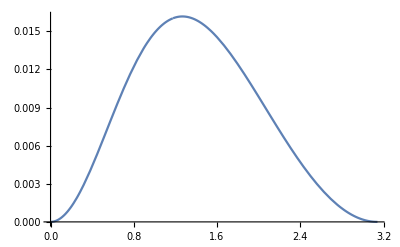

```mathematica
Plot[ZyzSimp[θ, 1, 4],{θ,0,π}]
```

## 3D, Isotropic, Plus-Polarised Wave: Work in Progress

### Basic metric, radially decreasing

```mathematica
h3DIso = Simplify[Rx[B[DP[tP,t], dG, θ,ϕ]].Ry[-A[DP[tP,t], dG, θ,ϕ]].(P/RP[dG,tP, t,θ]).Transpose[Ry[-A[DP[tP,t], dG, θ,ϕ]]].Transpose[Rx[B[DP[tP,t], dG, θ,ϕ]]]];
MatrixForm[h3DIso]
```

((dG+(t-tP) Cos[θ])^2/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)) | Piecewise[{{-((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}] | Piecewise[{{-Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]
Piecewise[{{-((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}] | (-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)) | -((dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[2 ArcTan[((-t+tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))
Piecewise[{{-Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}] | -((dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[2 ArcTan[((-t+tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)) | -((t-tP)^2 Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2-Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))

### Applying Trig Simplifications

```mathematica
SinSimp[opp, adj]  (*Simplifies Sin[2ArcTan[opp/adj]]*)
```

(2 adj opp)/(adj^2+opp^2)

```mathematica
h3DIso = FullSimplify[({{(dG+(t-tP) Cos[θ])^2/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)), Piecewise[{{-((t-tP) Sin[θ] Sin[ϕ] SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) Sin[θ] Sin[ϕ] SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}], Piecewise[{{-SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]}, {Piecewise[{{-((t-tP) Sin[θ] Sin[ϕ] SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) Sin[θ] Sin[ϕ] SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}], (-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)), -((dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)SinSimp[(-t+tP) Sin[θ] Sin[ϕ], dG+(t-tP) Cos[θ]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))}, {Piecewise[{{-SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}], -((dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)SinSimp[(-t+tP) Sin[θ] Sin[ϕ], dG+(t-tP) Cos[θ]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)), -((t-tP)^2 Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2-Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))}})];
```

```mathematica
MatrixForm[h3DIso]
```

((dG+(t-tP) Cos[θ])^2/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)) | Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}] | Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((-t+tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]
Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}] | (-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)) | ((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ] ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))
Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((-t+tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}] | ((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ] ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)) | ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2)/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))

### Considering If statements

In all cases, the different between the two possible IF statements is a negative sign.

(dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)

(dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP) 
θ is always greater than 0 and is ill-defined when it equals 0.

(θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP)
If dG+t<tP then dG+t≥tP must be false. tP-t = dP (distance from Earth to the photon), so this is saying dG < dP.

(θ≤ArcCos[dG/(-t+tP)])&&(dG+t<tP)
The max value of θ is π and if dP > dG, ArcCos[dG/dP]<π, so θ+ArcCos[dG/(-t+tP)]< 2π.
What this If statement is saying is that if dP > dG (the distance from Earth to the photon is larger than the distance to the GW source), there is a cuttoff angle given by ArcCos[dG/dP] below which there is a sign flip for some entries of h_ij.

```mathematica
h3DIso = ({{(dG+(t-tP) Cos[θ])^2/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)), Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (θ≤ArcCos[dG/(-t+tP)])&&(dG+t<tP)}, {-(((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}], Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (θ≤ArcCos[dG/(-t+tP)])&&(dG+t<tP)}, {((-t+tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]}, {Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (θ≤ArcCos[dG/(-t+tP)])&&(dG+t<tP)}, {-(((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}], (-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)), ((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ] ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))}, {Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (θ≤ArcCos[dG/(-t+tP)])&&(dG+t<tP)}, {((-t+tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}], ((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ] ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)), ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2)/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))}});
```

### Redshift

```mathematica
v[θ, ϕ] (*3D looking vector *)
```

{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}

```mathematica
Simplify[v[θ, ϕ].Transpose[v[θ,ϕ].h3DIso]] (*applying 3D looking vector twice*)
```

Cos[θ] Cos[ϕ] (Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {((-t+tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]) Sin[θ]+Cos[ϕ] (Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]) Sin[θ]^2 Sin[ϕ]+Cos[ϕ] Sin[θ] (Cos[θ] (Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {((-t+tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}])+((dG+(t-tP) Cos[θ])^2 Cos[ϕ] Sin[θ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))+(Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]) Sin[θ] Sin[ϕ])+(2 (t-tP) Cos[θ] (dG+(t-tP) Cos[θ]) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2)/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(Sin[θ]^2 Sin[ϕ]^2 (-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(Cos[θ]^2 ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))

```mathematica
H3DIso[t_] := Cos[θ] Cos[ϕ] (Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {((-t+tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]) Sin[θ]+Cos[ϕ] (Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]) Sin[θ]^2 Sin[ϕ]+Cos[ϕ] Sin[θ] (Cos[θ] (Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {((-t+tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}])+((dG+(t-tP) Cos[θ])^2 Cos[ϕ] Sin[θ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))+(Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]) Sin[θ] Sin[ϕ])+(2 (t-tP) Cos[θ] (dG+(t-tP) Cos[θ]) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2)/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(Sin[θ]^2 Sin[ϕ]^2 (-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(Cos[θ]^2 ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))
```

```mathematica
ζ3DIso = Simplify[H3DIso[Tmin[tG, tP, dG,θ]]]
```

1/2 Sin[θ] (2 Cos[θ] Cos[ϕ] (Piecewise[{{(2 tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]&&2 dG^2<tP^2+2 dG^2 Cos[θ]}, {-((2 tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}])+2 Cos[ϕ] (Cos[θ] (Piecewise[{{(2 tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]&&2 dG^2<tP^2+2 dG^2 Cos[θ]}, {-((2 tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}])+(2 (dG+tP-dG Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))+(Piecewise[{{(tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ]^2 Sin[2 ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]&&2 dG^2<tP^2+2 dG^2 Cos[θ]}, {-((tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ]^2 Sin[2 ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ] Sin[ϕ])+(8 tP (2 dG+tP) Cos[θ] (dG+tP-dG Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Sin[θ] (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(4 (dG+tP-dG Cos[θ]) Sin[θ] Sin[ϕ]^2 (-(dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)))+(Piecewise[{{(tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ]^2 Sin[2 ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]&&2 dG^2<tP^2+2 dG^2 Cos[θ]}, {-((tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ]^2 Sin[2 ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ] Sin[2 ϕ]+(tP^2 (2 dG+tP)^2 Cos[θ]^2 (dG+tP-dG Cos[θ]) Sin[θ] (4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[2 ϕ]-tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[2 ϕ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)))

```mathematica
χ[dP_, dG_, θ_,ϕ_] :=  If[θ<=M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]+π,If[θ<=2π-M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]-π]] (*angle between n and R*)
```

```mathematica
vdotR3D = FullSimplify[Cos[π - θ - χ[DP[tP,Tmin[tG, tP, dG,θ]], dG, θ,ϕ]]]
```

Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}]

```mathematica
Simplify[-1/2 1/Abs[1+vdotR3D] ζ3DIso ] (*full redshift equation*)
```

-((Sin[θ] (2 Cos[θ] Cos[ϕ] (Piecewise[{{(2 tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]&&2 dG^2<tP^2+2 dG^2 Cos[θ]}, {-((2 tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}])+2 Cos[ϕ] (Cos[θ] (Piecewise[{{(2 tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]&&2 dG^2<tP^2+2 dG^2 Cos[θ]}, {-((2 tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}])+(2 (dG+tP-dG Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))+(Piecewise[{{(tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ]^2 Sin[2 ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]&&2 dG^2<tP^2+2 dG^2 Cos[θ]}, {-((tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ]^2 Sin[2 ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ] Sin[ϕ])+(8 tP (2 dG+tP) Cos[θ] (dG+tP-dG Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Sin[θ] (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(4 (dG+tP-dG Cos[θ]) Sin[θ] Sin[ϕ]^2 (-(dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)))+(Piecewise[{{(tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ]^2 Sin[2 ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]&&2 dG^2<tP^2+2 dG^2 Cos[θ]}, {-((tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ]^2 Sin[2 ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ] Sin[2 ϕ]+(tP^2 (2 dG+tP)^2 Cos[θ]^2 (dG+tP-dG Cos[θ]) Sin[θ] (4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[2 ϕ]-tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[2 ϕ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))))/(4 Abs[1+(Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}])]))

```mathematica
z3DIsoTrigandIfSimp[θ_,ϕ_, dG_, tP_] := -((Sin[θ] (2 Cos[θ] Cos[ϕ] (Piecewise[{{(2 tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]&&2 dG^2<tP^2+2 dG^2 Cos[θ]}, {-((2 tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}])+2 Cos[ϕ] (Cos[θ] (Piecewise[{{(2 tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]&&2 dG^2<tP^2+2 dG^2 Cos[θ]}, {-((2 tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}])+(2 (dG+tP-dG Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))+(Piecewise[{{(tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ]^2 Sin[2 ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]&&2 dG^2<tP^2+2 dG^2 Cos[θ]}, {-((tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ]^2 Sin[2 ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ] Sin[ϕ])+(8 tP (2 dG+tP) Cos[θ] (dG+tP-dG Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Sin[θ] (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(4 (dG+tP-dG Cos[θ]) Sin[θ] Sin[ϕ]^2 (-(dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)))+(Piecewise[{{(tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ]^2 Sin[2 ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]&&2 dG^2<tP^2+2 dG^2 Cos[θ]}, {-((tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ]^2 Sin[2 ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ] Sin[2 ϕ]+(tP^2 (2 dG+tP)^2 Cos[θ]^2 (dG+tP-dG Cos[θ]) Sin[θ] (4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[2 ϕ]-tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[2 ϕ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))))/(4 Abs[1+(Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}])]))
```

```mathematica
z3DIso[θ_,ϕ_, dG_, tP_] := -((Sin[θ] (Cos[θ] Cos[ϕ] (Piecewise[{{(Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}])+Cos[ϕ] (Piecewise[{{(tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ] Sin[ϕ] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ] Sin[ϕ] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ] Sin[ϕ]+Cos[ϕ] (Cos[θ] (Piecewise[{{(Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}])+(2 (dG+tP-dG Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))+(Piecewise[{{(tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ] Sin[ϕ] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ] Sin[ϕ] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ] Sin[ϕ])+(8 (dG+tP-dG Cos[θ])^3 Sin[θ] Sin[ϕ]^2 (-(dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(2 tP^2 (2 dG+tP)^2 Cos[θ]^2 (dG+tP-dG Cos[θ]) Sin[θ] (-(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Sin[ϕ]^2+Cos[ϕ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2-tP^4 Sin[θ]^2 Sin[ϕ]^2)-dG tP^2 (dG+tP) Sin[θ]^2 Sin[2 ϕ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(2 Cos[θ] (dG+tP-dG Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ] Sin[2 ArcTan[(tP (2 dG+tP) Sin[θ] Sin[ϕ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))))/(2 Abs[1+(Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}])]))
```

### Small Angle Approximation

Taking the limit for θ -> 0. This gives a small patch of sky around the GW source as viewed from Earth. ϕ can still vary from 0 to 2π.  Cos[θ] -> 1 and Sin[θ] -> θ

```mathematica
h3DIsoApprox = ({{(dG+(t-tP) 1)^2/(√(dG^2+(t-tP)^2+2 dG (t-tP) 1) ((dG+(t-tP) 1)^2+(t-tP)^2 Cos[ϕ]^2 (θ)^2)), Piecewise[{{((t-tP)^2 Cos[ϕ] θ^2 Sin[ϕ])/(((dG+(t-tP) 1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP) 1) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+(t-tP) 1)^2))), (θ≤ArcCos[dG/(-t+tP)])&&(dG+t<tP)}, {-(((t-tP)^2 Cos[ϕ] θ^2 Sin[ϕ])/(((dG+(t-tP) 1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP) 1) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+(t-tP) 1)^2)))), True}}], Piecewise[{{((t-tP) (dG+(t-tP) 1) Cos[ϕ] θ)/(((dG+(t-tP) 1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP) 1) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+(t-tP) 1)^2))), (θ≤ArcCos[dG/(-t+tP)])&&(dG+t<tP)}, {((-t+tP) (dG+(t-tP) 1) Cos[ϕ] θ)/(((dG+(t-tP) 1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP) 1) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+(t-tP) 1)^2))), True}}]}, {Piecewise[{{((t-tP)^2 Cos[ϕ] θ^2 Sin[ϕ])/(((dG+(t-tP) 1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP) 1) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+(t-tP) 1)^2))), (θ≤ArcCos[dG/(-t+tP)])&&(dG+t<tP)}, {-(((t-tP)^2 Cos[ϕ] θ^2 Sin[ϕ])/(((dG+(t-tP)1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP) 1) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+(t-tP) 1)^2)))), True}}], (-(dG+(t-tP) 1)^2+((t-tP)^4 Cos[ϕ]^2 θ^4 Sin[ϕ]^2)/((dG+(t-tP) 1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) 1) ((dG+(t-tP) 1)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), ((t-tP) (dG+(t-tP) 1) θ ((dG+(t-tP) 1)^2+2 (t-tP)^2 Cos[ϕ]^2 θ^2) Sin[ϕ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) 1) ((dG+(t-tP) 1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) ((dG+(t-tP) 1)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))}, {Piecewise[{{((t-tP) (dG+(t-tP) 1) Cos[ϕ] θ)/(((dG+(t-tP) 1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP)1) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+(t-tP) 1)^2))), (θ≤ArcCos[dG/(-t+tP)])&&(dG+t<tP)}, {((-t+tP) (dG+(t-tP) 1) Cos[ϕ] θ)/(((dG+(t-tP)1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP) 1) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+(t-tP) 1)^2))), True}}], ((t-tP) (dG+(t-tP) 1) θ ((dG+(t-tP) 1)^2+2 (t-tP)^2 Cos[ϕ]^2 θ^2) Sin[ϕ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) 1) ((dG+(t-tP) 1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) ((dG+(t-tP) 1)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), ((t-tP)^2 (dG+(t-tP) 1)^2 Cos[2 ϕ] θ^2-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2)/(√(dG^2+(t-tP)^2+2 dG (t-tP) 1) ((dG+(t-tP) 1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) ((dG+(t-tP) 1)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))}});
```

```mathematica
vApprox[θ_, ϕ_] := {Cos[ϕ] θ,θ Sin[ϕ],1}
```

```mathematica
vApprox[θ, ϕ]
```

{θ Cos[ϕ],θ Sin[ϕ],1}

### Approximate Redshift (small θ approximation)

```mathematica
Simplify[vApprox[θ, ϕ].Transpose[vApprox[θ,ϕ].h3DIsoApprox]] (*applying approximate 3D looking vector twice*)
```

((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ^2 Sin[ϕ] (-(dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP) (dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2)/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))

```mathematica
H3DIsoApprox[t_] := ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ^2 Sin[ϕ] (-(dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP) (dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2)/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))
```

```mathematica
Tmin[tG, tP, dG,θ]
```

(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ])

```mathematica
ζ3DIso = Simplify[H3DIsoApprox[(tP^2-2 dG tP 1)/(2 dG+2 tP-2 dG 1)]] (*plugging in approximate Tmin for small θ*)
```

(θ (4 tP^6 (2 dG+tP)^2 θ Cos[2 ϕ]+4 tP^3 (2 dG+tP) θ (tP^4+2 tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+2 tP Cos[ϕ] (tP^4+tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{(2 tP (2 dG+tP) θ Cos[ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[(2 dG)/(2 dG+tP)]}, {-(2 tP (2 dG+tP) θ Cos[ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), True}}]) (tP^4+tP^2 (2 dG+tP)^2 θ^2 Sin[ϕ]^2)+2 tP Cos[ϕ] (2 tP^3 θ Cos[ϕ]+(tP^4+tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{(2 tP (2 dG+tP) θ Cos[ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[(2 dG)/(2 dG+tP)]}, {-(2 tP (2 dG+tP) θ Cos[ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ (tP^4+tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((2 dG+tP)^2 θ^2 Sin[2 ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[(2 dG)/(2 dG+tP)]}, {-((2 dG+tP)^2 θ^2 Sin[2 ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) (tP^4+tP^2 (2 dG+tP)^2 θ^2 Sin[ϕ]^2)-2 tP^3 θ Sin[ϕ] (2 tP (tP^4+tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-2 (2 dG+tP) (tP^4+2 tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-2 tP (2 dG+tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3-tP^2 Cos[ϕ] (tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((2 dG+tP)^2 θ^2 Sin[2 ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[(2 dG)/(2 dG+tP)]}, {-((2 dG+tP)^2 θ^2 Sin[2 ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), True}}]) (tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2))-tP^4 (2 dG+tP)^4 θ^3 Sin[2 ϕ]^2))/(2 tP^5 (tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) (tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2))

```mathematica
χApprox[dP_, dG_, θ_,ϕ_] :=  If[θ<=M[dP, dG],ArcTan[(dP θ)/(dG - dP 1)]+π,If[θ<=2π-M[dP, dG],ArcTan[(dP θ)/(dG - dP 1)],ArcTan[(dP θ)/(dG - dP 1)]-π]] (*approx angle between n and R*)
```

```mathematica
vdotR3DApprox = FullSimplify[Cos[π - θ - χApprox[DP[tP,(tP^2-2 dG tP 1)/(2 dG+2 tP-2 dG 1)], dG, θ,ϕ]]] (*also manually plugging in approximate Tmin*)
```

Piecewise[{{-Cos[θ-ArcTan[θ+(2 dG θ)/tP]], θ+ArcCos[(2 dG)/(2 dG+tP)]≤2 π&&θ>ArcCos[(2 dG)/(2 dG+tP)]}, {Cos[θ-ArcTan[θ+(2 dG θ)/tP]], True}}]

```mathematica
FullSimplify[-1/2 1/Abs[1+vdotR3DApprox] ζ3DIso ] (*full redshift equation*)
```

```mathematica
z3DIsoApprox[θ_,ϕ_, dG_, tP_] := -((θ (4 tP^6 (2 dG+tP)^2 θ Cos[2 ϕ]+4 tP^3 (2 dG+tP) θ (tP^4+2 tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+2 tP Cos[ϕ] (tP^4+tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{(2 tP (2 dG+tP) θ Cos[ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[(2 dG)/(2 dG+tP)]}, {-(2 tP (2 dG+tP) θ Cos[ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), True}}]) (tP^4+tP^2 (2 dG+tP)^2 θ^2 Sin[ϕ]^2)+2 tP Cos[ϕ] (2 tP^3 θ Cos[ϕ]+(tP^4+tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{(2 tP (2 dG+tP) θ Cos[ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[(2 dG)/(2 dG+tP)]}, {-(2 tP (2 dG+tP) θ Cos[ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ (tP^4+tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((2 dG+tP)^2 θ^2 Sin[2 ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[(2 dG)/(2 dG+tP)]}, {-((2 dG+tP)^2 θ^2 Sin[2 ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) (tP^4+tP^2 (2 dG+tP)^2 θ^2 Sin[ϕ]^2)-2 tP^3 θ Sin[ϕ] (2 tP (tP^4+tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-2 (2 dG+tP) (tP^4+2 tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-2 tP (2 dG+tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3-tP^2 Cos[ϕ] (tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((2 dG+tP)^2 θ^2 Sin[2 ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[(2 dG)/(2 dG+tP)]}, {-((2 dG+tP)^2 θ^2 Sin[2 ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), True}}]) (tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2))-tP^4 (2 dG+tP)^4 θ^3 Sin[2 ϕ]^2))/(4 tP^5 Abs[1+(Piecewise[{{-Cos[θ-ArcTan[θ+(2 dG θ)/tP]], θ+ArcCos[(2 dG)/(2 dG+tP)]≤2 π&&θ>ArcCos[(2 dG)/(2 dG+tP)]}, {Cos[θ-ArcTan[θ+(2 dG θ)/tP]], True}}])] (tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) (tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)))
```

### Plotting

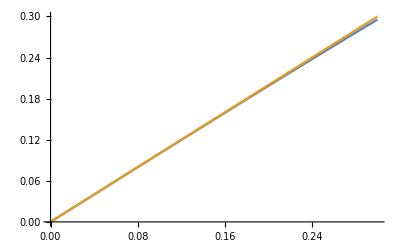

```mathematica
Plot[{Sin[x],x},{x,0,0.3}]
```

```mathematica
Manipulate[Labeled[Plot[z3DIsoApprox[θ, ϕ, dG, tP] ,{θ,0, 0.3}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,40}, {ϕ,0,2π}]
```

Discontinuity when dG/tP > 10 for a max θ of 0.3. It might be physical, from the instant heavystep function? 
Example: dG = 19.6, tP = 0.45, ϕ = 0, cutoff at θ=0.15

```mathematica
24.4/2.3
```

10.6087

```mathematica
N[π/2]
```

1.5708

```mathematica
Manipulate[Labeled[Plot[z3DIsoTrigandIfSimp[θ, ϕ, dG, tP] ,{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,40}, {ϕ,0,2π}]
```

Discontinuity at dG = 0.1, tP=28, ϕ=0, goes to 0 at θ = π/2
Discontinuity when tP >> dG for θ = π/2, but only when ϕ is not π/2 
Same discontinuity for any value of tP and dG. Example: dG = 4.65, tP = 11.3, ϕ = 1.55, θ = 1.0

```mathematica
Manipulate[Labeled[Plot[z3DIso[θ, ϕ, dG, tP] ,{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,40}, {ϕ,0,2π}]
```

```mathematica
Manipulate[Labeled[Plot[zSimp[θ, dG, tP] ,{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,40}]
```

```mathematica
Manipulate[Labeled[SphericalPlot3D[z3DIso[θ, ϕ, dG, tP] ,{θ,0.001, π-0.001},{ϕ,0.001,2π-0.001}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],}],Top],{dG,0.1,30},{tP,0.01,40}]
```

Max::nord: Invalid comparison with 6.05793-0.611681 ⅈ attempted.

Max::nord: Invalid comparison with 0.225257-0.611681 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Min::nord2: Comparison of Max[-6.05793+0.611681 ⅈ,-0.225257+0.611681 ⅈ,0.125263] and ∞ is invalid.

Min::nord2: Comparison of Max[-6.05793+0.611681 ⅈ,-0.225257+0.611681 ⅈ,0.000405264] and ∞ is invalid.

Min::nord2: Comparison of Max[0.0207383,6.05793-0.611681 ⅈ] and ∞ is invalid.

General::stop: Further output of Min::nord2 will be suppressed during this calculation.

Max::nord: Invalid comparison with 6.05793-3.74048 ⅈ attempted.

Max::nord: Invalid comparison with 0.225257-3.74048 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Min::nord2: Comparison of Max[-6.05793+3.74048 ⅈ,-0.225257+3.74048 ⅈ,3.1933] and ∞ is invalid.

Min::nord2: Comparison of Max[3.1933,6.05793-3.74048 ⅈ] and ∞ is invalid.

Min::nord2: Comparison of Max[0.225257-3.74048 ⅈ,3.1933] and ∞ is invalid.

General::stop: Further output of Min::nord2 will be suppressed during this calculation.

```mathematica
Manipulate[Labeled[SphericalPlot3D[1,{θ,0,Pi},{φ,0,2 Pi},ColorFunction->Function[{θ,ϕ},z3DIso[θ, ϕ, dG, tP]],ColorFunctionScaling->True,PlotPoints->50,Lighting->"Neutral",Mesh->None],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],}],Top],{dG,0.1,30},{tP,0.01,40}]
```

### Redshift in terms of x=tP/dG

```mathematica
z3DIsoApprox[θ_,ϕ_, dG_, tP_] := -((θ (4 tP^6 (2 dG+tP)^2 θ Cos[2 ϕ]+4 tP^3 (2 dG+tP) θ (tP^4+2 tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+2 tP Cos[ϕ] (tP^4+tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{(2 tP (2 dG+tP) θ Cos[ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[(2 dG)/(2 dG+tP)]}, {-(2 tP (2 dG+tP) θ Cos[ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), True}}]) (tP^4+tP^2 (2 dG+tP)^2 θ^2 Sin[ϕ]^2)+2 tP Cos[ϕ] (2 tP^3 θ Cos[ϕ]+(tP^4+tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{(2 tP (2 dG+tP) θ Cos[ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[(2 dG)/(2 dG+tP)]}, {-(2 tP (2 dG+tP) θ Cos[ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ (tP^4+tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((2 dG+tP)^2 θ^2 Sin[2 ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[(2 dG)/(2 dG+tP)]}, {-((2 dG+tP)^2 θ^2 Sin[2 ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) (tP^4+tP^2 (2 dG+tP)^2 θ^2 Sin[ϕ]^2)-2 tP^3 θ Sin[ϕ] (2 tP (tP^4+tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-2 (2 dG+tP) (tP^4+2 tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-2 tP (2 dG+tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3-tP^2 Cos[ϕ] (tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((2 dG+tP)^2 θ^2 Sin[2 ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[(2 dG)/(2 dG+tP)]}, {-((2 dG+tP)^2 θ^2 Sin[2 ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), True}}]) (tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2))-tP^4 (2 dG+tP)^4 θ^3 Sin[2 ϕ]^2))/(4 tP^5 Abs[1+(Piecewise[{{-Cos[θ-ArcTan[θ+(2 dG θ)/tP]], θ+ArcCos[(2 dG)/(2 dG+tP)]≤2 π&&θ>ArcCos[(2 dG)/(2 dG+tP)]}, {Cos[θ-ArcTan[θ+(2 dG θ)/tP]], True}}])] (tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) (tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)))
```

```mathematica
Assuming[θ>ArcCos[(2 dG)/(2 dG+tP)],FullSimplify[z3DIsoApprox[θ,ϕ, dG, tP] ]]
```

(θ^2 (4 tP^3 (2 dG+tP)+4 tP^2 (4 dG^2+2 dG tP+tP^2) Cos[2 ϕ]+4 tP Cos[ϕ]^2 ((4 dG+tP) (8 dG^2+4 dG tP+tP^2) θ^4 Sin[ϕ]^4-2 tP (2 dG+tP) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2))+θ^2 (-((2 dG-3 tP) (2 dG+tP)^3)+8 dG^4 θ^2-2 (4 dG^4 θ^2 Cos[2 ϕ]+tP (2 dG+tP)^2 √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2))) Sin[2 ϕ]^2))/(4 tP (tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) (-1+Cos[θ-ArcTan[θ+(2 dG θ)/tP]]) (tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2))

```mathematica
zApproxAsmGT = (θ^2 (4 tP^3 (2 dG+tP)+4 tP^2 (4 dG^2+2 dG tP+tP^2) Cos[2 ϕ]+4 tP Cos[ϕ]^2 ((4 dG+tP) (8 dG^2+4 dG tP+tP^2) θ^4 Sin[ϕ]^4-2 tP (2 dG+tP) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2))+θ^2 (-((2 dG-3 tP) (2 dG+tP)^3)+8 dG^4 θ^2-2 (4 dG^4 θ^2 Cos[2 ϕ]+tP (2 dG+tP)^2 √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2))) Sin[2 ϕ]^2))/(4 tP (tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) (-1+Cos[θ-ArcTan[θ+(2 dG θ)/tP]]) (tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2))
```

(θ^2 (4 tP^3 (2 dG+tP)+4 tP^2 (4 dG^2+2 dG tP+tP^2) Cos[2 ϕ]+4 tP Cos[ϕ]^2 ((4 dG+tP) (8 dG^2+4 dG tP+tP^2) θ^4 Sin[ϕ]^4-2 tP (2 dG+tP) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2))+θ^2 (-((2 dG-3 tP) (2 dG+tP)^3)+8 dG^4 θ^2-2 (4 dG^4 θ^2 Cos[2 ϕ]+tP (2 dG+tP)^2 √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2))) Sin[2 ϕ]^2))/(4 tP (tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) (-1+Cos[θ-ArcTan[θ+(2 dG θ)/tP]]) (tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2))

```mathematica
Assuming[θ<=ArcCos[(2 dG)/(2 dG+tP)],FullSimplify[z3DIsoApprox[θ,ϕ, dG, tP] ]]
```

(θ^2 (-4 tP^3 (2 dG+tP)-4 tP^2 (4 dG^2+2 dG tP+tP^2) Cos[2 ϕ]-4 tP Cos[ϕ]^2 ((4 dG+tP) (8 dG^2+4 dG tP+tP^2) θ^4 Sin[ϕ]^4+2 tP (2 dG+tP) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2))+θ^2 ((2 dG-3 tP) (2 dG+tP)^3-8 dG^4 θ^2+8 dG^4 θ^2 Cos[2 ϕ]-2 tP (2 dG+tP)^2 √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)) Sin[2 ϕ]^2))/(4 tP (tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) (1+Cos[θ-ArcTan[θ+(2 dG θ)/tP]]) (tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2))

```mathematica
zApproxAsmLT = (θ^2 (-4 tP^3 (2 dG+tP)-4 tP^2 (4 dG^2+2 dG tP+tP^2) Cos[2 ϕ]-4 tP Cos[ϕ]^2 ((4 dG+tP) (8 dG^2+4 dG tP+tP^2) θ^4 Sin[ϕ]^4+2 tP (2 dG+tP) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2))+θ^2 ((2 dG-3 tP) (2 dG+tP)^3-8 dG^4 θ^2+8 dG^4 θ^2 Cos[2 ϕ]-2 tP (2 dG+tP)^2 √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)) Sin[2 ϕ]^2))/(4 tP (tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) (1+Cos[θ-ArcTan[θ+(2 dG θ)/tP]]) (tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2))
```

(θ^2 (-4 tP^3 (2 dG+tP)-4 tP^2 (4 dG^2+2 dG tP+tP^2) Cos[2 ϕ]-4 tP Cos[ϕ]^2 ((4 dG+tP) (8 dG^2+4 dG tP+tP^2) θ^4 Sin[ϕ]^4+2 tP (2 dG+tP) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2))+θ^2 ((2 dG-3 tP) (2 dG+tP)^3-8 dG^4 θ^2+8 dG^4 θ^2 Cos[2 ϕ]-2 tP (2 dG+tP)^2 √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)) Sin[2 ϕ]^2))/(4 tP (tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) (1+Cos[θ-ArcTan[θ+(2 dG θ)/tP]]) (tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2))

x = tP/dG

```mathematica
Block[{tP = dG*x}, FullSimplify[(2 dG)/(2 dG+tP)]]
```

2/(2+x)

```mathematica
Block[{tP = dG*x}, FullSimplify[zApproxAsmGT]]
```

(θ^2 (4 x^3 (2+x)+4 x^2 (4+x (2+x)) Cos[2 ϕ]+4 x Cos[ϕ]^2 ((4+x) (8+x (4+x)) θ^4 Sin[ϕ]^4-2 x (2+x) √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2))+θ^2 ((2+x)^3 (-2+3 x)+8 θ^2-2 (4 θ^2 Cos[2 ϕ]+x (2+x)^2 √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2))) Sin[2 ϕ]^2))/(4 dG x (x^2+(2+x)^2 θ^2 Cos[ϕ]^2) (-1+Cos[θ-ArcTan[((2+x) θ)/x]]) (x^2+(2+x)^2 θ^2 Sin[ϕ]^2))

Multiplying by dG (for dimensional consistency)

```mathematica
Block[{tP = dG*x}, FullSimplify[dG*zApproxAsmGT]]
```

(θ^2 (4 x^3 (2+x)+4 x^2 (4+x (2+x)) Cos[2 ϕ]+4 x Cos[ϕ]^2 ((4+x) (8+x (4+x)) θ^4 Sin[ϕ]^4-2 x (2+x) √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2))+θ^2 ((2+x)^3 (-2+3 x)+8 θ^2-2 (4 θ^2 Cos[2 ϕ]+x (2+x)^2 √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2))) Sin[2 ϕ]^2))/(4 x (x^2+(2+x)^2 θ^2 Cos[ϕ]^2) (-1+Cos[θ-ArcTan[((2+x) θ)/x]]) (x^2+(2+x)^2 θ^2 Sin[ϕ]^2))

When is the denominator 0?

```mathematica
Expand[(x^2+(2+x)^2 θ^2 Cos[ϕ]^2)(x^2+(2+x)^2 θ^2 Sin[ϕ]^2)]
```

x^4+4 x^2 θ^2 Cos[ϕ]^2+4 x^3 θ^2 Cos[ϕ]^2+x^4 θ^2 Cos[ϕ]^2+4 x^2 θ^2 Sin[ϕ]^2+4 x^3 θ^2 Sin[ϕ]^2+x^4 θ^2 Sin[ϕ]^2+16 θ^4 Cos[ϕ]^2 Sin[ϕ]^2+32 x θ^4 Cos[ϕ]^2 Sin[ϕ]^2+24 x^2 θ^4 Cos[ϕ]^2 Sin[ϕ]^2+8 x^3 θ^4 Cos[ϕ]^2 Sin[ϕ]^2+x^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2

denominotar is (x^2+(2+x)^2 θ^2 Cos[ϕ]^2) (-1+Cos[θ-ArcTan[((2+x) θ)/x]]) (x^2+(2+x)^2 θ^2 Sin[ϕ]^2)==0

```mathematica
Solve[ArcTan[((2+x) θ)/x]==θ,x]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

{{x→ConditionalExpression[-(2 θ)/(θ-Tan[θ]), θ<π/2]}}

```mathematica
Block[{x=-(2 θ)/(θ-Tan[θ])}, FullSimplify[ArcTan[((2+x) θ)/x]]] (*denominator goes to 0 when x equatls this! and I think only when it equals this. for the other condition it's...*)
```

ArcTan[Tan[θ]]

```mathematica
Block[{tP = dG*x}, FullSimplify[zApproxAsmLT]]
```

(θ^2 (-4 x^3 (2+x)-4 x^2 (4+x (2+x)) Cos[2 ϕ]-4 x Cos[ϕ]^2 ((4+x) (8+x (4+x)) θ^4 Sin[ϕ]^4+2 x (2+x) √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2))+θ^2 ((2-3 x) (2+x)^3-8 θ^2+8 θ^2 Cos[2 ϕ]-2 x (2+x)^2 √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2)) Sin[2 ϕ]^2))/(4 dG x (x^2+(2+x)^2 θ^2 Cos[ϕ]^2) (1+Cos[θ-ArcTan[((2+x) θ)/x]]) (x^2+(2+x)^2 θ^2 Sin[ϕ]^2))

```mathematica
Block[{tP = dG*x}, FullSimplify[dG*zApproxAsmLT]]
```

(θ^2 (-4 x^3 (2+x)-4 x^2 (4+x (2+x)) Cos[2 ϕ]-4 x Cos[ϕ]^2 ((4+x) (8+x (4+x)) θ^4 Sin[ϕ]^4+2 x (2+x) √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2))+θ^2 ((2-3 x) (2+x)^3-8 θ^2+8 θ^2 Cos[2 ϕ]-2 x (2+x)^2 √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2)) Sin[2 ϕ]^2))/(4 x (x^2+(2+x)^2 θ^2 Cos[ϕ]^2) (1+Cos[θ-ArcTan[((2+x) θ)/x]]) (x^2+(2+x)^2 θ^2 Sin[ϕ]^2))

```mathematica
zApprox[x_, θ_, ϕ_] := Piecewise[{{(θ^2 (4 x^3 (2+x)+4 x^2 (4+x (2+x)) Cos[2 ϕ]+4 x Cos[ϕ]^2 ((4+x) (8+x (4+x)) θ^4 Sin[ϕ]^4-2 x (2+x) √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2))+θ^2 ((2+x)^3 (-2+3 x)+8 θ^2-2 (4 θ^2 Cos[2 ϕ]+x (2+x)^2 √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2))) Sin[2 ϕ]^2))/(4 x (x^2+(2+x)^2 θ^2 Cos[ϕ]^2) (-1+Cos[θ-ArcTan[((2+x) θ)/x]]) (x^2+(2+x)^2 θ^2 Sin[ϕ]^2)),θ>ArcCos[2/(2+x)]}},(θ^2 (-4 x^3 (2+x)-4 x^2 (4+x (2+x)) Cos[2 ϕ]-4 x Cos[ϕ]^2 ((4+x) (8+x (4+x)) θ^4 Sin[ϕ]^4+2 x (2+x) √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2))+θ^2 ((2-3 x) (2+x)^3-8 θ^2+8 θ^2 Cos[2 ϕ]-2 x (2+x)^2 √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2)) Sin[2 ϕ]^2))/(4 x (x^2+(2+x)^2 θ^2 Cos[ϕ]^2) (1+Cos[θ-ArcTan[((2+x) θ)/x]]) (x^2+(2+x)^2 θ^2 Sin[ϕ]^2))];
```

```mathematica
Manipulate[Labeled[Plot[zApprox[x,θ, ϕ] ,{θ,0, 0.1}, PlotRange->All],Row[{"x = ",NumberForm[x,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{x,0.00000001,0.00001},{ϕ,0,2π}]
```

#### Low x-limit and singularity

However, as x approaches 0, the redshift approaches 1/0. I’ve tried to find a finite limit, but I don’t think there is one.
I’m pretty sure the assumptions we make don’t hold for very small values of x. I think this is because the corresponding photons pierced the GW’s spherical wavefront very close to the GW source and very soon after the merger event.
I’ve done some experimenting, and the redshift values become unreasonably large around x = 1E-13. For a GW source at a typical distance of a billion light years away, this correlates to roughly an hour after it passes. (The equation doesn’t hold for times right after the GW is received at Earth). I’m not sure how to justify where to put the cutoff, other than the equation becomes unreasonably large.

```mathematica
Limit[(θ^2 (4 x^3 (2+x)+4 x^2 (4+x (2+x)) Cos[2 ϕ]+4 x Cos[ϕ]^2 ((4+x) (8+x (4+x)) θ^4 Sin[ϕ]^4-2 x (2+x) √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2))+θ^2 ((2+x)^3 (-2+3 x)+8 θ^2-2 (4 θ^2 Cos[2 ϕ]+x (2+x)^2 √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2))) Sin[2 ϕ]^2))/(4 x (x^2+(2+x)^2 θ^2 Cos[ϕ]^2) (-1+Cos[θ-ArcTan[((2+x) θ)/x]]) (x^2+(2+x)^2 θ^2 Sin[ϕ]^2)), x->0]
```

Indeterminate

```mathematica
Collect[Expand[(θ^2 (4 x^3 (2+x)+4 x^2 (4+x (2+x)) Cos[2 ϕ]+4 x Cos[ϕ]^2 ((4+x) (8+x (4+x)) θ^4 Sin[ϕ]^4-2 x (2+x) √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2))+θ^2 ((2+x)^3 (-2+3 x)+8 θ^2-2 (4 θ^2 Cos[2 ϕ]+x (2+x)^2 √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2))) Sin[2 ϕ]^2))],x, Simplify]
```

8 θ^4 (-2+θ^2-θ^2 Cos[2 ϕ]) Sin[2 ϕ]^2+x^4 θ^2 (4+4 Cos[2 ϕ]+4 θ^4 Cos[ϕ]^2 Sin[ϕ]^4+3 θ^2 Sin[2 ϕ]^2)+8 x^2 θ^2 (2 Cos[2 ϕ]+12 θ^4 Cos[ϕ]^2 Sin[ϕ]^4-2 Cos[ϕ]^2 √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2)+3 θ^2 Sin[2 ϕ]^2-θ^2 √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2) Sin[2 ϕ]^2)+2 x^3 θ^2 (4+4 Cos[2 ϕ]+16 θ^4 Cos[ϕ]^2 Sin[ϕ]^4-4 Cos[ϕ]^2 √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2)+8 θ^2 Sin[2 ϕ]^2-θ^2 √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2) Sin[2 ϕ]^2)+x (128 θ^6 Cos[ϕ]^2 Sin[ϕ]^4-8 θ^4 √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2) Sin[2 ϕ]^2)

```mathematica
Collect[Expand[(4 x (x^2+(2+x)^2 θ^2 Cos[ϕ]^2) (-1+Cos[θ-ArcTan[((2+x) θ)/x]]) (x^2+(2+x)^2 θ^2 Sin[ϕ]^2))],x, Simplify]
```

64 x θ^4 Cos[ϕ]^2 (-1+Cos[θ-ArcTan[((2+x) θ)/x]]) Sin[ϕ]^2+8 x^4 θ^2 (-4-θ^2+θ^2 Cos[4 ϕ]) Sin[1/2 (θ-ArcTan[((2+x) θ)/x])]^2+8 x^3 θ^2 (-4-3 θ^2+3 θ^2 Cos[4 ϕ]) Sin[1/2 (θ-ArcTan[((2+x) θ)/x])]^2+x^5 (-8-8 θ^2-θ^4+θ^4 Cos[4 ϕ]) Sin[1/2 (θ-ArcTan[((2+x) θ)/x])]^2-64 x^2 θ^4 Sin[2 ϕ]^2 Sin[1/2 (θ-ArcTan[((2+x) θ)/x])]^2

```mathematica
Limit[ArcTan[x],x->∞]
```

π/2

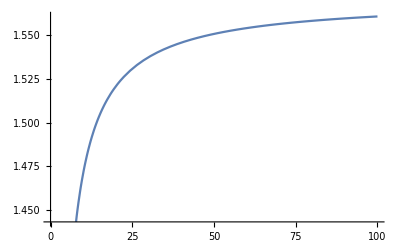

```mathematica
Plot[ArcTan[x],{x,0,100}]
```

```mathematica
Manipulate[Labeled[Plot[4 x (x^2+(2+x)^2 θ^2 Cos[ϕ]^2) (-1+Cos[θ-ArcTan[((2+x) θ)/x]]) (x^2+(2+x)^2 θ^2 Sin[ϕ]^2),{θ,0, 0.15}, PlotRange->All],Row[{"x = ",NumberForm[x,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{x,0.00000001,2},{ϕ,0,2π}]
```

```mathematica
Expand[4 x (x^2+(2+x)^2 θ^2 Cos[ϕ]^2)  (x^2+(2+x)^2 θ^2 Sin[ϕ]^2)]
```

4 x^5+16 x^3 θ^2 Cos[ϕ]^2+16 x^4 θ^2 Cos[ϕ]^2+4 x^5 θ^2 Cos[ϕ]^2+16 x^3 θ^2 Sin[ϕ]^2+16 x^4 θ^2 Sin[ϕ]^2+4 x^5 θ^2 Sin[ϕ]^2+64 x θ^4 Cos[ϕ]^2 Sin[ϕ]^2+128 x^2 θ^4 Cos[ϕ]^2 Sin[ϕ]^2+96 x^3 θ^4 Cos[ϕ]^2 Sin[ϕ]^2+32 x^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2+4 x^5 θ^4 Cos[ϕ]^2 Sin[ϕ]^2

```mathematica
Collect[4 x^5+16 x^3 θ^2 Cos[ϕ]^2+16 x^4 θ^2 Cos[ϕ]^2+4 x^5 θ^2 Cos[ϕ]^2+16 x^3 θ^2 Sin[ϕ]^2+16 x^4 θ^2 Sin[ϕ]^2+4 x^5 θ^2 Sin[ϕ]^2+64 x θ^4 Cos[ϕ]^2 Sin[ϕ]^2+128 x^2 θ^4 Cos[ϕ]^2 Sin[ϕ]^2+96 x^3 θ^4 Cos[ϕ]^2 Sin[ϕ]^2+32 x^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2+4 x^5 θ^4 Cos[ϕ]^2 Sin[ϕ]^2,x]
```

64 x θ^4 Cos[ϕ]^2 Sin[ϕ]^2+128 x^2 θ^4 Cos[ϕ]^2 Sin[ϕ]^2+x^5 (4+4 θ^2 Cos[ϕ]^2+4 θ^2 Sin[ϕ]^2+4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)+x^4 (16 θ^2 Cos[ϕ]^2+16 θ^2 Sin[ϕ]^2+32 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)+x^3 (16 θ^2 Cos[ϕ]^2+16 θ^2 Sin[ϕ]^2+96 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)

### Deflection angle (small θ approximation)

```mathematica
H3DIsoApprox[t_, tP_, θ_, ϕ_] := ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ^2 Sin[ϕ] (-(dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP) (dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2)/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))
```

#### x-deflection

∂/(∂ x) = Sin[θ]Cos[ϕ]∂/(∂ r) + 1/r Cos[ϕ]Cos[θ]∂/(∂ θ)- 1/r Sin[ϕ]/Sin[θ]∂/(∂ ϕ)

either write r in terms of tP and t? or write x in terms of θ, ϕ, etc? Try both and compare. 
In this case, r = DP[tP,  t] = c(tP-t). You can take the derivative with respect to tP or t, they are equal and opposite

```mathematica
Simplify[D[H3DIsoApprox[t, tP, θ, ϕ],tP]+D[H3DIsoApprox[t, tP, θ, ϕ],t]]
```

0

θ Cos[ϕ] D[H3DIsoApprox[t, tP, θ, ϕ],r] + 1/r Cos[ϕ] D[H3DIsoApprox[t, tP, θ, ϕ],θ] - 1/r Sin[ϕ]/θ D[H3DIsoApprox[t, tP, θ, ϕ],ϕ]

```mathematica
θ Cos[ϕ] D[H3DIsoApprox[t, tP, θ, ϕ],tP] + 1/(tP-t)Cos[ϕ] D[H3DIsoApprox[t, tP, θ, ϕ],θ] - 1/(tP-t)Sin[ϕ]/θ D[H3DIsoApprox[t, tP, θ, ϕ],ϕ]
```

```mathematica
(*Define θ and ϕ as functions of x and y, in the flat-sky approximation?? *)
θ[x_,y_]:= Sqrt[x^2+y^2]
```

```mathematica
ϕ[x_,y_]:=ArcTan[y/x]
```

Use Set inseat of SetDelayed. 
Use floating point numbers 
Compile? - maybe no. many Mathematica functions like Table, Plot, NIntegrate, and so on automatically compile their arguments, so you won’t see any improvement when passing them compiled versions of your code.
Module? - or use Block in stead (should be the same but faster) 
Simplfy, use a TimeConstraint
Collect[expression,{a,b,Erfc[_]},Simplify]. This way you prevent mathematica from working on parts of the problem you know won’t simplify like a, b, Erfc.
FullSimplify[Simplify[expr]]
Simplify[Simplify[expr, ComplexityFunction→LeafCount?, TimeConstraint -> 0.1]] run time constraint with Off[General::stop];

Notes on integrating - https://support.wolfram.com/12485 

Piecewise instead of multiple Ifs

```mathematica
hijdr = D[H3DIsoApprox[t, tP, θ, ϕ],tP]
```

-(((-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2) ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ^2 Sin[ϕ] (-(dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP) (dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2))/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2))-((-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ^2 Sin[ϕ] (-(dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP) (dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2))/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ^2 Sin[ϕ] (-(dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP) (dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2) Abs'[dG+t-tP])/(Abs[dG+t-tP]^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(-2 (t-tP)^2 (dG+t-tP) θ^2 Cos[2 ϕ]-2 (t-tP) (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 (-2 (dG+t-tP)-4 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ]^2-(t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2-(dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{-((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))-((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-((t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-((dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ-ArcCos[dG/(-t+tP)]≤0&&dG+t-tP<0}, {((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))+((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+((t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+((dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+(t-tP)^3 θ^4 Sin[2 ϕ]^2-θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) Abs'[dG+t-tP]-θ Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) Abs'[dG+t-tP]+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) ((-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{-((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))-((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-((t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-((dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ-ArcCos[dG/(-t+tP)]≤0&&dG+t-tP<0}, {((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))+((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+((t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+((dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))-((t-tP)^2 θ^2 Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-(2 (t-tP) θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ-ArcCos[dG/(-t+tP)]≤0&&dG+t-tP<0}, {((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))+((t-tP)^2 θ^2 Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(2 (t-tP) θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]-θ Cos[ϕ] Abs'[dG+t-tP])+θ^2 Sin[ϕ] ((t-tP) (dG+t-tP) (-2 (dG+t-tP)-4 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ]-(dG+t-tP)^2 (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ]+2 (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-(t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-(dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-4 (t-tP)^3 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+Abs[dG+t-tP] Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))-((t-tP)^2 θ^2 Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-(2 (t-tP) θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ-ArcCos[dG/(-t+tP)]≤0&&dG+t-tP<0}, {((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))+((t-tP)^2 θ^2 Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(2 (t-tP) θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) Abs'[dG+t-tP]))/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))

```mathematica
Simplify[hijdr, TimeConstraint->1]
```

(-Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2) ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ^2 Sin[ϕ] (-(dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP) (dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2)-Abs[dG+t-tP] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ^2 Sin[ϕ] (-(dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP) (dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2)+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ^2 Sin[ϕ] (-(dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP) (dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2) Abs'[dG+t-tP]+θ Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-2 (t-tP)^2 (dG+t-tP) θ Cos[2 ϕ]-2 (t-tP) (dG+t-tP)^2 θ Cos[2 ϕ]+(t-tP) (dG+t-tP) θ (-2 (dG+t-tP)-4 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ]^2-(t-tP) θ ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2-(dG+t-tP) θ ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+Abs[dG+t-tP] Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{(θ Cos[ϕ] (-((t-tP) (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))-2 (t-tP) (dG+t-tP) (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-2 (t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-2 (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {(θ Cos[ϕ] ((t-tP) (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+2 (t-tP) (dG+t-tP) (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+2 (t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+2 (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+(t-tP)^3 θ^3 Sin[2 ϕ]^2-Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) Abs'[dG+t-tP]-Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) ((-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{(θ Cos[ϕ] (-((t-tP) (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))-2 (t-tP) (dG+t-tP) (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-2 (t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-2 (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {(θ Cos[ϕ] ((t-tP) (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+2 (t-tP) (dG+t-tP) (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+2 (t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+2 (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), True}}])+θ (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) θ^2 Cos[ϕ] Sin[ϕ] (-2 dG^4-5 dG^3 t-3 dG^2 t^2+dG t^3+t^4+5 dG^3 tP+6 dG^2 t tP-3 dG t^2 tP-4 t^3 tP-3 dG^2 tP^2+3 dG t tP^2+6 t^2 tP^2-dG tP^3-4 t tP^3+tP^4+(-dG^2+(t-tP)^2) (t-tP)^2 θ^2 Sin[ϕ]^2+Cos[ϕ]^2 ((t-tP)^3 (dG+t-tP) θ^2+(t^4+6 t^2 tP^2+tP^4) θ^4 Sin[ϕ]^2)-t^3 tP θ^4 Sin[2 ϕ]^2-t tP^3 θ^4 Sin[2 ϕ]^2))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {((t-tP) θ^2 Cos[ϕ] Sin[ϕ] ((t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+2 (t-tP) (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+4 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), True}}]) Sin[ϕ]-θ Cos[ϕ] Abs'[dG+t-tP])+θ Sin[ϕ] ((t-tP) (dG+t-tP) (-2 (dG+t-tP)-4 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ]+2 (dG+t-tP)^2 (dG+t-tP+(t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ]+2 (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-(t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-(dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-4 (t-tP)^3 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+Abs[dG+t-tP] Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) θ^2 Cos[ϕ] Sin[ϕ] (-2 dG^4-5 dG^3 t-3 dG^2 t^2+dG t^3+t^4+5 dG^3 tP+6 dG^2 t tP-3 dG t^2 tP-4 t^3 tP-3 dG^2 tP^2+3 dG t tP^2+6 t^2 tP^2-dG tP^3-4 t tP^3+tP^4+(-dG^2+(t-tP)^2) (t-tP)^2 θ^2 Sin[ϕ]^2+Cos[ϕ]^2 ((t-tP)^3 (dG+t-tP) θ^2+(t^4+6 t^2 tP^2+tP^4) θ^4 Sin[ϕ]^2)-t^3 tP θ^4 Sin[2 ϕ]^2-t tP^3 θ^4 Sin[2 ϕ]^2))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {((t-tP) θ^2 Cos[ϕ] Sin[ϕ] ((t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+2 (t-tP) (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+4 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) Abs'[dG+t-tP])))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2)

## Testing

### Small angle approximation and multiplying by dG

```mathematica
h3DIso = dG*({{(dG+(t-tP) *1)^2/(√(dG^2+(t-tP)^2+2 dG (t-tP) *1) ((dG+(t-tP) *1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2)), Piecewise[{{((t-tP)^2 Cos[ϕ] (θ)^2 Sin[ϕ])/(((dG+(t-tP) *1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP) *1) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+(t-tP) *1)^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-(((t-tP)^2 Cos[ϕ] θ^2 Sin[ϕ])/(((dG+(t-tP) *1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP) *1) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+(t-tP) *1)^2)))), True}}], Piecewise[{{((t-tP) (dG+(t-tP) *1) Cos[ϕ] θ)/(((dG+(t-tP) *1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP) *1) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+(t-tP) *1)^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {((-t+tP) (dG+(t-tP) *1) Cos[ϕ] θ)/(((dG+(t-tP) *1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP) *1) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+(t-tP) *1)^2))), True}}]}, {Piecewise[{{((t-tP)^2 Cos[ϕ] θ^2 Sin[ϕ])/(((dG+(t-tP) *1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP) *1) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+(t-tP) *1)^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-(((t-tP)^2 Cos[ϕ] θ^2 Sin[ϕ])/(((dG+(t-tP) *1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP) *1) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+(t-tP) *1)^2)))), True}}], (-(dG+(t-tP) *1)^2+((t-tP)^4 Cos[ϕ]^2 θ^4 Sin[ϕ]^2)/((dG+(t-tP) *1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) *1) ((dG+(t-tP) *1)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), ((t-tP) (dG+(t-tP) *1) θ ((dG+(t-tP) *1)^2+2 (t-tP)^2 Cos[ϕ]^2 θ^2) Sin[ϕ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) *1) ((dG+(t-tP) *1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) ((dG+(t-tP) *1)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))}, {Piecewise[{{((t-tP) (dG+(t-tP) *1) Cos[ϕ] θ)/(((dG+(t-tP) *1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP) *1) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+(t-tP) *1)^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {((-t+tP) (dG+(t-tP) *1) Cos[ϕ] θ)/(((dG+(t-tP) *1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP) *1) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+(t-tP) *1)^2))), True}}], ((t-tP) (dG+(t-tP) *1) θ ((dG+(t-tP) *1)^2+2 (t-tP)^2 Cos[ϕ]^2 θ^2) Sin[ϕ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) *1) ((dG+(t-tP) *1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) ((dG+(t-tP) *1)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), ((t-tP)^2 (dG+(t-tP) *1)^2 Cos[2 ϕ] θ^2-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2)/(√(dG^2+(t-tP)^2+2 dG (t-tP) *1) ((dG+(t-tP) *1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) ((dG+(t-tP) *1)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))}});
```

```mathematica
h23 = h3DIso[[2,3]]
h23dx = Simplify[Simplify[θ Cos[ϕ] D[h23,tP]  + 1/(tP-t)Cos[ϕ] D[h23,θ]   - 1/(tP-t)Sin[ϕ]/θ D[h23,ϕ], TimeConstraint->1],TimeConstraint->10] (*partial with respect to x*)
h23dxInt = Integrate[h23dx,t]
h23dxInt = Simplify[h23dxInt, TimeConstraint->20]
```

(dG (t-tP) (dG+t-tP) θ ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ])/(√(dG^2+2 dG (t-tP)+(t-tP)^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))

-((dG (dG+t-tP) θ^2 (16 dG^6+64 dG^5 t+112 dG^4 t^2+128 dG^3 t^3+112 dG^2 t^4+64 dG t^5+16 t^6-64 dG^5 tP-224 dG^4 t tP-384 dG^3 t^2 tP-448 dG^2 t^3 tP-320 dG t^4 tP-96 t^5 tP+112 dG^4 tP^2+384 dG^3 t tP^2+672 dG^2 t^2 tP^2+640 dG t^3 tP^2+240 t^4 tP^2-128 dG^3 tP^3-448 dG^2 t tP^3-640 dG t^2 tP^3-320 t^3 tP^3+112 dG^2 tP^4+320 dG t tP^4+240 t^2 tP^4-64 dG tP^5-96 t tP^5+16 tP^6+32 dG^4 t^2 θ^2+64 dG^3 t^3 θ^2+16 dG^2 t^4 θ^2-32 dG t^5 θ^2-16 t^6 θ^2-64 dG^4 t tP θ^2-192 dG^3 t^2 tP θ^2-64 dG^2 t^3 tP θ^2+160 dG t^4 tP θ^2+96 t^5 tP θ^2+32 dG^4 tP^2 θ^2+192 dG^3 t tP^2 θ^2+96 dG^2 t^2 tP^2 θ^2-320 dG t^3 tP^2 θ^2-240 t^4 tP^2 θ^2-64 dG^3 tP^3 θ^2-64 dG^2 t tP^3 θ^2+320 dG t^2 tP^3 θ^2+320 t^3 tP^3 θ^2+16 dG^2 tP^4 θ^2-160 dG t tP^4 θ^2-240 t^2 tP^4 θ^2+32 dG tP^5 θ^2+96 t tP^5 θ^2-16 tP^6 θ^2+10 dG^2 t^4 θ^4-8 dG t^5 θ^4-18 t^6 θ^4-40 dG^2 t^3 tP θ^4+40 dG t^4 tP θ^4+108 t^5 tP θ^4+60 dG^2 t^2 tP^2 θ^4-80 dG t^3 tP^2 θ^4-270 t^4 tP^2 θ^4-40 dG^2 t tP^3 θ^4+80 dG t^2 tP^3 θ^4+360 t^3 tP^3 θ^4+10 dG^2 tP^4 θ^4-40 dG t tP^4 θ^4-270 t^2 tP^4 θ^4+8 dG tP^5 θ^4+108 t tP^5 θ^4-18 tP^6 θ^4-2 t^6 θ^6+12 t^5 tP θ^6-30 t^4 tP^2 θ^6+40 t^3 tP^3 θ^6-30 t^2 tP^4 θ^6+12 t tP^5 θ^6-2 tP^6 θ^6-(t-tP)^2 θ^2 (-48 dG^4-128 dG^3 (t-tP)+32 dG (t-tP)^3-16 dG^2 (t-tP)^2 (5+θ^2)+(t-tP)^4 (32+16 θ^2+θ^4)) Cos[2 ϕ]+2 (t-tP)^4 θ^4 (3 dG^2+4 dG (t-tP)+(t-tP)^2 (1+θ^2)) Cos[4 ϕ]+t^6 θ^6 Cos[6 ϕ]-6 t^5 tP θ^6 Cos[6 ϕ]+15 t^4 tP^2 θ^6 Cos[6 ϕ]-20 t^3 tP^3 θ^6 Cos[6 ϕ]+15 t^2 tP^4 θ^6 Cos[6 ϕ]-6 t tP^5 θ^6 Cos[6 ϕ]+tP^6 θ^6 Cos[6 ϕ]) Sin[2 ϕ])/(32 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2))

Piecewise[{{-1/32 dG θ^2 (-(16 (t-tP) (1+3 Cos[2 ϕ]) Sec[2 ϕ])/(-2 dG^2-4 dG (t-tP)-2 (t-tP)^2-(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ])-(8 (-8 dG-8 (t-tP)+8 (t-tP) θ^2+3 (t-tP) θ^4+8 (t-tP) θ^2 Cos[2 ϕ]+4 (t-tP) θ^4 Cos[2 ϕ]+(t-tP) θ^4 Cos[4 ϕ]) Sec[2 ϕ])/(θ^2 (2+θ^2+θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ]))+(16 ArcTan[((2 dG+2 (t-tP)+(t-tP) θ^2+(t-tP) θ^2 Cos[2 ϕ]) √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Sec[ϕ])/(2 dG θ (2+θ^2+θ^2 Cos[2 ϕ]))] √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Sec[ϕ] Sec[2 ϕ]^2)/(dG θ^3 (2+θ^2+θ^2 Cos[2 ϕ]))-(32 ArcTan[((2 dG+2 (t-tP)+(t-tP) θ^2-(t-tP) θ^2 Cos[2 ϕ]) √(4+4 θ^2+θ^4-4 θ^2 Cos[2 ϕ]-2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Csc[ϕ])/(2 dG θ (-2-θ^2+θ^2 Cos[2 ϕ]))] √(4+4 θ^2+θ^4-4 θ^2 Cos[2 ϕ]-2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Sec[2 ϕ]^2 Sin[ϕ])/(dG θ^3 (-2-θ^2+θ^2 Cos[2 ϕ]))) Sin[2 ϕ], dG+t-tP≥0}, {1/4 dG θ^2 Sec[2 ϕ] (-(2 (t-tP) Cos[2 ϕ] (1+3 Cos[2 ϕ]))/(-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])-(Cos[2 ϕ] (-8 dG-8 t+8 tP+8 t θ^2-8 tP θ^2+3 t θ^4-3 tP θ^4+4 (t-tP) θ^2 (2+θ^2) Cos[2 ϕ]+(t-tP) θ^4 Cos[4 ϕ]))/(θ^2 (2+θ^2+θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))+(2 ArcTan[(√((2+θ^2+θ^2 Cos[2 ϕ])^2) (2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) Sec[ϕ])/(2 dG θ (2+θ^2+θ^2 Cos[2 ϕ]))] √((2+θ^2+θ^2 Cos[2 ϕ])^2) Sec[ϕ])/(dG θ^3 (2+θ^2+θ^2 Cos[2 ϕ]))+(4 ArcTan[(√((2+θ^2-θ^2 Cos[2 ϕ])^2) (-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) Csc[ϕ])/(2 dG θ (-2-θ^2+θ^2 Cos[2 ϕ]))] √((2+θ^2-θ^2 Cos[2 ϕ])^2) Sin[ϕ])/(dG θ^3 (-2-θ^2+θ^2 Cos[2 ϕ]))) Tan[2 ϕ], True}}]

Piecewise[{{1/4 (-(2 dG (t-tP) θ^2 (1+3 Cos[2 ϕ]))/(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])-(dG (8 dG+8 t-8 tP-8 t θ^2+8 tP θ^2-3 t θ^4+3 tP θ^4-4 (t-tP) θ^2 (2+θ^2) Cos[2 ϕ]-(t-tP) θ^4 Cos[4 ϕ]))/((2+θ^2+θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))-(2 ArcTan[((2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) Sec[ϕ])/(2 dG θ)] Sec[ϕ] Sec[2 ϕ])/θ-(4 ArcTan[((-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) Csc[ϕ])/(2 dG θ)] Sec[2 ϕ] Sin[ϕ])/θ) Tan[2 ϕ], dG+t≥tP}, {1/4 ((2 dG (t-tP) θ^2 (1+3 Cos[2 ϕ]))/(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])-(dG (-8 dG-8 t+8 tP+8 t θ^2-8 tP θ^2+3 t θ^4-3 tP θ^4+4 (t-tP) θ^2 (2+θ^2) Cos[2 ϕ]+(t-tP) θ^4 Cos[4 ϕ]))/((2+θ^2+θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))+(2 ArcTan[((2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) Sec[ϕ])/(2 dG θ)] Sec[ϕ] Sec[2 ϕ])/θ-(4 ArcTan[((2 dG+(t-tP) (2+θ^2)-(t-tP) θ^2 Cos[2 ϕ]) Csc[ϕ])/(2 dG θ)] Sec[2 ϕ] Sin[ϕ])/θ) Tan[2 ϕ], True}}]

```mathematica
h23Int[t_] := Piecewise[{{1/4 (-(2 dG (t-tP) θ^2 (1+3 Cos[2 ϕ]))/(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])-(dG (8 dG+8 t-8 tP-8 t θ^2+8 tP θ^2-3 t θ^4+3 tP θ^4-4 (t-tP) θ^2 (2+θ^2) Cos[2 ϕ]-(t-tP) θ^4 Cos[4 ϕ]))/((2+θ^2+θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))-(2 ArcTan[((2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) Sec[ϕ])/(2 dG θ)] Sec[ϕ] Sec[2 ϕ])/θ-(4 ArcTan[((-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) Csc[ϕ])/(2 dG θ)] Sec[2 ϕ] Sin[ϕ])/θ) Tan[2 ϕ], dG+t≥tP}, {1/4 ((2 dG (t-tP) θ^2 (1+3 Cos[2 ϕ]))/(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])-(dG (-8 dG-8 t+8 tP+8 t θ^2-8 tP θ^2+3 t θ^4-3 tP θ^4+4 (t-tP) θ^2 (2+θ^2) Cos[2 ϕ]+(t-tP) θ^4 Cos[4 ϕ]))/((2+θ^2+θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))+(2 ArcTan[((2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) Sec[ϕ])/(2 dG θ)] Sec[ϕ] Sec[2 ϕ])/θ-(4 ArcTan[((2 dG+(t-tP) (2+θ^2)-(t-tP) θ^2 Cos[2 ϕ]) Csc[ϕ])/(2 dG θ)] Sec[2 ϕ] Sin[ϕ])/θ) Tan[2 ϕ], True}}]
```

```mathematica
h12 = h3DIso[[1,2]]
h12dx = Simplify[Simplify[θ Cos[ϕ] D[h12,tP]  + 1/(tP-t)Cos[ϕ] D[h12,θ]   - 1/(tP-t)Sin[ϕ]/θ D[h12,ϕ], TimeConstraint->1],TimeConstraint->10] (*partial with respect to x*)
h12dxInt = Integrate[h12dx,t]
h12dxInt = Simplify[h12dxInt, TimeConstraint->20]
```

dG (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG^2+2 dG (t-tP)+(t-tP)^2) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+t-tP)^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG^2+2 dG (t-tP)+(t-tP)^2) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+t-tP)^2))), True}}])

Piecewise[{{(dG (t-tP) θ (2 Sin[ϕ] ((dG+t-tP)^4 Cos[ϕ]^2+(t-tP)^2 (dG+t-tP)^2 θ^2 Cos[ϕ]^4-(dG+t-tP)^4 Sin[ϕ]^2+(t-tP)^2 (dG+t-tP)^2 θ^2 Cos[ϕ]^2 Sin[ϕ]^2-(t-tP)^2 (dG+t-tP)^2 θ^2 Sin[ϕ]^4+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^4)-Cos[ϕ] Sin[2 ϕ] (2 (dG+t-tP)^4+(t-tP)^2 (dG+t-tP)^2 θ^2 Sin[ϕ]^2-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2)+2 θ^2 Cos[ϕ]^2 Sin[ϕ] (-2 dG^4-5 dG^3 t-3 dG^2 t^2+dG t^3+t^4+5 dG^3 tP+6 dG^2 t tP-3 dG t^2 tP-4 t^3 tP-3 dG^2 tP^2+3 dG t tP^2+6 t^2 tP^2-dG tP^3-4 t tP^3+tP^4+(-dG^2+(t-tP)^2) (t-tP)^2 θ^2 Sin[ϕ]^2+Cos[ϕ]^2 ((t-tP)^3 (dG+t-tP) θ^2+(t^4+6 t^2 tP^2+tP^4) θ^4 Sin[ϕ]^2)-t^3 tP θ^4 Sin[2 ϕ]^2-t tP^3 θ^4 Sin[2 ϕ]^2)))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {(dG (t-tP) θ (2 Sin[ϕ] (-(dG+t-tP)^4 Cos[ϕ]^2-(t-tP)^2 (dG+t-tP)^2 θ^2 Cos[ϕ]^4+(dG+t-tP)^4 Sin[ϕ]^2-(t-tP)^2 (dG+t-tP)^2 θ^2 Cos[ϕ]^2 Sin[ϕ]^2+(t-tP)^2 (dG+t-tP)^2 θ^2 Sin[ϕ]^4-(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^4)+Cos[ϕ] Sin[2 ϕ] (2 (dG+t-tP)^4+(t-tP)^2 (dG+t-tP)^2 θ^2 Sin[ϕ]^2-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2)-2 θ^2 Cos[ϕ]^2 Sin[ϕ] (-2 dG^4-5 dG^3 t-3 dG^2 t^2+dG t^3+t^4+5 dG^3 tP+6 dG^2 t tP-3 dG t^2 tP-4 t^3 tP-3 dG^2 tP^2+3 dG t tP^2+6 t^2 tP^2-dG tP^3-4 t tP^3+tP^4+(-dG^2+(t-tP)^2) (t-tP)^2 θ^2 Sin[ϕ]^2+Cos[ϕ]^2 ((t-tP)^3 (dG+t-tP) θ^2+(t^4+6 t^2 tP^2+tP^4) θ^4 Sin[ϕ]^2)-t^3 tP θ^4 Sin[2 ϕ]^2-t tP^3 θ^4 Sin[2 ϕ]^2)))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), True}}]

Piecewise[{{1/2 dG θ (-((Cos[ϕ] (2 ⅈ dG+2 dG θ Cos[ϕ]) √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Log[(√(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) (4 ⅈ √2 dG^3 θ^2+4 ⅈ √2 dG^2 (t-tP) θ^2+4 √2 dG^3 θ^3 Cos[ϕ]+8 √2 dG^2 (t-tP) θ^3 Cos[ϕ]+8 ⅈ √2 dG^3 θ^2 Cos[2 ϕ]+8 ⅈ √2 dG^2 (t-tP) θ^2 Cos[2 ϕ]+ⅈ √2 dG^2 (t-tP) θ^4 Cos[2 ϕ]+8 √2 dG^3 θ^3 Cos[ϕ] Cos[2 ϕ]+4 ⅈ √2 dG^3 θ^2 Cos[4 ϕ]+4 ⅈ √2 dG^2 (t-tP) θ^2 Cos[4 ϕ]+4 √2 dG^3 θ^3 Cos[ϕ] Cos[4 ϕ]+8 √2 dG^2 (t-tP) θ^3 Cos[ϕ] Cos[4 ϕ]-ⅈ √2 dG^2 (t-tP) θ^4 Cos[6 ϕ]) Csc[ϕ] Sec[ϕ]^2)/(16 √2 (2 dG-2 ⅈ dG θ Cos[ϕ]) (2 ⅈ dG+2 ⅈ (t-tP)+ⅈ (t-tP) θ^2+2 dG θ Cos[ϕ]+ⅈ (t-tP) θ^2 Cos[2 ϕ]) √(-dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]+dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ]))-(ⅈ dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2-(t-tP)^2 θ^2 Cos[2 ϕ]) Csc[ϕ] Sec[ϕ] (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))/(√2 (2 dG-2 ⅈ dG θ Cos[ϕ]) (2 dG+2 (t-tP)+(t-tP) θ^2-2 ⅈ dG θ Cos[ϕ]+(t-tP) θ^2 Cos[2 ϕ]))] Sin[ϕ])/(2 dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(-dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]+dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))+(ⅈ Cos[ϕ] (-2 ⅈ dG+2 dG θ Cos[ϕ]) √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Log[(√(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) (-4 √2 dG^3 θ^2-4 √2 dG^2 (t-tP) θ^2-4 ⅈ √2 dG^3 θ^3 Cos[ϕ]-8 ⅈ √2 dG^2 (t-tP) θ^3 Cos[ϕ]-8 √2 dG^3 θ^2 Cos[2 ϕ]-8 √2 dG^2 (t-tP) θ^2 Cos[2 ϕ]-√2 dG^2 (t-tP) θ^4 Cos[2 ϕ]-8 ⅈ √2 dG^3 θ^3 Cos[ϕ] Cos[2 ϕ]-4 √2 dG^3 θ^2 Cos[4 ϕ]-4 √2 dG^2 (t-tP) θ^2 Cos[4 ϕ]-4 ⅈ √2 dG^3 θ^3 Cos[ϕ] Cos[4 ϕ]-8 ⅈ √2 dG^2 (t-tP) θ^3 Cos[ϕ] Cos[4 ϕ]+√2 dG^2 (t-tP) θ^4 Cos[6 ϕ]) Csc[ϕ] Sec[ϕ]^2)/(16 √2 (2 dG+2 ⅈ dG θ Cos[ϕ]) (-2 ⅈ dG-2 ⅈ (t-tP)-ⅈ (t-tP) θ^2+2 dG θ Cos[ϕ]-ⅈ (t-tP) θ^2 Cos[2 ϕ]) √(dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]-dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ]))+(dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2-(t-tP)^2 θ^2 Cos[2 ϕ]) Csc[ϕ] Sec[ϕ] (ⅈ Cos[ϕ]-ⅈ Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))/(√2 (2 dG+2 ⅈ dG θ Cos[ϕ]) (2 dG+2 (t-tP)+(t-tP) θ^2+2 ⅈ dG θ Cos[ϕ]+(t-tP) θ^2 Cos[2 ϕ]))] Sin[ϕ])/(2 dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]-dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))+√(2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2-(t-tP)^2 θ^2 Cos[2 ϕ]) ((2 √2 Cos[ϕ]^2 Sec[2 ϕ] Sin[ϕ])/(-2 dG^2-4 dG (t-tP)-2 (t-tP)^2-(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ])+(Sec[2 ϕ] (4 √2 dG Sin[ϕ]+4 √2 (t-tP) Sin[ϕ]+√2 dG θ^2 Sin[ϕ]+√2 dG θ^2 Sin[3 ϕ]))/(2 dG θ^2 (2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ])))), θ-ArcCos[dG/(-t+tP)]≤0&&dG+t-tP<0}, {1/2 dG θ (-((ⅈ Cos[ϕ] (-2 ⅈ dG+2 dG θ Cos[ϕ]) √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Log[-((√(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) (-4 √2 dG^3 θ^2-4 √2 dG^2 (t-tP) θ^2-4 ⅈ √2 dG^3 θ^3 Cos[ϕ]-8 ⅈ √2 dG^2 (t-tP) θ^3 Cos[ϕ]-8 √2 dG^3 θ^2 Cos[2 ϕ]-8 √2 dG^2 (t-tP) θ^2 Cos[2 ϕ]-√2 dG^2 (t-tP) θ^4 Cos[2 ϕ]-8 ⅈ √2 dG^3 θ^3 Cos[ϕ] Cos[2 ϕ]-4 √2 dG^3 θ^2 Cos[4 ϕ]-4 √2 dG^2 (t-tP) θ^2 Cos[4 ϕ]-4 ⅈ √2 dG^3 θ^3 Cos[ϕ] Cos[4 ϕ]-8 ⅈ √2 dG^2 (t-tP) θ^3 Cos[ϕ] Cos[4 ϕ]+√2 dG^2 (t-tP) θ^4 Cos[6 ϕ]) Csc[ϕ] Sec[ϕ]^2)/(16 √2 (2 dG+2 ⅈ dG θ Cos[ϕ]) (-2 ⅈ dG-2 ⅈ (t-tP)-ⅈ (t-tP) θ^2+2 dG θ Cos[ϕ]-ⅈ (t-tP) θ^2 Cos[2 ϕ]) √(dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]-dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ])))-(ⅈ dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2-(t-tP)^2 θ^2 Cos[2 ϕ]) Csc[ϕ] Sec[ϕ] (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))/(√2 (2 dG+2 ⅈ dG θ Cos[ϕ]) (2 dG+2 (t-tP)+(t-tP) θ^2+2 ⅈ dG θ Cos[ϕ]+(t-tP) θ^2 Cos[2 ϕ]))] Sin[ϕ])/(2 dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]-dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))+(Cos[ϕ] (2 ⅈ dG+2 dG θ Cos[ϕ]) √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Log[(ⅈ √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) (-4 √2 dG^3 θ^2-4 √2 dG^2 (t-tP) θ^2+4 ⅈ √2 dG^3 θ^3 Cos[ϕ]+8 ⅈ √2 dG^2 (t-tP) θ^3 Cos[ϕ]-8 √2 dG^3 θ^2 Cos[2 ϕ]-8 √2 dG^2 (t-tP) θ^2 Cos[2 ϕ]-√2 dG^2 (t-tP) θ^4 Cos[2 ϕ]+8 ⅈ √2 dG^3 θ^3 Cos[ϕ] Cos[2 ϕ]-4 √2 dG^3 θ^2 Cos[4 ϕ]-4 √2 dG^2 (t-tP) θ^2 Cos[4 ϕ]+4 ⅈ √2 dG^3 θ^3 Cos[ϕ] Cos[4 ϕ]+8 ⅈ √2 dG^2 (t-tP) θ^3 Cos[ϕ] Cos[4 ϕ]+√2 dG^2 (t-tP) θ^4 Cos[6 ϕ]) Csc[ϕ] Sec[ϕ]^2)/(16 √2 (2 dG-2 ⅈ dG θ Cos[ϕ]) (2 ⅈ dG+2 ⅈ (t-tP)+ⅈ (t-tP) θ^2+2 dG θ Cos[ϕ]+ⅈ (t-tP) θ^2 Cos[2 ϕ]) √(-dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]+dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ]))+(dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2-(t-tP)^2 θ^2 Cos[2 ϕ]) Csc[ϕ] Sec[ϕ] (ⅈ Cos[ϕ]-ⅈ Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))/(√2 (2 dG-2 ⅈ dG θ Cos[ϕ]) (2 dG+2 (t-tP)+(t-tP) θ^2-2 ⅈ dG θ Cos[ϕ]+(t-tP) θ^2 Cos[2 ϕ]))] Sin[ϕ])/(2 dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(-dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]+dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))+√(2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2-(t-tP)^2 θ^2 Cos[2 ϕ]) (-(2 √2 Cos[ϕ]^2 Sec[2 ϕ] Sin[ϕ])/(-2 dG^2-4 dG (t-tP)-2 (t-tP)^2-(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ])+(Sec[2 ϕ] (-4 √2 dG Sin[ϕ]-4 √2 (t-tP) Sin[ϕ]-√2 dG θ^2 Sin[ϕ]-√2 dG θ^2 Sin[3 ϕ]))/(2 dG θ^2 (2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ])))), True}}]

Piecewise[{{1/(4 θ)(2 dG θ^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) (-(2 Cos[ϕ]^2)/(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])+(2 (t-tP)+dG (2+θ^2)+dG θ^2 Cos[2 ϕ])/(dG θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))) Sec[2 ϕ] Sin[ϕ]-1/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))(ⅈ+θ Cos[ϕ]) Log[1/(8 √2 (1-ⅈ θ Cos[ϕ]) (dG+t-tP+ⅈ (t-tP) θ Cos[ϕ]))θ Csc[ϕ] Sec[ϕ]^2 (4 Cos[ϕ] (-ⅈ+θ Cos[ϕ]) √(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])+(√2 (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) ((dG+t-tP) Cos[ϕ]+ⅈ (t-tP) θ Sin[ϕ]^2))/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])))] Tan[2 ϕ]+1/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))(1+ⅈ θ Cos[ϕ]) Log[1/(16 √2 (1+ⅈ θ Cos[ϕ]) (dG+t-tP-ⅈ (t-tP) θ Cos[ϕ]))θ Csc[ϕ] Sec[ϕ]^2 (8 Cos[ϕ] (ⅈ+θ Cos[ϕ]) √(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])+(√2 (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (-2 ⅈ (dG+t-tP) Cos[ϕ]+2 (-t+tP) θ Sin[ϕ]^2))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])))] Tan[2 ϕ]), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {1/(4 θ)(2 dG θ^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) ((2 Cos[ϕ]^2)/(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])-(2 (t-tP)+dG (2+θ^2)+dG θ^2 Cos[2 ϕ])/(dG θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))) Sec[2 ϕ] Sin[ϕ]-1/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))ⅈ (-ⅈ+θ Cos[ϕ]) Log[1/(16 √2 (1+ⅈ θ Cos[ϕ]) (dG+t-tP-ⅈ (t-tP) θ Cos[ϕ]))θ Csc[ϕ] Sec[ϕ]^2 (-8 Cos[ϕ] (ⅈ+θ Cos[ϕ]) √(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])+(2 √2 (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (ⅈ (dG+t-tP) Cos[ϕ]+(t-tP) θ Sin[ϕ]^2))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])))] Tan[2 ϕ]+1/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))(ⅈ+θ Cos[ϕ]) Log[1/(16 √2 (1-ⅈ θ Cos[ϕ]) (dG+t-tP+ⅈ (t-tP) θ Cos[ϕ]))θ Csc[ϕ] Sec[ϕ]^2 (-8 Cos[ϕ] (-ⅈ+θ Cos[ϕ]) √(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])+(√2 (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (-2 (dG+t-tP) Cos[ϕ]+2 ⅈ (-t+tP) θ Sin[ϕ]^2))/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])))] Tan[2 ϕ]), True}}]

```mathematica
h12Int[t_] := Piecewise[{{1/(4 θ)(2 dG θ^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) (-(2 Cos[ϕ]^2)/(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])+(2 (t-tP)+dG (2+θ^2)+dG θ^2 Cos[2 ϕ])/(dG θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))) Sec[2 ϕ] Sin[ϕ]-1/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))(ⅈ+θ Cos[ϕ]) Log[1/(8 √2 (1-ⅈ θ Cos[ϕ]) (dG+t-tP+ⅈ (t-tP) θ Cos[ϕ]))θ Csc[ϕ] Sec[ϕ]^2 (4 Cos[ϕ] (-ⅈ+θ Cos[ϕ]) √(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])+(√2 (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) ((dG+t-tP) Cos[ϕ]+ⅈ (t-tP) θ Sin[ϕ]^2))/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])))] Tan[2 ϕ]+1/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))(1+ⅈ θ Cos[ϕ]) Log[1/(16 √2 (1+ⅈ θ Cos[ϕ]) (dG+t-tP-ⅈ (t-tP) θ Cos[ϕ]))θ Csc[ϕ] Sec[ϕ]^2 (8 Cos[ϕ] (ⅈ+θ Cos[ϕ]) √(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])+(√2 (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (-2 ⅈ (dG+t-tP) Cos[ϕ]+2 (-t+tP) θ Sin[ϕ]^2))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])))] Tan[2 ϕ]), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {1/(4 θ)(2 dG θ^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) ((2 Cos[ϕ]^2)/(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])-(2 (t-tP)+dG (2+θ^2)+dG θ^2 Cos[2 ϕ])/(dG θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))) Sec[2 ϕ] Sin[ϕ]-1/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))ⅈ (-ⅈ+θ Cos[ϕ]) Log[1/(16 √2 (1+ⅈ θ Cos[ϕ]) (dG+t-tP-ⅈ (t-tP) θ Cos[ϕ]))θ Csc[ϕ] Sec[ϕ]^2 (-8 Cos[ϕ] (ⅈ+θ Cos[ϕ]) √(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])+(2 √2 (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (ⅈ (dG+t-tP) Cos[ϕ]+(t-tP) θ Sin[ϕ]^2))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])))] Tan[2 ϕ]+1/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))(ⅈ+θ Cos[ϕ]) Log[1/(16 √2 (1-ⅈ θ Cos[ϕ]) (dG+t-tP+ⅈ (t-tP) θ Cos[ϕ]))θ Csc[ϕ] Sec[ϕ]^2 (-8 Cos[ϕ] (-ⅈ+θ Cos[ϕ]) √(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])+(√2 (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (-2 (dG+t-tP) Cos[ϕ]+2 ⅈ (-t+tP) θ Sin[ϕ]^2))/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])))] Tan[2 ϕ]), True}}]
```

```mathematica
h13 = h3DIso[[1,3]]
h13dx = Simplify[Simplify[θ Cos[ϕ] D[h13,tP]  + 1/(tP-t)Cos[ϕ] D[h13,θ]   - 1/(tP-t)Sin[ϕ]/θ D[h13,ϕ], TimeConstraint->1],TimeConstraint->10] (*partial with respect to x*)
h13dxInt = Integrate[h13dx,t]
h13dxInt = Simplify[h13dxInt, TimeConstraint->20]
```

dG (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG^2+2 dG (t-tP)+(t-tP)^2) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+t-tP)^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {((dG+t-tP) (-t+tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG^2+2 dG (t-tP)+(t-tP)^2) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+t-tP)^2))), True}}])

Piecewise[{{(dG (θ^2 Cos[ϕ]^2 ((t-tP) (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (dG+t-tP+(t-tP) θ^2 Sin[ϕ]^2)+2 (t-tP) (dG+t-tP) (dG+t-tP+(t-tP) θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-(t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-(dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-(dG+t-tP) Sin[ϕ]^2 (dG^4+4 dG^3 t+6 dG^2 t^2+4 dG t^3+t^4-4 dG^3 tP-12 dG^2 t tP-12 dG t^2 tP-4 t^3 tP+6 dG^2 tP^2+12 dG t tP^2+6 t^2 tP^2-4 dG tP^3-4 t tP^3+tP^4+(t-tP)^4 θ^4 Cos[ϕ]^4+(t-tP)^2 (dG+t-tP)^2 θ^2 Sin[ϕ]^2-(t^4+6 t^2 tP^2+tP^4) θ^4 Cos[ϕ]^2 Sin[ϕ]^2+t^3 tP θ^4 Sin[2 ϕ]^2+t tP^3 θ^4 Sin[2 ϕ]^2)-(dG+t-tP) Cos[ϕ]^2 ((dG+t-tP)^4+θ^2 Cos[ϕ]^2 (-t^4-dG^2 (t-tP)^2-2 dG (t-tP)^3+4 t^3 tP-6 t^2 tP^2+4 t tP^3-tP^4-t^4 θ^2-tP^4 θ^2+(t^4+tP^4) θ^2 Cos[2 ϕ])+t tP (2 t^2-3 t tP+2 tP^2) θ^4 Sin[2 ϕ]^2)))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {(dG (θ^2 Cos[ϕ]^2 (-((t-tP) (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (dG+t-tP+(t-tP) θ^2 Sin[ϕ]^2))-2 (t-tP) (dG+t-tP) (dG+t-tP+(t-tP) θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+(t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+(dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(dG+t-tP) Sin[ϕ]^2 (dG^4+4 dG^3 t+6 dG^2 t^2+4 dG t^3+t^4-4 dG^3 tP-12 dG^2 t tP-12 dG t^2 tP-4 t^3 tP+6 dG^2 tP^2+12 dG t tP^2+6 t^2 tP^2-4 dG tP^3-4 t tP^3+tP^4+(t-tP)^4 θ^4 Cos[ϕ]^4+(t-tP)^2 (dG+t-tP)^2 θ^2 Sin[ϕ]^2-(t^4+6 t^2 tP^2+tP^4) θ^4 Cos[ϕ]^2 Sin[ϕ]^2+t^3 tP θ^4 Sin[2 ϕ]^2+t tP^3 θ^4 Sin[2 ϕ]^2)-(dG+t-tP) Cos[ϕ]^2 (-(dG+t-tP)^4-θ^2 Cos[ϕ]^2 (-t^4-dG^2 (t-tP)^2-2 dG (t-tP)^3+4 t^3 tP-6 t^2 tP^2+4 t tP^3-tP^4-t^4 θ^2-tP^4 θ^2+(t^4+tP^4) θ^2 Cos[2 ϕ])-t tP (2 t^2-3 t tP+2 tP^2) θ^4 Sin[2 ϕ]^2)))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), True}}]

Piecewise[{{dG (√(2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2-(t-tP)^2 θ^2 Cos[2 ϕ]) (((-4 √2 dG-8 √2 (t-tP)-3 √2 (t-tP) θ^2-4 √2 dG Cos[2 ϕ]-8 √2 (t-tP) Cos[2 ϕ]-4 √2 (t-tP) θ^2 Cos[2 ϕ]-√2 (t-tP) θ^2 Cos[4 ϕ]) Sec[2 ϕ])/(8 dG (2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ]))+((-4 √2 dG-4 √2 (t-tP)-√2 (t-tP) θ^2-4 √2 dG Cos[2 ϕ]-4 √2 (t-tP) Cos[2 ϕ]+√2 (t-tP) θ^2 Cos[4 ϕ]) Sec[2 ϕ])/(8 dG (-2 dG^2-4 dG (t-tP)-2 (t-tP)^2-(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ])))+(ⅈ (ⅈ dG θ^2+2 dG θ Cos[ϕ]+ⅈ dG θ^2 Cos[2 ϕ]) √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Log[-((ⅈ √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) (-4 √2 dG^3 θ^2-4 √2 dG^2 (t-tP) θ^2-4 ⅈ √2 dG^3 θ^3 Cos[ϕ]-8 ⅈ √2 dG^2 (t-tP) θ^3 Cos[ϕ]-8 √2 dG^3 θ^2 Cos[2 ϕ]-8 √2 dG^2 (t-tP) θ^2 Cos[2 ϕ]-√2 dG^2 (t-tP) θ^4 Cos[2 ϕ]-8 ⅈ √2 dG^3 θ^3 Cos[ϕ] Cos[2 ϕ]-4 √2 dG^3 θ^2 Cos[4 ϕ]-4 √2 dG^2 (t-tP) θ^2 Cos[4 ϕ]-4 ⅈ √2 dG^3 θ^3 Cos[ϕ] Cos[4 ϕ]-8 ⅈ √2 dG^2 (t-tP) θ^3 Cos[ϕ] Cos[4 ϕ]+√2 dG^2 (t-tP) θ^4 Cos[6 ϕ]) Csc[ϕ]^2)/(8 √2 (ⅈ dG θ^2+2 dG θ Cos[ϕ]+ⅈ dG θ^2 Cos[2 ϕ]) (-2 ⅈ dG-2 ⅈ (t-tP)-ⅈ (t-tP) θ^2+2 dG θ Cos[ϕ]-ⅈ (t-tP) θ^2 Cos[2 ϕ]) √(dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]-dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ])))-(ⅈ √2 dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2-(t-tP)^2 θ^2 Cos[2 ϕ]) Cot[ϕ] Csc[ϕ] (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))/((dG θ^2-2 ⅈ dG θ Cos[ϕ]+dG θ^2 Cos[2 ϕ]) (2 dG+2 (t-tP)+(t-tP) θ^2+2 ⅈ dG θ Cos[ϕ]+(t-tP) θ^2 Cos[2 ϕ]))] Sin[ϕ] Tan[ϕ])/(4 dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]-dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))-((-ⅈ dG θ^2+2 dG θ Cos[ϕ]-ⅈ dG θ^2 Cos[2 ϕ]) √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Log[(√(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) (-4 √2 dG^3 θ^2-4 √2 dG^2 (t-tP) θ^2+4 ⅈ √2 dG^3 θ^3 Cos[ϕ]+8 ⅈ √2 dG^2 (t-tP) θ^3 Cos[ϕ]-8 √2 dG^3 θ^2 Cos[2 ϕ]-8 √2 dG^2 (t-tP) θ^2 Cos[2 ϕ]-√2 dG^2 (t-tP) θ^4 Cos[2 ϕ]+8 ⅈ √2 dG^3 θ^3 Cos[ϕ] Cos[2 ϕ]-4 √2 dG^3 θ^2 Cos[4 ϕ]-4 √2 dG^2 (t-tP) θ^2 Cos[4 ϕ]+4 ⅈ √2 dG^3 θ^3 Cos[ϕ] Cos[4 ϕ]+8 ⅈ √2 dG^2 (t-tP) θ^3 Cos[ϕ] Cos[4 ϕ]+√2 dG^2 (t-tP) θ^4 Cos[6 ϕ]) Csc[ϕ]^2)/(8 √2 (-ⅈ dG θ^2+2 dG θ Cos[ϕ]-ⅈ dG θ^2 Cos[2 ϕ]) (2 ⅈ dG+2 ⅈ (t-tP)+ⅈ (t-tP) θ^2+2 dG θ Cos[ϕ]+ⅈ (t-tP) θ^2 Cos[2 ϕ]) √(-dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]+dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ]))+(√2 dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2-(t-tP)^2 θ^2 Cos[2 ϕ]) Cot[ϕ] Csc[ϕ] (ⅈ Cos[ϕ]-ⅈ Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))/((dG θ^2+2 ⅈ dG θ Cos[ϕ]+dG θ^2 Cos[2 ϕ]) (2 dG+2 (t-tP)+(t-tP) θ^2-2 ⅈ dG θ Cos[ϕ]+(t-tP) θ^2 Cos[2 ϕ]))] Sin[ϕ] Tan[ϕ])/(4 dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(-dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]+dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))), θ-ArcCos[dG/(-t+tP)]≤0&&dG+t-tP<0}, {dG (√(2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2-(t-tP)^2 θ^2 Cos[2 ϕ]) (((4 √2 dG+4 √2 (t-tP)+√2 (t-tP) θ^2+4 √2 dG Cos[2 ϕ]+4 √2 (t-tP) Cos[2 ϕ]-√2 (t-tP) θ^2 Cos[4 ϕ]) Sec[2 ϕ])/(8 dG (-2 dG^2-4 dG (t-tP)-2 (t-tP)^2-(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ]))+((4 √2 dG+8 √2 (t-tP)+3 √2 (t-tP) θ^2+4 √2 dG Cos[2 ϕ]+8 √2 (t-tP) Cos[2 ϕ]+4 √2 (t-tP) θ^2 Cos[2 ϕ]+√2 (t-tP) θ^2 Cos[4 ϕ]) Sec[2 ϕ])/(8 dG (2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ])))+((-ⅈ dG θ^2+2 dG θ Cos[ϕ]-ⅈ dG θ^2 Cos[2 ϕ]) √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Log[-((√(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) (-4 √2 dG^3 θ^2-4 √2 dG^2 (t-tP) θ^2+4 ⅈ √2 dG^3 θ^3 Cos[ϕ]+8 ⅈ √2 dG^2 (t-tP) θ^3 Cos[ϕ]-8 √2 dG^3 θ^2 Cos[2 ϕ]-8 √2 dG^2 (t-tP) θ^2 Cos[2 ϕ]-√2 dG^2 (t-tP) θ^4 Cos[2 ϕ]+8 ⅈ √2 dG^3 θ^3 Cos[ϕ] Cos[2 ϕ]-4 √2 dG^3 θ^2 Cos[4 ϕ]-4 √2 dG^2 (t-tP) θ^2 Cos[4 ϕ]+4 ⅈ √2 dG^3 θ^3 Cos[ϕ] Cos[4 ϕ]+8 ⅈ √2 dG^2 (t-tP) θ^3 Cos[ϕ] Cos[4 ϕ]+√2 dG^2 (t-tP) θ^4 Cos[6 ϕ]) Csc[ϕ]^2)/(8 √2 (-ⅈ dG θ^2+2 dG θ Cos[ϕ]-ⅈ dG θ^2 Cos[2 ϕ]) (2 ⅈ dG+2 ⅈ (t-tP)+ⅈ (t-tP) θ^2+2 dG θ Cos[ϕ]+ⅈ (t-tP) θ^2 Cos[2 ϕ]) √(-dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]+dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ])))-(ⅈ √2 dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2-(t-tP)^2 θ^2 Cos[2 ϕ]) Cot[ϕ] Csc[ϕ] (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))/((dG θ^2+2 ⅈ dG θ Cos[ϕ]+dG θ^2 Cos[2 ϕ]) (2 dG+2 (t-tP)+(t-tP) θ^2-2 ⅈ dG θ Cos[ϕ]+(t-tP) θ^2 Cos[2 ϕ]))] Sin[ϕ] Tan[ϕ])/(4 dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(-dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]+dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))-(ⅈ (ⅈ dG θ^2+2 dG θ Cos[ϕ]+ⅈ dG θ^2 Cos[2 ϕ]) √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Log[(√(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) (-4 ⅈ √2 dG^3 θ^2-4 ⅈ √2 dG^2 (t-tP) θ^2+4 √2 dG^3 θ^3 Cos[ϕ]+8 √2 dG^2 (t-tP) θ^3 Cos[ϕ]-8 ⅈ √2 dG^3 θ^2 Cos[2 ϕ]-8 ⅈ √2 dG^2 (t-tP) θ^2 Cos[2 ϕ]-ⅈ √2 dG^2 (t-tP) θ^4 Cos[2 ϕ]+8 √2 dG^3 θ^3 Cos[ϕ] Cos[2 ϕ]-4 ⅈ √2 dG^3 θ^2 Cos[4 ϕ]-4 ⅈ √2 dG^2 (t-tP) θ^2 Cos[4 ϕ]+4 √2 dG^3 θ^3 Cos[ϕ] Cos[4 ϕ]+8 √2 dG^2 (t-tP) θ^3 Cos[ϕ] Cos[4 ϕ]+ⅈ √2 dG^2 (t-tP) θ^4 Cos[6 ϕ]) Csc[ϕ]^2)/(8 √2 (ⅈ dG θ^2+2 dG θ Cos[ϕ]+ⅈ dG θ^2 Cos[2 ϕ]) (-2 ⅈ dG-2 ⅈ (t-tP)-ⅈ (t-tP) θ^2+2 dG θ Cos[ϕ]-ⅈ (t-tP) θ^2 Cos[2 ϕ]) √(dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]-dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ]))+(√2 dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2-(t-tP)^2 θ^2 Cos[2 ϕ]) Cot[ϕ] Csc[ϕ] (ⅈ Cos[ϕ]-ⅈ Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))/((dG θ^2-2 ⅈ dG θ Cos[ϕ]+dG θ^2 Cos[2 ϕ]) (2 dG+2 (t-tP)+(t-tP) θ^2+2 ⅈ dG θ Cos[ϕ]+(t-tP) θ^2 Cos[2 ϕ]))] Sin[ϕ] Tan[ϕ])/(4 dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]-dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))), True}}]

Piecewise[{{((t-tP) Cos[ϕ]^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)-(2 dG^2+2 dG (t-tP)-(t-tP)^2) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(√(dG^2+2 dG (t-tP)+1/2 (t-tP)^2 (2+θ^2)-1/2 (t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))+1/(2 θ ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))ⅈ (ⅈ+θ Cos[ϕ])^3 Log[((2+θ^2+θ^2 Cos[2 ϕ]) Csc[ϕ] (-2 √(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) (-1+Cot[ϕ]) (1+Cot[ϕ]) Sin[ϕ]+(√2 (1-ⅈ θ Cos[ϕ]) (Cos[ϕ]+Cos[3 ϕ]) ((t-tP) θ-ⅈ (dG+t-tP) Cot[ϕ] Csc[ϕ]) Tan[ϕ])/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(4 √2 (ⅈ+θ Cos[ϕ])^2 (dG+t-tP+ⅈ (t-tP) θ Cos[ϕ]))] Sin[ϕ]^2+1/(2 θ (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))(-ⅈ+θ Cos[ϕ])^3 Log[-((2+θ^2+θ^2 Cos[2 ϕ]) Csc[ϕ] (2 √(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) (-1+Cot[ϕ]) (1+Cot[ϕ]) Sin[ϕ]-(√2 (-ⅈ+θ Cos[ϕ]) (Cos[ϕ]+Cos[3 ϕ]) ((t-tP) θ+ⅈ (dG+t-tP) Cot[ϕ] Csc[ϕ]) Tan[ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(4 √2 (-ⅈ+θ Cos[ϕ])^2 (dG+t-tP-ⅈ (t-tP) θ Cos[ϕ]))] Sin[ϕ]^2, θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {1/4 (-(4 (t-tP) Cos[ϕ]^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)-(2 dG^2+2 dG (t-tP)-(t-tP)^2) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(√(dG^2+2 dG (t-tP)+1/2 (t-tP)^2 (2+θ^2)-1/2 (t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))-1/(θ (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))2 (-ⅈ+θ Cos[ϕ])^3 Log[((2+θ^2+θ^2 Cos[2 ϕ]) Csc[ϕ] (2 √(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) (-1+Cot[ϕ]) (1+Cot[ϕ]) Sin[ϕ]-(√2 (-ⅈ+θ Cos[ϕ]) (Cos[ϕ]+Cos[3 ϕ]) ((t-tP) θ+ⅈ (dG+t-tP) Cot[ϕ] Csc[ϕ]) Tan[ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(4 √2 (-ⅈ+θ Cos[ϕ])^2 (dG+t-tP-ⅈ (t-tP) θ Cos[ϕ]))] Sin[ϕ]^2+1/(θ (-1+ⅈ θ Cos[ϕ]))2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) Log[((2+θ^2+θ^2 Cos[2 ϕ]) Csc[ϕ] (2 √(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) (-1+Cot[ϕ]) (1+Cot[ϕ]) Sin[ϕ]+(√2 (ⅈ+θ Cos[ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (ⅈ (t-tP) θ+(dG+t-tP) Cot[ϕ] Csc[ϕ]) Tan[ϕ])/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(4 √2 (ⅈ+θ Cos[ϕ])^2 (dG+t-tP+ⅈ (t-tP) θ Cos[ϕ]))] Sec[2 ϕ]^2 Sin[ϕ]^2), True}}]

```mathematica
h13Int[t_] := Piecewise[{{((t-tP) Cos[ϕ]^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)-(2 dG^2+2 dG (t-tP)-(t-tP)^2) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(√(dG^2+2 dG (t-tP)+1/2 (t-tP)^2 (2+θ^2)-1/2 (t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))+1/(2 θ ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))ⅈ (ⅈ+θ Cos[ϕ])^3 Log[((2+θ^2+θ^2 Cos[2 ϕ]) Csc[ϕ] (-2 √(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) (-1+Cot[ϕ]) (1+Cot[ϕ]) Sin[ϕ]+(√2 (1-ⅈ θ Cos[ϕ]) (Cos[ϕ]+Cos[3 ϕ]) ((t-tP) θ-ⅈ (dG+t-tP) Cot[ϕ] Csc[ϕ]) Tan[ϕ])/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(4 √2 (ⅈ+θ Cos[ϕ])^2 (dG+t-tP+ⅈ (t-tP) θ Cos[ϕ]))] Sin[ϕ]^2+1/(2 θ (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))(-ⅈ+θ Cos[ϕ])^3 Log[-((2+θ^2+θ^2 Cos[2 ϕ]) Csc[ϕ] (2 √(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) (-1+Cot[ϕ]) (1+Cot[ϕ]) Sin[ϕ]-(√2 (-ⅈ+θ Cos[ϕ]) (Cos[ϕ]+Cos[3 ϕ]) ((t-tP) θ+ⅈ (dG+t-tP) Cot[ϕ] Csc[ϕ]) Tan[ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(4 √2 (-ⅈ+θ Cos[ϕ])^2 (dG+t-tP-ⅈ (t-tP) θ Cos[ϕ]))] Sin[ϕ]^2, θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {1/4 (-(4 (t-tP) Cos[ϕ]^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)-(2 dG^2+2 dG (t-tP)-(t-tP)^2) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(√(dG^2+2 dG (t-tP)+1/2 (t-tP)^2 (2+θ^2)-1/2 (t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))-1/(θ (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))2 (-ⅈ+θ Cos[ϕ])^3 Log[((2+θ^2+θ^2 Cos[2 ϕ]) Csc[ϕ] (2 √(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) (-1+Cot[ϕ]) (1+Cot[ϕ]) Sin[ϕ]-(√2 (-ⅈ+θ Cos[ϕ]) (Cos[ϕ]+Cos[3 ϕ]) ((t-tP) θ+ⅈ (dG+t-tP) Cot[ϕ] Csc[ϕ]) Tan[ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(4 √2 (-ⅈ+θ Cos[ϕ])^2 (dG+t-tP-ⅈ (t-tP) θ Cos[ϕ]))] Sin[ϕ]^2+1/(θ (-1+ⅈ θ Cos[ϕ]))2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) Log[((2+θ^2+θ^2 Cos[2 ϕ]) Csc[ϕ] (2 √(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) (-1+Cot[ϕ]) (1+Cot[ϕ]) Sin[ϕ]+(√2 (ⅈ+θ Cos[ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (ⅈ (t-tP) θ+(dG+t-tP) Cot[ϕ] Csc[ϕ]) Tan[ϕ])/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(4 √2 (ⅈ+θ Cos[ϕ])^2 (dG+t-tP+ⅈ (t-tP) θ Cos[ϕ]))] Sec[2 ϕ]^2 Sin[ϕ]^2), True}}]
```

```mathematica
h33 = h3DIso[[3,3]]
h33dx = Simplify[Simplify[θ Cos[ϕ] D[h33,tP]  + 1/(tP-t)Cos[ϕ] D[h33,θ]   - 1/(tP-t)Sin[ϕ]/θ D[h33,ϕ], TimeConstraint->1],TimeConstraint->10] (*partial with respect to x*)
h33dxInt = Integrate[h33dx,t]
h33dxInt = Simplify[h33dxInt, TimeConstraint->20]
```

(dG ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2))/(√(dG^2+2 dG (t-tP)+(t-tP)^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))

-((dG (dG+t-tP) θ ((t-tP) (dG+t-tP)^3 Cos[ϕ] (4 (dG+t-tP)^4 Cos[2 ϕ]-4 (t-tP)^4 θ^4 Cos[ϕ]^4 Sin[ϕ]^2-4 (t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^4-2 (t-tP)^2 (dG+t-tP)^2 θ^2 Sin[2 ϕ]^2-(t-tP)^4 θ^4 Cos[2 ϕ] Sin[2 ϕ]^2)+2 Cos[ϕ] ((t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (2 (dG^2+3 dG (t-tP)+2 (t-tP)^2) Cos[2 ϕ]-(t-tP)^2 θ^2 Sin[2 ϕ]^2)-2 (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (dG+t-tP+(t-tP) θ^2 Sin[ϕ]^2) ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2)-2 (dG+t-tP) (dG+t-tP+(t-tP) θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2)-((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2))+2 (t-tP) (dG+t-tP) Sin[ϕ] (((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (2 (dG+t-tP)^2+(t-tP)^2 θ^2 Cos[2 ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) Sin[2 ϕ]+2 Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ] ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2)-2 Cos[ϕ] Sin[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2))))/(2 Abs[dG+t-tP]^3 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2))

Piecewise[{{1/θ Cos[ϕ] ((dG θ^2)/(dG+t-tP)-(dG (dG+t-tP) θ^2 (1+3 Cos[2 ϕ]) Sec[2 ϕ])/(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])+(2 dG θ^2 Cos[ϕ]^2 (dG (4+θ^2)+(t-tP) (6+θ^2)+(dG+t-tP) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))-Log[-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]] Sec[2 ϕ]^2 Sin[ϕ]^2+Log[2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]] Sec[2 ϕ]^2 Sin[ϕ]^2), dG+t≥tP}, {1/θ Cos[ϕ] (-(dG θ^2)/(dG+t-tP)-(dG (dG+t-tP) θ^2 (1+3 Cos[2 ϕ]) Sec[2 ϕ])/(-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])-(2 dG θ^2 Cos[ϕ]^2 (dG (4+θ^2)+(t-tP) (6+θ^2)+(dG+t-tP) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))+Log[-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]] Sec[2 ϕ]^2 Sin[ϕ]^2-Log[2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]] Sec[2 ϕ]^2 Sin[ϕ]^2), True}}]

```mathematica
h33Int[t_] := Piecewise[{{1/θ Cos[ϕ] ((dG θ^2)/(dG+t-tP)-(dG (dG+t-tP) θ^2 (1+3 Cos[2 ϕ]) Sec[2 ϕ])/(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])+(2 dG θ^2 Cos[ϕ]^2 (dG (4+θ^2)+(t-tP) (6+θ^2)+(dG+t-tP) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))-Log[-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]] Sec[2 ϕ]^2 Sin[ϕ]^2+Log[2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]] Sec[2 ϕ]^2 Sin[ϕ]^2), dG+t≥tP}, {1/θ Cos[ϕ] (-(dG θ^2)/(dG+t-tP)-(dG (dG+t-tP) θ^2 (1+3 Cos[2 ϕ]) Sec[2 ϕ])/(-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])-(2 dG θ^2 Cos[ϕ]^2 (dG (4+θ^2)+(t-tP) (6+θ^2)+(dG+t-tP) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))+Log[-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]] Sec[2 ϕ]^2 Sin[ϕ]^2-Log[2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]] Sec[2 ϕ]^2 Sin[ϕ]^2), True}}]
```

```mathematica
h22 = h3DIso[[2,2]]
```

(dG (-(dG+t-tP)^2+((t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)))/(√(dG^2+2 dG (t-tP)+(t-tP)^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))

```mathematica
h22dx = Simplify[Simplify[θ Cos[ϕ] D[h22,tP]  + 1/(tP-t)Cos[ϕ] D[h22,θ]   - 1/(tP-t)Sin[ϕ]/θ D[h22,ϕ], TimeConstraint->1],TimeConstraint->10] (*partial with respect to x*)
```

(dG (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (dG+t-tP+(t-tP) θ^2 Sin[ϕ]^2) ((dG+t-tP)^4+(t-tP)^2 (dG+t-tP)^2 θ^2 Cos[ϕ]^2-(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)-((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) ((dG+t-tP)^4+(t-tP)^2 (dG+t-tP)^2 θ^2 Cos[ϕ]^2-(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)+2 (t-tP) (dG+t-tP)^3 Sin[ϕ]^2 (-(dG+t-tP)^4-4 (t-tP)^2 (dG+t-tP)^2 θ^2 Cos[ϕ]^2-2 (t-tP)^4 θ^4 Cos[ϕ]^4-(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)+2 (t-tP) (dG+t-tP)^3 Sin[ϕ]^2 ((dG+t-tP)^4+3 (t-tP)^2 (dG+t-tP)^2 θ^2 Cos[ϕ]^2+2 (t-tP)^4 θ^4 Cos[ϕ]^4-(t-tP)^2 (dG+t-tP)^2 θ^2 Sin[ϕ]^2-(t-tP)^4 θ^4 Sin[ϕ]^4)+(dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (2 (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2+2 (t-tP)^4 (dG+t-tP) θ^4 Cos[ϕ]^2 Sin[ϕ]^2-2 (t-tP)^5 θ^6 Cos[ϕ]^4 Sin[ϕ]^2-(t-tP)^3 (dG+t-tP)^2 θ^4 Sin[2 ϕ]^2)))/(Abs[dG+t-tP]^3 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2)

```mathematica
h22dxInt = Integrate[h22dx,t]
```

Piecewise[{{-dG θ Cos[ϕ] (1/(dG+t-tP)+((dG+t-tP) (3+Sec[2 ϕ]))/(-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])+(2 (dG (4+θ^2)+(t-tP) (6+θ^2)+(dG+t-tP) θ^2 Cos[2 ϕ]) Sec[2 ϕ] Sin[ϕ]^2)/((2+θ^2+θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))-(Log[-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]] Sec[2 ϕ]^2 Sin[ϕ]^2)/(dG θ^2)+(Log[2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]] Sec[2 ϕ]^2 Sin[ϕ]^2)/(dG θ^2)), dG+t-tP≥0}, {dG θ Cos[ϕ] (1/(dG+t-tP)+((dG+t-tP) (3+Sec[2 ϕ]))/(-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])+(2 (dG (4+θ^2)+(t-tP) (6+θ^2)+(dG+t-tP) θ^2 Cos[2 ϕ]) Sec[2 ϕ] Sin[ϕ]^2)/((2+θ^2+θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))-(Log[-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]] Sec[2 ϕ]^2 Sin[ϕ]^2)/(dG θ^2)+(Log[2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]] Sec[2 ϕ]^2 Sin[ϕ]^2)/(dG θ^2)), True}}]

```mathematica
h22dxInt = Simplify[h22dxInt, TimeConstraint->20]
```

Piecewise[{{-dG θ Cos[ϕ] (1/(dG+t-tP)+((dG+t-tP) (3+Sec[2 ϕ]))/(-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])+(2 (dG (4+θ^2)+(t-tP) (6+θ^2)+(dG+t-tP) θ^2 Cos[2 ϕ]) Sec[2 ϕ] Sin[ϕ]^2)/((2+θ^2+θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))-(Log[-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]] Sec[2 ϕ]^2 Sin[ϕ]^2)/(dG θ^2)+(Log[2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]] Sec[2 ϕ]^2 Sin[ϕ]^2)/(dG θ^2)), dG+t≥tP}, {dG θ Cos[ϕ] (1/(dG+t-tP)+((dG+t-tP) (3+Sec[2 ϕ]))/(-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])+(2 (dG (4+θ^2)+(t-tP) (6+θ^2)+(dG+t-tP) θ^2 Cos[2 ϕ]) Sec[2 ϕ] Sin[ϕ]^2)/((2+θ^2+θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))-(Log[-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]] Sec[2 ϕ]^2 Sin[ϕ]^2)/(dG θ^2)+(Log[2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]] Sec[2 ϕ]^2 Sin[ϕ]^2)/(dG θ^2)), True}}]

```mathematica
h22Int[t_] :=Piecewise[{{-dG θ Cos[ϕ] (1/(dG+t-tP)+((dG+t-tP) (3+Sec[2 ϕ]))/(-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])+(2 (dG (4+θ^2)+(t-tP) (6+θ^2)+(dG+t-tP) θ^2 Cos[2 ϕ]) Sec[2 ϕ] Sin[ϕ]^2)/((2+θ^2+θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))-(Log[-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]] Sec[2 ϕ]^2 Sin[ϕ]^2)/(dG θ^2)+(Log[2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]] Sec[2 ϕ]^2 Sin[ϕ]^2)/(dG θ^2)), dG+t≥tP}, {dG θ Cos[ϕ] (1/(dG+t-tP)+((dG+t-tP) (3+Sec[2 ϕ]))/(-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])+(2 (dG (4+θ^2)+(t-tP) (6+θ^2)+(dG+t-tP) θ^2 Cos[2 ϕ]) Sec[2 ϕ] Sin[ϕ]^2)/((2+θ^2+θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))-(Log[-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]] Sec[2 ϕ]^2 Sin[ϕ]^2)/(dG θ^2)+(Log[2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]] Sec[2 ϕ]^2 Sin[ϕ]^2)/(dG θ^2)), True}}]
```

```mathematica
h11 = h3DIso[[1,1]]
```

(dG (dG+t-tP)^2)/(√(dG^2+2 dG (t-tP)+(t-tP)^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))

```mathematica
h11dx = Simplify[Simplify[θ Cos[ϕ] D[h11,tP]  + 1/(tP-t)Cos[ϕ] D[h11,θ]   - 1/(tP-t)Sin[ϕ]/θ D[h11,ϕ], TimeConstraint->1],TimeConstraint->10] (*partial with respect to x*)
```

(dG (dG+t-tP) θ Cos[ϕ] (2 dG^2+2 dG (t-tP) (4+θ^2)+(t-tP)^2 (6+θ^2)+(t-tP) (2 dG+t-tP) θ^2 Cos[2 ϕ]))/(2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2)

Indefinite integral

```mathematica
h11dxInt = Integrate[h11dx,t] (*integrating over time, will have to convert between λ and t*)
```

Piecewise[{{(2 dG θ Cos[ϕ] (dG (4+θ^2)+(t-tP) (6+θ^2)+(dG+t-tP) θ^2 Cos[2 ϕ]))/((2+θ^2+θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])), dG+t-tP<0}, {-(2 dG θ Cos[ϕ] (dG (4+θ^2)+(t-tP) (6+θ^2)+(dG+t-tP) θ^2 Cos[2 ϕ]))/((2+θ^2+θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])), True}}]

```mathematica
h11dxInt = FullSimplify[h11dxInt]
```

Piecewise[{{(2 dG θ Cos[ϕ] (dG (4+θ^2)+(t-tP) (6+θ^2)+(dG+t-tP) θ^2 Cos[2 ϕ]))/((2+θ^2+θ^2 Cos[2 ϕ]) (2 (dG+t-tP)^2+(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ])), dG+t<tP}, {-(2 dG θ Cos[ϕ] (dG (4+θ^2)+(t-tP) (6+θ^2)+(dG+t-tP) θ^2 Cos[2 ϕ]))/((2+θ^2+θ^2 Cos[2 ϕ]) (2 (dG+t-tP)^2+(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ])), True}}]

```mathematica
h11Int[t_] := Piecewise[{{(2 dG θ Cos[ϕ] (dG (4+θ^2)+(t-tP) (6+θ^2)+(dG+t-tP) θ^2 Cos[2 ϕ]))/((2+θ^2+θ^2 Cos[2 ϕ]) (2 (dG+t-tP)^2+(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ])), dG+t<tP}, {-(2 dG θ Cos[ϕ] (dG (4+θ^2)+(t-tP) (6+θ^2)+(dG+t-tP) θ^2 Cos[2 ϕ]))/((2+θ^2+θ^2 Cos[2 ϕ]) (2 (dG+t-tP)^2+(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ])), True}}]
```

Definite integral

```mathematica
Tmin[tG, tP, dG,θ]
```

(0.+1. tP^2-2 dG tP Cos[θ])/(0.+2 dG+2. tP-2 dG Cos[θ])

```mathematica
TminApprox = (tP^2-2 dG tP)/(2tP); (*small θ angle approximation*)
```

```mathematica
FullSimplify[h11Int[tP]]
```

θ Cos[ϕ] (-1-2/(2+θ^2+θ^2 Cos[2 ϕ]))

```mathematica
FullSimplify[h11Int[TminApprox]]
```

-(4 dG θ Cos[ϕ] (4 dG+tP (6+θ^2)+tP θ^2 Cos[2 ϕ]))/((2+θ^2+θ^2 Cos[2 ϕ]) (2 tP^2+(2 dG+tP)^2 θ^2+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))

```mathematica
h11DefInt = FullSimplify[h11Int[TminApprox] - h11Int[tP]]
```

(θ Cos[ϕ] (4+θ^2+θ^2 Cos[2 ϕ]-(4 dG (4 dG+tP (6+θ^2)+tP θ^2 Cos[2 ϕ]))/(2 tP^2+(2 dG+tP)^2 θ^2+(2 dG+tP)^2 θ^2 Cos[2 ϕ])))/(2+θ^2+θ^2 Cos[2 ϕ])

```mathematica
h22DefInt = Simplify[h22Int[TminApprox] - h22Int[tP]]
```

dG θ Cos[ϕ] (-2/tP-(2 tP (3+Sec[2 ϕ]))/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])-(4 (4 dG+tP (6+θ^2)+tP θ^2 Cos[2 ϕ]) Sec[2 ϕ] Sin[ϕ]^2)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(Log[1/4 (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^2)/(dG θ^2)+(Log[1/4 (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^2)/(dG θ^2))-(Cos[ϕ] (θ^2 (3+θ^2)+θ^4 Cos[2 ϕ]+ⅈ π (2+θ^2) Sec[2 ϕ]^2 Sin[ϕ]^2+θ^2 Sec[2 ϕ] (-1+ⅈ π Sin[ϕ]^2)))/(θ (2+θ^2+θ^2 Cos[2 ϕ]))

```mathematica
h33DefInt = Simplify[Simplify[h33Int[TminApprox] - h33Int[tP], TimeConstraint->1], TimeConstraint->10]
```

1/(4 θ)Cos[ϕ] (-((2 θ^2+4 (ⅈ π+θ^2) Cos[2 ϕ]+(2+ⅈ π) θ^2 Cos[4 ϕ]-4 Log[-2 dG^2]-θ^2 Log[-2 dG^2]+4 Log[2 dG^2]+θ^2 Log[2 dG^2]) Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])+4 ((2 dG θ^2)/tP+(2 dG tP θ^2 (1+3 Cos[2 ϕ]) Sec[2 ϕ])/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])+(4 dG θ^2 Cos[ϕ]^2 (4 dG+tP (6+θ^2)+tP θ^2 Cos[2 ϕ]) Sec[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+Log[1/4 (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^2-Log[1/4 (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^2))

The warning messages are from the ArcCos[dG/(tP-t)] IF statment. Mathematical handels them correctly so I don’t think they’re an issue

```mathematica
h13DefInt = Simplify[h13Int[TminApprox] - h13Int[tP]]
```

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

(Piecewise[{{1/2 (-(2 √2 (2 dG+tP) Cos[ϕ]^2 (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(4 dG^2+8 dG tP+tP^2) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(√(4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+1/(θ (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))(-ⅈ+θ Cos[ϕ])^3 Log[-((Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (4 dG θ+ⅈ (2 dG θ^2+tP (4+θ^2)) Cos[ϕ]-4 dG θ Cos[2 ϕ]-4 tP θ Cos[2 ϕ]+2 ⅈ √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-2 ⅈ dG θ^2 Cos[3 ϕ]-ⅈ tP θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(8 (ⅈ tP+(2 dG+tP) θ Cos[ϕ]) (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2)))] Sin[ϕ]^2+1/(θ ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))ⅈ (ⅈ+θ Cos[ϕ])^3 Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-4 ⅈ dG θ-4 tP Cos[ϕ]-2 dG θ^2 Cos[ϕ]-tP θ^2 Cos[ϕ]+4 ⅈ dG θ Cos[2 ϕ]+4 ⅈ tP θ Cos[2 ϕ]-2 ⅈ √2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+2 dG θ^2 Cos[3 ϕ]+tP θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(8 (-ⅈ tP+(2 dG+tP) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2), θ≤ArcCos[(2 dG)/(2 dG+tP)]}, {(√2 (2 dG+tP) Cos[ϕ]^2 (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(4 dG^2+8 dG tP+tP^2) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(√(4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-1/(2 θ (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))(-ⅈ+θ Cos[ϕ])^3 Log[-((Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-4 dG θ-ⅈ (2 dG θ^2+tP (4+θ^2)) Cos[ϕ]+4 dG θ Cos[2 ϕ]+4 tP θ Cos[2 ϕ]-2 ⅈ √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+2 ⅈ dG θ^2 Cos[3 ϕ]+ⅈ tP θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(8 (ⅈ tP+(2 dG+tP) θ Cos[ϕ]) (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2)))] Sin[ϕ]^2+1/(2 θ (-1+ⅈ θ Cos[ϕ]))√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (4 ⅈ dG θ+4 tP Cos[ϕ]+2 dG θ^2 Cos[ϕ]+tP θ^2 Cos[ϕ]-4 ⅈ dG θ Cos[2 ϕ]-4 ⅈ tP θ Cos[2 ϕ]+2 ⅈ √2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-2 dG θ^2 Cos[3 ϕ]-tP θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(8 (-ⅈ tP+(2 dG+tP) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sec[2 ϕ]^2 Sin[ϕ]^2, True}}])-1/(4 θ (ⅈ+θ Cos[ϕ]))((Cos[2 ϕ] (2+θ^2+θ^2 Cos[2 ϕ]) Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-2 ⅈ √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))]) Sec[2 ϕ]^2 Sin[ϕ]^2

```mathematica
h12DefInt = Simplify[h12Int[TminApprox] - h12Int[tP]]
```

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

(Piecewise[{{1/(4 θ)((4 √(8 dG^2 θ^2+8 dG tP θ^2+2 tP^2 (2+θ^2)-2 (2 dG+tP)^2 θ^2 Cos[2 ϕ]) (2 tP^3+4 dG^2 tP θ^2+4 dG tP^2 θ^2+tP^3 θ^2+4 dG^3 θ^4+4 dG^2 tP θ^4+dG tP^2 θ^4+(2 dG+tP)^2 θ^2 (-tP+2 dG θ^2) Cos[2 ϕ]+dG (2 dG+tP)^2 θ^4 Cos[4 ϕ]) Sec[2 ϕ] Sin[ϕ])/((-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-((ⅈ+θ Cos[ϕ]) Log[-(θ Csc[ϕ] Sec[ϕ]^2 (2 Cos[ϕ] (-ⅈ+θ Cos[ϕ]) √(4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])-(ⅈ (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (-ⅈ tP Cos[ϕ]+(2 dG+tP) θ Sin[ϕ]^2))/(√2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(4 √2 (ⅈ+θ Cos[ϕ]) (-ⅈ tP+(2 dG+tP) θ Cos[ϕ]))] Tan[2 ϕ])/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+((1+ⅈ θ Cos[ϕ]) Log[-(θ Csc[ϕ] Sec[ϕ]^2 (4 Cos[ϕ] (ⅈ+θ Cos[ϕ]) √(4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])+(√2 (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (ⅈ tP Cos[ϕ]+(2 dG+tP) θ Sin[ϕ]^2))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(8 √2 (-ⅈ+θ Cos[ϕ]) (ⅈ tP+(2 dG+tP) θ Cos[ϕ]))] Tan[2 ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))), θ≤ArcCos[(2 dG)/(2 dG+tP)]}, {1/(4 θ)(-(4 √(8 dG^2 θ^2+8 dG tP θ^2+2 tP^2 (2+θ^2)-2 (2 dG+tP)^2 θ^2 Cos[2 ϕ]) (2 tP^3+4 dG^2 tP θ^2+4 dG tP^2 θ^2+tP^3 θ^2+4 dG^3 θ^4+4 dG^2 tP θ^4+dG tP^2 θ^4+(2 dG+tP)^2 θ^2 (-tP+2 dG θ^2) Cos[2 ϕ]+dG (2 dG+tP)^2 θ^4 Cos[4 ϕ]) Sec[2 ϕ] Sin[ϕ])/((-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+((ⅈ+θ Cos[ϕ]) Log[-(θ Csc[ϕ] Sec[ϕ]^2 (-4 Cos[ϕ] (-ⅈ+θ Cos[ϕ]) √(4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])+(√2 (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (tP Cos[ϕ]+ⅈ (2 dG+tP) θ Sin[ϕ]^2))/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(8 √2 (ⅈ+θ Cos[ϕ]) (-ⅈ tP+(2 dG+tP) θ Cos[ϕ]))] Tan[2 ϕ])/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-1/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))ⅈ (-ⅈ+θ Cos[ϕ]) Log[-(θ Csc[ϕ] Sec[ϕ]^2 (-4 Cos[ϕ] (ⅈ+θ Cos[ϕ]) √(4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])-(√2 (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (ⅈ tP Cos[ϕ]+(2 dG+tP) θ Sin[ϕ]^2))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(8 √2 (-ⅈ+θ Cos[ϕ]) (ⅈ tP+(2 dG+tP) θ Cos[ϕ]))] Tan[2 ϕ]), True}}])-1/(4 θ)(-4 Sec[2 ϕ] Sin[ϕ]+((ⅈ+θ Cos[ϕ]) Log[(θ Csc[ϕ] Sec[ϕ] (-((2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (-ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1-ⅈ θ Cos[ϕ]))] Tan[2 ϕ])/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-(ⅈ (-ⅈ+θ Cos[ϕ]) Log[(θ Csc[ϕ] Sec[ϕ] ((ⅈ (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1+ⅈ θ Cos[ϕ]))] Tan[2 ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])))

```mathematica
h23DefInt = Simplify[h23Int[TminApprox] - h23Int[tP]]
```

1/4 (4/(2+θ^2+θ^2 Cos[2 ϕ])+(4 dG (2 dG+tP) θ^2 (1+3 Cos[2 ϕ]))/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])+(2 dG (-8 tP+16 dG θ^2+8 tP θ^2+6 dG θ^4+3 tP θ^4+4 (2 dG+tP) θ^2 (2+θ^2) Cos[2 ϕ]+(2 dG+tP) θ^4 Cos[4 ϕ]))/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(2 ArcTan[Sec[ϕ]/θ] Sec[ϕ] Sec[2 ϕ])/θ-(2 ArcTan[((2 dG θ^2+tP (2+θ^2)+(2 dG+tP) θ^2 Cos[2 ϕ]) Sec[ϕ])/(4 dG θ)] Sec[ϕ] Sec[2 ϕ])/θ-(4 ArcTan[Csc[ϕ]/θ] Sec[2 ϕ] Sin[ϕ])/θ-(4 ArcTan[((-2 dG θ^2-tP (2+θ^2)+(2 dG+tP) θ^2 Cos[2 ϕ]) Csc[ϕ])/(4 dG θ)] Sec[2 ϕ] Sin[ϕ])/θ) Tan[2 ϕ]

```mathematica
hijDefInt = ({{h11DefInt, h12DefInt, h13DefInt}, {h12DefInt, h22DefInt, h23DefInt}, {h13DefInt, h23DefInt, h33DefInt}});
```

```mathematica
v[θ, ϕ]  (*3D looking vector *)
```

{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}

```mathematica
vApprox[θ_, ϕ_] := {θ*Cos[ϕ], θ*Sin[ϕ], 1} (*small θ angle 3D looking vector *)
```

```mathematica
nnhDefInt = Simplify[Simplify[vApprox[θ, ϕ].Transpose[vApprox[θ,ϕ].hijDefInt],TimeConstraint->1], TimeConstraint->10]
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

1/4 ((8 dG θ Cos[ϕ])/tP+(16 θ^3 Cos[ϕ]^3)/(2+θ^2+θ^2 Cos[2 ϕ])+(4 θ^5 Cos[ϕ]^3)/(2+θ^2+θ^2 Cos[2 ϕ])+(4 θ^5 Cos[ϕ]^3 Cos[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])-(64 dG^2 θ^3 Cos[ϕ]^3)/((2+θ^2+θ^2 Cos[2 ϕ]) (2 tP^2+(2 dG+tP)^2 θ^2+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(96 dG tP θ^3 Cos[ϕ]^3)/((2+θ^2+θ^2 Cos[2 ϕ]) (2 tP^2+(2 dG+tP)^2 θ^2+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(16 dG tP θ^5 Cos[ϕ]^3)/((2+θ^2+θ^2 Cos[2 ϕ]) (2 tP^2+(2 dG+tP)^2 θ^2+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(16 dG tP θ^5 Cos[ϕ]^3 Cos[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (2 tP^2+(2 dG+tP)^2 θ^2+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(24 dG tP θ Cos[ϕ])/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])+(16 dG tP θ^3 Cos[ϕ]^3)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+8 θ Cos[ϕ] (Piecewise[{{1/2 (-(2 √2 (2 dG+tP) Cos[ϕ]^2 (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(4 dG^2+8 dG tP+tP^2) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(√(4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+((-ⅈ+θ Cos[ϕ])^3 Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (4 dG θ+ⅈ (2 dG θ^2+tP (4+θ^2)) Cos[ϕ]-4 dG θ Cos[2 ϕ]-4 tP θ Cos[2 ϕ]+2 ⅈ √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-2 ⅈ dG θ^2 Cos[3 ϕ]-ⅈ tP θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(8 (ⅈ tP+(2 dG+tP) θ Cos[ϕ]) (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(θ (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+(ⅈ (ⅈ+θ Cos[ϕ])^3 Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-4 ⅈ dG θ-4 tP Cos[ϕ]-2 dG θ^2 Cos[ϕ]-tP θ^2 Cos[ϕ]+4 ⅈ dG θ Cos[2 ϕ]+4 ⅈ tP θ Cos[2 ϕ]-2 ⅈ √2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+2 dG θ^2 Cos[3 ϕ]+tP θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(8 (-ⅈ tP+(2 dG+tP) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(θ ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))), θ≤ArcCos[(2 dG)/(2 dG+tP)]}, {(√2 (2 dG+tP) Cos[ϕ]^2 (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(4 dG^2+8 dG tP+tP^2) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(√(4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-((-ⅈ+θ Cos[ϕ])^3 Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-4 dG θ-ⅈ (2 dG θ^2+tP (4+θ^2)) Cos[ϕ]+4 dG θ Cos[2 ϕ]+4 tP θ Cos[2 ϕ]-2 ⅈ √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+2 ⅈ dG θ^2 Cos[3 ϕ]+ⅈ tP θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(8 (ⅈ tP+(2 dG+tP) θ Cos[ϕ]) (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(2 θ (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (4 ⅈ dG θ+4 tP Cos[ϕ]+2 dG θ^2 Cos[ϕ]+tP θ^2 Cos[ϕ]-4 ⅈ dG θ Cos[2 ϕ]-4 ⅈ tP θ Cos[2 ϕ]+2 ⅈ √2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-2 dG θ^2 Cos[3 ϕ]-tP θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(8 (-ⅈ tP+(2 dG+tP) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sec[2 ϕ]^2 Sin[ϕ]^2)/(2 θ (-1+ⅈ θ Cos[ϕ])), True}}])-(4 ⅈ π Cos[ϕ] Sec[2 ϕ])/(θ (2+θ^2+θ^2 Cos[2 ϕ]))-(4 θ Cos[ϕ] Sec[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(8 dG tP θ Cos[ϕ] Sec[2 ϕ])/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])+(64 dG^2 θ Cos[ϕ]^3 Sec[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(96 dG tP θ Cos[ϕ]^3 Sec[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(16 dG tP θ^3 Cos[ϕ]^3 Sec[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(2 θ Cos[ϕ] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(2 θ Cos[ϕ] Cos[4 ϕ] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(ⅈ π θ Cos[ϕ] Cos[4 ϕ] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])+(4 Cos[ϕ] Log[-2 dG^2] Sec[2 ϕ]^2)/(θ (2+θ^2+θ^2 Cos[2 ϕ]))+(θ Cos[ϕ] Log[-2 dG^2] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(4 Cos[ϕ] Log[2 dG^2] Sec[2 ϕ]^2)/(θ (2+θ^2+θ^2 Cos[2 ϕ]))-(θ Cos[ϕ] Log[2 dG^2] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(8 dG θ^3 Cos[ϕ] Sin[ϕ]^2)/tP-(4 θ^5 Cos[ϕ] Sin[ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(24 dG tP θ^3 Cos[ϕ] Sin[ϕ]^2)/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])-(2 θ^2 Cos[ϕ] Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/((ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+(4 ⅈ Cos[ϕ] (ⅈ+θ Cos[ϕ])^3 Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+8 θ Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^2+(4 θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(8 dG tP θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^2)/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])-(4 Cos[ϕ] Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sec[2 ϕ] Sin[ϕ]^2)/((ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-(2 θ^2 Cos[ϕ] Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sec[2 ϕ] Sin[ϕ]^2)/((ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-(4 θ^2 Cos[ϕ]^3 Log[(θ Csc[ϕ] Sec[ϕ] (-((2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (-ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1-ⅈ θ Cos[ϕ]))] Sec[2 ϕ] Sin[ϕ]^2)/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+(4 ⅈ θ^2 Cos[ϕ]^3 Log[(θ Csc[ϕ] Sec[ϕ] ((ⅈ (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1+ⅈ θ Cos[ϕ]))] Sec[2 ϕ] Sin[ϕ]^2)/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+8 ArcTan[Sec[ϕ]/θ] Sec[2 ϕ]^2 Sin[ϕ]^2-8 ArcTan[((2 dG θ^2+tP (2+θ^2)+(2 dG+tP) θ^2 Cos[2 ϕ]) Sec[ϕ])/(4 dG θ)] Sec[2 ϕ]^2 Sin[ϕ]^2+(4 Cos[ϕ] Log[1/4 (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^2)/θ-(4 Cos[ϕ] Log[1/4 (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^2)/θ-(16 dG tP θ^5 Cos[ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(4 ⅈ π θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/(2+θ^2+θ^2 Cos[2 ϕ])-(64 dG^2 θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(96 dG tP θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(16 dG tP θ^5 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(8 ⅈ π θ Cos[ϕ] Sec[2 ϕ]^2 Sin[ϕ]^4)/(2+θ^2+θ^2 Cos[2 ϕ])-(4 ⅈ π θ^3 Cos[ϕ] Sec[2 ϕ]^2 Sin[ϕ]^4)/(2+θ^2+θ^2 Cos[2 ϕ])-4 θ Cos[ϕ] Log[1/4 (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^4+4 θ Cos[ϕ] Log[1/4 (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^4+4 θ^2 (Piecewise[{{1/(4 θ)((4 √(8 dG^2 θ^2+8 dG tP θ^2+2 tP^2 (2+θ^2)-2 (2 dG+tP)^2 θ^2 Cos[2 ϕ]) (2 tP^3+4 dG^2 tP θ^2+4 dG tP^2 θ^2+tP^3 θ^2+4 dG^3 θ^4+4 dG^2 tP θ^4+dG tP^2 θ^4+(2 dG+tP)^2 θ^2 (-tP+2 dG θ^2) Cos[2 ϕ]+dG (2 dG+tP)^2 θ^4 Cos[4 ϕ]) Sec[2 ϕ] Sin[ϕ])/((-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-((ⅈ+θ Cos[ϕ]) Log[-(θ Csc[ϕ] Sec[ϕ]^2 (2 Cos[ϕ] (-ⅈ+θ Cos[ϕ]) √(4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])-(ⅈ (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (-ⅈ tP Cos[ϕ]+(2 dG+tP) θ Sin[ϕ]^2))/(√2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(4 √2 (ⅈ+θ Cos[ϕ]) (-ⅈ tP+(2 dG+tP) θ Cos[ϕ]))] Tan[2 ϕ])/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+((1+ⅈ θ Cos[ϕ]) Log[-(θ Csc[ϕ] Sec[ϕ]^2 (4 Cos[ϕ] (ⅈ+θ Cos[ϕ]) √(4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])+(√2 (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (ⅈ tP Cos[ϕ]+(2 dG+tP) θ Sin[ϕ]^2))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(8 √2 (-ⅈ+θ Cos[ϕ]) (ⅈ tP+(2 dG+tP) θ Cos[ϕ]))] Tan[2 ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))), θ≤ArcCos[(2 dG)/(2 dG+tP)]}, {1/(4 θ)(-(4 √(8 dG^2 θ^2+8 dG tP θ^2+2 tP^2 (2+θ^2)-2 (2 dG+tP)^2 θ^2 Cos[2 ϕ]) (2 tP^3+4 dG^2 tP θ^2+4 dG tP^2 θ^2+tP^3 θ^2+4 dG^3 θ^4+4 dG^2 tP θ^4+dG tP^2 θ^4+(2 dG+tP)^2 θ^2 (-tP+2 dG θ^2) Cos[2 ϕ]+dG (2 dG+tP)^2 θ^4 Cos[4 ϕ]) Sec[2 ϕ] Sin[ϕ])/((-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+((ⅈ+θ Cos[ϕ]) Log[-(θ Csc[ϕ] Sec[ϕ]^2 (-4 Cos[ϕ] (-ⅈ+θ Cos[ϕ]) √(4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])+(√2 (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (tP Cos[ϕ]+ⅈ (2 dG+tP) θ Sin[ϕ]^2))/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(8 √2 (ⅈ+θ Cos[ϕ]) (-ⅈ tP+(2 dG+tP) θ Cos[ϕ]))] Tan[2 ϕ])/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-(ⅈ (-ⅈ+θ Cos[ϕ]) Log[-(θ Csc[ϕ] Sec[ϕ]^2 (-4 Cos[ϕ] (ⅈ+θ Cos[ϕ]) √(4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])-(√2 (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (ⅈ tP Cos[ϕ]+(2 dG+tP) θ Sin[ϕ]^2))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(8 √2 (-ⅈ+θ Cos[ϕ]) (ⅈ tP+(2 dG+tP) θ Cos[ϕ]))] Tan[2 ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))), True}}]) Sin[2 ϕ]-(6 θ^3 Sin[ϕ] Sin[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(48 dG^2 θ^3 Sin[ϕ] Sin[2 ϕ])/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])+(24 dG tP θ^3 Sin[ϕ] Sin[2 ϕ])/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])+(64 dG^2 θ^3 Sin[ϕ] Sin[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(32 dG tP θ^3 Sin[ϕ] Sin[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(32 dG^2 θ^5 Sin[ϕ] Sin[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(16 dG tP θ^5 Sin[ϕ] Sin[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(θ^5 Sin[ϕ] Sin[4 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(8 θ Sin[ϕ] Tan[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(16 dG^2 θ^3 Sin[ϕ] Tan[2 ϕ])/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])+(8 dG tP θ^3 Sin[ϕ] Tan[2 ϕ])/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])-(32 dG tP θ Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(64 dG^2 θ^3 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(32 dG tP θ^3 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(24 dG^2 θ^5 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(12 dG tP θ^5 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(8 dG^2 θ^5 Cos[4 ϕ] Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(4 dG tP θ^5 Cos[4 ϕ] Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-8 ArcTan[Csc[ϕ]/θ] Sec[2 ϕ] Sin[ϕ]^2 Tan[2 ϕ]-8 ArcTan[((-2 dG θ^2-tP (2+θ^2)+(2 dG+tP) θ^2 Cos[2 ϕ]) Csc[ϕ])/(4 dG θ)] Sec[2 ϕ] Sin[ϕ]^2 Tan[2 ϕ]-(ⅈ θ Log[(θ Csc[ϕ] Sec[ϕ] (-((2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (-ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1-ⅈ θ Cos[ϕ]))] Sin[2 ϕ] Tan[2 ϕ])/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+(θ Log[(θ Csc[ϕ] Sec[ϕ] ((ⅈ (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1+ⅈ θ Cos[ϕ]))] Sin[2 ϕ] Tan[2 ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])))

```mathematica
nnhDefIntLT = Assuming[θ≤ArcCos[(2 dG)/(2 dG+tP)],Simplify[nnhDefInt, TimeConstraint->10]]
```

Simplify::time: Time spent on a transformation exceeded 10. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

1/4 ((8 dG θ Cos[ϕ])/tP+(16 θ^3 Cos[ϕ]^3)/(2+θ^2+θ^2 Cos[2 ϕ])+(4 θ^5 Cos[ϕ]^3)/(2+θ^2+θ^2 Cos[2 ϕ])+(4 θ^5 Cos[ϕ]^3 Cos[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])-(64 dG^2 θ^3 Cos[ϕ]^3)/((2+θ^2+θ^2 Cos[2 ϕ]) (2 tP^2+(2 dG+tP)^2 θ^2+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(96 dG tP θ^3 Cos[ϕ]^3)/((2+θ^2+θ^2 Cos[2 ϕ]) (2 tP^2+(2 dG+tP)^2 θ^2+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(16 dG tP θ^5 Cos[ϕ]^3)/((2+θ^2+θ^2 Cos[2 ϕ]) (2 tP^2+(2 dG+tP)^2 θ^2+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(16 dG tP θ^5 Cos[ϕ]^3 Cos[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (2 tP^2+(2 dG+tP)^2 θ^2+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(24 dG tP θ Cos[ϕ])/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])+(16 dG tP θ^3 Cos[ϕ]^3)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(4 ⅈ π Cos[ϕ] Sec[2 ϕ])/(θ (2+θ^2+θ^2 Cos[2 ϕ]))-(4 θ Cos[ϕ] Sec[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(8 dG tP θ Cos[ϕ] Sec[2 ϕ])/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])+(64 dG^2 θ Cos[ϕ]^3 Sec[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(96 dG tP θ Cos[ϕ]^3 Sec[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(16 dG tP θ^3 Cos[ϕ]^3 Sec[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(2 θ Cos[ϕ] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(2 θ Cos[ϕ] Cos[4 ϕ] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(ⅈ π θ Cos[ϕ] Cos[4 ϕ] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])+(4 Cos[ϕ] Log[-2 dG^2] Sec[2 ϕ]^2)/(θ (2+θ^2+θ^2 Cos[2 ϕ]))+(θ Cos[ϕ] Log[-2 dG^2] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(4 Cos[ϕ] Log[2 dG^2] Sec[2 ϕ]^2)/(θ (2+θ^2+θ^2 Cos[2 ϕ]))-(θ Cos[ϕ] Log[2 dG^2] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(8 dG θ^3 Cos[ϕ] Sin[ϕ]^2)/tP-(4 θ^5 Cos[ϕ] Sin[ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(24 dG tP θ^3 Cos[ϕ] Sin[ϕ]^2)/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])-(2 θ^2 Cos[ϕ] Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/((ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+(4 ⅈ Cos[ϕ] (ⅈ+θ Cos[ϕ])^3 Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+8 θ Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^2+(4 θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(8 dG tP θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^2)/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])-(4 Cos[ϕ] Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sec[2 ϕ] Sin[ϕ]^2)/((ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-(2 θ^2 Cos[ϕ] Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sec[2 ϕ] Sin[ϕ]^2)/((ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-(4 θ^2 Cos[ϕ]^3 Log[(θ Csc[ϕ] Sec[ϕ] (-((2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (-ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1-ⅈ θ Cos[ϕ]))] Sec[2 ϕ] Sin[ϕ]^2)/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+(4 ⅈ θ^2 Cos[ϕ]^3 Log[(θ Csc[ϕ] Sec[ϕ] ((ⅈ (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1+ⅈ θ Cos[ϕ]))] Sec[2 ϕ] Sin[ϕ]^2)/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+8 ArcTan[Sec[ϕ]/θ] Sec[2 ϕ]^2 Sin[ϕ]^2-8 ArcTan[((2 dG θ^2+tP (2+θ^2)+(2 dG+tP) θ^2 Cos[2 ϕ]) Sec[ϕ])/(4 dG θ)] Sec[2 ϕ]^2 Sin[ϕ]^2+(4 Cos[ϕ] Log[1/4 (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^2)/θ-(4 Cos[ϕ] Log[1/4 (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^2)/θ-(16 dG tP θ^5 Cos[ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(4 ⅈ π θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/(2+θ^2+θ^2 Cos[2 ϕ])-(64 dG^2 θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(96 dG tP θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(16 dG tP θ^5 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(8 ⅈ π θ Cos[ϕ] Sec[2 ϕ]^2 Sin[ϕ]^4)/(2+θ^2+θ^2 Cos[2 ϕ])-(4 ⅈ π θ^3 Cos[ϕ] Sec[2 ϕ]^2 Sin[ϕ]^4)/(2+θ^2+θ^2 Cos[2 ϕ])-4 θ Cos[ϕ] Log[1/4 (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^4+4 θ Cos[ϕ] Log[1/4 (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^4+4 Cos[ϕ] (-(2 √2 (2 dG+tP) θ Cos[ϕ]^2 (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(4 dG^2+8 dG tP+tP^2) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(√(4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+((-ⅈ+θ Cos[ϕ])^3 Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (4 dG θ+ⅈ (2 dG θ^2+tP (4+θ^2)) Cos[ϕ]-4 dG θ Cos[2 ϕ]-4 tP θ Cos[2 ϕ]+2 ⅈ √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-2 ⅈ dG θ^2 Cos[3 ϕ]-ⅈ tP θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(8 (ⅈ tP+(2 dG+tP) θ Cos[ϕ]) (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/((-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+(ⅈ (ⅈ+θ Cos[ϕ])^3 Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-4 ⅈ dG θ-4 tP Cos[ϕ]-2 dG θ^2 Cos[ϕ]-tP θ^2 Cos[ϕ]+4 ⅈ dG θ Cos[2 ϕ]+4 ⅈ tP θ Cos[2 ϕ]-2 ⅈ √2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+2 dG θ^2 Cos[3 ϕ]+tP θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(8 (-ⅈ tP+(2 dG+tP) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2)))-(6 θ^3 Sin[ϕ] Sin[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(48 dG^2 θ^3 Sin[ϕ] Sin[2 ϕ])/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])+(24 dG tP θ^3 Sin[ϕ] Sin[2 ϕ])/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])+(64 dG^2 θ^3 Sin[ϕ] Sin[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(32 dG tP θ^3 Sin[ϕ] Sin[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(32 dG^2 θ^5 Sin[ϕ] Sin[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(16 dG tP θ^5 Sin[ϕ] Sin[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(θ^5 Sin[ϕ] Sin[4 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(8 θ Sin[ϕ] Tan[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(16 dG^2 θ^3 Sin[ϕ] Tan[2 ϕ])/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])+(8 dG tP θ^3 Sin[ϕ] Tan[2 ϕ])/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])-(32 dG tP θ Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(64 dG^2 θ^3 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(32 dG tP θ^3 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(24 dG^2 θ^5 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(12 dG tP θ^5 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(8 dG^2 θ^5 Cos[4 ϕ] Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(4 dG tP θ^5 Cos[4 ϕ] Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-8 ArcTan[Csc[ϕ]/θ] Sec[2 ϕ] Sin[ϕ]^2 Tan[2 ϕ]-8 ArcTan[((-2 dG θ^2-tP (2+θ^2)+(2 dG+tP) θ^2 Cos[2 ϕ]) Csc[ϕ])/(4 dG θ)] Sec[2 ϕ] Sin[ϕ]^2 Tan[2 ϕ]-(ⅈ θ Log[(θ Csc[ϕ] Sec[ϕ] (-((2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (-ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1-ⅈ θ Cos[ϕ]))] Sin[2 ϕ] Tan[2 ϕ])/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+(θ Log[(θ Csc[ϕ] Sec[ϕ] ((ⅈ (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1+ⅈ θ Cos[ϕ]))] Sin[2 ϕ] Tan[2 ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+θ Sin[2 ϕ] ((4 √(8 dG^2 θ^2+8 dG tP θ^2+2 tP^2 (2+θ^2)-2 (2 dG+tP)^2 θ^2 Cos[2 ϕ]) (2 tP^3+4 dG^2 tP θ^2+4 dG tP^2 θ^2+tP^3 θ^2+4 dG^3 θ^4+4 dG^2 tP θ^4+dG tP^2 θ^4+(2 dG+tP)^2 θ^2 (-tP+2 dG θ^2) Cos[2 ϕ]+dG (2 dG+tP)^2 θ^4 Cos[4 ϕ]) Sec[2 ϕ] Sin[ϕ])/((-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-((ⅈ+θ Cos[ϕ]) Log[-(θ Csc[ϕ] Sec[ϕ]^2 (2 Cos[ϕ] (-ⅈ+θ Cos[ϕ]) √(4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])-(ⅈ (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (-ⅈ tP Cos[ϕ]+(2 dG+tP) θ Sin[ϕ]^2))/(√2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(4 √2 (ⅈ+θ Cos[ϕ]) (-ⅈ tP+(2 dG+tP) θ Cos[ϕ]))] Tan[2 ϕ])/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+((1+ⅈ θ Cos[ϕ]) Log[-(θ Csc[ϕ] Sec[ϕ]^2 (4 Cos[ϕ] (ⅈ+θ Cos[ϕ]) √(4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])+(√2 (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (ⅈ tP Cos[ϕ]+(2 dG+tP) θ Sin[ϕ]^2))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(8 √2 (-ⅈ+θ Cos[ϕ]) (ⅈ tP+(2 dG+tP) θ Cos[ϕ]))] Tan[2 ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))

```mathematica
nnhDefIntGT = Assuming[θ>ArcCos[(2 dG)/(2 dG+tP)],Simplify[nnhDefInt, TimeConstraint->10]]
```

Simplify::time: Time spent on a transformation exceeded 10. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

1/4 ((8 dG θ Cos[ϕ])/tP+(16 θ^3 Cos[ϕ]^3)/(2+θ^2+θ^2 Cos[2 ϕ])+(4 θ^5 Cos[ϕ]^3)/(2+θ^2+θ^2 Cos[2 ϕ])+(4 θ^5 Cos[ϕ]^3 Cos[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])-(64 dG^2 θ^3 Cos[ϕ]^3)/((2+θ^2+θ^2 Cos[2 ϕ]) (2 tP^2+(2 dG+tP)^2 θ^2+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(96 dG tP θ^3 Cos[ϕ]^3)/((2+θ^2+θ^2 Cos[2 ϕ]) (2 tP^2+(2 dG+tP)^2 θ^2+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(16 dG tP θ^5 Cos[ϕ]^3)/((2+θ^2+θ^2 Cos[2 ϕ]) (2 tP^2+(2 dG+tP)^2 θ^2+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(16 dG tP θ^5 Cos[ϕ]^3 Cos[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (2 tP^2+(2 dG+tP)^2 θ^2+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(24 dG tP θ Cos[ϕ])/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])+(16 dG tP θ^3 Cos[ϕ]^3)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(4 ⅈ π Cos[ϕ] Sec[2 ϕ])/(θ (2+θ^2+θ^2 Cos[2 ϕ]))-(4 θ Cos[ϕ] Sec[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(8 dG tP θ Cos[ϕ] Sec[2 ϕ])/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])+(64 dG^2 θ Cos[ϕ]^3 Sec[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(96 dG tP θ Cos[ϕ]^3 Sec[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(16 dG tP θ^3 Cos[ϕ]^3 Sec[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(2 θ Cos[ϕ] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(2 θ Cos[ϕ] Cos[4 ϕ] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(ⅈ π θ Cos[ϕ] Cos[4 ϕ] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])+(4 Cos[ϕ] Log[-2 dG^2] Sec[2 ϕ]^2)/(θ (2+θ^2+θ^2 Cos[2 ϕ]))+(θ Cos[ϕ] Log[-2 dG^2] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(4 Cos[ϕ] Log[2 dG^2] Sec[2 ϕ]^2)/(θ (2+θ^2+θ^2 Cos[2 ϕ]))-(θ Cos[ϕ] Log[2 dG^2] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(8 dG θ^3 Cos[ϕ] Sin[ϕ]^2)/tP-(4 θ^5 Cos[ϕ] Sin[ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(24 dG tP θ^3 Cos[ϕ] Sin[ϕ]^2)/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])-(2 θ^2 Cos[ϕ] Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/((ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+(4 ⅈ Cos[ϕ] (ⅈ+θ Cos[ϕ])^3 Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+8 θ Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^2+(4 θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(8 dG tP θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^2)/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])-(4 Cos[ϕ] Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sec[2 ϕ] Sin[ϕ]^2)/((ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-(2 θ^2 Cos[ϕ] Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sec[2 ϕ] Sin[ϕ]^2)/((ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-(4 θ^2 Cos[ϕ]^3 Log[(θ Csc[ϕ] Sec[ϕ] (-((2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (-ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1-ⅈ θ Cos[ϕ]))] Sec[2 ϕ] Sin[ϕ]^2)/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+(4 ⅈ θ^2 Cos[ϕ]^3 Log[(θ Csc[ϕ] Sec[ϕ] ((ⅈ (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1+ⅈ θ Cos[ϕ]))] Sec[2 ϕ] Sin[ϕ]^2)/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+8 ArcTan[Sec[ϕ]/θ] Sec[2 ϕ]^2 Sin[ϕ]^2-8 ArcTan[((2 dG θ^2+tP (2+θ^2)+(2 dG+tP) θ^2 Cos[2 ϕ]) Sec[ϕ])/(4 dG θ)] Sec[2 ϕ]^2 Sin[ϕ]^2+(4 Cos[ϕ] Log[1/4 (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^2)/θ-(4 Cos[ϕ] Log[1/4 (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^2)/θ-(16 dG tP θ^5 Cos[ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(4 ⅈ π θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/(2+θ^2+θ^2 Cos[2 ϕ])-(64 dG^2 θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(96 dG tP θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(16 dG tP θ^5 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(8 ⅈ π θ Cos[ϕ] Sec[2 ϕ]^2 Sin[ϕ]^4)/(2+θ^2+θ^2 Cos[2 ϕ])-(4 ⅈ π θ^3 Cos[ϕ] Sec[2 ϕ]^2 Sin[ϕ]^4)/(2+θ^2+θ^2 Cos[2 ϕ])-4 θ Cos[ϕ] Log[1/4 (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^4+4 θ Cos[ϕ] Log[1/4 (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^4+4 Cos[ϕ] ((2 √2 (2 dG+tP) θ Cos[ϕ]^2 (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(4 dG^2+8 dG tP+tP^2) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(√(4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+((-ⅈ+θ Cos[ϕ]) Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-4 dG θ-ⅈ (2 dG θ^2+tP (4+θ^2)) Cos[ϕ]+4 dG θ Cos[2 ϕ]+4 tP θ Cos[2 ϕ]-2 ⅈ √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+2 ⅈ dG θ^2 Cos[3 ϕ]+ⅈ tP θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(8 (ⅈ tP+(2 dG+tP) θ Cos[ϕ]) (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sec[2 ϕ] Sin[ϕ]^2)/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (4 ⅈ dG θ+4 tP Cos[ϕ]+2 dG θ^2 Cos[ϕ]+tP θ^2 Cos[ϕ]-4 ⅈ dG θ Cos[2 ϕ]-4 ⅈ tP θ Cos[2 ϕ]+2 ⅈ √2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-2 dG θ^2 Cos[3 ϕ]-tP θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(8 (-ⅈ tP+(2 dG+tP) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sec[2 ϕ]^2 Sin[ϕ]^2)/(-1+ⅈ θ Cos[ϕ]))-(6 θ^3 Sin[ϕ] Sin[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(48 dG^2 θ^3 Sin[ϕ] Sin[2 ϕ])/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])+(24 dG tP θ^3 Sin[ϕ] Sin[2 ϕ])/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])+(64 dG^2 θ^3 Sin[ϕ] Sin[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(32 dG tP θ^3 Sin[ϕ] Sin[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(32 dG^2 θ^5 Sin[ϕ] Sin[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(16 dG tP θ^5 Sin[ϕ] Sin[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(θ^5 Sin[ϕ] Sin[4 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(8 θ Sin[ϕ] Tan[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(16 dG^2 θ^3 Sin[ϕ] Tan[2 ϕ])/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])+(8 dG tP θ^3 Sin[ϕ] Tan[2 ϕ])/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])-(32 dG tP θ Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(64 dG^2 θ^3 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(32 dG tP θ^3 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(24 dG^2 θ^5 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(12 dG tP θ^5 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(8 dG^2 θ^5 Cos[4 ϕ] Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(4 dG tP θ^5 Cos[4 ϕ] Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-8 ArcTan[Csc[ϕ]/θ] Sec[2 ϕ] Sin[ϕ]^2 Tan[2 ϕ]-8 ArcTan[((-2 dG θ^2-tP (2+θ^2)+(2 dG+tP) θ^2 Cos[2 ϕ]) Csc[ϕ])/(4 dG θ)] Sec[2 ϕ] Sin[ϕ]^2 Tan[2 ϕ]-(ⅈ θ Log[(θ Csc[ϕ] Sec[ϕ] (-((2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (-ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1-ⅈ θ Cos[ϕ]))] Sin[2 ϕ] Tan[2 ϕ])/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+(θ Log[(θ Csc[ϕ] Sec[ϕ] ((ⅈ (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1+ⅈ θ Cos[ϕ]))] Sin[2 ϕ] Tan[2 ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+θ Sin[2 ϕ] (-(4 √(8 dG^2 θ^2+8 dG tP θ^2+2 tP^2 (2+θ^2)-2 (2 dG+tP)^2 θ^2 Cos[2 ϕ]) (2 tP^3+4 dG^2 tP θ^2+4 dG tP^2 θ^2+tP^3 θ^2+4 dG^3 θ^4+4 dG^2 tP θ^4+dG tP^2 θ^4+(2 dG+tP)^2 θ^2 (-tP+2 dG θ^2) Cos[2 ϕ]+dG (2 dG+tP)^2 θ^4 Cos[4 ϕ]) Sec[2 ϕ] Sin[ϕ])/((-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+((ⅈ+θ Cos[ϕ]) Log[-(θ Csc[ϕ] Sec[ϕ]^2 (-4 Cos[ϕ] (-ⅈ+θ Cos[ϕ]) √(4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])+(√2 (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (tP Cos[ϕ]+ⅈ (2 dG+tP) θ Sin[ϕ]^2))/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(8 √2 (ⅈ+θ Cos[ϕ]) (-ⅈ tP+(2 dG+tP) θ Cos[ϕ]))] Tan[2 ϕ])/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-(ⅈ (-ⅈ+θ Cos[ϕ]) Log[-(θ Csc[ϕ] Sec[ϕ]^2 (-4 Cos[ϕ] (ⅈ+θ Cos[ϕ]) √(4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])-(√2 (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (ⅈ tP Cos[ϕ]+(2 dG+tP) θ Sin[ϕ]^2))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(8 √2 (-ⅈ+θ Cos[ϕ]) (ⅈ tP+(2 dG+tP) θ Cos[ϕ]))] Tan[2 ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))

```mathematica
nnhDefIntLTX = Block[{tP = dG*x}, Simplify[Simplify[Simplify[nnhDefIntLT, TimeConstraint->1], TimeConstraint->10]]]
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

1/4 ((8 θ Cos[ϕ])/x+(16 θ^3 Cos[ϕ]^3)/(2+θ^2+θ^2 Cos[2 ϕ])+(4 θ^5 Cos[ϕ]^3)/(2+θ^2+θ^2 Cos[2 ϕ])+(4 θ^5 Cos[ϕ]^3 Cos[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(24 x θ Cos[ϕ])/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])-(64 θ^3 Cos[ϕ]^3)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(80 x θ^3 Cos[ϕ]^3)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(16 x θ^5 Cos[ϕ]^3)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(16 x θ^5 Cos[ϕ]^3 Cos[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(4 ⅈ π Cos[ϕ] Sec[2 ϕ])/(θ (2+θ^2+θ^2 Cos[2 ϕ]))-(4 θ Cos[ϕ] Sec[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(8 x θ Cos[ϕ] Sec[2 ϕ])/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])+(64 θ Cos[ϕ]^3 Sec[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(96 x θ Cos[ϕ]^3 Sec[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(16 x θ^3 Cos[ϕ]^3 Sec[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(2 θ Cos[ϕ] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(2 θ Cos[ϕ] Cos[4 ϕ] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(ⅈ π θ Cos[ϕ] Cos[4 ϕ] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])+(4 Cos[ϕ] Log[-2 dG^2] Sec[2 ϕ]^2)/(θ (2+θ^2+θ^2 Cos[2 ϕ]))+(θ Cos[ϕ] Log[-2 dG^2] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(4 Cos[ϕ] Log[2 dG^2] Sec[2 ϕ]^2)/(θ (2+θ^2+θ^2 Cos[2 ϕ]))-(θ Cos[ϕ] Log[2 dG^2] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(8 θ^3 Cos[ϕ] Sin[ϕ]^2)/x-(4 θ^5 Cos[ϕ] Sin[ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])+(96 θ^3 Cos[ϕ] Sin[ϕ]^2)/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])+(24 x θ^3 Cos[ϕ] Sin[ϕ]^2)/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])+(64 x θ^3 Cos[ϕ] Sin[ϕ]^2)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(64 θ^5 Cos[ϕ] Sin[ϕ]^2)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(32 x θ^5 Cos[ϕ] Sin[ϕ]^2)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(2 θ^2 Cos[ϕ] Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/((ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+(4 ⅈ Cos[ϕ] (ⅈ+θ Cos[ϕ])^3 Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+8 θ Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^2+(4 θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(8 x θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^2)/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])-(4 Cos[ϕ] Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sec[2 ϕ] Sin[ϕ]^2)/((ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-(2 θ^2 Cos[ϕ] Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sec[2 ϕ] Sin[ϕ]^2)/((ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-(4 θ^2 Cos[ϕ]^3 Log[(θ Csc[ϕ] Sec[ϕ] (-((2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (-ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1-ⅈ θ Cos[ϕ]))] Sec[2 ϕ] Sin[ϕ]^2)/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+(4 ⅈ θ^2 Cos[ϕ]^3 Log[(θ Csc[ϕ] Sec[ϕ] ((ⅈ (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1+ⅈ θ Cos[ϕ]))] Sec[2 ϕ] Sin[ϕ]^2)/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+8 ArcTan[Sec[ϕ]/θ] Sec[2 ϕ]^2 Sin[ϕ]^2-8 ArcTan[((2 θ^2+x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Sec[ϕ])/(4 θ)] Sec[2 ϕ]^2 Sin[ϕ]^2+(4 Cos[ϕ] Log[1/4 dG^2 (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^2)/θ-(4 Cos[ϕ] Log[1/4 dG^2 (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^2)/θ-(16 x θ^5 Cos[ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(4 ⅈ π θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/(2+θ^2+θ^2 Cos[2 ϕ])-(64 θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(96 x θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(16 x θ^5 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(8 ⅈ π θ Cos[ϕ] Sec[2 ϕ]^2 Sin[ϕ]^4)/(2+θ^2+θ^2 Cos[2 ϕ])-(4 ⅈ π θ^3 Cos[ϕ] Sec[2 ϕ]^2 Sin[ϕ]^4)/(2+θ^2+θ^2 Cos[2 ϕ])-4 θ Cos[ϕ] Log[1/4 dG^2 (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^4+4 θ Cos[ϕ] Log[1/4 dG^2 (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^4+4 Cos[ϕ] (-(2 √2 (2+x) θ Cos[ϕ]^2 (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(4+8 x+x^2) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(√(4 θ^2+4 x θ^2+x^2 (2+θ^2)-(2+x)^2 θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+((-ⅈ+θ Cos[ϕ])^3 Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (4 θ+ⅈ (2 θ^2+x (4+θ^2)) Cos[ϕ]-4 θ Cos[2 ϕ]-4 x θ Cos[2 ϕ]+2 ⅈ √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-2 ⅈ θ^2 Cos[3 ϕ]-ⅈ x θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(8 (ⅈ x+(2+x) θ Cos[ϕ]) (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/((-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+(ⅈ (ⅈ+θ Cos[ϕ])^3 Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-4 ⅈ θ-(2 θ^2+x (4+θ^2)) Cos[ϕ]+4 ⅈ θ Cos[2 ϕ]+4 ⅈ x θ Cos[2 ϕ]-2 ⅈ √2 √(-(ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+2 θ^2 Cos[3 ϕ]+x θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(8 (-ⅈ x+(2+x) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2)))-(6 θ^3 Sin[ϕ] Sin[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(64 θ^3 Sin[ϕ] Sin[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(θ^5 Sin[ϕ] Sin[4 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(8 θ Sin[ϕ] Tan[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(16 θ^3 Sin[ϕ] Tan[2 ϕ])/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])+(8 x θ^3 Sin[ϕ] Tan[2 ϕ])/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])-(32 x θ Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(64 θ^3 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(32 x θ^3 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(24 θ^5 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(12 x θ^5 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(8 θ^5 Cos[4 ϕ] Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(4 x θ^5 Cos[4 ϕ] Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-8 ArcTan[Csc[ϕ]/θ] Sec[2 ϕ] Sin[ϕ]^2 Tan[2 ϕ]-8 ArcTan[((-2 θ^2-x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Csc[ϕ])/(4 θ)] Sec[2 ϕ] Sin[ϕ]^2 Tan[2 ϕ]-(ⅈ θ Log[(θ Csc[ϕ] Sec[ϕ] (-((2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (-ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1-ⅈ θ Cos[ϕ]))] Sin[2 ϕ] Tan[2 ϕ])/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+(θ Log[(θ Csc[ϕ] Sec[ϕ] ((ⅈ (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1+ⅈ θ Cos[ϕ]))] Sin[2 ϕ] Tan[2 ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+θ Sin[2 ϕ] ((4 √(8 θ^2+8 x θ^2+2 x^2 (2+θ^2)-2 (2+x)^2 θ^2 Cos[2 ϕ]) (2 x^3+4 x θ^2+4 x^2 θ^2+x^3 θ^2+4 θ^4+4 x θ^4+x^2 θ^4-(2+x)^2 θ^2 (x-2 θ^2) Cos[2 ϕ]+(2+x)^2 θ^4 Cos[4 ϕ]) Sec[2 ϕ] Sin[ϕ])/((-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-((ⅈ+θ Cos[ϕ]) Log[-(θ Csc[ϕ] Sec[ϕ]^2 (2 dG Cos[ϕ] (-ⅈ+θ Cos[ϕ]) √(4 θ^2+4 x θ^2+x^2 (2+θ^2)-(2+x)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])-(ⅈ dG (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (-ⅈ x Cos[ϕ]+(2+x) θ Sin[ϕ]^2))/(√2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(4 √2 dG (ⅈ+θ Cos[ϕ]) (-ⅈ x+(2+x) θ Cos[ϕ]))] Tan[2 ϕ])/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+((1+ⅈ θ Cos[ϕ]) Log[-(θ Csc[ϕ] Sec[ϕ]^2 (4 dG Cos[ϕ] (ⅈ+θ Cos[ϕ]) √(4 θ^2+4 x θ^2+x^2 (2+θ^2)-(2+x)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])+(√2 dG (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (ⅈ x Cos[ϕ]+(2+x) θ Sin[ϕ]^2))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(8 √2 dG (-ⅈ+θ Cos[ϕ]) (ⅈ x+(2+x) θ Cos[ϕ]))] Tan[2 ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))

```mathematica
nnhDefIntLTX = Simplify[nnhDefIntLTX]
```

1/4 ((8 θ Cos[ϕ])/x+(16 θ^3 Cos[ϕ]^3)/(2+θ^2+θ^2 Cos[2 ϕ])+(4 θ^5 Cos[ϕ]^3)/(2+θ^2+θ^2 Cos[2 ϕ])+(4 θ^5 Cos[ϕ]^3 Cos[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(24 x θ Cos[ϕ])/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])-(64 θ^3 Cos[ϕ]^3)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(80 x θ^3 Cos[ϕ]^3)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(16 x θ^5 Cos[ϕ]^3)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(16 x θ^5 Cos[ϕ]^3 Cos[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(4 ⅈ π Cos[ϕ] Sec[2 ϕ])/(θ (2+θ^2+θ^2 Cos[2 ϕ]))-(4 θ Cos[ϕ] Sec[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(8 x θ Cos[ϕ] Sec[2 ϕ])/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])+(64 θ Cos[ϕ]^3 Sec[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(96 x θ Cos[ϕ]^3 Sec[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(16 x θ^3 Cos[ϕ]^3 Sec[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(2 θ Cos[ϕ] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(2 θ Cos[ϕ] Cos[4 ϕ] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(ⅈ π θ Cos[ϕ] Cos[4 ϕ] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])+(4 Cos[ϕ] Log[-2 dG^2] Sec[2 ϕ]^2)/(θ (2+θ^2+θ^2 Cos[2 ϕ]))+(θ Cos[ϕ] Log[-2 dG^2] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(4 Cos[ϕ] Log[2 dG^2] Sec[2 ϕ]^2)/(θ (2+θ^2+θ^2 Cos[2 ϕ]))-(θ Cos[ϕ] Log[2 dG^2] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(8 θ^3 Cos[ϕ] Sin[ϕ]^2)/x-(4 θ^5 Cos[ϕ] Sin[ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])+(96 θ^3 Cos[ϕ] Sin[ϕ]^2)/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])+(24 x θ^3 Cos[ϕ] Sin[ϕ]^2)/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])+(64 x θ^3 Cos[ϕ] Sin[ϕ]^2)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(64 θ^5 Cos[ϕ] Sin[ϕ]^2)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(32 x θ^5 Cos[ϕ] Sin[ϕ]^2)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(2 θ^2 Cos[ϕ] Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/((ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+(4 ⅈ Cos[ϕ] (ⅈ+θ Cos[ϕ])^3 Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+8 θ Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^2+(4 θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(8 x θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^2)/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])-(4 Cos[ϕ] Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sec[2 ϕ] Sin[ϕ]^2)/((ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-(2 θ^2 Cos[ϕ] Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sec[2 ϕ] Sin[ϕ]^2)/((ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-(4 θ^2 Cos[ϕ]^3 Log[(θ Csc[ϕ] Sec[ϕ] (-((2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (-ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1-ⅈ θ Cos[ϕ]))] Sec[2 ϕ] Sin[ϕ]^2)/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+(4 ⅈ θ^2 Cos[ϕ]^3 Log[(θ Csc[ϕ] Sec[ϕ] ((ⅈ (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1+ⅈ θ Cos[ϕ]))] Sec[2 ϕ] Sin[ϕ]^2)/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+8 ArcTan[Sec[ϕ]/θ] Sec[2 ϕ]^2 Sin[ϕ]^2-8 ArcTan[((2 θ^2+x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Sec[ϕ])/(4 θ)] Sec[2 ϕ]^2 Sin[ϕ]^2+(4 Cos[ϕ] Log[1/4 dG^2 (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^2)/θ-(4 Cos[ϕ] Log[1/4 dG^2 (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^2)/θ-(16 x θ^5 Cos[ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(4 ⅈ π θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/(2+θ^2+θ^2 Cos[2 ϕ])-(64 θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(96 x θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(16 x θ^5 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(8 ⅈ π θ Cos[ϕ] Sec[2 ϕ]^2 Sin[ϕ]^4)/(2+θ^2+θ^2 Cos[2 ϕ])-(4 ⅈ π θ^3 Cos[ϕ] Sec[2 ϕ]^2 Sin[ϕ]^4)/(2+θ^2+θ^2 Cos[2 ϕ])-4 θ Cos[ϕ] Log[1/4 dG^2 (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^4+4 θ Cos[ϕ] Log[1/4 dG^2 (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^4+4 Cos[ϕ] (-(2 √2 (2+x) θ Cos[ϕ]^2 (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(4+8 x+x^2) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(√(4 θ^2+4 x θ^2+x^2 (2+θ^2)-(2+x)^2 θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+((-ⅈ+θ Cos[ϕ])^3 Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (4 θ+ⅈ (2 θ^2+x (4+θ^2)) Cos[ϕ]-4 θ Cos[2 ϕ]-4 x θ Cos[2 ϕ]+2 ⅈ √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-2 ⅈ θ^2 Cos[3 ϕ]-ⅈ x θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(8 (ⅈ x+(2+x) θ Cos[ϕ]) (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/((-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+(ⅈ (ⅈ+θ Cos[ϕ])^3 Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-4 ⅈ θ-(2 θ^2+x (4+θ^2)) Cos[ϕ]+4 ⅈ θ Cos[2 ϕ]+4 ⅈ x θ Cos[2 ϕ]-2 ⅈ √2 √(-(ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+2 θ^2 Cos[3 ϕ]+x θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(8 (-ⅈ x+(2+x) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2)))-(6 θ^3 Sin[ϕ] Sin[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(64 θ^3 Sin[ϕ] Sin[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(θ^5 Sin[ϕ] Sin[4 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(8 θ Sin[ϕ] Tan[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(16 θ^3 Sin[ϕ] Tan[2 ϕ])/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])+(8 x θ^3 Sin[ϕ] Tan[2 ϕ])/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])-(32 x θ Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(64 θ^3 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(32 x θ^3 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(24 θ^5 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(12 x θ^5 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(8 θ^5 Cos[4 ϕ] Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(4 x θ^5 Cos[4 ϕ] Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-8 ArcTan[Csc[ϕ]/θ] Sec[2 ϕ] Sin[ϕ]^2 Tan[2 ϕ]-8 ArcTan[((-2 θ^2-x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Csc[ϕ])/(4 θ)] Sec[2 ϕ] Sin[ϕ]^2 Tan[2 ϕ]-(ⅈ θ Log[(θ Csc[ϕ] Sec[ϕ] (-((2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (-ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1-ⅈ θ Cos[ϕ]))] Sin[2 ϕ] Tan[2 ϕ])/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+(θ Log[(θ Csc[ϕ] Sec[ϕ] ((ⅈ (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1+ⅈ θ Cos[ϕ]))] Sin[2 ϕ] Tan[2 ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+θ Sin[2 ϕ] ((4 √(8 θ^2+8 x θ^2+2 x^2 (2+θ^2)-2 (2+x)^2 θ^2 Cos[2 ϕ]) (2 x^3+4 x θ^2+4 x^2 θ^2+x^3 θ^2+4 θ^4+4 x θ^4+x^2 θ^4-(2+x)^2 θ^2 (x-2 θ^2) Cos[2 ϕ]+(2+x)^2 θ^4 Cos[4 ϕ]) Sec[2 ϕ] Sin[ϕ])/((-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-((ⅈ+θ Cos[ϕ]) Log[-(θ Csc[ϕ] Sec[ϕ]^2 (2 dG Cos[ϕ] (-ⅈ+θ Cos[ϕ]) √(4 θ^2+4 x θ^2+x^2 (2+θ^2)-(2+x)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])-(ⅈ dG (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (-ⅈ x Cos[ϕ]+(2+x) θ Sin[ϕ]^2))/(√2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(4 √2 dG (ⅈ+θ Cos[ϕ]) (-ⅈ x+(2+x) θ Cos[ϕ]))] Tan[2 ϕ])/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+((1+ⅈ θ Cos[ϕ]) Log[-(θ Csc[ϕ] Sec[ϕ]^2 (4 dG Cos[ϕ] (ⅈ+θ Cos[ϕ]) √(4 θ^2+4 x θ^2+x^2 (2+θ^2)-(2+x)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])+(√2 dG (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (ⅈ x Cos[ϕ]+(2+x) θ Sin[ϕ]^2))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(8 √2 dG (-ⅈ+θ Cos[ϕ]) (ⅈ x+(2+x) θ Cos[ϕ]))] Tan[2 ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))

```mathematica
nnhDefIntGTX = Block[{tP = dG*x}, Simplify[Simplify[Simplify[nnhDefIntGT, TimeConstraint->1], TimeConstraint->10]]]
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

1/4 ((8 θ Cos[ϕ])/x+(16 θ^3 Cos[ϕ]^3)/(2+θ^2+θ^2 Cos[2 ϕ])+(4 θ^5 Cos[ϕ]^3)/(2+θ^2+θ^2 Cos[2 ϕ])+(4 θ^5 Cos[ϕ]^3 Cos[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(24 x θ Cos[ϕ])/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])-(64 θ^3 Cos[ϕ]^3)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(80 x θ^3 Cos[ϕ]^3)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(16 x θ^5 Cos[ϕ]^3)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(16 x θ^5 Cos[ϕ]^3 Cos[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(4 ⅈ π Cos[ϕ] Sec[2 ϕ])/(θ (2+θ^2+θ^2 Cos[2 ϕ]))-(4 θ Cos[ϕ] Sec[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(8 x θ Cos[ϕ] Sec[2 ϕ])/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])+(64 θ Cos[ϕ]^3 Sec[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(96 x θ Cos[ϕ]^3 Sec[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(16 x θ^3 Cos[ϕ]^3 Sec[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(2 θ Cos[ϕ] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(2 θ Cos[ϕ] Cos[4 ϕ] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(ⅈ π θ Cos[ϕ] Cos[4 ϕ] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])+(4 Cos[ϕ] Log[-2 dG^2] Sec[2 ϕ]^2)/(θ (2+θ^2+θ^2 Cos[2 ϕ]))+(θ Cos[ϕ] Log[-2 dG^2] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(4 Cos[ϕ] Log[2 dG^2] Sec[2 ϕ]^2)/(θ (2+θ^2+θ^2 Cos[2 ϕ]))-(θ Cos[ϕ] Log[2 dG^2] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(8 θ^3 Cos[ϕ] Sin[ϕ]^2)/x-(4 θ^5 Cos[ϕ] Sin[ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])+(96 θ^3 Cos[ϕ] Sin[ϕ]^2)/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])+(24 x θ^3 Cos[ϕ] Sin[ϕ]^2)/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])+(64 x θ^3 Cos[ϕ] Sin[ϕ]^2)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(64 θ^5 Cos[ϕ] Sin[ϕ]^2)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(32 x θ^5 Cos[ϕ] Sin[ϕ]^2)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(2 θ^2 Cos[ϕ] Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/((ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+(4 ⅈ Cos[ϕ] (ⅈ+θ Cos[ϕ])^3 Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+8 θ Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^2+(4 θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(8 x θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^2)/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])-(4 Cos[ϕ] Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sec[2 ϕ] Sin[ϕ]^2)/((ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-(2 θ^2 Cos[ϕ] Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sec[2 ϕ] Sin[ϕ]^2)/((ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-(4 θ^2 Cos[ϕ]^3 Log[(θ Csc[ϕ] Sec[ϕ] (-((2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (-ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1-ⅈ θ Cos[ϕ]))] Sec[2 ϕ] Sin[ϕ]^2)/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+(4 ⅈ θ^2 Cos[ϕ]^3 Log[(θ Csc[ϕ] Sec[ϕ] ((ⅈ (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1+ⅈ θ Cos[ϕ]))] Sec[2 ϕ] Sin[ϕ]^2)/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+8 ArcTan[Sec[ϕ]/θ] Sec[2 ϕ]^2 Sin[ϕ]^2-8 ArcTan[((2 θ^2+x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Sec[ϕ])/(4 θ)] Sec[2 ϕ]^2 Sin[ϕ]^2+(4 Cos[ϕ] Log[1/4 dG^2 (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^2)/θ-(4 Cos[ϕ] Log[1/4 dG^2 (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^2)/θ-(16 x θ^5 Cos[ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(4 ⅈ π θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/(2+θ^2+θ^2 Cos[2 ϕ])-(64 θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(96 x θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(16 x θ^5 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(8 ⅈ π θ Cos[ϕ] Sec[2 ϕ]^2 Sin[ϕ]^4)/(2+θ^2+θ^2 Cos[2 ϕ])-(4 ⅈ π θ^3 Cos[ϕ] Sec[2 ϕ]^2 Sin[ϕ]^4)/(2+θ^2+θ^2 Cos[2 ϕ])-4 θ Cos[ϕ] Log[1/4 dG^2 (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^4+4 θ Cos[ϕ] Log[1/4 dG^2 (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^4+4 Cos[ϕ] ((2 √2 (2+x) θ Cos[ϕ]^2 (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(4+8 x+x^2) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(√(4 θ^2+4 x θ^2+x^2 (2+θ^2)-(2+x)^2 θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+1/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))(-ⅈ+θ Cos[ϕ]) Log[-((Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-4 θ-ⅈ (2 θ^2+x (4+θ^2)) Cos[ϕ]+4 θ Cos[2 ϕ]+4 x θ Cos[2 ϕ]-2 ⅈ √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+2 ⅈ θ^2 Cos[3 ϕ]+ⅈ x θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(8 (ⅈ x+(2+x) θ Cos[ϕ]) (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2)))] Sec[2 ϕ] Sin[ϕ]^2+1/(-1+ⅈ θ Cos[ϕ])√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (4 ⅈ θ+2 θ^2 Cos[ϕ]+x (4+θ^2) Cos[ϕ]-4 ⅈ (1+x) θ Cos[2 ϕ]+2 ⅈ √2 √(-(ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-2 θ^2 Cos[3 ϕ]-x θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(8 (-ⅈ x+(2+x) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sec[2 ϕ]^2 Sin[ϕ]^2)-(6 θ^3 Sin[ϕ] Sin[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(64 θ^3 Sin[ϕ] Sin[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(θ^5 Sin[ϕ] Sin[4 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(8 θ Sin[ϕ] Tan[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(16 θ^3 Sin[ϕ] Tan[2 ϕ])/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])+(8 x θ^3 Sin[ϕ] Tan[2 ϕ])/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])-(32 x θ Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(64 θ^3 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(32 x θ^3 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(24 θ^5 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(12 x θ^5 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(8 θ^5 Cos[4 ϕ] Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(4 x θ^5 Cos[4 ϕ] Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-8 ArcTan[Csc[ϕ]/θ] Sec[2 ϕ] Sin[ϕ]^2 Tan[2 ϕ]-8 ArcTan[((-2 θ^2-x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Csc[ϕ])/(4 θ)] Sec[2 ϕ] Sin[ϕ]^2 Tan[2 ϕ]-(ⅈ θ Log[(θ Csc[ϕ] Sec[ϕ] (-((2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (-ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1-ⅈ θ Cos[ϕ]))] Sin[2 ϕ] Tan[2 ϕ])/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+(θ Log[(θ Csc[ϕ] Sec[ϕ] ((ⅈ (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1+ⅈ θ Cos[ϕ]))] Sin[2 ϕ] Tan[2 ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+θ Sin[2 ϕ] (-((4 √(8 θ^2+8 x θ^2+2 x^2 (2+θ^2)-2 (2+x)^2 θ^2 Cos[2 ϕ]) (2 x^3+4 x θ^2+4 x^2 θ^2+x^3 θ^2+4 θ^4+4 x θ^4+x^2 θ^4-(2+x)^2 θ^2 (x-2 θ^2) Cos[2 ϕ]+(2+x)^2 θ^4 Cos[4 ϕ]) Sec[2 ϕ] Sin[ϕ])/((-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])))+1/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))(ⅈ+θ Cos[ϕ]) Log[-((θ Csc[ϕ] Sec[ϕ]^2 (-4 dG Cos[ϕ] (-ⅈ+θ Cos[ϕ]) √(4 θ^2+4 x θ^2+x^2 (2+θ^2)-(2+x)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])+(√2 dG (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (x Cos[ϕ]+ⅈ (2+x) θ Sin[ϕ]^2))/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(8 √2 dG (ⅈ+θ Cos[ϕ]) (-ⅈ x+(2+x) θ Cos[ϕ])))] Tan[2 ϕ]-1/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))ⅈ (-ⅈ+θ Cos[ϕ]) Log[-((θ Csc[ϕ] Sec[ϕ]^2 (-4 dG Cos[ϕ] (ⅈ+θ Cos[ϕ]) √(4 θ^2+4 x θ^2+x^2 (2+θ^2)-(2+x)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])-(√2 dG (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (ⅈ x Cos[ϕ]+(2+x) θ Sin[ϕ]^2))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(8 √2 dG (-ⅈ+θ Cos[ϕ]) (ⅈ x+(2+x) θ Cos[ϕ])))] Tan[2 ϕ]))

```mathematica
nnhDefIntGTX = Simplify[nnhDefIntGTX]
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

1/4 ((8 θ Cos[ϕ])/x+(16 θ^3 Cos[ϕ]^3)/(2+θ^2+θ^2 Cos[2 ϕ])+(4 θ^5 Cos[ϕ]^3)/(2+θ^2+θ^2 Cos[2 ϕ])+(4 θ^5 Cos[ϕ]^3 Cos[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(24 x θ Cos[ϕ])/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])-(64 θ^3 Cos[ϕ]^3)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(80 x θ^3 Cos[ϕ]^3)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(16 x θ^5 Cos[ϕ]^3)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(16 x θ^5 Cos[ϕ]^3 Cos[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(4 ⅈ π Cos[ϕ] Sec[2 ϕ])/(θ (2+θ^2+θ^2 Cos[2 ϕ]))-(4 θ Cos[ϕ] Sec[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(8 x θ Cos[ϕ] Sec[2 ϕ])/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])+(64 θ Cos[ϕ]^3 Sec[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(96 x θ Cos[ϕ]^3 Sec[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(16 x θ^3 Cos[ϕ]^3 Sec[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(2 θ Cos[ϕ] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(2 θ Cos[ϕ] Cos[4 ϕ] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(ⅈ π θ Cos[ϕ] Cos[4 ϕ] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])+(4 Cos[ϕ] Log[-2 dG^2] Sec[2 ϕ]^2)/(θ (2+θ^2+θ^2 Cos[2 ϕ]))+(θ Cos[ϕ] Log[-2 dG^2] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(4 Cos[ϕ] Log[2 dG^2] Sec[2 ϕ]^2)/(θ (2+θ^2+θ^2 Cos[2 ϕ]))-(θ Cos[ϕ] Log[2 dG^2] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(8 θ^3 Cos[ϕ] Sin[ϕ]^2)/x-(4 θ^5 Cos[ϕ] Sin[ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])+(96 θ^3 Cos[ϕ] Sin[ϕ]^2)/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])+(24 x θ^3 Cos[ϕ] Sin[ϕ]^2)/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])+(64 x θ^3 Cos[ϕ] Sin[ϕ]^2)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(64 θ^5 Cos[ϕ] Sin[ϕ]^2)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(32 x θ^5 Cos[ϕ] Sin[ϕ]^2)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(2 θ^2 Cos[ϕ] Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/((ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+(4 ⅈ Cos[ϕ] (ⅈ+θ Cos[ϕ])^3 Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+8 θ Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^2+(4 θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(8 x θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^2)/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])-(4 Cos[ϕ] Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sec[2 ϕ] Sin[ϕ]^2)/((ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-(2 θ^2 Cos[ϕ] Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(4 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sec[2 ϕ] Sin[ϕ]^2)/((ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-(4 θ^2 Cos[ϕ]^3 Log[(θ Csc[ϕ] Sec[ϕ] (-((2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (-ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1-ⅈ θ Cos[ϕ]))] Sec[2 ϕ] Sin[ϕ]^2)/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+(4 ⅈ θ^2 Cos[ϕ]^3 Log[(θ Csc[ϕ] Sec[ϕ] ((ⅈ (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1+ⅈ θ Cos[ϕ]))] Sec[2 ϕ] Sin[ϕ]^2)/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+8 ArcTan[Sec[ϕ]/θ] Sec[2 ϕ]^2 Sin[ϕ]^2-8 ArcTan[((2 θ^2+x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Sec[ϕ])/(4 θ)] Sec[2 ϕ]^2 Sin[ϕ]^2+(4 Cos[ϕ] Log[1/4 dG^2 (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^2)/θ-(4 Cos[ϕ] Log[1/4 dG^2 (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^2)/θ-(16 x θ^5 Cos[ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(4 ⅈ π θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/(2+θ^2+θ^2 Cos[2 ϕ])-(64 θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(96 x θ^3 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(16 x θ^5 Cos[ϕ] Sec[2 ϕ] Sin[ϕ]^4)/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(8 ⅈ π θ Cos[ϕ] Sec[2 ϕ]^2 Sin[ϕ]^4)/(2+θ^2+θ^2 Cos[2 ϕ])-(4 ⅈ π θ^3 Cos[ϕ] Sec[2 ϕ]^2 Sin[ϕ]^4)/(2+θ^2+θ^2 Cos[2 ϕ])-4 θ Cos[ϕ] Log[1/4 dG^2 (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^4+4 θ Cos[ϕ] Log[1/4 dG^2 (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])] Sec[2 ϕ]^2 Sin[ϕ]^4+4 Cos[ϕ] ((2 √2 (2+x) θ Cos[ϕ]^2 (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(4+8 x+x^2) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(√(4 θ^2+4 x θ^2+x^2 (2+θ^2)-(2+x)^2 θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+1/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))(-ⅈ+θ Cos[ϕ]) Log[-((Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-4 θ-ⅈ (2 θ^2+x (4+θ^2)) Cos[ϕ]+4 θ Cos[2 ϕ]+4 x θ Cos[2 ϕ]-2 ⅈ √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+2 ⅈ θ^2 Cos[3 ϕ]+ⅈ x θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(8 (ⅈ x+(2+x) θ Cos[ϕ]) (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2)))] Sec[2 ϕ] Sin[ϕ]^2+1/(-1+ⅈ θ Cos[ϕ])√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (4 ⅈ θ+2 θ^2 Cos[ϕ]+x (4+θ^2) Cos[ϕ]-4 ⅈ (1+x) θ Cos[2 ϕ]+2 ⅈ √2 √(-(ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-2 θ^2 Cos[3 ϕ]-x θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(8 (-ⅈ x+(2+x) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sec[2 ϕ]^2 Sin[ϕ]^2)-(6 θ^3 Sin[ϕ] Sin[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(64 θ^3 Sin[ϕ] Sin[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(θ^5 Sin[ϕ] Sin[4 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(8 θ Sin[ϕ] Tan[2 ϕ])/(2+θ^2+θ^2 Cos[2 ϕ])+(16 θ^3 Sin[ϕ] Tan[2 ϕ])/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])+(8 x θ^3 Sin[ϕ] Tan[2 ϕ])/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])-(32 x θ Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(64 θ^3 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(32 x θ^3 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(24 θ^5 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(12 x θ^5 Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(8 θ^5 Cos[4 ϕ] Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(4 x θ^5 Cos[4 ϕ] Sin[ϕ] Tan[2 ϕ])/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-8 ArcTan[Csc[ϕ]/θ] Sec[2 ϕ] Sin[ϕ]^2 Tan[2 ϕ]-8 ArcTan[((-2 θ^2-x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Csc[ϕ])/(4 θ)] Sec[2 ϕ] Sin[ϕ]^2 Tan[2 ϕ]-(ⅈ θ Log[(θ Csc[ϕ] Sec[ϕ] (-((2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (-ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1-ⅈ θ Cos[ϕ]))] Sin[2 ϕ] Tan[2 ϕ])/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+(θ Log[(θ Csc[ϕ] Sec[ϕ] ((ⅈ (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-4 (ⅈ+θ Cos[ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))/(8 (1+ⅈ θ Cos[ϕ]))] Sin[2 ϕ] Tan[2 ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+θ Sin[2 ϕ] (-(4 √(8 θ^2+8 x θ^2+2 x^2 (2+θ^2)-2 (2+x)^2 θ^2 Cos[2 ϕ]) (2 x^3+4 x θ^2+4 x^2 θ^2+x^3 θ^2+4 θ^4+4 x θ^4+x^2 θ^4-(2+x)^2 θ^2 (x-2 θ^2) Cos[2 ϕ]+(2+x)^2 θ^4 Cos[4 ϕ]) Sec[2 ϕ] Sin[ϕ])/((-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+((ⅈ+θ Cos[ϕ]) Log[-(θ Csc[ϕ] Sec[ϕ]^2 (-4 dG Cos[ϕ] (-ⅈ+θ Cos[ϕ]) √(4 θ^2+4 x θ^2+x^2 (2+θ^2)-(2+x)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])+(√2 dG (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (x Cos[ϕ]+ⅈ (2+x) θ Sin[ϕ]^2))/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(8 √2 dG (ⅈ+θ Cos[ϕ]) (-ⅈ x+(2+x) θ Cos[ϕ]))] Tan[2 ϕ])/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-(ⅈ (-ⅈ+θ Cos[ϕ]) Log[-(θ Csc[ϕ] Sec[ϕ]^2 (-4 dG Cos[ϕ] (ⅈ+θ Cos[ϕ]) √(4 θ^2+4 x θ^2+x^2 (2+θ^2)-(2+x)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])-(√2 dG (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (ⅈ x Cos[ϕ]+(2+x) θ Sin[ϕ]^2))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(8 √2 dG (-ⅈ+θ Cos[ϕ]) (ⅈ x+(2+x) θ Cos[ϕ]))] Tan[2 ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))

There are no tP’s in the nnhDefIntGT or nnhDefIntLT expressions, but there are some dG’s. I think they cancel. There are some cases where it says  Log[-2 dG^2], but the argument of Log has to be unit-less.

```mathematica
Block[{tP = dG*x}, FullSimplify[(2 dG)/(2 dG+tP)]]
```

2/(2+x)

```mathematica
Solve[2/(2+x)==0.1,x] (*We use the less than case until tP/dG = 18.*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→18.}}

```mathematica
FullSimplify[(θ Csc[ϕ] Sec[ϕ]^2 (-4 dG Cos[ϕ] (ⅈ+θ Cos[ϕ]) √(4 θ^2+4 x θ^2+x^2 (2+θ^2)-(2+x)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])-(√2 dG (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (ⅈ x Cos[ϕ]+(2+x) θ Sin[ϕ]^2))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(8 √2 dG (-ⅈ+θ Cos[ϕ]) (ⅈ x+(2+x) θ Cos[ϕ]))]
```

(θ Csc[ϕ] Sec[ϕ]^2 (-4 Cos[ϕ] (ⅈ+θ Cos[ϕ]) √(2 x^2+(2+x)^2 θ^2-(2+x)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])-(√2 (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (ⅈ x Cos[ϕ]+(2+x) θ Sin[ϕ]^2))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(8 √2 (x+θ Cos[ϕ] (-2 ⅈ+(2+x) θ Cos[ϕ])))

```mathematica
Simplify[(4 Cos[ϕ] Log[-2 dG^2] Sec[2 ϕ]^2)/(θ (2+θ^2+θ^2 Cos[2 ϕ]))+(θ Cos[ϕ] Log[-2 dG^2] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])-(4 Cos[ϕ] Log[2 dG^2] Sec[2 ϕ]^2)/(θ (2+θ^2+θ^2 Cos[2 ϕ]))-(θ Cos[ϕ] Log[2 dG^2] Sec[2 ϕ]^2)/(2+θ^2+θ^2 Cos[2 ϕ])]
```

(ⅈ π (4+θ^2) Cos[ϕ] Sec[2 ϕ]^2)/(θ (2+θ^2+θ^2 Cos[2 ϕ]))

```mathematica
h11dxInt = Integrate[h11dx,{t,0,1}, PrincipalValue->True]
```

Integrate[(dG (dG+t-tP) θ Cos[ϕ] (2 dG^2+2 dG (t-tP) (4+θ^2)+(t-tP)^2 (6+θ^2)+(t-tP) (2 dG+t-tP) θ^2 Cos[2 ϕ]))/(2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2),{t,0,1},PrincipalValue→True]

```mathematica
Integrate[h11dx,{t,tP,tP-dG}]
```

graphing h11dx integrand, there is a discontinuity

```mathematica
Manipulate[Plot[%22,{t,-8,tP}, PlotRange->All],{dG,-8,8},{tP,-2,2},{θ,0,0.1},{ϕ,0,2π}] (*h11dx integrand*)
```

```mathematica
Solve[2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2==0,t] (*the denominator is 0 when t = tP-dG*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{t→-1. dG+tP}}

```mathematica
h12 = h3DIso[[1,2]]
```

dG (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG^2+2 dG (t-tP)+(t-tP)^2) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+t-tP)^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG^2+2 dG (t-tP)+(t-tP)^2) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+t-tP)^2))), True}}])

```mathematica
h12dx = Simplify[Simplify[θ Cos[ϕ] D[h12,tP]  + 1/(tP-t)Cos[ϕ] D[h12,θ]   - 1/(tP-t)Sin[ϕ]/θ D[h12,ϕ], TimeConstraint->1],TimeConstraint->10] (*partial with respect to x*)
```

Piecewise[{{(dG (t-tP) θ (2 Sin[ϕ] ((dG+t-tP)^4 Cos[ϕ]^2+(t-tP)^2 (dG+t-tP)^2 θ^2 Cos[ϕ]^4-(dG+t-tP)^4 Sin[ϕ]^2+(t-tP)^2 (dG+t-tP)^2 θ^2 Cos[ϕ]^2 Sin[ϕ]^2-(t-tP)^2 (dG+t-tP)^2 θ^2 Sin[ϕ]^4+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^4)-Cos[ϕ] Sin[2 ϕ] (2 (dG+t-tP)^4+(t-tP)^2 (dG+t-tP)^2 θ^2 Sin[ϕ]^2-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2)+2 θ^2 Cos[ϕ]^2 Sin[ϕ] (-2 dG^4-5 dG^3 t-3 dG^2 t^2+dG t^3+t^4+5 dG^3 tP+6 dG^2 t tP-3 dG t^2 tP-4 t^3 tP-3 dG^2 tP^2+3 dG t tP^2+6 t^2 tP^2-dG tP^3-4 t tP^3+tP^4+(-dG^2+(t-tP)^2) (t-tP)^2 θ^2 Sin[ϕ]^2+Cos[ϕ]^2 ((t-tP)^3 (dG+t-tP) θ^2+(t^4+6 t^2 tP^2+tP^4) θ^4 Sin[ϕ]^2)-t^3 tP θ^4 Sin[2 ϕ]^2-t tP^3 θ^4 Sin[2 ϕ]^2)))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {(dG (t-tP) θ (2 Sin[ϕ] (-(dG+t-tP)^4 Cos[ϕ]^2-(t-tP)^2 (dG+t-tP)^2 θ^2 Cos[ϕ]^4+(dG+t-tP)^4 Sin[ϕ]^2-(t-tP)^2 (dG+t-tP)^2 θ^2 Cos[ϕ]^2 Sin[ϕ]^2+(t-tP)^2 (dG+t-tP)^2 θ^2 Sin[ϕ]^4-(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^4)+Cos[ϕ] Sin[2 ϕ] (2 (dG+t-tP)^4+(t-tP)^2 (dG+t-tP)^2 θ^2 Sin[ϕ]^2-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2)-2 θ^2 Cos[ϕ]^2 Sin[ϕ] (-2 dG^4-5 dG^3 t-3 dG^2 t^2+dG t^3+t^4+5 dG^3 tP+6 dG^2 t tP-3 dG t^2 tP-4 t^3 tP-3 dG^2 tP^2+3 dG t tP^2+6 t^2 tP^2-dG tP^3-4 t tP^3+tP^4+(-dG^2+(t-tP)^2) (t-tP)^2 θ^2 Sin[ϕ]^2+Cos[ϕ]^2 ((t-tP)^3 (dG+t-tP) θ^2+(t^4+6 t^2 tP^2+tP^4) θ^4 Sin[ϕ]^2)-t^3 tP θ^4 Sin[2 ϕ]^2-t tP^3 θ^4 Sin[2 ϕ]^2)))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), True}}]

```mathematica
h12dxInt = Integrate[h12dx,t]
```

Piecewise[{{1/2 dG θ (-((Cos[ϕ] (2 ⅈ dG+2 dG θ Cos[ϕ]) √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Log[(√(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) (4 ⅈ √2 dG^3 θ^2+4 ⅈ √2 dG^2 (t-tP) θ^2+4 √2 dG^3 θ^3 Cos[ϕ]+8 √2 dG^2 (t-tP) θ^3 Cos[ϕ]+8 ⅈ √2 dG^3 θ^2 Cos[2 ϕ]+8 ⅈ √2 dG^2 (t-tP) θ^2 Cos[2 ϕ]+ⅈ √2 dG^2 (t-tP) θ^4 Cos[2 ϕ]+8 √2 dG^3 θ^3 Cos[ϕ] Cos[2 ϕ]+4 ⅈ √2 dG^3 θ^2 Cos[4 ϕ]+4 ⅈ √2 dG^2 (t-tP) θ^2 Cos[4 ϕ]+4 √2 dG^3 θ^3 Cos[ϕ] Cos[4 ϕ]+8 √2 dG^2 (t-tP) θ^3 Cos[ϕ] Cos[4 ϕ]-ⅈ √2 dG^2 (t-tP) θ^4 Cos[6 ϕ]) Csc[ϕ] Sec[ϕ]^2)/(16 √2 (2 dG-2 ⅈ dG θ Cos[ϕ]) (2 ⅈ dG+2 ⅈ (t-tP)+ⅈ (t-tP) θ^2+2 dG θ Cos[ϕ]+ⅈ (t-tP) θ^2 Cos[2 ϕ]) √(-dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]+dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ]))-(ⅈ dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2-(t-tP)^2 θ^2 Cos[2 ϕ]) Csc[ϕ] Sec[ϕ] (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))/(√2 (2 dG-2 ⅈ dG θ Cos[ϕ]) (2 dG+2 (t-tP)+(t-tP) θ^2-2 ⅈ dG θ Cos[ϕ]+(t-tP) θ^2 Cos[2 ϕ]))] Sin[ϕ])/(2 dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(-dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]+dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))+(ⅈ Cos[ϕ] (-2 ⅈ dG+2 dG θ Cos[ϕ]) √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Log[(√(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) (-4 √2 dG^3 θ^2-4 √2 dG^2 (t-tP) θ^2-4 ⅈ √2 dG^3 θ^3 Cos[ϕ]-8 ⅈ √2 dG^2 (t-tP) θ^3 Cos[ϕ]-8 √2 dG^3 θ^2 Cos[2 ϕ]-8 √2 dG^2 (t-tP) θ^2 Cos[2 ϕ]-√2 dG^2 (t-tP) θ^4 Cos[2 ϕ]-8 ⅈ √2 dG^3 θ^3 Cos[ϕ] Cos[2 ϕ]-4 √2 dG^3 θ^2 Cos[4 ϕ]-4 √2 dG^2 (t-tP) θ^2 Cos[4 ϕ]-4 ⅈ √2 dG^3 θ^3 Cos[ϕ] Cos[4 ϕ]-8 ⅈ √2 dG^2 (t-tP) θ^3 Cos[ϕ] Cos[4 ϕ]+√2 dG^2 (t-tP) θ^4 Cos[6 ϕ]) Csc[ϕ] Sec[ϕ]^2)/(16 √2 (2 dG+2 ⅈ dG θ Cos[ϕ]) (-2 ⅈ dG-2 ⅈ (t-tP)-ⅈ (t-tP) θ^2+2 dG θ Cos[ϕ]-ⅈ (t-tP) θ^2 Cos[2 ϕ]) √(dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]-dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ]))+(dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2-(t-tP)^2 θ^2 Cos[2 ϕ]) Csc[ϕ] Sec[ϕ] (ⅈ Cos[ϕ]-ⅈ Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))/(√2 (2 dG+2 ⅈ dG θ Cos[ϕ]) (2 dG+2 (t-tP)+(t-tP) θ^2+2 ⅈ dG θ Cos[ϕ]+(t-tP) θ^2 Cos[2 ϕ]))] Sin[ϕ])/(2 dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]-dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))+√(2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2-(t-tP)^2 θ^2 Cos[2 ϕ]) ((2 √2 Cos[ϕ]^2 Sec[2 ϕ] Sin[ϕ])/(-2 dG^2-4 dG (t-tP)-2 (t-tP)^2-(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ])+(Sec[2 ϕ] (4 √2 dG Sin[ϕ]+4 √2 (t-tP) Sin[ϕ]+√2 dG θ^2 Sin[ϕ]+√2 dG θ^2 Sin[3 ϕ]))/(2 dG θ^2 (2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ])))), θ-ArcCos[dG/(-t+tP)]≤0&&dG+t-tP<0}, {1/2 dG θ (-((ⅈ Cos[ϕ] (-2 ⅈ dG+2 dG θ Cos[ϕ]) √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Log[-((√(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) (-4 √2 dG^3 θ^2-4 √2 dG^2 (t-tP) θ^2-4 ⅈ √2 dG^3 θ^3 Cos[ϕ]-8 ⅈ √2 dG^2 (t-tP) θ^3 Cos[ϕ]-8 √2 dG^3 θ^2 Cos[2 ϕ]-8 √2 dG^2 (t-tP) θ^2 Cos[2 ϕ]-√2 dG^2 (t-tP) θ^4 Cos[2 ϕ]-8 ⅈ √2 dG^3 θ^3 Cos[ϕ] Cos[2 ϕ]-4 √2 dG^3 θ^2 Cos[4 ϕ]-4 √2 dG^2 (t-tP) θ^2 Cos[4 ϕ]-4 ⅈ √2 dG^3 θ^3 Cos[ϕ] Cos[4 ϕ]-8 ⅈ √2 dG^2 (t-tP) θ^3 Cos[ϕ] Cos[4 ϕ]+√2 dG^2 (t-tP) θ^4 Cos[6 ϕ]) Csc[ϕ] Sec[ϕ]^2)/(16 √2 (2 dG+2 ⅈ dG θ Cos[ϕ]) (-2 ⅈ dG-2 ⅈ (t-tP)-ⅈ (t-tP) θ^2+2 dG θ Cos[ϕ]-ⅈ (t-tP) θ^2 Cos[2 ϕ]) √(dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]-dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ])))-(ⅈ dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2-(t-tP)^2 θ^2 Cos[2 ϕ]) Csc[ϕ] Sec[ϕ] (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))/(√2 (2 dG+2 ⅈ dG θ Cos[ϕ]) (2 dG+2 (t-tP)+(t-tP) θ^2+2 ⅈ dG θ Cos[ϕ]+(t-tP) θ^2 Cos[2 ϕ]))] Sin[ϕ])/(2 dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]-dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))+(Cos[ϕ] (2 ⅈ dG+2 dG θ Cos[ϕ]) √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Log[(ⅈ √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) (-4 √2 dG^3 θ^2-4 √2 dG^2 (t-tP) θ^2+4 ⅈ √2 dG^3 θ^3 Cos[ϕ]+8 ⅈ √2 dG^2 (t-tP) θ^3 Cos[ϕ]-8 √2 dG^3 θ^2 Cos[2 ϕ]-8 √2 dG^2 (t-tP) θ^2 Cos[2 ϕ]-√2 dG^2 (t-tP) θ^4 Cos[2 ϕ]+8 ⅈ √2 dG^3 θ^3 Cos[ϕ] Cos[2 ϕ]-4 √2 dG^3 θ^2 Cos[4 ϕ]-4 √2 dG^2 (t-tP) θ^2 Cos[4 ϕ]+4 ⅈ √2 dG^3 θ^3 Cos[ϕ] Cos[4 ϕ]+8 ⅈ √2 dG^2 (t-tP) θ^3 Cos[ϕ] Cos[4 ϕ]+√2 dG^2 (t-tP) θ^4 Cos[6 ϕ]) Csc[ϕ] Sec[ϕ]^2)/(16 √2 (2 dG-2 ⅈ dG θ Cos[ϕ]) (2 ⅈ dG+2 ⅈ (t-tP)+ⅈ (t-tP) θ^2+2 dG θ Cos[ϕ]+ⅈ (t-tP) θ^2 Cos[2 ϕ]) √(-dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]+dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ]))+(dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2-(t-tP)^2 θ^2 Cos[2 ϕ]) Csc[ϕ] Sec[ϕ] (ⅈ Cos[ϕ]-ⅈ Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))/(√2 (2 dG-2 ⅈ dG θ Cos[ϕ]) (2 dG+2 (t-tP)+(t-tP) θ^2-2 ⅈ dG θ Cos[ϕ]+(t-tP) θ^2 Cos[2 ϕ]))] Sin[ϕ])/(2 dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(-dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]+dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))+√(2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2-(t-tP)^2 θ^2 Cos[2 ϕ]) (-(2 √2 Cos[ϕ]^2 Sec[2 ϕ] Sin[ϕ])/(-2 dG^2-4 dG (t-tP)-2 (t-tP)^2-(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ])+(Sec[2 ϕ] (-4 √2 dG Sin[ϕ]-4 √2 (t-tP) Sin[ϕ]-√2 dG θ^2 Sin[ϕ]-√2 dG θ^2 Sin[3 ϕ]))/(2 dG θ^2 (2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ])))), True}}]

```mathematica
h12dxInt = Simplify[Simplify[h12dxInt, TimeConstraint->1],TimeConstraint->10]
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

Piecewise[{{1/(4 θ)(2 dG θ^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) (-(2 Cos[ϕ]^2)/(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])+(2 (t-tP)+dG (2+θ^2)+dG θ^2 Cos[2 ϕ])/(dG θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))) Sec[2 ϕ] Sin[ϕ]-1/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))(ⅈ+θ Cos[ϕ]) Log[1/(8 √2 (1-ⅈ θ Cos[ϕ]) (dG+t-tP+ⅈ (t-tP) θ Cos[ϕ]))θ Csc[ϕ] Sec[ϕ]^2 (4 Cos[ϕ] (-ⅈ+θ Cos[ϕ]) √(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])+(√2 (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) ((dG+t-tP) Cos[ϕ]+ⅈ (t-tP) θ Sin[ϕ]^2))/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])))] Tan[2 ϕ]+1/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))(1+ⅈ θ Cos[ϕ]) Log[1/(16 √2 (1+ⅈ θ Cos[ϕ]) (dG+t-tP-ⅈ (t-tP) θ Cos[ϕ]))θ Csc[ϕ] Sec[ϕ]^2 (8 Cos[ϕ] (ⅈ+θ Cos[ϕ]) √(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])+(√2 (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (-2 ⅈ (dG+t-tP) Cos[ϕ]+2 (-t+tP) θ Sin[ϕ]^2))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])))] Tan[2 ϕ]), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {1/(4 θ)(2 dG θ^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) ((2 Cos[ϕ]^2)/(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])-(2 (t-tP)+dG (2+θ^2)+dG θ^2 Cos[2 ϕ])/(dG θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))) Sec[2 ϕ] Sin[ϕ]-1/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))ⅈ (-ⅈ+θ Cos[ϕ]) Log[1/(16 √2 (1+ⅈ θ Cos[ϕ]) (dG+t-tP-ⅈ (t-tP) θ Cos[ϕ]))θ Csc[ϕ] Sec[ϕ]^2 (-8 Cos[ϕ] (ⅈ+θ Cos[ϕ]) √(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])+(2 √2 (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (ⅈ (dG+t-tP) Cos[ϕ]+(t-tP) θ Sin[ϕ]^2))/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])))] Tan[2 ϕ]+1/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))(ⅈ+θ Cos[ϕ]) Log[1/(16 √2 (1-ⅈ θ Cos[ϕ]) (dG+t-tP+ⅈ (t-tP) θ Cos[ϕ]))θ Csc[ϕ] Sec[ϕ]^2 (-8 Cos[ϕ] (-ⅈ+θ Cos[ϕ]) √(2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])+(√2 (2+θ^2+θ^2 Cos[2 ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (-2 (dG+t-tP) Cos[ϕ]+2 ⅈ (-t+tP) θ Sin[ϕ]^2))/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])))] Tan[2 ϕ]), True}}]

### Multiplying by dG and running individual cells

```mathematica
h3DIso = dG*({{(dG+(t-tP) Cos[θ])^2/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)), Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}], Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {((-t+tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]}, {Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}], (-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)), ((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ] ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))}, {Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {((-t+tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}], ((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ] ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)), ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2)/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))}});
```

For dimensional consistency, h3DIso must be multiplied by dG. (so it’s unit less)

```mathematica
h11 = h3DIso[[1,1]]
```

(dG (dG+(t-tP) Cos[θ])^2)/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))

```mathematica
h11dx = Simplify[Simplify[θ Cos[ϕ] D[h11,tP]  + 1/(tP-t)Cos[ϕ] D[h11,θ]   - 1/(tP-t)Sin[ϕ]/θ D[h11,ϕ], TimeConstraint->1],TimeConstraint->10] (*partial with respect to x*)
```

(dG (dG+(t-tP) Cos[θ]) Cos[ϕ] (θ^2 (2 (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (2 Cos[θ] (dG+(t-tP) Cos[θ])+2 (t-tP) Cos[ϕ]^2 Sin[θ]^2)+2 (t-tP+dG Cos[θ]) (dG+(t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)-4 Cos[θ] (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))+4 (t-tP) (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 Sin[ϕ]^2-2 θ Sin[θ] (dG (dG+(t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)-2 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)+2 (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG+(t-tP) Cos[θ] Sin[ϕ]^2))))/(2 θ (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)

```mathematica
h11dxInt = Integrate[h11dx,t] (*integrating over time, will have to convert between λ and t*)
```

1/(2 θ)dG Cos[ϕ] ((ⅈ √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Log[6 (t-tP)+8 dG Cos[θ]+2 (t-tP) Cos[2 θ]-(t-tP) Cos[2 θ-2 ϕ]+2 (t-tP) Cos[2 ϕ]-(t-tP) Cos[2 θ+2 ϕ]+8 ⅈ dG Cos[ϕ] Sin[θ]] Sec[ϕ] Sin[θ] (4 dG Cos[θ]+4 ⅈ dG Cos[ϕ] Sin[θ]))/(√2 dG (-6-2 Cos[2 θ]+Cos[2 θ-2 ϕ]-2 Cos[2 ϕ]+Cos[2 θ+2 ϕ]) √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2+8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2))-(ⅈ √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Log[-16 dG^2 (t-tP) √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])-8 dG^3 Cos[θ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])+16 dG^2 (t-tP) Cos[2 θ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])+8 dG^3 Cos[3 θ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])-4 dG^3 Cos[θ-2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])+8 dG^2 (t-tP) Cos[2 θ-2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])+4 dG^3 Cos[3 θ-2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])-16 dG^2 (t-tP) Cos[2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])-4 dG^3 Cos[θ+2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])+8 dG^2 (t-tP) Cos[2 θ+2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])+4 dG^3 Cos[3 θ+2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])-16 ⅈ dG^3 Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]+8 ⅈ dG^2 (t-tP) Cos[θ] Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]+16 ⅈ dG^3 Cos[2 θ] Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]-8 ⅈ dG^2 (t-tP) Cos[3 θ] Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]-4 ⅈ dG^2 (t-tP) Cos[θ-2 ϕ] Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]+8 ⅈ dG^3 Cos[2 θ-2 ϕ] Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]+4 ⅈ dG^2 (t-tP) Cos[3 θ-2 ϕ] Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]-16 ⅈ dG^3 Cos[ϕ] Cos[2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]-4 ⅈ dG^2 (t-tP) Cos[ϕ] Cos[θ+2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]+8 ⅈ dG^3 Cos[ϕ] Cos[2 θ+2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]+4 ⅈ dG^2 (t-tP) Cos[ϕ] Cos[3 θ+2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]-96 ⅈ √2 dG √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Sin[θ] √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2+8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2)-32 ⅈ √2 dG √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[2 θ] Cos[ϕ] Sin[θ] √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2+8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2)+16 ⅈ √2 dG √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[2 θ-2 ϕ] Cos[ϕ] Sin[θ] √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2+8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2)-32 ⅈ √2 dG √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Cos[2 ϕ] Sin[θ] √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2+8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2)+16 ⅈ √2 dG √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Cos[2 θ+2 ϕ] Sin[θ] √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2+8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2)] Sec[ϕ] Sin[θ] (4 dG Cos[θ]+4 ⅈ dG Cos[ϕ] Sin[θ]))/(√2 dG (-6-2 Cos[2 θ]+Cos[2 θ-2 ϕ]-2 Cos[2 ϕ]+Cos[2 θ+2 ϕ]) √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2+8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2))+(ⅈ √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Log[-6 (t-tP)-8 dG Cos[θ]-2 (t-tP) Cos[2 θ]+(t-tP) Cos[2 θ-2 ϕ]-2 (t-tP) Cos[2 ϕ]+(t-tP) Cos[2 θ+2 ϕ]+8 ⅈ dG Cos[ϕ] Sin[θ]] Sec[ϕ] Sin[θ] (-4 dG Cos[θ]+4 ⅈ dG Cos[ϕ] Sin[θ]))/(√2 dG (-6-2 Cos[2 θ]+Cos[2 θ-2 ϕ]-2 Cos[2 ϕ]+Cos[2 θ+2 ϕ]) √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2-8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2))-(ⅈ √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Log[16 dG^2 (t-tP) √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])+8 dG^3 Cos[θ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])-16 dG^2 (t-tP) Cos[2 θ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])-8 dG^3 Cos[3 θ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])+4 dG^3 Cos[θ-2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])-8 dG^2 (t-tP) Cos[2 θ-2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])-4 dG^3 Cos[3 θ-2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])+16 dG^2 (t-tP) Cos[2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])+4 dG^3 Cos[θ+2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])-8 dG^2 (t-tP) Cos[2 θ+2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])-4 dG^3 Cos[3 θ+2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])-16 ⅈ dG^3 Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]+8 ⅈ dG^2 (t-tP) Cos[θ] Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]+16 ⅈ dG^3 Cos[2 θ] Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]-8 ⅈ dG^2 (t-tP) Cos[3 θ] Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]-4 ⅈ dG^2 (t-tP) Cos[θ-2 ϕ] Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]+8 ⅈ dG^3 Cos[2 θ-2 ϕ] Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]+4 ⅈ dG^2 (t-tP) Cos[3 θ-2 ϕ] Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]-16 ⅈ dG^3 Cos[ϕ] Cos[2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]-4 ⅈ dG^2 (t-tP) Cos[ϕ] Cos[θ+2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]+8 ⅈ dG^3 Cos[ϕ] Cos[2 θ+2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]+4 ⅈ dG^2 (t-tP) Cos[ϕ] Cos[3 θ+2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]-96 ⅈ √2 dG √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Sin[θ] √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2-8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2)-32 ⅈ √2 dG √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[2 θ] Cos[ϕ] Sin[θ] √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2-8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2)+16 ⅈ √2 dG √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[2 θ-2 ϕ] Cos[ϕ] Sin[θ] √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2-8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2)-32 ⅈ √2 dG √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Cos[2 ϕ] Sin[θ] √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2-8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2)+16 ⅈ √2 dG √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Cos[2 θ+2 ϕ] Sin[θ] √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2-8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2)] Sec[ϕ] Sin[θ] (-4 dG Cos[θ]+4 ⅈ dG Cos[ϕ] Sin[θ]))/(√2 dG (-6-2 Cos[2 θ]+Cos[2 θ-2 ϕ]-2 Cos[2 ϕ]+Cos[2 θ+2 ϕ]) √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2-8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2))+√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (-(2 Csc[θ] Csc[ϕ]^2 ((t-tP) θ+dG θ Cos[θ]+dG θ^2 Sin[θ]))/(dG (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))+(2 Csc[θ] Csc[ϕ]^2 (-4 (t-tP) θ-4 dG θ Cos[θ]-2 dG θ Cos[θ-2 ϕ]-4 (t-tP) θ Cos[2 ϕ]-2 dG θ Cos[θ+2 ϕ]-4 dG Sin[θ]-4 dG θ^2 Sin[θ]-2 (t-tP) Sin[2 θ]+2 dG Sin[θ-2 ϕ]-2 dG θ^2 Sin[θ-2 ϕ]+(t-tP) Sin[2 θ-2 ϕ]+2 dG Sin[θ+2 ϕ]-2 dG θ^2 Sin[θ+2 ϕ]+(t-tP) Sin[2 θ+2 ϕ]))/(dG (-8 dG^2-6 (t-tP)^2-16 dG (t-tP) Cos[θ]-2 (t-tP)^2 Cos[2 θ]+(t-tP)^2 Cos[2 θ-2 ϕ]-2 (t-tP)^2 Cos[2 ϕ]+(t-tP)^2 Cos[2 θ+2 ϕ]))))

```mathematica
h11dxInt = Simplify[Simplify[h11dxInt, TimeConstraint->1], TimeConstraint->10]
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

1/(4 θ)((2 ⅈ Log[-8 (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (dG+(t-tP) Cos[θ]+ⅈ (t-tP) Cos[ϕ] Sin[θ])] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))-1/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))2 ⅈ Log[-16 ⅈ √2 dG^2 Cos[ϕ] Sin[θ]^2 (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (8 Abs[Sin[ϕ]] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)+2 (2 (dG+(t-tP) Cos[θ]) Cos[ϕ]+2 ⅈ (t-tP) Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]))] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)-(2 ⅈ Log[8 (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]) (dG+(t-tP) Cos[θ]-ⅈ (t-tP) Cos[ϕ] Sin[θ])] √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2))/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))+1/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))2 ⅈ Log[8 ⅈ √2 dG^2 Cos[ϕ] Sin[θ] (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (-4 Sin[θ] (2 (dG+(t-tP) Cos[θ]) Cos[ϕ]-2 ⅈ (t-tP) Sin[θ]) (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ])-8 Abs[Sin[ϕ]] √(-((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (2 Cos[ϕ] Sin[θ]^2-ⅈ Sin[2 θ])^2)))] √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2)+4 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cot[ϕ] Csc[θ] Csc[ϕ] (-(θ (t-tP+dG Cos[θ]+dG θ Sin[θ]))/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])-(4 (t-tP) θ+4 dG θ Cos[θ]+2 dG θ Cos[θ-2 ϕ]+4 (t-tP) θ Cos[2 ϕ]+2 dG θ Cos[θ+2 ϕ]+4 dG Sin[θ]+4 dG θ^2 Sin[θ]+2 (t-tP) Sin[2 θ]-2 dG Sin[θ-2 ϕ]+2 dG θ^2 Sin[θ-2 ϕ]-(t-tP) Sin[2 θ-2 ϕ]-(t-tP) Sin[2 (θ+ϕ)]-2 dG Sin[θ+2 ϕ]+2 dG θ^2 Sin[θ+2 ϕ])/(-8 dG^2-6 (t-tP)^2-16 dG (t-tP) Cos[θ]-2 (t-tP)^2 Cos[2 θ]+(t-tP)^2 Cos[2 θ-2 ϕ]-2 (t-tP)^2 Cos[2 ϕ]+(t-tP)^2 Cos[2 (θ+ϕ)])))

```mathematica
multDG = 1/(2 dG θ)((ⅈ Log[-8 (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (dG+(t-tP) Cos[θ]+ⅈ (t-tP) Cos[ϕ] Sin[θ])] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))-1/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))ⅈ Log[-16 ⅈ √2 dG^2 Cos[ϕ] Sin[θ]^2 (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (8 Abs[Sin[ϕ]] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)+2 (2 (dG+(t-tP) Cos[θ]) Cos[ϕ]+2 ⅈ (t-tP) Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]))] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)-(ⅈ Log[8 (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]) (dG+(t-tP) Cos[θ]-ⅈ (t-tP) Cos[ϕ] Sin[θ])] √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2))/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))+1/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))ⅈ Log[8 ⅈ √2 dG^2 Cos[ϕ] Sin[θ] (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (-4 Sin[θ] (2 (dG+(t-tP) Cos[θ]) Cos[ϕ]-2 ⅈ (t-tP) Sin[θ]) (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ])-8 Abs[Sin[ϕ]] √(-((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (2 Cos[ϕ] Sin[θ]^2-ⅈ Sin[2 θ])^2)))] √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2)+2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cot[ϕ] Csc[θ] Csc[ϕ] (-(θ (t-tP+dG Cos[θ]+dG θ Sin[θ]))/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])-(4 (t-tP) θ+4 dG θ Cos[θ]+2 dG θ Cos[θ-2 ϕ]+4 (t-tP) θ Cos[2 ϕ]+2 dG θ Cos[θ+2 ϕ]+4 dG Sin[θ]+4 dG θ^2 Sin[θ]+2 (t-tP) Sin[2 θ]-2 dG Sin[θ-2 ϕ]+2 dG θ^2 Sin[θ-2 ϕ]-(t-tP) Sin[2 θ-2 ϕ]-(t-tP) Sin[2 (θ+ϕ)]-2 dG Sin[θ+2 ϕ]+2 dG θ^2 Sin[θ+2 ϕ])/(-8 dG^2-6 (t-tP)^2-16 dG (t-tP) Cos[θ]-2 (t-tP)^2 Cos[2 θ]+(t-tP)^2 Cos[2 θ-2 ϕ]-2 (t-tP)^2 Cos[2 ϕ]+(t-tP)^2 Cos[2 (θ+ϕ)])));
```

```mathematica
naive = 1/(4 θ)((2 ⅈ Log[-8 (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (dG+(t-tP) Cos[θ]+ⅈ (t-tP) Cos[ϕ] Sin[θ])] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))-1/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))2 ⅈ Log[-16 ⅈ √2 dG^2 Cos[ϕ] Sin[θ]^2 (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (8 Abs[Sin[ϕ]] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)+2 (2 (dG+(t-tP) Cos[θ]) Cos[ϕ]+2 ⅈ (t-tP) Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]))] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)-(2 ⅈ Log[8 (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]) (dG+(t-tP) Cos[θ]-ⅈ (t-tP) Cos[ϕ] Sin[θ])] √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2))/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))+1/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))2 ⅈ Log[8 ⅈ √2 dG^2 Cos[ϕ] Sin[θ] (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (-4 Sin[θ] (2 (dG+(t-tP) Cos[θ]) Cos[ϕ]-2 ⅈ (t-tP) Sin[θ]) (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ])-8 Abs[Sin[ϕ]] √(-((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (2 Cos[ϕ] Sin[θ]^2-ⅈ Sin[2 θ])^2)))] √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2)+4 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cot[ϕ] Csc[θ] Csc[ϕ] (-(θ (t-tP+dG Cos[θ]+dG θ Sin[θ]))/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])-(4 (t-tP) θ+4 dG θ Cos[θ]+2 dG θ Cos[θ-2 ϕ]+4 (t-tP) θ Cos[2 ϕ]+2 dG θ Cos[θ+2 ϕ]+4 dG Sin[θ]+4 dG θ^2 Sin[θ]+2 (t-tP) Sin[2 θ]-2 dG Sin[θ-2 ϕ]+2 dG θ^2 Sin[θ-2 ϕ]-(t-tP) Sin[2 θ-2 ϕ]-(t-tP) Sin[2 (θ+ϕ)]-2 dG Sin[θ+2 ϕ]+2 dG θ^2 Sin[θ+2 ϕ])/(-8 dG^2-6 (t-tP)^2-16 dG (t-tP) Cos[θ]-2 (t-tP)^2 Cos[2 θ]+(t-tP)^2 Cos[2 θ-2 ϕ]-2 (t-tP)^2 Cos[2 ϕ]+(t-tP)^2 Cos[2 (θ+ϕ)])));
```

```mathematica
Simplify[Simplify[multDG - dG*naive,TimeConstraint->1],TimeConstraint->10]
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

-((ⅈ (-1+dG^2) ((8 dG^2+6 (t-tP)^2+16 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[2 θ]-(t-tP)^2 Cos[2 θ-2 ϕ]+2 (t-tP)^2 Cos[2 ϕ]-(t-tP)^2 Cos[2 (θ+ϕ)]) Log[-8 (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (dG+(t-tP) Cos[θ]+ⅈ (t-tP) Cos[ϕ] Sin[θ])] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2) (Cos[θ]+ⅈ Cos[ϕ] Sin[θ])-(8 dG^2+6 (t-tP)^2+16 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[2 θ]-(t-tP)^2 Cos[2 θ-2 ϕ]+2 (t-tP)^2 Cos[2 ϕ]-(t-tP)^2 Cos[2 (θ+ϕ)]) Log[-16 ⅈ √2 dG^2 Cos[ϕ] Sin[θ]^2 (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (8 Abs[Sin[ϕ]] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)+2 (2 (dG+(t-tP) Cos[θ]) Cos[ϕ]+2 ⅈ (t-tP) Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]))] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2) (Cos[θ]+ⅈ Cos[ϕ] Sin[θ])-(8 dG^2+6 (t-tP)^2+16 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[2 θ]-(t-tP)^2 Cos[2 θ-2 ϕ]+2 (t-tP)^2 Cos[2 ϕ]-(t-tP)^2 Cos[2 (θ+ϕ)]) Log[8 (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]) (dG+(t-tP) Cos[θ]-ⅈ (t-tP) Cos[ϕ] Sin[θ])] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2)+(8 dG^2+6 (t-tP)^2+16 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[2 θ]-(t-tP)^2 Cos[2 θ-2 ϕ]+2 (t-tP)^2 Cos[2 ϕ]-(t-tP)^2 Cos[2 (θ+ϕ)]) Log[8 ⅈ √2 dG^2 Cos[ϕ] Sin[θ] (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (-4 Sin[θ] (2 (dG+(t-tP) Cos[θ]) Cos[ϕ]-2 ⅈ (t-tP) Sin[θ]) (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ])-8 Abs[Sin[ϕ]] √(-((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (2 Cos[ϕ] Sin[θ]^2-ⅈ Sin[2 θ])^2)))] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2)+2 ⅈ Abs[Sin[ϕ]] (dG+(t-tP) Cos[θ]) Cos[ϕ] Csc[θ] (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (3 dG t θ-3 dG tP θ+2 (dG^2+(t-tP)^2) θ Cos[θ]+dG (t-tP) θ Cos[2 θ]-2 dG^2 Sin[θ]-2 t^2 Sin[θ]+4 t tP Sin[θ]-2 tP^2 Sin[θ]+2 dG^2 θ^2 Sin[θ]-2 dG t Sin[2 θ]+2 dG tP Sin[2 θ]+dG t θ^2 Sin[2 θ]-dG tP θ^2 Sin[2 θ])))/(2 dG θ Abs[Sin[ϕ]] √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (8 dG^2+6 (t-tP)^2+16 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[2 θ]-(t-tP)^2 Cos[2 θ-2 ϕ]+2 (t-tP)^2 Cos[2 ϕ]-(t-tP)^2 Cos[2 (θ+ϕ)]) (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (Cos[θ]+ⅈ Cos[ϕ] Sin[θ])))

```mathematica
FullSimplify[-((ⅈ (-1+dG^2) ((8 dG^2+6 (t-tP)^2+16 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[2 θ]-(t-tP)^2 Cos[2 θ-2 ϕ]+2 (t-tP)^2 Cos[2 ϕ]-(t-tP)^2 Cos[2 (θ+ϕ)]) Log[-8 (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (dG+(t-tP) Cos[θ]+ⅈ (t-tP) Cos[ϕ] Sin[θ])] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2) (Cos[θ]+ⅈ Cos[ϕ] Sin[θ])-(8 dG^2+6 (t-tP)^2+16 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[2 θ]-(t-tP)^2 Cos[2 θ-2 ϕ]+2 (t-tP)^2 Cos[2 ϕ]-(t-tP)^2 Cos[2 (θ+ϕ)]) Log[-16 ⅈ √2 dG^2 Cos[ϕ] Sin[θ]^2 (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (8 Abs[Sin[ϕ]] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)+2 (2 (dG+(t-tP) Cos[θ]) Cos[ϕ]+2 ⅈ (t-tP) Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]))] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2) (Cos[θ]+ⅈ Cos[ϕ] Sin[θ])-(8 dG^2+6 (t-tP)^2+16 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[2 θ]-(t-tP)^2 Cos[2 θ-2 ϕ]+2 (t-tP)^2 Cos[2 ϕ]-(t-tP)^2 Cos[2 (θ+ϕ)]) Log[8 (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]) (dG+(t-tP) Cos[θ]-ⅈ (t-tP) Cos[ϕ] Sin[θ])] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2)+(8 dG^2+6 (t-tP)^2+16 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[2 θ]-(t-tP)^2 Cos[2 θ-2 ϕ]+2 (t-tP)^2 Cos[2 ϕ]-(t-tP)^2 Cos[2 (θ+ϕ)]) Log[8 ⅈ √2 dG^2 Cos[ϕ] Sin[θ] (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (-4 Sin[θ] (2 (dG+(t-tP) Cos[θ]) Cos[ϕ]-2 ⅈ (t-tP) Sin[θ]) (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ])-8 Abs[Sin[ϕ]] √(-((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (2 Cos[ϕ] Sin[θ]^2-ⅈ Sin[2 θ])^2)))] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2)+2 ⅈ Abs[Sin[ϕ]] (dG+(t-tP) Cos[θ]) Cos[ϕ] Csc[θ] (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (3 dG t θ-3 dG tP θ+2 (dG^2+(t-tP)^2) θ Cos[θ]+dG (t-tP) θ Cos[2 θ]-2 dG^2 Sin[θ]-2 t^2 Sin[θ]+4 t tP Sin[θ]-2 tP^2 Sin[θ]+2 dG^2 θ^2 Sin[θ]-2 dG t Sin[2 θ]+2 dG tP Sin[2 θ]+dG t θ^2 Sin[2 θ]-dG tP θ^2 Sin[2 θ])))/(2 dG θ Abs[Sin[ϕ]] √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (8 dG^2+6 (t-tP)^2+16 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[2 θ]-(t-tP)^2 Cos[2 θ-2 ϕ]+2 (t-tP)^2 Cos[2 ϕ]-(t-tP)^2 Cos[2 (θ+ϕ)]) (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (Cos[θ]+ⅈ Cos[ϕ] Sin[θ])))]
```

$Aborted

### Running individual sections without multiplying by dG first

```mathematica
hij22 = h3DIso[[2,2]]
```

(-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))

```mathematica
hij22dx = Simplify[Simplify[θ Cos[ϕ] D[hij22,tP]  + 1/(tP-t)Cos[ϕ] D[hij22,θ]   - 1/(tP-t)Sin[ϕ]/θ D[hij22,ϕ], TimeConstraint->1],TimeConstraint->10] (*hij22 partial with respect to x*)
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

(Cos[ϕ] (4 (t-tP)^2 (dG+(t-tP) Cos[θ])^2 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 Sin[ϕ]^2 ((dG+(t-tP) Cos[θ])^4+3 (t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2+2 (t-tP)^4 Cos[ϕ]^4 Sin[θ]^4-(t-tP)^2 (dG+(t-tP) Cos[θ])^2 Sin[θ]^2 Sin[ϕ]^2-(t-tP)^4 Sin[θ]^4 Sin[ϕ]^4)-(t-tP) θ^2 (2 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (2 Cos[θ] (dG+(t-tP) Cos[θ])+2 (t-tP) Sin[θ]^2 Sin[ϕ]^2) ((dG+(t-tP) Cos[θ])^4+(t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2-(t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)+2 (t-tP+dG Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((dG+(t-tP) Cos[θ])^4+(t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2-(t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)-2 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) (2 Cos[θ] (dG+(t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2+(t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 (2 Cos[θ] (dG+(t-tP) Cos[θ])+2 (t-tP) Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2-4 (t-tP)^3 Cos[ϕ]^2 Sin[θ]^4 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2))+2 θ (2 (t-tP) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG+(t-tP) Cos[θ] Cos[ϕ]^2) Sin[θ] ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^4+(t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2-(t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)+dG (t-tP) Sin[θ] ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((dG+(t-tP) Cos[θ])^4+(t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2-(t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)-(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) (2 (t-tP) (dG+(t-tP) Cos[θ]) Sin[θ] ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2+4 (t-tP)^4 Cos[θ] Cos[ϕ]^2 Sin[θ]^3 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2+2 (t-tP)^5 Cos[ϕ]^2 Sin[θ]^5 Sin[ϕ]^2 (dG+(t-tP) Cos[θ] Sin[ϕ]^2)))))/(2 (t-tP) θ (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)^2)

```mathematica
hij22dxInt = Integrate[hij22dx,t] (*integrating over time, will have to convert between λ and t*)
```

```mathematica
h22dxInt = Simplify[Simplify[hij22dxInt, TimeConstraint->1], TimeConstraint->10]
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

1/(4 dG θ)(-(2 ⅈ Log[-8 (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (dG+(t-tP) Cos[θ]+ⅈ (t-tP) Cos[ϕ] Sin[θ])] Sec[2 ϕ]^2 √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2) Sin[ϕ]^2)/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))+1/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))2 ⅈ Log[-16 ⅈ √2 dG^2 Cos[ϕ] Sin[θ]^2 (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (8 Abs[Sin[ϕ]] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)+2 (2 (dG+(t-tP) Cos[θ]) Cos[ϕ]+2 ⅈ (t-tP) Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]))] Sec[2 ϕ]^2 √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2) Sin[ϕ]^2+(2 ⅈ Log[8 (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]) (dG+(t-tP) Cos[θ]-ⅈ (t-tP) Cos[ϕ] Sin[θ])] Sec[2 ϕ]^2 √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2) Sin[ϕ]^2)/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))-1/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))2 ⅈ Log[8 ⅈ √2 dG^2 Cos[ϕ] Sin[θ] (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (-4 Sin[θ] (2 (dG+(t-tP) Cos[θ]) Cos[ϕ]-2 ⅈ (t-tP) Sin[θ]) (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ])-8 Abs[Sin[ϕ]] √(-((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (2 Cos[ϕ] Sin[θ]^2-ⅈ Sin[2 θ])^2)))] Sec[2 ϕ]^2 √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2) Sin[ϕ]^2+1/(Abs[Cos[ϕ]] √((Cos[θ]+ⅈ Sin[θ] Sin[ϕ])^2))ⅈ (2+Cos[2 ϕ]+Cos[4 ϕ]) Log[1/(128 (2+Cos[2 ϕ]+Cos[4 ϕ]))(6+2 Cos[2 θ]+Cos[2 θ-2 ϕ]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)]) Csc[θ]^2 ((4 ⅈ √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Cos[2 ϕ]^2 Cot[ϕ] Csc[θ]^2)/((Cot[θ]+ⅈ Sin[ϕ])^2 ((t-tP) Cot[θ]+dG Csc[θ]-ⅈ (t-tP) Sin[ϕ]))+((Cos[ϕ]+Cos[3 ϕ])^2 Csc[ϕ]^2 ((t-tP) Cot[θ]+dG Csc[θ]-ⅈ (t-tP) Csc[ϕ]))/(Abs[Cos[ϕ]] (ⅈ+Cot[θ] Csc[ϕ]) (-ⅈ (t-tP)+(t-tP) Cot[θ] Csc[ϕ]+dG Csc[θ] Csc[ϕ]) √((Cos[θ]+ⅈ Sin[θ] Sin[ϕ])^2)))] Sec[2 ϕ]^2 (Cos[θ]+ⅈ Sin[θ] Sin[ϕ]) Tan[ϕ]-1/(Abs[Cos[ϕ]] √((Cos[θ]-ⅈ Sin[θ] Sin[ϕ])^2))(2+Cos[2 ϕ]+Cos[4 ϕ]) Log[1/(128 (2+Cos[2 ϕ]+Cos[4 ϕ]))(6+2 Cos[2 θ]+Cos[2 θ-2 ϕ]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)]) Csc[θ]^2 (-(4 ⅈ √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Cos[2 ϕ]^2 Cot[ϕ] Csc[θ]^2)/((Cot[θ]-ⅈ Sin[ϕ])^2 ((t-tP) Cot[θ]+dG Csc[θ]+ⅈ (t-tP) Sin[ϕ]))+((Cos[ϕ]+Cos[3 ϕ])^2 Csc[ϕ]^2 ((t-tP) Cot[θ]+dG Csc[θ]+ⅈ (t-tP) Csc[ϕ]))/(Abs[Cos[ϕ]] (-ⅈ+Cot[θ] Csc[ϕ]) (ⅈ (t-tP)+(t-tP) Cot[θ] Csc[ϕ]+dG Csc[θ] Csc[ϕ]) √((Cos[θ]-ⅈ Sin[θ] Sin[ϕ])^2)))] Sec[2 ϕ]^2 (ⅈ Cos[θ]+Sin[θ] Sin[ϕ]) Tan[ϕ]+4 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Csc[θ] ((Sec[2 ϕ] (-4 (t-tP) θ-4 dG θ Cos[θ]-2 dG θ Cos[θ-2 ϕ]-4 (t-tP) θ Cos[2 ϕ]-2 dG θ Cos[θ+2 ϕ]-4 dG Sin[θ]-4 dG θ^2 Sin[θ]-2 (t-tP) Sin[2 θ]+2 dG Sin[θ-2 ϕ]-2 dG θ^2 Sin[θ-2 ϕ]+(t-tP) Sin[2 θ-2 ϕ]+(t-tP) Sin[2 (θ+ϕ)]+2 dG Sin[θ+2 ϕ]-2 dG θ^2 Sin[θ+2 ϕ]))/(-8 dG^2-6 (t-tP)^2-16 dG (t-tP) Cos[θ]-2 (t-tP)^2 Cos[2 θ]+(t-tP)^2 Cos[2 θ-2 ϕ]-2 (t-tP)^2 Cos[2 ϕ]+(t-tP)^2 Cos[2 (θ+ϕ)])+(θ (t-tP+dG Cos[θ]+dG θ Sin[θ]) Tan[ϕ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])-(4 (1+3 Cos[2 ϕ]) Sec[2 ϕ] (dG θ Cos[θ]+dG (-1+θ^2) Sin[θ]+(t-tP) (θ-Cos[θ] Sin[θ])) Tan[ϕ]^2)/(8 dG^2+6 t^2-12 t tP+6 tP^2+16 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[2 θ]+t^2 Cos[2 θ-2 ϕ]-2 t tP Cos[2 θ-2 ϕ]+tP^2 Cos[2 θ-2 ϕ]-2 t^2 Cos[2 ϕ]+4 t tP Cos[2 ϕ]-2 tP^2 Cos[2 ϕ]+t^2 Cos[2 (θ+ϕ)]-2 t tP Cos[2 (θ+ϕ)]+tP^2 Cos[2 (θ+ϕ)])))

```mathematica
h33 = h3DIso[[3,3]]
h33dx = Simplify[Simplify[θ Cos[ϕ] D[h33,tP]  + 1/(tP-t)Cos[ϕ] D[h33,θ]   - 1/(tP-t)Sin[ϕ]/θ D[h33,ϕ], TimeConstraint->1],TimeConstraint->10] 
h33dxInt = Integrate[h33dx,t] (*integrating over time, will have to convert between λ and t*)
h33dxInt = Simplify[Simplify[h33dxInt, TimeConstraint->1], TimeConstraint->10]
```

((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2)/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

(-θ^2 Cos[ϕ] (2 (t-tP) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) (2 (dG^2+3 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2) Cos[2 ϕ]-(t-tP)^2 Sin[θ]^2 Sin[2 ϕ]^2)-2 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (2 Cos[θ] (dG+(t-tP) Cos[θ])+2 (t-tP) Sin[θ]^2 Sin[ϕ]^2) ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2)-2 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (2 Cos[θ] (dG+(t-tP) Cos[θ])+2 (t-tP) Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2)-2 (t-tP+dG Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2))-2 (t-tP) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 Sin[ϕ] (((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (2 (dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[2 ϕ] Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) Sin[2 ϕ]+2 Cos[ϕ] ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ] ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2)-2 Cos[ϕ] Sin[ϕ] ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2))-2 θ Cos[ϕ] Sin[θ] ((t-tP) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) (2 Cos[θ] (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ]-2 (t-tP) (dG+(t-tP) Cos[θ]) Cos[2 ϕ] Sin[θ]^2-(t-tP)^2 Cos[θ] Sin[θ]^2 Sin[2 ϕ]^2)+2 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG+(t-tP) Cos[θ] Cos[ϕ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2)+dG ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2)+2 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG+(t-tP) Cos[θ] Sin[ϕ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2)))/(2 θ (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)^2)

1/(2 θ)(((-1+2 Cos[2 ϕ]) Csc[ϕ] Log[-(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Csc[θ] (Cos[ϕ]-Sin[ϕ])^2 (Cos[ϕ]+Sin[ϕ])^2 (2 ⅈ Cos[θ]+Sin[θ-ϕ]+Sin[θ+ϕ]))/((-1+2 Cos[2 ϕ]) (Cos[ϕ/2]-Sin[ϕ/2])^2 (Cos[ϕ/2]+Sin[ϕ/2])^2 (2 ⅈ dG+2 ⅈ (t-tP) Cos[θ]+(t-tP) Sin[θ-ϕ]+(t-tP) Sin[θ+ϕ]))+(ⅈ Csc[θ] Csc[ϕ] √(2+6 Cos[2 θ]+Cos[2 θ-2 ϕ]-2 Cos[2 ϕ]+Cos[2 θ+2 ϕ]-4 ⅈ Sin[2 θ-ϕ]-4 ⅈ Sin[2 θ+ϕ]) (dG (t-tP) Cos[θ-5 ϕ]+dG (t-tP) Cos[θ-3 ϕ]+2 dG (t-tP) Cos[θ-ϕ]+4 dG^2 Cos[ϕ]+2 dG^2 Cos[3 ϕ]+2 dG^2 Cos[5 ϕ]+2 dG (t-tP) Cos[θ+ϕ]+dG (t-tP) Cos[θ+3 ϕ]+dG (t-tP) Cos[θ+5 ϕ]-4 ⅈ dG (t-tP) Sin[θ]-2 ⅈ dG (t-tP) Sin[θ-4 ϕ]-2 ⅈ dG (t-tP) Sin[θ+4 ϕ]))/(8 √2 dG (-1+2 Cos[2 ϕ]) (Cos[ϕ/2]-Sin[ϕ/2])^2 (Cos[ϕ/2]+Sin[ϕ/2])^2 (2 dG+2 (t-tP) Cos[θ]-ⅈ (t-tP) Sin[θ-ϕ]-ⅈ (t-tP) Sin[θ+ϕ]))] (Cos[ϕ/2]-Sin[ϕ/2])^2 (Cos[ϕ/2]+Sin[ϕ/2])^2 √(2+6 Cos[2 θ]+Cos[2 θ-2 ϕ]-2 Cos[2 ϕ]+Cos[2 θ+2 ϕ]-4 ⅈ Sin[2 θ-ϕ]-4 ⅈ Sin[2 θ+ϕ]))/(√2 dG (Cos[ϕ]-Sin[ϕ])^2 (Cos[ϕ]+Sin[ϕ])^2 (2 ⅈ Cos[θ]+Sin[θ-ϕ]+Sin[θ+ϕ]))+((-1+2 Cos[2 ϕ]) Csc[ϕ] Log[-(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Csc[θ] (Cos[ϕ]-Sin[ϕ])^2 (Cos[ϕ]+Sin[ϕ])^2 (-2 ⅈ Cos[θ]+Sin[θ-ϕ]+Sin[θ+ϕ]))/((-1+2 Cos[2 ϕ]) (Cos[ϕ/2]-Sin[ϕ/2])^2 (Cos[ϕ/2]+Sin[ϕ/2])^2 (-2 ⅈ dG-2 ⅈ (t-tP) Cos[θ]+(t-tP) Sin[θ-ϕ]+(t-tP) Sin[θ+ϕ]))-(ⅈ Csc[θ] Csc[ϕ] √(2+6 Cos[2 θ]+Cos[2 θ-2 ϕ]-2 Cos[2 ϕ]+Cos[2 θ+2 ϕ]+4 ⅈ Sin[2 θ-ϕ]+4 ⅈ Sin[2 θ+ϕ]) (dG (t-tP) Cos[θ-5 ϕ]+dG (t-tP) Cos[θ-3 ϕ]+2 dG (t-tP) Cos[θ-ϕ]+4 dG^2 Cos[ϕ]+2 dG^2 Cos[3 ϕ]+2 dG^2 Cos[5 ϕ]+2 dG (t-tP) Cos[θ+ϕ]+dG (t-tP) Cos[θ+3 ϕ]+dG (t-tP) Cos[θ+5 ϕ]+4 ⅈ dG (t-tP) Sin[θ]+2 ⅈ dG (t-tP) Sin[θ-4 ϕ]+2 ⅈ dG (t-tP) Sin[θ+4 ϕ]))/(8 √2 dG (-1+2 Cos[2 ϕ]) (Cos[ϕ/2]-Sin[ϕ/2])^2 (Cos[ϕ/2]+Sin[ϕ/2])^2 (2 dG+2 (t-tP) Cos[θ]+ⅈ (t-tP) Sin[θ-ϕ]+ⅈ (t-tP) Sin[θ+ϕ]))] (Cos[ϕ/2]-Sin[ϕ/2])^2 (Cos[ϕ/2]+Sin[ϕ/2])^2 √(2+6 Cos[2 θ]+Cos[2 θ-2 ϕ]-2 Cos[2 ϕ]+Cos[2 θ+2 ϕ]+4 ⅈ Sin[2 θ-ϕ]+4 ⅈ Sin[2 θ+ϕ]))/(√2 dG (Cos[ϕ]-Sin[ϕ])^2 (Cos[ϕ]+Sin[ϕ])^2 (-2 ⅈ Cos[θ]+Sin[θ-ϕ]+Sin[θ+ϕ]))+√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1/(8 dG (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))Csc[θ] Csc[ϕ]^2 Sec[ϕ] (2 (t-tP) θ+2 dG θ Cos[θ]-dG θ Cos[θ-4 ϕ]+8 dG θ Cos[θ-2 ϕ]+16 (t-tP) θ Cos[2 ϕ]-2 (t-tP) θ Cos[4 ϕ]+8 dG θ Cos[θ+2 ϕ]-dG θ Cos[θ+4 ϕ]+2 dG θ^2 Sin[θ]-dG θ^2 Sin[θ-4 ϕ]+8 dG θ^2 Sin[θ-2 ϕ]+8 dG θ^2 Sin[θ+2 ϕ]-dG θ^2 Sin[θ+4 ϕ])+(Csc[θ] Sec[ϕ] Sec[2 ϕ] (-4 (t-tP) θ-4 dG θ Cos[θ]-6 dG θ Cos[θ-4 ϕ]+8 dG θ Cos[θ-2 ϕ]+16 (t-tP) θ Cos[2 ϕ]-12 (t-tP) θ Cos[4 ϕ]+8 dG θ Cos[θ+2 ϕ]-6 dG θ Cos[θ+4 ϕ]+4 dG Sin[θ]-4 dG θ^2 Sin[θ]+2 (t-tP) Sin[2 θ]+6 dG Sin[θ-4 ϕ]-6 dG θ^2 Sin[θ-4 ϕ]+3 (t-tP) Sin[2 θ-4 ϕ]-8 dG Sin[θ-2 ϕ]+8 dG θ^2 Sin[θ-2 ϕ]-4 (t-tP) Sin[2 θ-2 ϕ]-8 dG Sin[θ+2 ϕ]+8 dG θ^2 Sin[θ+2 ϕ]-4 (t-tP) Sin[2 θ+2 ϕ]+6 dG Sin[θ+4 ϕ]-6 dG θ^2 Sin[θ+4 ϕ]+3 (t-tP) Sin[2 θ+4 ϕ]))/(2 dG (8 dG^2+6 (t-tP)^2+16 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[2 θ]+(t-tP)^2 Cos[2 θ-2 ϕ]-2 (t-tP)^2 Cos[2 ϕ]+(t-tP)^2 Cos[2 θ+2 ϕ]))+(Csc[θ] Csc[ϕ]^2 Sec[2 ϕ] (2 dG θ Cos[θ-5 ϕ]+10 dG θ Cos[θ-3 ϕ]+20 dG θ Cos[θ-ϕ]+40 (t-tP) θ Cos[ϕ]+20 (t-tP) θ Cos[3 ϕ]+4 (t-tP) θ Cos[5 ϕ]+20 dG θ Cos[θ+ϕ]+10 dG θ Cos[θ+3 ϕ]+2 dG θ Cos[θ+5 ϕ]-2 dG Sin[θ-5 ϕ]+2 dG θ^2 Sin[θ-5 ϕ]-(t-tP) Sin[2 θ-5 ϕ]-2 dG Sin[θ-3 ϕ]+10 dG θ^2 Sin[θ-3 ϕ]-(t-tP) Sin[2 θ-3 ϕ]+4 dG Sin[θ-ϕ]+20 dG θ^2 Sin[θ-ϕ]+2 (t-tP) Sin[2 θ-ϕ]+4 dG Sin[θ+ϕ]+20 dG θ^2 Sin[θ+ϕ]+2 (t-tP) Sin[2 θ+ϕ]-2 dG Sin[θ+3 ϕ]+10 dG θ^2 Sin[θ+3 ϕ]-(t-tP) Sin[2 θ+3 ϕ]-2 dG Sin[θ+5 ϕ]+2 dG θ^2 Sin[θ+5 ϕ]-(t-tP) Sin[2 θ+5 ϕ]))/(4 dG (-8 dG^2-6 (t-tP)^2-16 dG (t-tP) Cos[θ]-2 (t-tP)^2 Cos[2 θ]+(t-tP)^2 Cos[2 θ-2 ϕ]-2 (t-tP)^2 Cos[2 ϕ]+(t-tP)^2 Cos[2 θ+2 ϕ])))-(ⅈ (2+Cos[2 ϕ]+Cos[4 ϕ]) √(-2-6 Cos[2 θ]+Cos[2 θ-2 ϕ]+4 ⅈ Cos[2 θ-ϕ]-2 Cos[2 ϕ]-4 ⅈ Cos[2 θ+ϕ]+Cos[2 θ+2 ϕ]) Log[(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (-2 ⅈ Cos[θ]-Cos[θ-ϕ]+Cos[θ+ϕ]) Csc[θ] Csc[ϕ] (Cos[ϕ/2]-Sin[ϕ/2]) (Cos[ϕ/2]+Sin[ϕ/2]) (Cos[ϕ]-Sin[ϕ])^2 (Cos[ϕ]+Sin[ϕ])^2)/((2+Cos[2 ϕ]+Cos[4 ϕ]) (-2 ⅈ dG-2 ⅈ (t-tP) Cos[θ]-(t-tP) Cos[θ-ϕ]+(t-tP) Cos[θ+ϕ]))+(ⅈ √(-2-6 Cos[2 θ]+Cos[2 θ-2 ϕ]+4 ⅈ Cos[2 θ-ϕ]-2 Cos[2 ϕ]-4 ⅈ Cos[2 θ+ϕ]+Cos[2 θ+2 ϕ]) Csc[θ] Csc[ϕ] Sec[ϕ] (ⅈ dG (t-tP) Sin[θ-6 ϕ]-2 dG (t-tP) Sin[θ-5 ϕ]-2 dG (t-tP) Sin[θ-3 ϕ]+ⅈ dG (t-tP) Sin[θ-2 ϕ]-4 dG (t-tP) Sin[θ-ϕ]-2 ⅈ dG^2 Sin[2 ϕ]-2 ⅈ dG^2 Sin[6 ϕ]-4 dG (t-tP) Sin[θ+ϕ]-ⅈ dG (t-tP) Sin[θ+2 ϕ]-2 dG (t-tP) Sin[θ+3 ϕ]-2 dG (t-tP) Sin[θ+5 ϕ]-ⅈ dG (t-tP) Sin[θ+6 ϕ]))/(8 √2 dG (2+Cos[2 ϕ]+Cos[4 ϕ]) (2 dG+2 (t-tP) Cos[θ]-ⅈ (t-tP) Cos[θ-ϕ]+ⅈ (t-tP) Cos[θ+ϕ]))] Tan[ϕ])/(2 √2 dG (-2 ⅈ Cos[θ]-Cos[θ-ϕ]+Cos[θ+ϕ]) (Cos[ϕ/2]-Sin[ϕ/2]) (Cos[ϕ/2]+Sin[ϕ/2]) (Cos[ϕ]-Sin[ϕ])^2 (Cos[ϕ]+Sin[ϕ])^2)-(ⅈ (2+Cos[2 ϕ]+Cos[4 ϕ]) √(-2-6 Cos[2 θ]+Cos[2 θ-2 ϕ]-4 ⅈ Cos[2 θ-ϕ]-2 Cos[2 ϕ]+4 ⅈ Cos[2 θ+ϕ]+Cos[2 θ+2 ϕ]) Log[(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (2 ⅈ Cos[θ]-Cos[θ-ϕ]+Cos[θ+ϕ]) Csc[θ] Csc[ϕ] (Cos[ϕ/2]-Sin[ϕ/2]) (Cos[ϕ/2]+Sin[ϕ/2]) (Cos[ϕ]-Sin[ϕ])^2 (Cos[ϕ]+Sin[ϕ])^2)/((2+Cos[2 ϕ]+Cos[4 ϕ]) (2 ⅈ dG+2 ⅈ (t-tP) Cos[θ]-(t-tP) Cos[θ-ϕ]+(t-tP) Cos[θ+ϕ]))-(√(-2-6 Cos[2 θ]+Cos[2 θ-2 ϕ]-4 ⅈ Cos[2 θ-ϕ]-2 Cos[2 ϕ]+4 ⅈ Cos[2 θ+ϕ]+Cos[2 θ+2 ϕ]) Csc[θ] Csc[ϕ] Sec[ϕ] (-dG (t-tP) Sin[θ-6 ϕ]+2 ⅈ dG (t-tP) Sin[θ-5 ϕ]+2 ⅈ dG (t-tP) Sin[θ-3 ϕ]-dG (t-tP) Sin[θ-2 ϕ]+4 ⅈ dG (t-tP) Sin[θ-ϕ]+2 dG^2 Sin[2 ϕ]+2 dG^2 Sin[6 ϕ]+4 ⅈ dG (t-tP) Sin[θ+ϕ]+dG (t-tP) Sin[θ+2 ϕ]+2 ⅈ dG (t-tP) Sin[θ+3 ϕ]+2 ⅈ dG (t-tP) Sin[θ+5 ϕ]+dG (t-tP) Sin[θ+6 ϕ]))/(8 √2 dG (2+Cos[2 ϕ]+Cos[4 ϕ]) (2 dG+2 (t-tP) Cos[θ]+ⅈ (t-tP) Cos[θ-ϕ]-ⅈ (t-tP) Cos[θ+ϕ]))] Tan[ϕ])/(2 √2 dG (2 ⅈ Cos[θ]-Cos[θ-ϕ]+Cos[θ+ϕ]) (Cos[ϕ/2]-Sin[ϕ/2]) (Cos[ϕ/2]+Sin[ϕ/2]) (Cos[ϕ]-Sin[ϕ])^2 (Cos[ϕ]+Sin[ϕ])^2))

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

1/(16 dG θ)(-1/(Cos[θ]-ⅈ Cos[ϕ] Sin[θ])8 ⅈ Cos[ϕ] (-1+2 Cos[2 ϕ]) Cot[ϕ] Log[(Cos[2 ϕ]^2 Csc[θ] Sec[ϕ]^2 (-2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])+2 Csc[ϕ] (ⅈ (dG+(t-tP) Cos[θ]) Cos[ϕ]+(t-tP) Sin[θ]) √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)))/(2 (-1+2 Cos[2 ϕ]) (dG+(t-tP) Cos[θ]-ⅈ (t-tP) Cos[ϕ] Sin[θ]))] Sec[2 ϕ]^2 √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)+1/(Cos[θ]+ⅈ Cos[ϕ] Sin[θ])8 ⅈ Cos[ϕ] (-1+2 Cos[2 ϕ]) Cot[ϕ] Log[(Cos[2 ϕ]^2 Csc[θ] Sec[ϕ]^2 (-√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (Cos[θ]+ⅈ Cos[ϕ] Sin[θ])+Csc[ϕ] (-ⅈ (dG+(t-tP) Cos[θ]) Cos[ϕ]+(t-tP) Sin[θ]) √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2)))/((-1+2 Cos[2 ϕ]) (dG+(t-tP) Cos[θ]+ⅈ (t-tP) Cos[ϕ] Sin[θ]))] Sec[2 ϕ]^2 √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2)-1/(√(-(Cos[θ]-ⅈ Sin[θ] Sin[ϕ])^2))4 (2+Cos[2 ϕ]+Cos[4 ϕ]) Log[(2 Cos[2 ϕ]^2 Csc[θ] Csc[ϕ] (-ⅈ √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Sin[θ] Sin[ϕ]+(-ⅈ (t-tP) Sin[θ]+dG Sin[ϕ]) √((ⅈ Cos[θ]+Sin[θ] Sin[ϕ])^2)+Cos[θ] (√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ]+(t-tP) Sin[ϕ] √(-(Cos[θ]-ⅈ Sin[θ] Sin[ϕ])^2))))/((2+Cos[2 ϕ]+Cos[4 ϕ]) (dG+(t-tP) Cos[θ]-ⅈ (t-tP) Sin[θ] Sin[ϕ]))] Sec[ϕ] Sec[2 ϕ]^2 (Cos[θ]-ⅈ Sin[θ] Sin[ϕ]) Tan[ϕ]+1/(√(-(Cos[θ]+ⅈ Sin[θ] Sin[ϕ])^2))4 (2+Cos[2 ϕ]+Cos[4 ϕ]) Log[(2 Cos[2 ϕ]^2 Csc[θ] Csc[ϕ] (ⅈ √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ]+√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cot[θ] Cot[ϕ]-(t-tP) Cot[θ] √(-(Cos[θ]+ⅈ Sin[θ] Sin[ϕ])^2)-(dG Csc[θ]+ⅈ (t-tP) Csc[ϕ]) √(-(Cos[θ]+ⅈ Sin[θ] Sin[ϕ])^2)))/((2+Cos[2 ϕ]+Cos[4 ϕ]) (ⅈ (t-tP)+(t-tP) Cot[θ] Csc[ϕ]+dG Csc[θ] Csc[ϕ]))] Sec[ϕ] Sec[2 ϕ]^2 (Cos[θ]+ⅈ Sin[θ] Sin[ϕ]) Tan[ϕ]+√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Csc[θ] (-(2 θ (-1-8 Cos[2 ϕ]+Cos[4 ϕ]) Csc[ϕ]^2 Sec[ϕ] (t-tP+dG Cos[θ]+dG θ Sin[θ]))/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])-(16 Cos[ϕ] Cot[ϕ]^2 Sec[2 ϕ] (4 t θ-4 tP θ+4 dG θ Cos[θ]+2 dG θ Cos[θ-2 ϕ]+4 t θ Cos[2 ϕ]-4 tP θ Cos[2 ϕ]+2 dG θ Cos[θ+2 ϕ]+4 dG Sin[θ]+4 dG θ^2 Sin[θ]+2 t Sin[2 θ]-2 tP Sin[2 θ]-2 dG Sin[θ-2 ϕ]+2 dG θ^2 Sin[θ-2 ϕ]-t Sin[2 θ-2 ϕ]+tP Sin[2 θ-2 ϕ]-t Sin[2 (θ+ϕ)]+tP Sin[2 (θ+ϕ)]-2 dG Sin[θ+2 ϕ]+2 dG θ^2 Sin[θ+2 ϕ]))/(8 dG^2+6 t^2-12 t tP+6 tP^2+16 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[2 θ]-t^2 Cos[2 θ-2 ϕ]+2 t tP Cos[2 θ-2 ϕ]-tP^2 Cos[2 θ-2 ϕ]+2 t^2 Cos[2 ϕ]-4 t tP Cos[2 ϕ]+2 tP^2 Cos[2 ϕ]-t^2 Cos[2 (θ+ϕ)]+2 t tP Cos[2 (θ+ϕ)]-tP^2 Cos[2 (θ+ϕ)])-(32 (1+3 Cos[2 ϕ]) Sec[2 ϕ] (-2 dG θ Cos[θ]-2 dG (-1+θ^2) Sin[θ]+(t-tP) (-2 θ+Sin[2 θ])) Sin[ϕ] Tan[ϕ])/(8 dG^2+6 t^2-12 t tP+6 tP^2+16 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[2 θ]+t^2 Cos[2 θ-2 ϕ]-2 t tP Cos[2 θ-2 ϕ]+tP^2 Cos[2 θ-2 ϕ]-2 t^2 Cos[2 ϕ]+4 t tP Cos[2 ϕ]-2 tP^2 Cos[2 ϕ]+t^2 Cos[2 (θ+ϕ)]-2 t tP Cos[2 (θ+ϕ)]+tP^2 Cos[2 (θ+ϕ)])))

```mathematica
h12Asm = Assuming[θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP, Simplify[h3DIso[[1,2]]]] (*Assuming the If statment is true*)
h12dxAsm = Simplify[Simplify[θ Cos[ϕ] D[h12Asm,tP]  + 1/(tP-t)Cos[ϕ] D[h12Asm,θ]   - 1/(tP-t)Sin[ϕ]/θ D[h12Asm,ϕ], TimeConstraint->1],TimeConstraint->10] 
h12dxIntAsm = Integrate[h12dxAsm,t] (*integrating over time, will have to convert between λ and t*)
h12dxIntAsm = Simplify[Simplify[h12dxIntAsm, TimeConstraint->1], TimeConstraint->10]
```

((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

-(((t-tP) Sin[ϕ] (2 (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 (-(dG+(t-tP) Cos[θ])^4 Cos[ϕ]^2-(t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[ϕ]^4 Sin[θ]^2+(dG+(t-tP) Cos[θ])^4 Sin[ϕ]^2-(t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2 Sin[ϕ]^2+(t-tP)^2 (dG+(t-tP) Cos[θ])^2 Sin[θ]^2 Sin[ϕ]^4-(t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^4)+2 θ Cos[ϕ]^2 (2 Cos[θ] (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ] ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+2 (t-tP) (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^3 (dG+(t-tP) Cos[θ] Sin[ϕ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(t-tP) Sin[θ]^3 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((t-tP) (t-tP+dG Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[ϕ]^2-dG (dG+(t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))-θ^2 Cos[ϕ]^2 Sin[θ]^2 (2 (t-tP) (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (2 Cos[θ] (dG+(t-tP) Cos[θ])+2 (t-tP) Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)-4 (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(t-tP) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (-2 dG (t-tP) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 Sin[ϕ]^2-2 (t-tP+dG Cos[θ]) (dG+(t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))))/(2 θ (dG+(t-tP) Cos[θ])^3 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 ((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))^(3/2)))

```mathematica
h12dxAsm
```

h12dxAsm

```mathematica
h13 = h3DIso[[1,3]]
h13dx = Simplify[Simplify[θ Cos[ϕ] D[h13,tP]  + 1/(tP-t)Cos[ϕ] D[h13,θ]   - 1/(tP-t)Sin[ϕ]/θ D[h13,ϕ], TimeConstraint->1],TimeConstraint->10]
```

Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {((-t+tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

Piecewise[{{((2 (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ] Sin[ϕ]^2 (-(dG+(t-tP) Cos[θ])^4-(t-tP)^4 Cos[ϕ]^4 Sin[θ]^4-(t-tP)^2 (dG+(t-tP) Cos[θ])^2 Sin[θ]^2 Sin[ϕ]^2+(t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2))/θ-2 Cos[ϕ]^2 (Cos[θ] (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(t-tP) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+2 (t-tP) (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 (dG+(t-tP) Cos[θ] Sin[ϕ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(t-tP) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((t-tP) (t-tP+dG Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[ϕ]^2-dG (dG+(t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))-θ Cos[ϕ]^2 Sin[θ] (-2 (t-tP) (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (2 Cos[θ] (dG+(t-tP) Cos[θ])+2 (t-tP) Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+2 (t-tP) Cos[θ] (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+2 (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+(t-tP) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (-2 dG (t-tP) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 Sin[ϕ]^2-2 (t-tP+dG Cos[θ]) (dG+(t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))))/(2 (dG+(t-tP) Cos[θ])^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 ((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))^(3/2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {(1/(t θ-tP θ)2 (-t+tP) (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ] Sin[ϕ]^2 (-(dG+(t-tP) Cos[θ])^4-(t-tP)^4 Cos[ϕ]^4 Sin[θ]^4-(t-tP)^2 (dG+(t-tP) Cos[θ])^2 Sin[θ]^2 Sin[ϕ]^2+(t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)-1/(t-tP)2 (-t+tP) Cos[ϕ]^2 (Cos[θ] (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(t-tP) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+2 (t-tP) (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 (dG+(t-tP) Cos[θ] Sin[ϕ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(t-tP) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((t-tP) (t-tP+dG Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[ϕ]^2-dG (dG+(t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))+θ Cos[ϕ]^2 Sin[θ] (-2 (t-tP) (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (2 Cos[θ] (dG+(t-tP) Cos[θ])+2 (t-tP) Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+2 (t-tP) Cos[θ] (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+2 (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+(t-tP) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (-2 dG (t-tP) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 Sin[ϕ]^2-2 (t-tP+dG Cos[θ]) (dG+(t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))))/(2 (dG+(t-tP) Cos[θ])^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 ((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))^(3/2)), True}}]

```mathematica
h13dx = Piecewise[{{((2 (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ] Sin[ϕ]^2 (-(dG+(t-tP) Cos[θ])^4-(t-tP)^4 Cos[ϕ]^4 Sin[θ]^4-(t-tP)^2 (dG+(t-tP) Cos[θ])^2 Sin[θ]^2 Sin[ϕ]^2+(t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2))/θ-2 Cos[ϕ]^2 (Cos[θ] (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(t-tP) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+2 (t-tP) (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 (dG+(t-tP) Cos[θ] Sin[ϕ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(t-tP) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((t-tP) (t-tP+dG Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[ϕ]^2-dG (dG+(t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))-θ Cos[ϕ]^2 Sin[θ] (-2 (t-tP) (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (2 Cos[θ] (dG+(t-tP) Cos[θ])+2 (t-tP) Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+2 (t-tP) Cos[θ] (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+2 (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+(t-tP) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (-2 dG (t-tP) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 Sin[ϕ]^2-2 (t-tP+dG Cos[θ]) (dG+(t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))))/(2 (dG+(t-tP) Cos[θ])^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 ((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))^(3/2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {(1/(t θ-tP θ)2 (-t+tP) (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ] Sin[ϕ]^2 (-(dG+(t-tP) Cos[θ])^4-(t-tP)^4 Cos[ϕ]^4 Sin[θ]^4-(t-tP)^2 (dG+(t-tP) Cos[θ])^2 Sin[θ]^2 Sin[ϕ]^2+(t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)-1/(t-tP)2 (-t+tP) Cos[ϕ]^2 (Cos[θ] (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(t-tP) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+2 (t-tP) (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 (dG+(t-tP) Cos[θ] Sin[ϕ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(t-tP) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((t-tP) (t-tP+dG Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[ϕ]^2-dG (dG+(t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))+θ Cos[ϕ]^2 Sin[θ] (-2 (t-tP) (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (2 Cos[θ] (dG+(t-tP) Cos[θ])+2 (t-tP) Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+2 (t-tP) Cos[θ] (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+2 (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+(t-tP) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (-2 dG (t-tP) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 Sin[ϕ]^2-2 (t-tP+dG Cos[θ]) (dG+(t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))))/(2 (dG+(t-tP) Cos[θ])^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 ((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))^(3/2)), True}}]
```

Piecewise[{{((2 (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ] Sin[ϕ]^2 (-(dG+(t-tP) Cos[θ])^4-(t-tP)^4 Cos[ϕ]^4 Sin[θ]^4-(t-tP)^2 (dG+(t-tP) Cos[θ])^2 Sin[θ]^2 Sin[ϕ]^2+(t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2))/θ-2 Cos[ϕ]^2 (Cos[θ] (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(t-tP) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+2 (t-tP) (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 (dG+(t-tP) Cos[θ] Sin[ϕ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(t-tP) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((t-tP) (t-tP+dG Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[ϕ]^2-dG (dG+(t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))-θ Cos[ϕ]^2 Sin[θ] (-2 (t-tP) (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (2 Cos[θ] (dG+(t-tP) Cos[θ])+2 (t-tP) Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+2 (t-tP) Cos[θ] (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+2 (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+(t-tP) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (-2 dG (t-tP) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 Sin[ϕ]^2-2 (t-tP+dG Cos[θ]) (dG+(t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))))/(2 (dG+(t-tP) Cos[θ])^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 ((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))^(3/2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {(1/(t θ-tP θ)2 (-t+tP) (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ] Sin[ϕ]^2 (-(dG+(t-tP) Cos[θ])^4-(t-tP)^4 Cos[ϕ]^4 Sin[θ]^4-(t-tP)^2 (dG+(t-tP) Cos[θ])^2 Sin[θ]^2 Sin[ϕ]^2+(t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)-1/(t-tP)2 (-t+tP) Cos[ϕ]^2 (Cos[θ] (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(t-tP) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+2 (t-tP) (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 (dG+(t-tP) Cos[θ] Sin[ϕ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(t-tP) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((t-tP) (t-tP+dG Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[ϕ]^2-dG (dG+(t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))+θ Cos[ϕ]^2 Sin[θ] (-2 (t-tP) (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (2 Cos[θ] (dG+(t-tP) Cos[θ])+2 (t-tP) Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+2 (t-tP) Cos[θ] (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+2 (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+(t-tP) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (-2 dG (t-tP) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 Sin[ϕ]^2-2 (t-tP+dG Cos[θ]) (dG+(t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))))/(2 (dG+(t-tP) Cos[θ])^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 ((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))^(3/2)), True}}]

```mathematica
h13dxInt = Integrate[h13dx,t] (*integrating over time, will have to convert between λ and t*)
```

```mathematica
h13dxInt = Simplify[Simplify[h13dxInt, TimeConstraint->1], TimeConstraint->10]
```

```mathematica
h23 = h3DIso[[2,3]]
h23dx = Simplify[Simplify[θ Cos[ϕ] D[h23,tP]  + 1/(tP-t)Cos[ϕ] D[h23,θ]   - 1/(tP-t)Sin[ϕ]/θ D[h23,ϕ], TimeConstraint->1],TimeConstraint->10] 
h23dxInt = Integrate[h23dx,t] (*integrating over time, will have to convert between λ and t*)
h23dxInt = Simplify[Simplify[h23dxInt, TimeConstraint->1], TimeConstraint->10]
```

((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ] ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

(Cos[ϕ] Sin[ϕ] (-((dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ] (-(dG+(t-tP) Cos[θ])^6-3 (t-tP)^2 (dG+(t-tP) Cos[θ])^4 Cos[ϕ]^2 Sin[θ]^2-2 (t-tP)^4 (dG+(t-tP) Cos[θ])^2 Cos[ϕ]^4 Sin[θ]^4+3 (t-tP)^2 (dG+(t-tP) Cos[θ])^4 Sin[θ]^2 Sin[ϕ]^2+3 (t-tP)^4 (dG+(t-tP) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2+2 (t-tP)^6 Cos[ϕ]^4 Sin[θ]^6 Sin[ϕ]^2+2 (t-tP)^4 (dG+(t-tP) Cos[θ])^2 Sin[θ]^4 Sin[ϕ]^4))+θ^2 Sin[θ] ((t-tP) (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (2 Cos[θ] (dG+(t-tP) Cos[θ])+2 (t-tP) Sin[θ]^2 Sin[ϕ]^2)-(t-tP) (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (2 Cos[θ] (dG+(t-tP) Cos[θ])+4 (t-tP) Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+(t-tP) (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (2 Cos[θ] (dG+(t-tP) Cos[θ])+2 (t-tP) Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+(t-tP) (t-tP+dG Cos[θ]) (dG+(t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(t-tP) Cos[θ] (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))-θ (2 (t-tP) (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG+(t-tP) Cos[θ] Cos[ϕ]^2) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)-2 (t-tP) (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG-(t-tP) Cos[θ] Cos[2 ϕ]) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+Cos[θ] (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+dG (t-tP) (dG+(t-tP) Cos[θ]) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(t-tP) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+2 (t-tP) (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG+(t-tP) Cos[θ] Sin[ϕ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))))/(θ (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)^2)

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

1/(4 θ)Cos[ϕ] Csc[θ] Sec[2 ϕ]^2 Sin[ϕ] (-(√((-6-2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])^2) Log[-8 (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (dG+(t-tP) Cos[θ]+ⅈ (t-tP) Cos[ϕ] Sin[θ])] Sin[θ]^2 Sin[ϕ]^2)/(2 (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]) √(dG^2 Sin[θ]^2 (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2 Sin[ϕ]^2))+(4 √((-6-2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])^2) Log[-16 ⅈ √2 dG Cos[ϕ] Sin[θ] (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (-ⅈ dG t √((-6-2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])^2)+ⅈ dG tP √((-6-2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])^2)+ⅈ dG t Cos[θ]^2 √((-6-2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])^2)-ⅈ dG tP Cos[θ]^2 √((-6-2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])^2)+2 dG^2 Cos[ϕ] √((-6-2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])^2) Sin[θ]-ⅈ dG t √((-6-2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])^2) Sin[θ]^2+ⅈ dG tP √((-6-2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])^2) Sin[θ]^2+dG t Cos[ϕ] √((-6-2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])^2) Sin[2 θ]-dG tP Cos[ϕ] √((-6-2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])^2) Sin[2 θ]+8 ⅈ Cos[θ] √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) √(-dG^2 (2 Cos[ϕ] Sin[θ]^2-ⅈ Sin[2 θ])^2 Sin[ϕ]^2)+8 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Sin[θ] √(-dG^2 (2 Cos[ϕ] Sin[θ]^2-ⅈ Sin[2 θ])^2 Sin[ϕ]^2))] Sin[θ]^2 (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]) Sin[ϕ]^2)/((6+2 Cos[2 θ]-Cos[2 (θ-ϕ)]+2 Cos[2 ϕ]-Cos[2 (θ+ϕ)]) √(-dG^2 Sin[θ]^2 (-ⅈ Cos[θ]+Cos[ϕ] Sin[θ])^2 Sin[ϕ]^2))+(2 ⅈ √((-6-2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])^2) Log[8 (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]) (dG+(t-tP) Cos[θ]-ⅈ (t-tP) Cos[ϕ] Sin[θ])] Sin[θ]^2 (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) Sin[ϕ]^2)/((-6-2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)]) √(-dG^2 Sin[θ]^2 (-ⅈ Cos[θ]+Cos[ϕ] Sin[θ])^2 Sin[ϕ]^2))+(4 √((-6-2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])^2) Log[-16 ⅈ √2 dG Cos[ϕ] Sin[θ] (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (ⅈ dG t √((-6-2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])^2)-ⅈ dG tP √((-6-2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])^2)-ⅈ dG t Cos[θ]^2 √((-6-2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])^2)+ⅈ dG tP Cos[θ]^2 √((-6-2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])^2)+2 dG^2 Cos[ϕ] √((-6-2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])^2) Sin[θ]+ⅈ dG t √((-6-2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])^2) Sin[θ]^2-ⅈ dG tP √((-6-2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])^2) Sin[θ]^2+dG t Cos[ϕ] √((-6-2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])^2) Sin[2 θ]-dG tP Cos[ϕ] √((-6-2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])^2) Sin[2 θ]-16 ⅈ Cos[θ] √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) √(-dG^2 Sin[θ]^2 (ⅈ Cos[θ]+Cos[ϕ] Sin[θ])^2 Sin[ϕ]^2)+16 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Sin[θ] √(-dG^2 Sin[θ]^2 (ⅈ Cos[θ]+Cos[ϕ] Sin[θ])^2 Sin[ϕ]^2))] Sin[θ]^2 (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) Sin[ϕ]^2)/((6+2 Cos[2 θ]-Cos[2 (θ-ϕ)]+2 Cos[2 ϕ]-Cos[2 (θ+ϕ)]) √(-dG^2 Sin[θ]^2 (ⅈ Cos[θ]+Cos[ϕ] Sin[θ])^2 Sin[ϕ]^2))-((2+Cos[2 ϕ]+Cos[4 ϕ]) √((6+2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])^2) Log[((4 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ]^2 Cos[2 ϕ]^2 (6+2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)]) Csc[θ]^3)/(Cot[θ]+ⅈ Sin[ϕ])^2-(dG (Cos[ϕ]+Cos[3 ϕ])^2 √((6+2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])^2) (-ⅈ (t-tP) Sin[θ]+(dG+(t-tP) Cos[θ]) Sin[ϕ]))/(√(dG^2 Cos[ϕ]^2 Sin[θ]^4 (Cot[θ]+ⅈ Sin[ϕ])^2) (-ⅈ Cos[θ]+Sin[θ] Sin[ϕ])))/(64 (2+Cos[2 ϕ]+Cos[4 ϕ]) (dG+(t-tP) Cos[θ]-ⅈ (t-tP) Sin[θ] Sin[ϕ]))] Sec[ϕ]^2 Sin[θ]^2 (Cos[θ]+ⅈ Sin[θ] Sin[ϕ]))/((6+2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)]) √(-dG^2 Cos[ϕ]^2 Sin[θ]^2 (-ⅈ Cos[θ]+Sin[θ] Sin[ϕ])^2))-((2+Cos[2 ϕ]+Cos[4 ϕ]) √((6+2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])^2) Log[((4 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ]^2 Cos[2 ϕ]^2 (6+2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)]) Csc[θ]^3)/(Cot[θ]-ⅈ Sin[ϕ])^2-(dG (Cos[ϕ]+Cos[3 ϕ])^2 √((6+2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])^2) (ⅈ (t-tP) Sin[θ]+(dG+(t-tP) Cos[θ]) Sin[ϕ]))/(√(dG^2 Cos[ϕ]^2 Sin[θ]^4 (Cot[θ]-ⅈ Sin[ϕ])^2) (ⅈ Cos[θ]+Sin[θ] Sin[ϕ])))/(64 (2+Cos[2 ϕ]+Cos[4 ϕ]) (dG+(t-tP) Cos[θ]+ⅈ (t-tP) Sin[θ] Sin[ϕ]))] Sec[ϕ]^2 Sin[θ]^2 (Cos[θ]-ⅈ Sin[θ] Sin[ϕ]))/((6+2 Cos[2 θ]+Cos[2 (θ-ϕ)]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)]) √(-dG^2 Cos[ϕ]^2 Sin[θ]^2 (ⅈ Cos[θ]+Sin[θ] Sin[ϕ])^2))+1/dG √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[2 ϕ] (-((2 (1+3 Cos[2 ϕ]) Sec[ϕ]^2 (2 t-2 tP-6 t θ^2+6 tP θ^2-8 dG θ^2 Cos[θ]-2 (t-tP) (1+θ^2) Cos[2 θ]+t Cos[2 (θ-ϕ)]-tP Cos[2 (θ-ϕ)]-t θ^2 Cos[2 (θ-ϕ)]+tP θ^2 Cos[2 (θ-ϕ)]-2 t Cos[2 ϕ]+2 tP Cos[2 ϕ]+2 t θ^2 Cos[2 ϕ]-2 tP θ^2 Cos[2 ϕ]+t Cos[2 (θ+ϕ)]-tP Cos[2 (θ+ϕ)]-t θ^2 Cos[2 (θ+ϕ)]+tP θ^2 Cos[2 (θ+ϕ)]+8 dG θ Sin[θ]+2 t θ Sin[2 θ]-2 tP θ Sin[2 θ]+t θ Sin[2 (θ-ϕ)]-tP θ Sin[2 (θ-ϕ)]+t θ Sin[2 (θ+ϕ)]-tP θ Sin[2 (θ+ϕ)]))/(8 dG^2+6 t^2-12 t tP+6 tP^2+16 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[2 θ]+t^2 Cos[2 (θ-ϕ)]-2 t tP Cos[2 (θ-ϕ)]+tP^2 Cos[2 (θ-ϕ)]-2 t^2 Cos[2 ϕ]+4 t tP Cos[2 ϕ]-2 tP^2 Cos[2 ϕ]+t^2 Cos[2 (θ+ϕ)]-2 t tP Cos[2 (θ+ϕ)]+tP^2 Cos[2 (θ+ϕ)]))+(Csc[ϕ]^2 (2 (t-tP)+14 (t-tP) θ^2+16 dG θ^2 Cos[θ]-2 (t-tP) Cos[2 θ]+2 (t-tP) θ^2 Cos[2 θ]+8 dG θ^2 Cos[θ-2 ϕ]+(t-tP) Cos[2 (θ-2 ϕ)]-(t-tP) θ^2 Cos[2 (θ-2 ϕ)]+16 (t-tP) θ^2 Cos[2 ϕ]-2 (t-tP) Cos[4 ϕ]+2 (t-tP) θ^2 Cos[4 ϕ]+8 dG θ^2 Cos[θ+2 ϕ]+(t-tP) Cos[2 (θ+2 ϕ)]-(t-tP) θ^2 Cos[2 (θ+2 ϕ)]-16 dG θ Sin[θ]-2 (t-tP) θ Sin[2 θ]-8 dG θ Sin[θ-2 ϕ]+(t-tP) θ Sin[2 (θ-2 ϕ)]-8 dG θ Sin[θ+2 ϕ]+(t-tP) θ Sin[2 (θ+2 ϕ)]))/(-8 dG^2-6 (t-tP)^2-16 dG (t-tP) Cos[θ]-2 (t-tP)^2 Cos[2 θ]+(t-tP)^2 Cos[2 (θ-ϕ)]-2 (t-tP)^2 Cos[2 ϕ]+(t-tP)^2 Cos[2 (θ+ϕ)])+(4 θ ((t-tP) θ+dG θ Cos[θ]-dG Sin[θ]) (Cot[ϕ]-Tan[ϕ])^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])))

```mathematica
h3DIso[[1,1]]
```

(dG+(t-tP) Cos[θ])^2/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))

```mathematica
D[h3DIso[[1,1]],tP]
```

-((dG+(t-tP) Cos[θ])^2 (-2 Cos[θ] (dG+(t-tP) Cos[θ])-2 (t-tP) Cos[ϕ]^2 Sin[θ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)-((-2 (t-tP)-2 dG Cos[θ]) (dG+(t-tP) Cos[θ])^2)/(2 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))-(2 Cos[θ] (dG+(t-tP) Cos[θ]))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))

```mathematica
(d^2*d)/(d*d^2)
```

```mathematica
hij11dx = FullSimplify[θ Cos[ϕ] D[h3DIso[[1,1]],tP]  + 1/(tP-t)Cos[ϕ] D[h3DIso[[1,1]],θ]   - 1/(tP-t)Sin[ϕ]/θ D[h3DIso[[1,1]],ϕ]] (*hij11 partial with respect to x*)
```

((dG+(t-tP) Cos[θ]) Cos[ϕ] (2 θ^2 ((t-tP+dG Cos[θ]) (dG+(t-tP) Cos[θ])^3+(t-tP) (dG (2 dG^2+3 (t-tP)^2)+(t-tP) Cos[θ] (5 dG^2+(t-tP)^2+dG (t-tP) Cos[θ])) Cos[ϕ]^2 Sin[θ]^2)+4 (t-tP) (dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 Sin[ϕ]^2-2 θ Sin[θ] (dG^4+1/8 (t-tP) (dG Cos[θ] (16 dG^2-17 (t-tP)^2-(8 dG^2+23 (t-tP)^2) Cos[2 ϕ])+2 (t-tP) (-dG^2-4 (t-tP)^2+dG^2 Cos[2 θ] (1-5 Cos[2 ϕ])-(7 dG^2+4 (t-tP)^2) Cos[2 ϕ]+dG (t-tP) Cos[3 θ] Sin[ϕ]^2)))))/(2 θ (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)

```mathematica
(d*d^4)/(d^3*d^2)
```

```mathematica
hij11dxInt = Integrate[hij11dx,t] (*integrating over time, will have to convert between λ and t.*)
```

1/(2 θ)Cos[ϕ] ((ⅈ √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Log[6 (t-tP)+8 dG Cos[θ]+2 (t-tP) Cos[2 θ]-(t-tP) Cos[2 θ-2 ϕ]+2 (t-tP) Cos[2 ϕ]-(t-tP) Cos[2 θ+2 ϕ]+8 ⅈ dG Cos[ϕ] Sin[θ]] Sec[ϕ] Sin[θ] (4 dG Cos[θ]+4 ⅈ dG Cos[ϕ] Sin[θ]))/(√2 dG (-6-2 Cos[2 θ]+Cos[2 θ-2 ϕ]-2 Cos[2 ϕ]+Cos[2 θ+2 ϕ]) √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2+8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2))-(ⅈ √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Log[-16 dG^2 (t-tP) √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])-8 dG^3 Cos[θ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])+16 dG^2 (t-tP) Cos[2 θ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])+8 dG^3 Cos[3 θ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])-4 dG^3 Cos[θ-2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])+8 dG^2 (t-tP) Cos[2 θ-2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])+4 dG^3 Cos[3 θ-2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])-16 dG^2 (t-tP) Cos[2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])-4 dG^3 Cos[θ+2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])+8 dG^2 (t-tP) Cos[2 θ+2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])+4 dG^3 Cos[3 θ+2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])-16 ⅈ dG^3 Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]+8 ⅈ dG^2 (t-tP) Cos[θ] Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]+16 ⅈ dG^3 Cos[2 θ] Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]-8 ⅈ dG^2 (t-tP) Cos[3 θ] Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]-4 ⅈ dG^2 (t-tP) Cos[θ-2 ϕ] Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]+8 ⅈ dG^3 Cos[2 θ-2 ϕ] Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]+4 ⅈ dG^2 (t-tP) Cos[3 θ-2 ϕ] Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]-16 ⅈ dG^3 Cos[ϕ] Cos[2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]-4 ⅈ dG^2 (t-tP) Cos[ϕ] Cos[θ+2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]+8 ⅈ dG^3 Cos[ϕ] Cos[2 θ+2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]+4 ⅈ dG^2 (t-tP) Cos[ϕ] Cos[3 θ+2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]-96 ⅈ √2 dG √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Sin[θ] √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2+8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2)-32 ⅈ √2 dG √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[2 θ] Cos[ϕ] Sin[θ] √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2+8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2)+16 ⅈ √2 dG √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[2 θ-2 ϕ] Cos[ϕ] Sin[θ] √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2+8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2)-32 ⅈ √2 dG √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Cos[2 ϕ] Sin[θ] √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2+8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2)+16 ⅈ √2 dG √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Cos[2 θ+2 ϕ] Sin[θ] √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2+8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2)] Sec[ϕ] Sin[θ] (4 dG Cos[θ]+4 ⅈ dG Cos[ϕ] Sin[θ]))/(√2 dG (-6-2 Cos[2 θ]+Cos[2 θ-2 ϕ]-2 Cos[2 ϕ]+Cos[2 θ+2 ϕ]) √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2+8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2-4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2))+(ⅈ √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Log[-6 (t-tP)-8 dG Cos[θ]-2 (t-tP) Cos[2 θ]+(t-tP) Cos[2 θ-2 ϕ]-2 (t-tP) Cos[2 ϕ]+(t-tP) Cos[2 θ+2 ϕ]+8 ⅈ dG Cos[ϕ] Sin[θ]] Sec[ϕ] Sin[θ] (-4 dG Cos[θ]+4 ⅈ dG Cos[ϕ] Sin[θ]))/(√2 dG (-6-2 Cos[2 θ]+Cos[2 θ-2 ϕ]-2 Cos[2 ϕ]+Cos[2 θ+2 ϕ]) √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2-8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2))-(ⅈ √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Log[16 dG^2 (t-tP) √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])+8 dG^3 Cos[θ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])-16 dG^2 (t-tP) Cos[2 θ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])-8 dG^3 Cos[3 θ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])+4 dG^3 Cos[θ-2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])-8 dG^2 (t-tP) Cos[2 θ-2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])-4 dG^3 Cos[3 θ-2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])+16 dG^2 (t-tP) Cos[2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])+4 dG^3 Cos[θ+2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])-8 dG^2 (t-tP) Cos[2 θ+2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])-4 dG^3 Cos[3 θ+2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ])-16 ⅈ dG^3 Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]+8 ⅈ dG^2 (t-tP) Cos[θ] Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]+16 ⅈ dG^3 Cos[2 θ] Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]-8 ⅈ dG^2 (t-tP) Cos[3 θ] Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]-4 ⅈ dG^2 (t-tP) Cos[θ-2 ϕ] Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]+8 ⅈ dG^3 Cos[2 θ-2 ϕ] Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]+4 ⅈ dG^2 (t-tP) Cos[3 θ-2 ϕ] Cos[ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]-16 ⅈ dG^3 Cos[ϕ] Cos[2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]-4 ⅈ dG^2 (t-tP) Cos[ϕ] Cos[θ+2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]+8 ⅈ dG^3 Cos[ϕ] Cos[2 θ+2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]+4 ⅈ dG^2 (t-tP) Cos[ϕ] Cos[3 θ+2 ϕ] √(82+40 Cos[2 θ]+6 Cos[4 θ]-4 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-16 Cos[2 θ-2 ϕ]-4 Cos[4 θ-2 ϕ]+40 Cos[2 ϕ]+6 Cos[4 ϕ]-16 Cos[2 θ+2 ϕ]-4 Cos[4 θ+2 ϕ]-4 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]) Sin[θ]-96 ⅈ √2 dG √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Sin[θ] √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2-8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2)-32 ⅈ √2 dG √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[2 θ] Cos[ϕ] Sin[θ] √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2-8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2)+16 ⅈ √2 dG √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[2 θ-2 ϕ] Cos[ϕ] Sin[θ] √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2-8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2)-32 ⅈ √2 dG √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Cos[2 ϕ] Sin[θ] √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2-8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2)+16 ⅈ √2 dG √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Cos[2 θ+2 ϕ] Sin[θ] √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2-8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2)] Sec[ϕ] Sin[θ] (-4 dG Cos[θ]+4 ⅈ dG Cos[ϕ] Sin[θ]))/(√2 dG (-6-2 Cos[2 θ]+Cos[2 θ-2 ϕ]-2 Cos[2 ϕ]+Cos[2 θ+2 ϕ]) √(-dG^2 Cos[2 θ-ϕ]^2 Sin[ϕ]^2+4 dG^2 Cos[2 θ-ϕ] Cos[ϕ] Sin[ϕ]^2-4 dG^2 Cos[ϕ]^2 Sin[ϕ]^2-2 dG^2 Cos[2 θ-ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2+4 dG^2 Cos[ϕ] Cos[2 θ+ϕ] Sin[ϕ]^2-dG^2 Cos[2 θ+ϕ]^2 Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ-ϕ] Sin[2 θ] Sin[ϕ]^2-8 ⅈ dG^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2+4 ⅈ dG^2 Cos[2 θ+ϕ] Sin[2 θ] Sin[ϕ]^2+4 dG^2 Sin[2 θ]^2 Sin[ϕ]^2))+√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (-(2 Csc[θ] Csc[ϕ]^2 ((t-tP) θ+dG θ Cos[θ]+dG θ^2 Sin[θ]))/(dG (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))+(2 Csc[θ] Csc[ϕ]^2 (-4 (t-tP) θ-4 dG θ Cos[θ]-2 dG θ Cos[θ-2 ϕ]-4 (t-tP) θ Cos[2 ϕ]-2 dG θ Cos[θ+2 ϕ]-4 dG Sin[θ]-4 dG θ^2 Sin[θ]-2 (t-tP) Sin[2 θ]+2 dG Sin[θ-2 ϕ]-2 dG θ^2 Sin[θ-2 ϕ]+(t-tP) Sin[2 θ-2 ϕ]+2 dG Sin[θ+2 ϕ]-2 dG θ^2 Sin[θ+2 ϕ]+(t-tP) Sin[2 θ+2 ϕ]))/(dG (-8 dG^2-6 (t-tP)^2-16 dG (t-tP) Cos[θ]-2 (t-tP)^2 Cos[2 θ]+(t-tP)^2 Cos[2 θ-2 ϕ]-2 (t-tP)^2 Cos[2 ϕ]+(t-tP)^2 Cos[2 θ+2 ϕ]))))

```mathematica
hij11dxInt = Simplify[Simplify[hij11dxInt, TimeConstraint->1], TimeConstraint->10]
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

1/(2 dG θ)((ⅈ Log[-8 (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (dG+(t-tP) Cos[θ]+ⅈ (t-tP) Cos[ϕ] Sin[θ])] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))-1/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))ⅈ Log[-16 ⅈ √2 dG^2 Cos[ϕ] Sin[θ]^2 (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (8 Abs[Sin[ϕ]] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)+2 (2 (dG+(t-tP) Cos[θ]) Cos[ϕ]+2 ⅈ (t-tP) Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]))] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)-(ⅈ Log[8 (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]) (dG+(t-tP) Cos[θ]-ⅈ (t-tP) Cos[ϕ] Sin[θ])] √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2))/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))+1/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))ⅈ Log[8 ⅈ √2 dG^2 Cos[ϕ] Sin[θ] (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (-4 Sin[θ] (2 (dG+(t-tP) Cos[θ]) Cos[ϕ]-2 ⅈ (t-tP) Sin[θ]) (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ])-8 Abs[Sin[ϕ]] √(-((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (2 Cos[ϕ] Sin[θ]^2-ⅈ Sin[2 θ])^2)))] √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2)+2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cot[ϕ] Csc[θ] Csc[ϕ] (-(θ (t-tP+dG Cos[θ]+dG θ Sin[θ]))/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])-(4 (t-tP) θ+4 dG θ Cos[θ]+2 dG θ Cos[θ-2 ϕ]+4 (t-tP) θ Cos[2 ϕ]+2 dG θ Cos[θ+2 ϕ]+4 dG Sin[θ]+4 dG θ^2 Sin[θ]+2 (t-tP) Sin[2 θ]-2 dG Sin[θ-2 ϕ]+2 dG θ^2 Sin[θ-2 ϕ]-(t-tP) Sin[2 θ-2 ϕ]-(t-tP) Sin[2 (θ+ϕ)]-2 dG Sin[θ+2 ϕ]+2 dG θ^2 Sin[θ+2 ϕ])/(-8 dG^2-6 (t-tP)^2-16 dG (t-tP) Cos[θ]-2 (t-tP)^2 Cos[2 θ]+(t-tP)^2 Cos[2 θ-2 ϕ]-2 (t-tP)^2 Cos[2 ϕ]+(t-tP)^2 Cos[2 (θ+ϕ)])))

```mathematica
hij11dxTInt[t_] := 1/(2 dG θ)((ⅈ Log[-8 (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (dG+(t-tP) Cos[θ]+ⅈ (t-tP) Cos[ϕ] Sin[θ])] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))-1/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))ⅈ Log[-16 ⅈ √2 dG^2 Cos[ϕ] Sin[θ]^2 (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (8 Abs[Sin[ϕ]] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)+2 (2 (dG+(t-tP) Cos[θ]) Cos[ϕ]+2 ⅈ (t-tP) Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]))] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)-(ⅈ Log[8 (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]) (dG+(t-tP) Cos[θ]-ⅈ (t-tP) Cos[ϕ] Sin[θ])] √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2))/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))+1/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))ⅈ Log[8 ⅈ √2 dG^2 Cos[ϕ] Sin[θ] (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (-4 Sin[θ] (2 (dG+(t-tP) Cos[θ]) Cos[ϕ]-2 ⅈ (t-tP) Sin[θ]) (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ])-8 Abs[Sin[ϕ]] √(-((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (2 Cos[ϕ] Sin[θ]^2-ⅈ Sin[2 θ])^2)))] √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2)+2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cot[ϕ] Csc[θ] Csc[ϕ] (-(θ (t-tP+dG Cos[θ]+dG θ Sin[θ]))/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])-(4 (t-tP) θ+4 dG θ Cos[θ]+2 dG θ Cos[θ-2 ϕ]+4 (t-tP) θ Cos[2 ϕ]+2 dG θ Cos[θ+2 ϕ]+4 dG Sin[θ]+4 dG θ^2 Sin[θ]+2 (t-tP) Sin[2 θ]-2 dG Sin[θ-2 ϕ]+2 dG θ^2 Sin[θ-2 ϕ]-(t-tP) Sin[2 θ-2 ϕ]-(t-tP) Sin[2 (θ+ϕ)]-2 dG Sin[θ+2 ϕ]+2 dG θ^2 Sin[θ+2 ϕ])/(-8 dG^2-6 (t-tP)^2-16 dG (t-tP) Cos[θ]-2 (t-tP)^2 Cos[2 θ]+(t-tP)^2 Cos[2 θ-2 ϕ]-2 (t-tP)^2 Cos[2 ϕ]+(t-tP)^2 Cos[2 (θ+ϕ)])))
```

```mathematica
Simplify[hij11dxTInt[tP]]
```

1/(2 dG θ)(-2 Cos[ϕ] (-1+θ^2+θ Cot[θ])+1/Abs[Sin[ϕ]]ⅈ ((Log[-8 dG (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))/(Cos[θ]-ⅈ Cos[ϕ] Sin[θ])-1/(Cos[θ]-ⅈ Cos[ϕ] Sin[θ])Log[512 √2 dG^3 Cos[ϕ] Sin[θ]^2 (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (-ⅈ Cos[θ]+Cos[ϕ] Sin[θ]) (ⅈ Cos[θ] Cos[ϕ]+Cos[ϕ]^2 Sin[θ]+Abs[Sin[ϕ]] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)+1/(Cos[θ]+ⅈ Cos[ϕ] Sin[θ])(-Log[8 dG (Cos[θ]+ⅈ Cos[ϕ] Sin[θ])]+Log[256 √2 dG^3 Cos[ϕ] Sin[θ] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (-ⅈ Cos[θ]+Cos[ϕ] Sin[θ]) (2 Cos[ϕ] Sin[θ] (-ⅈ Cos[θ]+Cos[ϕ] Sin[θ])+Abs[Sin[ϕ]] √(-(2 Cos[ϕ] Sin[θ]^2-ⅈ Sin[2 θ])^2))]) √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2)))

```mathematica
Simplify[Simplify[hij11dxTInt[Tmin[tG, tP, dG,θ]], TimeConstraint->1],TimeConstraint->10]
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

1/(2 dG θ)((ⅈ Log[-(8. (Cos[θ]-(0.+1. ⅈ) Cos[ϕ] Sin[θ]) (dG (-1. dG-1. tP)+(dG^2+dG tP+0.5 tP^2) Cos[θ]+((0.+1. ⅈ) dG+(0.+0.5 ⅈ) tP) tP Cos[ϕ] Sin[θ]))/(-1. dG-1. tP+dG Cos[θ])] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))-1/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))ⅈ Log[-16 ⅈ √2 dG^2 Cos[ϕ] Sin[θ]^2 (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (8 Abs[Sin[ϕ]] √((dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)+((0.+8. ⅈ) ((dG (-1. dG-1. tP)+(dG^2+dG tP+0.5 tP^2) Cos[θ]) Cos[ϕ]+((0.+1. ⅈ) dG+(0.+0.5 ⅈ) tP) tP Sin[θ]) (1. Cos[θ]-(0.+1. ⅈ) Cos[ϕ] Sin[θ]))/(-1. dG-1. tP+dG Cos[θ]))] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)-(ⅈ Log[(8. (Cos[θ]+(0.+1. ⅈ) Cos[ϕ] Sin[θ]) (dG (-1. dG-1. tP)+(dG^2+dG tP+0.5 tP^2) Cos[θ]+((0.-1. ⅈ) dG-(0.+0.5 ⅈ) tP) tP Cos[ϕ] Sin[θ]))/(-1. dG-1. tP+dG Cos[θ])] √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2))/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))+1/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))ⅈ Log[8 ⅈ √2 dG^2 Cos[ϕ] Sin[θ] (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (1/(-1. dG-1. tP+dG Cos[θ])(0.+16. ⅈ) Sin[θ] ((dG ((0.-1. ⅈ) dG-(0.+1. ⅈ) tP)+((0.+1. ⅈ) dG^2+(0.+1. ⅈ) dG tP+(0.+0.5 ⅈ) tP^2) Cos[θ]) Cos[ϕ]+(1. dG+0.5 tP) tP Sin[θ]) ((0.-1. ⅈ) Cos[θ]+Cos[ϕ] Sin[θ])-8 Abs[Sin[ϕ]] √(-((dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) (2 Cos[ϕ] Sin[θ]^2-ⅈ Sin[2 θ])^2)))] √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2)+2 √(dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) Cot[ϕ] Csc[θ] Csc[ϕ] (-(θ (-tP+dG Cos[θ]+(tP (-0.5 tP+dG Cos[θ]))/(-1. dG-1. tP+dG Cos[θ])+dG θ Sin[θ]))/(dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ]))-((-1. dG-1. tP+dG Cos[θ])^2 (4 dG θ Cos[θ]+(tP (4. dG+2. tP) θ)/(-1. dG-1. tP+1. dG Cos[θ])+2 dG θ Cos[θ-2 ϕ]+(4. (1. dG+0.5 tP) tP θ Cos[2 ϕ])/(-1. dG-1. tP+1. dG Cos[θ])+2 dG θ Cos[θ+2 ϕ]+4 dG Sin[θ]+4 dG θ^2 Sin[θ]+(2. (1. dG+0.5 tP) tP Sin[2 θ])/(-1. dG-1. tP+1. dG Cos[θ])-2 dG Sin[θ-2 ϕ]+2 dG θ^2 Sin[θ-2 ϕ]-(1. (1. dG+0.5 tP) tP Sin[2 θ-2 ϕ])/(-1. dG-1. tP+1. dG Cos[θ])-(1. (1. dG+0.5 tP) tP Sin[2 (θ+ϕ)])/(-1. dG-1. tP+1. dG Cos[θ])-2 dG Sin[θ+2 ϕ]+2 dG θ^2 Sin[θ+2 ϕ]))/(-8. dG^4-16. dG^3 tP-14. dG^2 tP^2-6. dG tP^3-1.5 tP^4+dG (16. dG^3+32. dG^2 tP+24. dG tP^2+8. tP^3) Cos[θ]+dG^2 (-8. dG^2-16. dG tP-8. tP^2) Cos[θ]^2+tP^2 (-2. dG^2-2. dG tP-0.5 tP^2) Cos[2 θ]+1. dG^2 tP^2 Cos[2 θ-2 ϕ]+1. dG tP^3 Cos[2 θ-2 ϕ]+0.25 tP^4 Cos[2 θ-2 ϕ]-2. dG^2 tP^2 Cos[2 ϕ]-2. dG tP^3 Cos[2 ϕ]-0.5 tP^4 Cos[2 ϕ]+1. dG^2 tP^2 Cos[2 (θ+ϕ)]+1. dG tP^3 Cos[2 (θ+ϕ)]+0.25 tP^4 Cos[2 (θ+ϕ)])))

hij11 = hij11dxTInt[Tmin] - hij11dxTInt[tP]

```mathematica
hijINT11 = 1/(2 dG θ)((ⅈ Log[-(8. (Cos[θ]-(0.+1. ⅈ) Cos[ϕ] Sin[θ]) (dG (-1. dG-1. tP)+(dG^2+dG tP+0.5 tP^2) Cos[θ]+((0.+1. ⅈ) dG+(0.+0.5 ⅈ) tP) tP Cos[ϕ] Sin[θ]))/(-1. dG-1. tP+dG Cos[θ])] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))-1/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))ⅈ Log[-16 ⅈ √2 dG^2 Cos[ϕ] Sin[θ]^2 (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (8 Abs[Sin[ϕ]] √((dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)+((0.+8. ⅈ) ((dG (-1. dG-1. tP)+(dG^2+dG tP+0.5 tP^2) Cos[θ]) Cos[ϕ]+((0.+1. ⅈ) dG+(0.+0.5 ⅈ) tP) tP Sin[θ]) (1. Cos[θ]-(0.+1. ⅈ) Cos[ϕ] Sin[θ]))/(-1. dG-1. tP+dG Cos[θ]))] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)-(ⅈ Log[(8. (Cos[θ]+(0.+1. ⅈ) Cos[ϕ] Sin[θ]) (dG (-1. dG-1. tP)+(dG^2+dG tP+0.5 tP^2) Cos[θ]+((0.-1. ⅈ) dG-(0.+0.5 ⅈ) tP) tP Cos[ϕ] Sin[θ]))/(-1. dG-1. tP+dG Cos[θ])] √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2))/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))+1/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))ⅈ Log[8 ⅈ √2 dG^2 Cos[ϕ] Sin[θ] (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (1/(-1. dG-1. tP+dG Cos[θ])(0.+16. ⅈ) Sin[θ] ((dG ((0.-1. ⅈ) dG-(0.+1. ⅈ) tP)+((0.+1. ⅈ) dG^2+(0.+1. ⅈ) dG tP+(0.+0.5 ⅈ) tP^2) Cos[θ]) Cos[ϕ]+(1. dG+0.5 tP) tP Sin[θ]) ((0.-1. ⅈ) Cos[θ]+Cos[ϕ] Sin[θ])-8 Abs[Sin[ϕ]] √(-((dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) (2 Cos[ϕ] Sin[θ]^2-ⅈ Sin[2 θ])^2)))] √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2)+2 √(dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) Cot[ϕ] Csc[θ] Csc[ϕ] (-(θ (-tP+dG Cos[θ]+(tP (-0.5 tP+dG Cos[θ]))/(-1. dG-1. tP+dG Cos[θ])+dG θ Sin[θ]))/(dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ]))-((-1. dG-1. tP+dG Cos[θ])^2 (4 dG θ Cos[θ]+(tP (4. dG+2. tP) θ)/(-1. dG-1. tP+1. dG Cos[θ])+2 dG θ Cos[θ-2 ϕ]+(4. (1. dG+0.5 tP) tP θ Cos[2 ϕ])/(-1. dG-1. tP+1. dG Cos[θ])+2 dG θ Cos[θ+2 ϕ]+4 dG Sin[θ]+4 dG θ^2 Sin[θ]+(2. (1. dG+0.5 tP) tP Sin[2 θ])/(-1. dG-1. tP+1. dG Cos[θ])-2 dG Sin[θ-2 ϕ]+2 dG θ^2 Sin[θ-2 ϕ]-(1. (1. dG+0.5 tP) tP Sin[2 θ-2 ϕ])/(-1. dG-1. tP+1. dG Cos[θ])-(1. (1. dG+0.5 tP) tP Sin[2 (θ+ϕ)])/(-1. dG-1. tP+1. dG Cos[θ])-2 dG Sin[θ+2 ϕ]+2 dG θ^2 Sin[θ+2 ϕ]))/(-8. dG^4-16. dG^3 tP-14. dG^2 tP^2-6. dG tP^3-1.5 tP^4+dG (16. dG^3+32. dG^2 tP+24. dG tP^2+8. tP^3) Cos[θ]+dG^2 (-8. dG^2-16. dG tP-8. tP^2) Cos[θ]^2+tP^2 (-2. dG^2-2. dG tP-0.5 tP^2) Cos[2 θ]+1. dG^2 tP^2 Cos[2 θ-2 ϕ]+1. dG tP^3 Cos[2 θ-2 ϕ]+0.25 tP^4 Cos[2 θ-2 ϕ]-2. dG^2 tP^2 Cos[2 ϕ]-2. dG tP^3 Cos[2 ϕ]-0.5 tP^4 Cos[2 ϕ]+1. dG^2 tP^2 Cos[2 (θ+ϕ)]+1. dG tP^3 Cos[2 (θ+ϕ)]+0.25 tP^4 Cos[2 (θ+ϕ)]))) - 1/(2 dG θ)(-2 Cos[ϕ] (-1+θ^2+θ Cot[θ])+1/Abs[Sin[ϕ]] ⅈ ((Log[-8 dG (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))/(Cos[θ]-ⅈ Cos[ϕ] Sin[θ])-1/(Cos[θ]-ⅈ Cos[ϕ] Sin[θ])Log[512 √2 dG^3 Cos[ϕ] Sin[θ]^2 (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (-ⅈ Cos[θ]+Cos[ϕ] Sin[θ]) (ⅈ Cos[θ] Cos[ϕ]+Cos[ϕ]^2 Sin[θ]+Abs[Sin[ϕ]] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)+1/(Cos[θ]+ⅈ Cos[ϕ] Sin[θ])(-Log[8 dG (Cos[θ]+ⅈ Cos[ϕ] Sin[θ])]+Log[256 √2 dG^3 Cos[ϕ] Sin[θ] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (-ⅈ Cos[θ]+Cos[ϕ] Sin[θ]) (2 Cos[ϕ] Sin[θ] (-ⅈ Cos[θ]+Cos[ϕ] Sin[θ])+Abs[Sin[ϕ]] √(-(2 Cos[ϕ] Sin[θ]^2-ⅈ Sin[2 θ])^2))]) √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2)))
```

-1/(2 dG θ)(-2 Cos[ϕ] (-1+θ^2+θ Cot[θ])+1/Abs[Sin[ϕ]]ⅈ ((Log[-8 dG (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))/(Cos[θ]-ⅈ Cos[ϕ] Sin[θ])-1/(Cos[θ]-ⅈ Cos[ϕ] Sin[θ])Log[512 √2 dG^3 Cos[ϕ] Sin[θ]^2 (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (-ⅈ Cos[θ]+Cos[ϕ] Sin[θ]) (ⅈ Cos[θ] Cos[ϕ]+Cos[ϕ]^2 Sin[θ]+Abs[Sin[ϕ]] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)+1/(Cos[θ]+ⅈ Cos[ϕ] Sin[θ])(-Log[8 dG (Cos[θ]+ⅈ Cos[ϕ] Sin[θ])]+Log[256 √2 dG^3 Cos[ϕ] Sin[θ] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (-ⅈ Cos[θ]+Cos[ϕ] Sin[θ]) (2 Cos[ϕ] Sin[θ] (-ⅈ Cos[θ]+Cos[ϕ] Sin[θ])+Abs[Sin[ϕ]] √(-(2 Cos[ϕ] Sin[θ]^2-ⅈ Sin[2 θ])^2))]) √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2)))+1/(2 dG θ)((ⅈ Log[-(8. (Cos[θ]-(0.+1. ⅈ) Cos[ϕ] Sin[θ]) (dG (-1. dG-1. tP)+(dG^2+dG tP+0.5 tP^2) Cos[θ]+((0.+1. ⅈ) dG+(0.+0.5 ⅈ) tP) tP Cos[ϕ] Sin[θ]))/(-1. dG-1. tP+dG Cos[θ])] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))-1/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))ⅈ Log[-16 ⅈ √2 dG^2 Cos[ϕ] Sin[θ]^2 (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (8 Abs[Sin[ϕ]] √((dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)+((0.+8. ⅈ) ((dG (-1. dG-1. tP)+(dG^2+dG tP+0.5 tP^2) Cos[θ]) Cos[ϕ]+((0.+1. ⅈ) dG+(0.+0.5 ⅈ) tP) tP Sin[θ]) (1. Cos[θ]-(0.+1. ⅈ) Cos[ϕ] Sin[θ]))/(-1. dG-1. tP+dG Cos[θ]))] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)-(ⅈ Log[(8. (Cos[θ]+(0.+1. ⅈ) Cos[ϕ] Sin[θ]) (dG (-1. dG-1. tP)+(dG^2+dG tP+0.5 tP^2) Cos[θ]+((0.-1. ⅈ) dG-(0.+0.5 ⅈ) tP) tP Cos[ϕ] Sin[θ]))/(-1. dG-1. tP+dG Cos[θ])] √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2))/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))+1/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))ⅈ Log[8 ⅈ √2 dG^2 Cos[ϕ] Sin[θ] (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (1/(-1. dG-1. tP+dG Cos[θ])(0.+16. ⅈ) Sin[θ] ((dG ((0.-1. ⅈ) dG-(0.+1. ⅈ) tP)+((0.+1. ⅈ) dG^2+(0.+1. ⅈ) dG tP+(0.+0.5 ⅈ) tP^2) Cos[θ]) Cos[ϕ]+(1. dG+0.5 tP) tP Sin[θ]) ((0.-1. ⅈ) Cos[θ]+Cos[ϕ] Sin[θ])-8 Abs[Sin[ϕ]] √(-((dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) (2 Cos[ϕ] Sin[θ]^2-ⅈ Sin[2 θ])^2)))] √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2)+2 √(dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) Cot[ϕ] Csc[θ] Csc[ϕ] (-(θ (-tP+dG Cos[θ]+(tP (-0.5 tP+dG Cos[θ]))/(-1. dG-1. tP+dG Cos[θ])+dG θ Sin[θ]))/(dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ]))-((-1. dG-1. tP+dG Cos[θ])^2 (4 dG θ Cos[θ]+(tP (4. dG+2. tP) θ)/(-1. dG-1. tP+1. dG Cos[θ])+2 dG θ Cos[θ-2 ϕ]+(4. (1. dG+0.5 tP) tP θ Cos[2 ϕ])/(-1. dG-1. tP+1. dG Cos[θ])+2 dG θ Cos[θ+2 ϕ]+4 dG Sin[θ]+4 dG θ^2 Sin[θ]+(2. (1. dG+0.5 tP) tP Sin[2 θ])/(-1. dG-1. tP+1. dG Cos[θ])-2 dG Sin[θ-2 ϕ]+2 dG θ^2 Sin[θ-2 ϕ]-(1. (1. dG+0.5 tP) tP Sin[2 θ-2 ϕ])/(-1. dG-1. tP+1. dG Cos[θ])-(1. (1. dG+0.5 tP) tP Sin[2 (θ+ϕ)])/(-1. dG-1. tP+1. dG Cos[θ])-2 dG Sin[θ+2 ϕ]+2 dG θ^2 Sin[θ+2 ϕ]))/(-8. dG^4-16. dG^3 tP-14. dG^2 tP^2-6. dG tP^3-1.5 tP^4+dG (16. dG^3+32. dG^2 tP+24. dG tP^2+8. tP^3) Cos[θ]+dG^2 (-8. dG^2-16. dG tP-8. tP^2) Cos[θ]^2+tP^2 (-2. dG^2-2. dG tP-0.5 tP^2) Cos[2 θ]+1. dG^2 tP^2 Cos[2 θ-2 ϕ]+1. dG tP^3 Cos[2 θ-2 ϕ]+0.25 tP^4 Cos[2 θ-2 ϕ]-2. dG^2 tP^2 Cos[2 ϕ]-2. dG tP^3 Cos[2 ϕ]-0.5 tP^4 Cos[2 ϕ]+1. dG^2 tP^2 Cos[2 (θ+ϕ)]+1. dG tP^3 Cos[2 (θ+ϕ)]+0.25 tP^4 Cos[2 (θ+ϕ)])))

```mathematica
hijINT11 = Simplify[hijINT11, TimeConstraint->10]
```

Simplify::time: Time spent on a transformation exceeded 10. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

1/(2 dG θ)(2 Cos[ϕ] (-1+θ^2+θ Cot[θ])+(ⅈ Log[-(8. (Cos[θ]-(0.+1. ⅈ) Cos[ϕ] Sin[θ]) (dG (-1. dG-1. tP)+(dG^2+dG tP+0.5 tP^2) Cos[θ]+((0.+1. ⅈ) dG+(0.+0.5 ⅈ) tP) tP Cos[ϕ] Sin[θ]))/(-1. dG-1. tP+dG Cos[θ])] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))-1/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))ⅈ Log[-16 ⅈ √2 dG^2 Cos[ϕ] Sin[θ]^2 (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (8 Abs[Sin[ϕ]] √((dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)+((0.+8. ⅈ) ((dG (-1. dG-1. tP)+(dG^2+dG tP+0.5 tP^2) Cos[θ]) Cos[ϕ]+((0.+1. ⅈ) dG+(0.+0.5 ⅈ) tP) tP Sin[θ]) (1. Cos[θ]-(0.+1. ⅈ) Cos[ϕ] Sin[θ]))/(-1. dG-1. tP+dG Cos[θ]))] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)-(ⅈ Log[(8. (Cos[θ]+(0.+1. ⅈ) Cos[ϕ] Sin[θ]) (dG (-1. dG-1. tP)+(dG^2+dG tP+0.5 tP^2) Cos[θ]+((0.-1. ⅈ) dG-(0.+0.5 ⅈ) tP) tP Cos[ϕ] Sin[θ]))/(-1. dG-1. tP+dG Cos[θ])] √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2))/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))+1/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))ⅈ Log[8 ⅈ √2 dG^2 Cos[ϕ] Sin[θ] (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (1/(-1. dG-1. tP+dG Cos[θ])(0.+16. ⅈ) Sin[θ] ((dG ((0.-1. ⅈ) dG-(0.+1. ⅈ) tP)+((0.+1. ⅈ) dG^2+(0.+1. ⅈ) dG tP+(0.+0.5 ⅈ) tP^2) Cos[θ]) Cos[ϕ]+(1. dG+0.5 tP) tP Sin[θ]) ((0.-1. ⅈ) Cos[θ]+Cos[ϕ] Sin[θ])-8 Abs[Sin[ϕ]] √(-((dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) (2 Cos[ϕ] Sin[θ]^2-ⅈ Sin[2 θ])^2)))] √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2)-1/Abs[Sin[ϕ]]ⅈ ((Log[-8 dG (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))/(Cos[θ]-ⅈ Cos[ϕ] Sin[θ])-1/(Cos[θ]-ⅈ Cos[ϕ] Sin[θ])Log[512 √2 dG^3 Cos[ϕ] Sin[θ]^2 (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (-ⅈ Cos[θ]+Cos[ϕ] Sin[θ]) (ⅈ Cos[θ] Cos[ϕ]+Cos[ϕ]^2 Sin[θ]+Abs[Sin[ϕ]] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)+1/(Cos[θ]+ⅈ Cos[ϕ] Sin[θ])(-Log[8 dG (Cos[θ]+ⅈ Cos[ϕ] Sin[θ])]+Log[256 √2 dG^3 Cos[ϕ] Sin[θ] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (-ⅈ Cos[θ]+Cos[ϕ] Sin[θ]) (2 Cos[ϕ] Sin[θ] (-ⅈ Cos[θ]+Cos[ϕ] Sin[θ])+Abs[Sin[ϕ]] √(-(2 Cos[ϕ] Sin[θ]^2-ⅈ Sin[2 θ])^2))]) √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2))+2 √(dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) Cot[ϕ] Csc[θ] Csc[ϕ] (-(θ (-tP+dG Cos[θ]+(tP (-0.5 tP+dG Cos[θ]))/(-1. dG-1. tP+dG Cos[θ])+dG θ Sin[θ]))/(dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ]))-((-1. dG-1. tP+dG Cos[θ])^2 (4 dG θ Cos[θ]+(tP (4. dG+2. tP) θ)/(-1. dG-1. tP+1. dG Cos[θ])+2 dG θ Cos[θ-2 ϕ]+(4. (1. dG+0.5 tP) tP θ Cos[2 ϕ])/(-1. dG-1. tP+1. dG Cos[θ])+2 dG θ Cos[θ+2 ϕ]+4 dG Sin[θ]+4 dG θ^2 Sin[θ]+(2. (1. dG+0.5 tP) tP Sin[2 θ])/(-1. dG-1. tP+1. dG Cos[θ])-2 dG Sin[θ-2 ϕ]+2 dG θ^2 Sin[θ-2 ϕ]-(1. (1. dG+0.5 tP) tP Sin[2 θ-2 ϕ])/(-1. dG-1. tP+1. dG Cos[θ])-(1. (1. dG+0.5 tP) tP Sin[2 (θ+ϕ)])/(-1. dG-1. tP+1. dG Cos[θ])-2 dG Sin[θ+2 ϕ]+2 dG θ^2 Sin[θ+2 ϕ]))/(-8. dG^4-16. dG^3 tP-14. dG^2 tP^2-6. dG tP^3-1.5 tP^4+dG (16. dG^3+32. dG^2 tP+24. dG tP^2+8. tP^3) Cos[θ]+dG^2 (-8. dG^2-16. dG tP-8. tP^2) Cos[θ]^2+tP^2 (-2. dG^2-2. dG tP-0.5 tP^2) Cos[2 θ]+1. dG^2 tP^2 Cos[2 θ-2 ϕ]+1. dG tP^3 Cos[2 θ-2 ϕ]+0.25 tP^4 Cos[2 θ-2 ϕ]-2. dG^2 tP^2 Cos[2 ϕ]-2. dG tP^3 Cos[2 ϕ]-0.5 tP^4 Cos[2 ϕ]+1. dG^2 tP^2 Cos[2 (θ+ϕ)]+1. dG tP^3 Cos[2 (θ+ϕ)]+0.25 tP^4 Cos[2 (θ+ϕ)])))

```mathematica
hijINT11[θ_, ϕ_, dG_, tP_] := 1/(2 dG θ)(2 Cos[ϕ] (-1+θ^2+θ Cot[θ])+(ⅈ Log[-(8. (Cos[θ]-(0.+1. ⅈ) Cos[ϕ] Sin[θ]) (dG (-1. dG-1. tP)+(dG^2+dG tP+0.5 tP^2) Cos[θ]+((0.+1. ⅈ) dG+(0.+0.5 ⅈ) tP) tP Cos[ϕ] Sin[θ]))/(-1. dG-1. tP+dG Cos[θ])] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))-1/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))ⅈ Log[-16 ⅈ √2 dG^2 Cos[ϕ] Sin[θ]^2 (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (8 Abs[Sin[ϕ]] √((dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)+((0.+8. ⅈ) ((dG (-1. dG-1. tP)+(dG^2+dG tP+0.5 tP^2) Cos[θ]) Cos[ϕ]+((0.+1. ⅈ) dG+(0.+0.5 ⅈ) tP) tP Sin[θ]) (1. Cos[θ]-(0.+1. ⅈ) Cos[ϕ] Sin[θ]))/(-1. dG-1. tP+dG Cos[θ]))] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)-(ⅈ Log[(8. (Cos[θ]+(0.+1. ⅈ) Cos[ϕ] Sin[θ]) (dG (-1. dG-1. tP)+(dG^2+dG tP+0.5 tP^2) Cos[θ]+((0.-1. ⅈ) dG-(0.+0.5 ⅈ) tP) tP Cos[ϕ] Sin[θ]))/(-1. dG-1. tP+dG Cos[θ])] √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2))/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))+1/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))ⅈ Log[8 ⅈ √2 dG^2 Cos[ϕ] Sin[θ] (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (1/(-1. dG-1. tP+dG Cos[θ])(0.+16. ⅈ) Sin[θ] ((dG ((0.-1. ⅈ) dG-(0.+1. ⅈ) tP)+((0.+1. ⅈ) dG^2+(0.+1. ⅈ) dG tP+(0.+0.5 ⅈ) tP^2) Cos[θ]) Cos[ϕ]+(1. dG+0.5 tP) tP Sin[θ]) ((0.-1. ⅈ) Cos[θ]+Cos[ϕ] Sin[θ])-8 Abs[Sin[ϕ]] √(-((dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) (2 Cos[ϕ] Sin[θ]^2-ⅈ Sin[2 θ])^2)))] √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2)-1/Abs[Sin[ϕ]] ⅈ ((Log[-8 dG (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))/(Cos[θ]-ⅈ Cos[ϕ] Sin[θ])-1/(Cos[θ]-ⅈ Cos[ϕ] Sin[θ])Log[512 √2 dG^3 Cos[ϕ] Sin[θ]^2 (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (-ⅈ Cos[θ]+Cos[ϕ] Sin[θ]) (ⅈ Cos[θ] Cos[ϕ]+Cos[ϕ]^2 Sin[θ]+Abs[Sin[ϕ]] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)+1/(Cos[θ]+ⅈ Cos[ϕ] Sin[θ])(-Log[8 dG (Cos[θ]+ⅈ Cos[ϕ] Sin[θ])]+Log[256 √2 dG^3 Cos[ϕ] Sin[θ] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (-ⅈ Cos[θ]+Cos[ϕ] Sin[θ]) (2 Cos[ϕ] Sin[θ] (-ⅈ Cos[θ]+Cos[ϕ] Sin[θ])+Abs[Sin[ϕ]] √(-(2 Cos[ϕ] Sin[θ]^2-ⅈ Sin[2 θ])^2))]) √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2))+2 √(dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) Cot[ϕ] Csc[θ] Csc[ϕ] (-(θ (-tP+dG Cos[θ]+(tP (-0.5 tP+dG Cos[θ]))/(-1. dG-1. tP+dG Cos[θ])+dG θ Sin[θ]))/(dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ]))-((-1. dG-1. tP+dG Cos[θ])^2 (4 dG θ Cos[θ]+(tP (4. dG+2. tP) θ)/(-1. dG-1. tP+1. dG Cos[θ])+2 dG θ Cos[θ-2 ϕ]+(4. (1. dG+0.5 tP) tP θ Cos[2 ϕ])/(-1. dG-1. tP+1. dG Cos[θ])+2 dG θ Cos[θ+2 ϕ]+4 dG Sin[θ]+4 dG θ^2 Sin[θ]+(2. (1. dG+0.5 tP) tP Sin[2 θ])/(-1. dG-1. tP+1. dG Cos[θ])-2 dG Sin[θ-2 ϕ]+2 dG θ^2 Sin[θ-2 ϕ]-(1. (1. dG+0.5 tP) tP Sin[2 θ-2 ϕ])/(-1. dG-1. tP+1. dG Cos[θ])-(1. (1. dG+0.5 tP) tP Sin[2 (θ+ϕ)])/(-1. dG-1. tP+1. dG Cos[θ])-2 dG Sin[θ+2 ϕ]+2 dG θ^2 Sin[θ+2 ϕ]))/(-8. dG^4-16. dG^3 tP-14. dG^2 tP^2-6. dG tP^3-1.5 tP^4+dG (16. dG^3+32. dG^2 tP+24. dG tP^2+8. tP^3) Cos[θ]+dG^2 (-8. dG^2-16. dG tP-8. tP^2) Cos[θ]^2+tP^2 (-2. dG^2-2. dG tP-0.5 tP^2) Cos[2 θ]+1. dG^2 tP^2 Cos[2 θ-2 ϕ]+1. dG tP^3 Cos[2 θ-2 ϕ]+0.25 tP^4 Cos[2 θ-2 ϕ]-2. dG^2 tP^2 Cos[2 ϕ]-2. dG tP^3 Cos[2 ϕ]-0.5 tP^4 Cos[2 ϕ]+1. dG^2 tP^2 Cos[2 (θ+ϕ)]+1. dG tP^3 Cos[2 (θ+ϕ)]+0.25 tP^4 Cos[2 (θ+ϕ)])))
```

```mathematica
hijINT11[1,4.88,0.95,0.01]
```

0.00132321+2.33731×10^-16 ⅈ

```mathematica
Re[0.0013232142597807695+2.337311630789803*^-16 ⅈ]
```

0.00132321

```mathematica
Manipulate[Labeled[Plot[Re[hij11[θ, ϕ, dG, tP] ],{θ,0.1, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,40}, {ϕ,0,2π}]
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0.0350198+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0.0669132+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
hij11 = Block[{tP = dG*x}, Simplify[(1/(2 dG θ)(2 Cos[ϕ] (-1+θ^2+θ Cot[θ])+(ⅈ Log[-(8. (Cos[θ]-(0.+1. ⅈ) Cos[ϕ] Sin[θ]) (dG (-1. dG-1. tP)+(dG^2+dG tP+0.5 tP^2) Cos[θ]+((0.+1. ⅈ) dG+(0.+0.5 ⅈ) tP) tP Cos[ϕ] Sin[θ]))/(-1. dG-1. tP+dG Cos[θ])] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))-1/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))ⅈ Log[-16 ⅈ √2 dG^2 Cos[ϕ] Sin[θ]^2 (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (8 Abs[Sin[ϕ]] √((dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)+((0.+8. ⅈ) ((dG (-1. dG-1. tP)+(dG^2+dG tP+0.5 tP^2) Cos[θ]) Cos[ϕ]+((0.+1. ⅈ) dG+(0.+0.5 ⅈ) tP) tP Sin[θ]) (1. Cos[θ]-(0.+1. ⅈ) Cos[ϕ] Sin[θ]))/(-1. dG-1. tP+dG Cos[θ]))] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)-(ⅈ Log[(8. (Cos[θ]+(0.+1. ⅈ) Cos[ϕ] Sin[θ]) (dG (-1. dG-1. tP)+(dG^2+dG tP+0.5 tP^2) Cos[θ]+((0.-1. ⅈ) dG-(0.+0.5 ⅈ) tP) tP Cos[ϕ] Sin[θ]))/(-1. dG-1. tP+dG Cos[θ])] √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2))/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))+1/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))ⅈ Log[8 ⅈ √2 dG^2 Cos[ϕ] Sin[θ] (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (1/(-1. dG-1. tP+dG Cos[θ])(0.+16. ⅈ) Sin[θ] ((dG ((0.-1. ⅈ) dG-(0.+1. ⅈ) tP)+((0.+1. ⅈ) dG^2+(0.+1. ⅈ) dG tP+(0.+0.5 ⅈ) tP^2) Cos[θ]) Cos[ϕ]+(1. dG+0.5 tP) tP Sin[θ]) ((0.-1. ⅈ) Cos[θ]+Cos[ϕ] Sin[θ])-8 Abs[Sin[ϕ]] √(-((dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) (2 Cos[ϕ] Sin[θ]^2-ⅈ Sin[2 θ])^2)))] √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2)-1/Abs[Sin[ϕ]] ⅈ ((Log[-8 dG (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))/(Cos[θ]-ⅈ Cos[ϕ] Sin[θ])-1/(Cos[θ]-ⅈ Cos[ϕ] Sin[θ])Log[512 √2 dG^3 Cos[ϕ] Sin[θ]^2 (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (-ⅈ Cos[θ]+Cos[ϕ] Sin[θ]) (ⅈ Cos[θ] Cos[ϕ]+Cos[ϕ]^2 Sin[θ]+Abs[Sin[ϕ]] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)+1/(Cos[θ]+ⅈ Cos[ϕ] Sin[θ])(-Log[8 dG (Cos[θ]+ⅈ Cos[ϕ] Sin[θ])]+Log[256 √2 dG^3 Cos[ϕ] Sin[θ] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (-ⅈ Cos[θ]+Cos[ϕ] Sin[θ]) (2 Cos[ϕ] Sin[θ] (-ⅈ Cos[θ]+Cos[ϕ] Sin[θ])+Abs[Sin[ϕ]] √(-(2 Cos[ϕ] Sin[θ]^2-ⅈ Sin[2 θ])^2))]) √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2))+2 √(dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) Cot[ϕ] Csc[θ] Csc[ϕ] (-(θ (-tP+dG Cos[θ]+(tP (-0.5 tP+dG Cos[θ]))/(-1. dG-1. tP+dG Cos[θ])+dG θ Sin[θ]))/(dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ]))-((-1. dG-1. tP+dG Cos[θ])^2 (4 dG θ Cos[θ]+(tP (4. dG+2. tP) θ)/(-1. dG-1. tP+1. dG Cos[θ])+2 dG θ Cos[θ-2 ϕ]+(4. (1. dG+0.5 tP) tP θ Cos[2 ϕ])/(-1. dG-1. tP+1. dG Cos[θ])+2 dG θ Cos[θ+2 ϕ]+4 dG Sin[θ]+4 dG θ^2 Sin[θ]+(2. (1. dG+0.5 tP) tP Sin[2 θ])/(-1. dG-1. tP+1. dG Cos[θ])-2 dG Sin[θ-2 ϕ]+2 dG θ^2 Sin[θ-2 ϕ]-(1. (1. dG+0.5 tP) tP Sin[2 θ-2 ϕ])/(-1. dG-1. tP+1. dG Cos[θ])-(1. (1. dG+0.5 tP) tP Sin[2 (θ+ϕ)])/(-1. dG-1. tP+1. dG Cos[θ])-2 dG Sin[θ+2 ϕ]+2 dG θ^2 Sin[θ+2 ϕ]))/(-8. dG^4-16. dG^3 tP-14. dG^2 tP^2-6. dG tP^3-1.5 tP^4+dG (16. dG^3+32. dG^2 tP+24. dG tP^2+8. tP^3) Cos[θ]+dG^2 (-8. dG^2-16. dG tP-8. tP^2) Cos[θ]^2+tP^2 (-2. dG^2-2. dG tP-0.5 tP^2) Cos[2 θ]+1. dG^2 tP^2 Cos[2 θ-2 ϕ]+1. dG tP^3 Cos[2 θ-2 ϕ]+0.25 tP^4 Cos[2 θ-2 ϕ]-2. dG^2 tP^2 Cos[2 ϕ]-2. dG tP^3 Cos[2 ϕ]-0.5 tP^4 Cos[2 ϕ]+1. dG^2 tP^2 Cos[2 (θ+ϕ)]+1. dG tP^3 Cos[2 (θ+ϕ)]+0.25 tP^4 Cos[2 (θ+ϕ)])))), TimeConstraint->10]]
```

Simplify::time: Time spent on a transformation exceeded 10. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

1/(2 dG θ)(2 Cos[ϕ] (-1+θ^2+θ Cot[θ])+(ⅈ Log[(4. dG (Cos[θ]-(0.+1. ⅈ) Cos[ϕ] Sin[θ]) (-2.-2. x+(2.+2. x+1. x^2) Cos[θ]+((0.+2. ⅈ)+(0.+1. ⅈ) x) x Cos[ϕ] Sin[θ]))/(1.+1. x-1. Cos[θ])] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))-1/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))ⅈ Log[-1/(1.+1. x-1. Cos[θ])16 ⅈ √2 dG^3 Cos[ϕ] Sin[θ]^2 (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (8 Abs[Sin[ϕ]] √((0.25 (2.+2. x+1. x^2)^2+(-2.-4. x-3. x^2-1. x^3) Cos[θ]+1. (1.+1. x)^2 Cos[θ]^2) (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)-(0.+4. ⅈ) ((-2.-2. x+(2.+2. x+1. x^2) Cos[θ]) Cos[ϕ]+((0.+2. ⅈ)+(0.+1. ⅈ) x) x Sin[θ]) (1. Cos[θ]-(0.+1. ⅈ) Cos[ϕ] Sin[θ]))] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)-(ⅈ Log[-(4. dG (Cos[θ]+(0.+1. ⅈ) Cos[ϕ] Sin[θ]) (-2.-2. x+(2.+2. x+1. x^2) Cos[θ]+((0.-2. ⅈ)-(0.+1. ⅈ) x) x Cos[ϕ] Sin[θ]))/(1.+1. x-1. Cos[θ])] √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2))/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))+1/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))ⅈ Log[1/(1.+1. x-1. Cos[θ])8 ⅈ √2 dG^3 Cos[ϕ] Sin[θ] (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) ((0.-8. ⅈ) Sin[θ] (((0.-2. ⅈ)-(0.+2. ⅈ) x+((0.+2. ⅈ)+(0.+2. ⅈ) x+(0.+1. ⅈ) x^2) Cos[θ]) Cos[ϕ]+x (2.+1. x) Sin[θ]) ((0.-1. ⅈ) Cos[θ]+1. Cos[ϕ] Sin[θ])-8. Abs[Sin[ϕ]] √(-((0.25 (2.+2. x+1. x^2)^2+(-2.-4. x-3. x^2-1. x^3) Cos[θ]+1. (1.+1. x)^2 Cos[θ]^2) (2 Cos[ϕ] Sin[θ]^2-ⅈ Sin[2 θ])^2)))] √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2)-1/Abs[Sin[ϕ]]ⅈ ((Log[-8 dG (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))/(Cos[θ]-ⅈ Cos[ϕ] Sin[θ])-1/(Cos[θ]-ⅈ Cos[ϕ] Sin[θ])Log[512 √2 dG^3 Cos[ϕ] Sin[θ]^2 (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (-ⅈ Cos[θ]+Cos[ϕ] Sin[θ]) (ⅈ Cos[θ] Cos[ϕ]+Cos[ϕ]^2 Sin[θ]+Abs[Sin[ϕ]] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)+1/(Cos[θ]+ⅈ Cos[ϕ] Sin[θ])(-Log[8 dG (Cos[θ]+ⅈ Cos[ϕ] Sin[θ])]+Log[256 √2 dG^3 Cos[ϕ] Sin[θ] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (-ⅈ Cos[θ]+Cos[ϕ] Sin[θ]) (2 Cos[ϕ] Sin[θ] (-ⅈ Cos[θ]+Cos[ϕ] Sin[θ])+Abs[Sin[ϕ]] √(-(2 Cos[ϕ] Sin[θ]^2-ⅈ Sin[2 θ])^2))]) √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2))+2 √(0.25 (2.+2. x+1. x^2)^2+(-2.-4. x-3. x^2-1. x^3) Cos[θ]+1. (1.+1. x)^2 Cos[θ]^2) Cot[ϕ] Csc[θ] Csc[ϕ] (-(4. θ ((-1.-0.5 x) x-1. Cos[θ]^2+(1.+1. x) θ Sin[θ]+Cos[θ] (1.+1. x-1. θ Sin[θ])))/(1. (2.+2. x+1. x^2)^2+(-8.-16. x-12. x^2-4. x^3) Cos[θ]+4. (1.+1. x)^2 Cos[θ]^2)+(-8. x θ-4. x^2 θ+(4.+4. x) θ Cos[θ-2 ϕ]+θ Cos[θ]^2 (-8.-8. Cos[2 ϕ])-8. x θ Cos[2 ϕ]-4. x^2 θ Cos[2 ϕ]+4. θ Cos[θ+2 ϕ]+4. x θ Cos[θ+2 ϕ]+8. Sin[θ]+8. x Sin[θ]+8. θ^2 Sin[θ]+8. x θ^2 Sin[θ]+Cos[θ] ((8.+8. x) θ+(-8.-8. x-4. x^2-8. θ^2+(8.-8. θ^2) Cos[2 ϕ]) Sin[θ])-4. Sin[θ-2 ϕ]-4. x Sin[θ-2 ϕ]+4. θ^2 Sin[θ-2 ϕ]+4. x θ^2 Sin[θ-2 ϕ]+2. x Sin[2 θ-2 ϕ]+1. x^2 Sin[2 θ-2 ϕ]+2. x Sin[2 (θ+ϕ)]+1. x^2 Sin[2 (θ+ϕ)]-4. Sin[θ+2 ϕ]-4. x Sin[θ+2 ϕ]+4. θ^2 Sin[θ+2 ϕ]+4. x θ^2 Sin[θ+2 ϕ])/(16.+32. x+28. x^2+12. x^3+3. x^4+(-32.-64. x-48. x^2-16. x^3) Cos[θ]+16. (1.+1. x)^2 Cos[θ]^2+1. x^2 (2.+1. x)^2 Cos[2 θ]-2. x^2 Cos[2 θ-2 ϕ]-2. x^3 Cos[2 θ-2 ϕ]-0.5 x^4 Cos[2 θ-2 ϕ]+4. x^2 Cos[2 ϕ]+4. x^3 Cos[2 ϕ]+1. x^4 Cos[2 ϕ]-2. x^2 Cos[2 (θ+ϕ)]-2. x^3 Cos[2 (θ+ϕ)]-0.5 x^4 Cos[2 (θ+ϕ)])))

```mathematica
hij11[x_,dG_, θ_, ϕ_] :=1/(2 dG θ)(2 Cos[ϕ] (-1+θ^2+θ Cot[θ])+(ⅈ Log[(4. dG (Cos[θ]-(0.+1. ⅈ) Cos[ϕ] Sin[θ]) (-2.-2. x+(2.+2. x+1. x^2) Cos[θ]+((0.+2. ⅈ)+(0.+1. ⅈ) x) x Cos[ϕ] Sin[θ]))/(1.+1. x-1. Cos[θ])] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))-1/(Abs[Sin[ϕ]] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]))ⅈ Log[-1/(1.+1. x-1. Cos[θ])16 ⅈ √2 dG^3 Cos[ϕ] Sin[θ]^2 (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (8 Abs[Sin[ϕ]] √((0.2500000000000001 (2.+2. x+1. x^2)^2+(-2.-4. x-3. x^2-1. x^3) Cos[θ]+1. (1.+1. x)^2 Cos[θ]^2) (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)-(0.+4. ⅈ) ((-2.-2. x+(2.+2. x+1. x^2) Cos[θ]) Cos[ϕ]+((0.+2. ⅈ)+(0.+1. ⅈ) x) x Sin[θ]) (1. Cos[θ]-(0.+1. ⅈ) Cos[ϕ] Sin[θ]))] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)-(ⅈ Log[-(4. dG (Cos[θ]+(0.+1. ⅈ) Cos[ϕ] Sin[θ]) (-2.-2. x+(2.+2. x+1. x^2) Cos[θ]+((0.-2. ⅈ)-(0.+1. ⅈ) x) x Cos[ϕ] Sin[θ]))/(1.+1. x-1. Cos[θ])] √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2))/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))+1/(Abs[Sin[ϕ]] (Cos[θ]+ⅈ Cos[ϕ] Sin[θ]))ⅈ Log[1/(1.+1. x-1. Cos[θ])8 ⅈ √2 dG^3 Cos[ϕ] Sin[θ] (-2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) (2 ⅈ Cos[θ]+2 Cos[ϕ] Sin[θ]) ((0.-8. ⅈ) Sin[θ] (((0.-2. ⅈ)-(0.+2. ⅈ) x+((0.+2. ⅈ)+(0.+2. ⅈ) x+(0.+1. ⅈ) x^2) Cos[θ]) Cos[ϕ]+x (2.+1. x) Sin[θ]) ((0.-1. ⅈ) Cos[θ]+1. Cos[ϕ] Sin[θ])-8. Abs[Sin[ϕ]] √(-((0.2500000000000001 (2.+2. x+1. x^2)^2+(-2.-4. x-3. x^2-1. x^3) Cos[θ]+1. (1.+1. x)^2 Cos[θ]^2) (2 Cos[ϕ] Sin[θ]^2-ⅈ Sin[2 θ])^2)))] √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2)-1/Abs[Sin[ϕ]] ⅈ ((Log[-8 dG (Cos[θ]-ⅈ Cos[ϕ] Sin[θ])] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))/(Cos[θ]-ⅈ Cos[ϕ] Sin[θ])-1/(Cos[θ]-ⅈ Cos[ϕ] Sin[θ])Log[512 √2 dG^3 Cos[ϕ] Sin[θ]^2 (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (-ⅈ Cos[θ]+Cos[ϕ] Sin[θ]) (ⅈ Cos[θ] Cos[ϕ]+Cos[ϕ]^2 Sin[θ]+Abs[Sin[ϕ]] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2))] √((Cos[θ]-ⅈ Cos[ϕ] Sin[θ])^2)+1/(Cos[θ]+ⅈ Cos[ϕ] Sin[θ])(-Log[8 dG (Cos[θ]+ⅈ Cos[ϕ] Sin[θ])]+Log[256 √2 dG^3 Cos[ϕ] Sin[θ] (Cos[θ]-ⅈ Cos[ϕ] Sin[θ]) (-ⅈ Cos[θ]+Cos[ϕ] Sin[θ]) (2 Cos[ϕ] Sin[θ] (-ⅈ Cos[θ]+Cos[ϕ] Sin[θ])+Abs[Sin[ϕ]] √(-(2 Cos[ϕ] Sin[θ]^2-ⅈ Sin[2 θ])^2))]) √((Cos[θ]+ⅈ Cos[ϕ] Sin[θ])^2))+2 √(0.2500000000000001 (2.+2. x+1. x^2)^2+(-2.-4. x-3. x^2-1. x^3) Cos[θ]+1. (1.+1. x)^2 Cos[θ]^2) Cot[ϕ] Csc[θ] Csc[ϕ] (-(4. θ ((-1.-0.5 x) x-1. Cos[θ]^2+(1.+1. x) θ Sin[θ]+Cos[θ] (1.+1. x-1. θ Sin[θ])))/(1. (2.+2. x+1. x^2)^2+(-8.-16. x-12. x^2-4. x^3) Cos[θ]+4. (1.+1. x)^2 Cos[θ]^2)+(-8. x θ-4. x^2 θ+(4.+4. x) θ Cos[θ-2 ϕ]+θ Cos[θ]^2 (-8.-8. Cos[2 ϕ])-8. x θ Cos[2 ϕ]-4. x^2 θ Cos[2 ϕ]+4. θ Cos[θ+2 ϕ]+4. x θ Cos[θ+2 ϕ]+8. Sin[θ]+8. x Sin[θ]+8. θ^2 Sin[θ]+8. x θ^2 Sin[θ]+Cos[θ] ((8.+8. x) θ+(-8.-8. x-4. x^2-8. θ^2+(8.-8. θ^2) Cos[2 ϕ]) Sin[θ])-4. Sin[θ-2 ϕ]-4. x Sin[θ-2 ϕ]+4. θ^2 Sin[θ-2 ϕ]+4. x θ^2 Sin[θ-2 ϕ]+2. x Sin[2 θ-2 ϕ]+1. x^2 Sin[2 θ-2 ϕ]+2. x Sin[2 (θ+ϕ)]+1. x^2 Sin[2 (θ+ϕ)]-4. Sin[θ+2 ϕ]-4. x Sin[θ+2 ϕ]+4. θ^2 Sin[θ+2 ϕ]+4. x θ^2 Sin[θ+2 ϕ])/(16.+32. x+28. x^2+12. x^3+3. x^4+(-32.-64. x-48. x^2-16. x^3) Cos[θ]+16. (1.+1. x)^2 Cos[θ]^2+1. x^2 (2.+1. x)^2 Cos[2 θ]-2. x^2 Cos[2 θ-2 ϕ]-2. x^3 Cos[2 θ-2 ϕ]-0.5 x^4 Cos[2 θ-2 ϕ]+4. x^2 Cos[2 ϕ]+4. x^3 Cos[2 ϕ]+1. x^4 Cos[2 ϕ]-2. x^2 Cos[2 (θ+ϕ)]-2. x^3 Cos[2 (θ+ϕ)]-0.5 x^4 Cos[2 (θ+ϕ)])))
```

```mathematica
Manipulate[Labeled[Plot[hij11[x,dG, θ, ϕ] ,{θ,0, 0.1}, PlotRange->All],Row[{"x = ",NumberForm[x,{3,2}],"dG = ",NumberForm[dG,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{x,0.1,0.5},{ϕ,0,2π},{dG,0.1,5}]
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 5.56444×10^-12+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 5.56436×10^-6+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0.0000222352+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 5.56444×10^-12+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 5.56436×10^-6+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0.0000222352+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

### Running the whole nnhij expression at once

```mathematica
H3DIsoApprox[t_, tP_, θ_, ϕ_] := ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ^2 Sin[ϕ] (-(dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP) (dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2)/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))
```

```mathematica
hijdr = D[H3DIsoApprox[t, tP, θ, ϕ],tP]
```

-(((-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2) ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ^2 Sin[ϕ] (-(dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP) (dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2))/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2))-((-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ^2 Sin[ϕ] (-(dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP) (dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2))/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ^2 Sin[ϕ] (-(dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP) (dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2) Abs'[dG+t-tP])/(Abs[dG+t-tP]^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(-2 (t-tP)^2 (dG+t-tP) θ^2 Cos[2 ϕ]-2 (t-tP) (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 (-2 (dG+t-tP)-4 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ]^2-(t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2-(dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{-((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))-((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-((t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-((dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ-ArcCos[dG/(-t+tP)]≤0&&dG+t-tP<0}, {((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))+((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+((t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+((dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+(t-tP)^3 θ^4 Sin[2 ϕ]^2-θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) Abs'[dG+t-tP]-θ Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) Abs'[dG+t-tP]+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) ((-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{-((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))-((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-((t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-((dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ-ArcCos[dG/(-t+tP)]≤0&&dG+t-tP<0}, {((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))+((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+((t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+((dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))-((t-tP)^2 θ^2 Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-(2 (t-tP) θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ-ArcCos[dG/(-t+tP)]≤0&&dG+t-tP<0}, {((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))+((t-tP)^2 θ^2 Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(2 (t-tP) θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]-θ Cos[ϕ] Abs'[dG+t-tP])+θ^2 Sin[ϕ] ((t-tP) (dG+t-tP) (-2 (dG+t-tP)-4 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ]-(dG+t-tP)^2 (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ]+2 (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-(t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-(dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-4 (t-tP)^3 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+Abs[dG+t-tP] Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))-((t-tP)^2 θ^2 Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-(2 (t-tP) θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ-ArcCos[dG/(-t+tP)]≤0&&dG+t-tP<0}, {((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))+((t-tP)^2 θ^2 Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(2 (t-tP) θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) Abs'[dG+t-tP]))/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))

```mathematica
Off[General::stop];
```

```mathematica
Assuming[θ>ArcCos[dG/(-t+tP)], Simplify[Simplify[hijdr, TimeConstraint->1,ComplexityFunction->LeafCount], TimeConstraint->10, ComplexityFunction->LeafCount] ]
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 10. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

((θ^2 Abs[dG+t-tP] (2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 Abs[dG+t-tP] (-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Abs'[dG+t-tP])/(256 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+1/4 θ^2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 Cos[ϕ]^2 (dG^3+4 dG^2 (t-tP)+6 dG (t-tP)^2+3 (t-tP)^3+2 (t-tP)^3 θ^4 Sin[ϕ]^4)+(dG+t-tP) (4 dG^2 Sin[ϕ]^2-5 (t-tP)^2 θ^2 Sin[2 ϕ]^2))+(t-tP) Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ]) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+40 dG^2 t+56 dG t^2+24 t^3-40 dG^2 tP-112 dG t tP-72 t^2 tP+56 dG tP^2+72 t tP^2-24 tP^3+8 dG^2 t θ^2+28 dG t^2 θ^2+24 t^3 θ^2-8 dG^2 tP θ^2-56 dG t tP θ^2-72 t^2 tP θ^2+28 dG tP^2 θ^2+72 t tP^2 θ^2-24 tP^3 θ^2+9 t^3 θ^4-27 t^2 tP θ^4+27 t tP^2 θ^4-9 tP^3 θ^4-4 (t-tP) θ^2 (2 dG^2+7 dG (t-tP)+3 (t-tP)^2 (2+θ^2)) Cos[2 ϕ]+3 t^3 θ^4 Cos[4 ϕ]-9 t^2 tP θ^4 Cos[4 ϕ]+9 t tP^2 θ^4 Cos[4 ϕ]-3 tP^3 θ^4 Cos[4 ϕ]-2 √2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2) Abs'[dG+t-tP])))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2)

```mathematica
hijdθ = D[H3DIsoApprox[t, tP, θ, ϕ],θ] ;
```

```mathematica
hijdθAsm = Assuming[θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP, Simplify[Simplify[hijdθ, TimeConstraint->1,ComplexityFunction->LeafCount], TimeConstraint->10, ComplexityFunction->LeafCount] ] (*partial derivative with respect to θ, with assumption*)
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

(θ (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+16 dG^2 t θ^2+44 dG t^2 θ^2+28 t^3 θ^2-16 dG^2 tP θ^2-88 dG t tP θ^2-84 t^2 tP θ^2+44 dG tP^2 θ^2+84 t tP^2 θ^2-28 tP^3 θ^2+15 t^3 θ^4-45 t^2 tP θ^4+45 t tP^2 θ^4-15 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+5 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+3 θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-32 dG t^2 θ^2-24 t^3 θ^2+64 dG t tP θ^2+72 t^2 tP θ^2-32 dG tP^2 θ^2-72 t tP^2 θ^2+24 tP^3 θ^2-6 t^3 θ^4+18 t^2 tP θ^4-18 t tP^2 θ^4+6 tP^3 θ^4+2 (t-tP)^2 θ^2 (16 dG+3 (t-tP) (4+θ^2)) Cos[4 ϕ]-3 (t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)(t-tP)^2 θ^2 Cos[ϕ]^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)(t-tP)^2 θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))))/(64 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))

```mathematica
hijdθTr = Assuming[θ>ArcCos[dG/(-t+tP)], Simplify[Simplify[hijdθ, TimeConstraint->1,ComplexityFunction->LeafCount], TimeConstraint->10, ComplexityFunction->LeafCount] ] (*partial derivative with respect to θ, without assumption*)
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

(θ (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (4 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+16 dG^2 t θ^2+44 dG t^2 θ^2+28 t^3 θ^2-16 dG^2 tP θ^2-88 dG t tP θ^2-84 t^2 tP θ^2+44 dG tP^2 θ^2+84 t tP^2 θ^2-28 tP^3 θ^2+15 t^3 θ^4-45 t^2 tP θ^4+45 t tP^2 θ^4-15 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+5 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-32 Abs[dG+t-tP]^2 Cos[ϕ]^2 (dG^2+2 dG (t-tP)+(t-tP)^2 (1+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+(16 dG^4+32 dG^3 t-32 dG t^3-16 t^4-32 dG^3 tP+96 dG t^2 tP+64 t^3 tP-96 dG t tP^2-96 t^2 tP^2+32 dG tP^3+64 t tP^3-16 tP^4+8 dG^2 t^2 θ^2-16 dG t^3 θ^2-16 t^4 θ^2-16 dG^2 t tP θ^2+48 dG t^2 tP θ^2+64 t^3 tP θ^2+8 dG^2 tP^2 θ^2-48 dG t tP^2 θ^2-96 t^2 tP^2 θ^2+16 dG tP^3 θ^2+64 t tP^3 θ^2-16 tP^4 θ^2-6 t^4 θ^4+24 t^3 tP θ^4-36 t^2 tP^2 θ^4+24 t tP^3 θ^4-6 tP^4 θ^4+(-16 dG^4-32 dG^3 (t-tP)-32 dG^2 (t-tP)^2-32 dG (t-tP)^3+(t-tP)^4 (-16+3 θ^4)) Cos[2 ϕ]+2 (t-tP)^2 θ^2 (-4 dG^2+8 dG (t-tP)+(t-tP)^2 (8+3 θ^2)) Cos[4 ϕ]-3 t^4 θ^4 Cos[6 ϕ]+12 t^3 tP θ^4 Cos[6 ϕ]-18 t^2 tP^2 θ^4 Cos[6 ϕ]+12 t tP^3 θ^4 Cos[6 ϕ]-3 tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(t-tP)^2 θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2 (-8 √2 Abs[dG+t-tP]^2 Cos[ϕ]^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2)+8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+(16 dG^4+32 dG^3 t-32 dG t^3-16 t^4-32 dG^3 tP+96 dG t^2 tP+64 t^3 tP-96 dG t tP^2-96 t^2 tP^2+32 dG tP^3+64 t tP^3-16 tP^4+4 dG^2 t^2 θ^2-8 dG t^3 θ^2-8 t^4 θ^2-8 dG^2 t tP θ^2+24 dG t^2 tP θ^2+32 t^3 tP θ^2+4 dG^2 tP^2 θ^2-24 dG t tP^2 θ^2-48 t^2 tP^2 θ^2+8 dG tP^3 θ^2+32 t tP^3 θ^2-8 tP^4 θ^2-2 t^4 θ^4+8 t^3 tP θ^4-12 t^2 tP^2 θ^4+8 t tP^3 θ^4-2 tP^4 θ^4+(-16 dG^4-32 dG^3 (t-tP)-32 dG^2 (t-tP)^2-32 dG (t-tP)^3+(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]+2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]-t^4 θ^4 Cos[6 ϕ]+4 t^3 tP θ^4 Cos[6 ϕ]-6 t^2 tP^2 θ^4 Cos[6 ϕ]+4 t tP^3 θ^4 Cos[6 ϕ]-tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(t-tP)^2 θ^2 Cos[ϕ]^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (8 √2 Abs[dG+t-tP]^2 Cos[ϕ]^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2)-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+(-16 dG^4-32 dG^3 t+32 dG t^3+16 t^4+32 dG^3 tP-96 dG t^2 tP-64 t^3 tP+96 dG t tP^2+96 t^2 tP^2-32 dG tP^3-64 t tP^3+16 tP^4-4 dG^2 t^2 θ^2+8 dG t^3 θ^2+8 t^4 θ^2+8 dG^2 t tP θ^2-24 dG t^2 tP θ^2-32 t^3 tP θ^2-4 dG^2 tP^2 θ^2+24 dG t tP^2 θ^2+48 t^2 tP^2 θ^2-8 dG tP^3 θ^2-32 t tP^3 θ^2+8 tP^4 θ^2+2 t^4 θ^4-8 t^3 tP θ^4+12 t^2 tP^2 θ^4-8 t tP^3 θ^4+2 tP^4 θ^4+(16 dG^4+32 dG^3 (t-tP)+32 dG^2 (t-tP)^2+32 dG (t-tP)^3-(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]-2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]+t^4 θ^4 Cos[6 ϕ]-4 t^3 tP θ^4 Cos[6 ϕ]+6 t^2 tP^2 θ^4 Cos[6 ϕ]-4 t tP^3 θ^4 Cos[6 ϕ]+tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))))/(64 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^3 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))

```mathematica
hijdϕ = D[H3DIsoApprox[t, tP, θ, ϕ],ϕ] ;
```

```mathematica
hijdϕAsm = Assuming[θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP, Simplify[Simplify[hijdϕ, TimeConstraint->1,ComplexityFunction->LeafCount], TimeConstraint->10, ComplexityFunction->LeafCount] ] (*partial derivative with respect to ϕ, with assumption*)
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 10. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

(θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)16 (t-tP)^5 θ^4 Abs[dG+t-tP] Cos[ϕ]^2 Cos[2 ϕ] (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])-8 (t-tP) (dG+t-tP)^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-8 (t-tP)^3 θ^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-8 (dG+t-tP)^2 (16 dG^4+48 dG^3 t+64 dG^2 t^2+48 dG t^3+16 t^4-48 dG^3 tP-128 dG^2 t tP-144 dG t^2 tP-64 t^3 tP+64 dG^2 tP^2+144 dG t tP^2+96 t^2 tP^2-48 dG tP^3-64 t tP^3+16 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^3 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)2 (t-tP)^4 θ^4 Cos[2 ϕ] ((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-8 (t-tP)^2 θ^2 (16 dG^4+48 dG^3 t+64 dG^2 t^2+48 dG t^3+16 t^4-48 dG^3 tP-128 dG^2 t tP-144 dG t^2 tP-64 t^3 tP+64 dG^2 tP^2+144 dG t tP^2+96 t^2 tP^2-48 dG tP^3-64 t tP^3+16 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^3 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) Sin[ϕ]^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Sin[2 ϕ])/(128 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))

```mathematica
hijdϕTr = Assuming[θ>ArcCos[dG/(-t+tP)], Simplify[Simplify[hijdϕ, TimeConstraint->1,ComplexityFunction->LeafCount], TimeConstraint->10, ComplexityFunction->LeafCount] ] (*partial derivative with respect to ϕ, without assumption*)
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

(θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-32 (dG+t-tP)^2 Abs[dG+t-tP]^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) ((dG+t-tP)^2-(t-tP)^2 θ^2 Cos[2 ϕ])-(16 √2 (t-tP)^4 θ^4 Abs[dG+t-tP]^2 Cos[ϕ]^2 Cos[2 ϕ] (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2))/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)16 (t-tP)^5 θ^4 Abs[dG+t-tP] Cos[ϕ]^2 Cos[2 ϕ] (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+8 (t-tP) (dG+t-tP)^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-4 (dG+t-tP)^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) (8 dG^4+16 dG^3 t+16 dG^2 t^2+16 dG t^3+8 t^4-16 dG^3 tP-32 dG^2 t tP-48 dG t^2 tP-32 t^3 tP+16 dG^2 tP^2+48 dG t tP^2+48 t^2 tP^2-16 dG tP^3-32 t tP^3+8 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ])-32 (t-tP)^2 θ^2 Abs[dG+t-tP]^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) ((dG+t-tP)^2-(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2+8 (t-tP)^3 θ^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-4 (t-tP)^2 θ^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) (8 dG^4+16 dG^3 t+16 dG^2 t^2+16 dG t^3+8 t^4-16 dG^3 tP-32 dG^2 t tP-48 dG t^2 tP-32 t^3 tP+16 dG^2 tP^2+48 dG t tP^2+48 t^2 tP^2-16 dG tP^3-32 t tP^3+8 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)2 (t-tP)^4 θ^4 Cos[2 ϕ] (-16 dG^4-32 dG^3 t+32 dG t^3+16 t^4+32 dG^3 tP-96 dG t^2 tP-64 t^3 tP+96 dG t tP^2+96 t^2 tP^2-32 dG tP^3-64 t tP^3+16 tP^4-4 dG^2 t^2 θ^2+8 dG t^3 θ^2+8 t^4 θ^2+8 dG^2 t tP θ^2-24 dG t^2 tP θ^2-32 t^3 tP θ^2-4 dG^2 tP^2 θ^2+24 dG t tP^2 θ^2+48 t^2 tP^2 θ^2-8 dG tP^3 θ^2-32 t tP^3 θ^2+8 tP^4 θ^2+2 t^4 θ^4-8 t^3 tP θ^4+12 t^2 tP^2 θ^4-8 t tP^3 θ^4+2 tP^4 θ^4+(16 dG^4+32 dG^3 (t-tP)+32 dG^2 (t-tP)^2+32 dG (t-tP)^3-(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]-2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]+t^4 θ^4 Cos[6 ϕ]-4 t^3 tP θ^4 Cos[6 ϕ]+6 t^2 tP^2 θ^4 Cos[6 ϕ]-4 t tP^3 θ^4 Cos[6 ϕ]+tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Sin[2 ϕ])/(128 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))

```mathematica
hijdr = D[H3DIsoApprox[t, tP, θ, ϕ],tP] ;
```

```mathematica
hijdrAsm = Assuming[θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP, Simplify[Simplify[hijdr, TimeConstraint->1,ComplexityFunction->LeafCount], TimeConstraint->10, ComplexityFunction->LeafCount] ] (*partial derivative with respect to r, with assumption*)
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 10. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

((θ^2 Abs[dG+t-tP] (2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 Abs[dG+t-tP] (-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Abs'[dG+t-tP])/(256 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 θ^2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 Cos[ϕ]^2 (dG^3+4 dG^2 (t-tP)+6 dG (t-tP)^2+3 (t-tP)^3+2 (t-tP)^3 θ^4 Sin[ϕ]^4)+(dG+t-tP) (4 dG^2 Sin[ϕ]^2-5 (t-tP)^2 θ^2 Sin[2 ϕ]^2))+(t-tP) Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ]) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+40 dG^2 t+56 dG t^2+24 t^3-40 dG^2 tP-112 dG t tP-72 t^2 tP+56 dG tP^2+72 t tP^2-24 tP^3+8 dG^2 t θ^2+28 dG t^2 θ^2+24 t^3 θ^2-8 dG^2 tP θ^2-56 dG t tP θ^2-72 t^2 tP θ^2+28 dG tP^2 θ^2+72 t tP^2 θ^2-24 tP^3 θ^2+9 t^3 θ^4-27 t^2 tP θ^4+27 t tP^2 θ^4-9 tP^3 θ^4-4 (t-tP) θ^2 (2 dG^2+7 dG (t-tP)+3 (t-tP)^2 (2+θ^2)) Cos[2 ϕ]+3 t^3 θ^4 Cos[4 ϕ]-9 t^2 tP θ^4 Cos[4 ϕ]+9 t tP^2 θ^4 Cos[4 ϕ]-3 tP^3 θ^4 Cos[4 ϕ]+2 √2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2) Abs'[dG+t-tP])))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2)

```mathematica
hijdrTr = ((θ^2 Abs[dG+t-tP] (2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 Abs[dG+t-tP] (-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Abs'[dG+t-tP])/(256 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+1/4 θ^2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 Cos[ϕ]^2 (dG^3+4 dG^2 (t-tP)+6 dG (t-tP)^2+3 (t-tP)^3+2 (t-tP)^3 θ^4 Sin[ϕ]^4)+(dG+t-tP) (4 dG^2 Sin[ϕ]^2-5 (t-tP)^2 θ^2 Sin[2 ϕ]^2))+(t-tP) Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ]) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+40 dG^2 t+56 dG t^2+24 t^3-40 dG^2 tP-112 dG t tP-72 t^2 tP+56 dG tP^2+72 t tP^2-24 tP^3+8 dG^2 t θ^2+28 dG t^2 θ^2+24 t^3 θ^2-8 dG^2 tP θ^2-56 dG t tP θ^2-72 t^2 tP θ^2+28 dG tP^2 θ^2+72 t tP^2 θ^2-24 tP^3 θ^2+9 t^3 θ^4-27 t^2 tP θ^4+27 t tP^2 θ^4-9 tP^3 θ^4-4 (t-tP) θ^2 (2 dG^2+7 dG (t-tP)+3 (t-tP)^2 (2+θ^2)) Cos[2 ϕ]+3 t^3 θ^4 Cos[4 ϕ]-9 t^2 tP θ^4 Cos[4 ϕ]+9 t tP^2 θ^4 Cos[4 ϕ]-3 tP^3 θ^4 Cos[4 ϕ]-2 √2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2) Abs'[dG+t-tP])))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2)
```

((θ^2 Abs[dG+t-tP] (2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 Abs[dG+t-tP] (-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Abs'[dG+t-tP])/(256 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+1/4 θ^2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 Cos[ϕ]^2 (dG^3+4 dG^2 (t-tP)+6 dG (t-tP)^2+3 (t-tP)^3+2 (t-tP)^3 θ^4 Sin[ϕ]^4)+(dG+t-tP) (4 dG^2 Sin[ϕ]^2-5 (t-tP)^2 θ^2 Sin[2 ϕ]^2))+(t-tP) Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ]) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+40 dG^2 t+56 dG t^2+24 t^3-40 dG^2 tP-112 dG t tP-72 t^2 tP+56 dG tP^2+72 t tP^2-24 tP^3+8 dG^2 t θ^2+28 dG t^2 θ^2+24 t^3 θ^2-8 dG^2 tP θ^2-56 dG t tP θ^2-72 t^2 tP θ^2+28 dG tP^2 θ^2+72 t tP^2 θ^2-24 tP^3 θ^2+9 t^3 θ^4-27 t^2 tP θ^4+27 t tP^2 θ^4-9 tP^3 θ^4-4 (t-tP) θ^2 (2 dG^2+7 dG (t-tP)+3 (t-tP)^2 (2+θ^2)) Cos[2 ϕ]+3 t^3 θ^4 Cos[4 ϕ]-9 t^2 tP θ^4 Cos[4 ϕ]+9 t tP^2 θ^4 Cos[4 ϕ]-3 tP^3 θ^4 Cos[4 ϕ]-2 √2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2) Abs'[dG+t-tP])))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2)

```mathematica
hijdxAsm = θ Cos[ϕ] hijdrAsm + 1/(tP-t)Cos[ϕ] hijdθAsm  - 1/(tP-t)Sin[ϕ]/θ hijdϕAsm (*partial derivative of x, with assumption*)
```

(θ Cos[ϕ] (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+16 dG^2 t θ^2+44 dG t^2 θ^2+28 t^3 θ^2-16 dG^2 tP θ^2-88 dG t tP θ^2-84 t^2 tP θ^2+44 dG tP^2 θ^2+84 t tP^2 θ^2-28 tP^3 θ^2+15 t^3 θ^4-45 t^2 tP θ^4+45 t tP^2 θ^4-15 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+5 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+3 θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-32 dG t^2 θ^2-24 t^3 θ^2+64 dG t tP θ^2+72 t^2 tP θ^2-32 dG tP^2 θ^2-72 t tP^2 θ^2+24 tP^3 θ^2-6 t^3 θ^4+18 t^2 tP θ^4-18 t tP^2 θ^4+6 tP^3 θ^4+2 (t-tP)^2 θ^2 (16 dG+3 (t-tP) (4+θ^2)) Cos[4 ϕ]-3 (t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)(t-tP)^2 θ^2 Cos[ϕ]^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)(t-tP)^2 θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))))/(64 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))-(θ (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ] (-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)16 (t-tP)^5 θ^4 Abs[dG+t-tP] Cos[ϕ]^2 Cos[2 ϕ] (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])-8 (t-tP) (dG+t-tP)^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-8 (t-tP)^3 θ^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-8 (dG+t-tP)^2 (16 dG^4+48 dG^3 t+64 dG^2 t^2+48 dG t^3+16 t^4-48 dG^3 tP-128 dG^2 t tP-144 dG t^2 tP-64 t^3 tP+64 dG^2 tP^2+144 dG t tP^2+96 t^2 tP^2-48 dG tP^3-64 t tP^3+16 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^3 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)2 (t-tP)^4 θ^4 Cos[2 ϕ] ((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-8 (t-tP)^2 θ^2 (16 dG^4+48 dG^3 t+64 dG^2 t^2+48 dG t^3+16 t^4-48 dG^3 tP-128 dG^2 t tP-144 dG t^2 tP-64 t^3 tP+64 dG^2 tP^2+144 dG t tP^2+96 t^2 tP^2-48 dG tP^3-64 t tP^3+16 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^3 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) Sin[ϕ]^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Sin[2 ϕ])/(128 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))+(θ Cos[ϕ] ((θ^2 Abs[dG+t-tP] (2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 Abs[dG+t-tP] (-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Abs'[dG+t-tP])/(256 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 θ^2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 Cos[ϕ]^2 (dG^3+4 dG^2 (t-tP)+6 dG (t-tP)^2+3 (t-tP)^3+2 (t-tP)^3 θ^4 Sin[ϕ]^4)+(dG+t-tP) (4 dG^2 Sin[ϕ]^2-5 (t-tP)^2 θ^2 Sin[2 ϕ]^2))+(t-tP) Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ]) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+40 dG^2 t+56 dG t^2+24 t^3-40 dG^2 tP-112 dG t tP-72 t^2 tP+56 dG tP^2+72 t tP^2-24 tP^3+8 dG^2 t θ^2+28 dG t^2 θ^2+24 t^3 θ^2-8 dG^2 tP θ^2-56 dG t tP θ^2-72 t^2 tP θ^2+28 dG tP^2 θ^2+72 t tP^2 θ^2-24 tP^3 θ^2+9 t^3 θ^4-27 t^2 tP θ^4+27 t tP^2 θ^4-9 tP^3 θ^4-4 (t-tP) θ^2 (2 dG^2+7 dG (t-tP)+3 (t-tP)^2 (2+θ^2)) Cos[2 ϕ]+3 t^3 θ^4 Cos[4 ϕ]-9 t^2 tP θ^4 Cos[4 ϕ]+9 t tP^2 θ^4 Cos[4 ϕ]-3 tP^3 θ^4 Cos[4 ϕ]+2 √2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2) Abs'[dG+t-tP]))))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2)

```mathematica
hijdxAsm = Simplify[Simplify[hijdxAsm, TimeConstraint->2,ComplexityFunction->LeafCount], TimeConstraint->20, ComplexityFunction->LeafCount]
```

Simplify::time: Time spent on a transformation exceeded 2. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 20. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

(θ Cos[ϕ] (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+16 dG^2 t θ^2+44 dG t^2 θ^2+28 t^3 θ^2-16 dG^2 tP θ^2-88 dG t tP θ^2-84 t^2 tP θ^2+44 dG tP^2 θ^2+84 t tP^2 θ^2-28 tP^3 θ^2+15 t^3 θ^4-45 t^2 tP θ^4+45 t tP^2 θ^4-15 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+5 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+3 θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-32 dG t^2 θ^2-24 t^3 θ^2+64 dG t tP θ^2+72 t^2 tP θ^2-32 dG tP^2 θ^2-72 t tP^2 θ^2+24 tP^3 θ^2-6 t^3 θ^4+18 t^2 tP θ^4-18 t tP^2 θ^4+6 tP^3 θ^4+2 (t-tP)^2 θ^2 (16 dG+3 (t-tP) (4+θ^2)) Cos[4 ϕ]-3 (t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)(t-tP)^2 θ^2 Cos[ϕ]^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)(t-tP)^2 θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))))/(64 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))-(θ (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ] (-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)16 (t-tP)^5 θ^4 Abs[dG+t-tP] Cos[ϕ]^2 Cos[2 ϕ] (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])-8 (t-tP) (dG+t-tP)^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-8 (t-tP)^3 θ^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-8 (dG+t-tP)^2 (16 dG^4+48 dG^3 t+64 dG^2 t^2+48 dG t^3+16 t^4-48 dG^3 tP-128 dG^2 t tP-144 dG t^2 tP-64 t^3 tP+64 dG^2 tP^2+144 dG t tP^2+96 t^2 tP^2-48 dG tP^3-64 t tP^3+16 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^3 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)2 (t-tP)^4 θ^4 Cos[2 ϕ] ((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-8 (t-tP)^2 θ^2 (16 dG^4+48 dG^3 t+64 dG^2 t^2+48 dG t^3+16 t^4-48 dG^3 tP-128 dG^2 t tP-144 dG t^2 tP-64 t^3 tP+64 dG^2 tP^2+144 dG t tP^2+96 t^2 tP^2-48 dG tP^3-64 t tP^3+16 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^3 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) Sin[ϕ]^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Sin[2 ϕ])/(128 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))+(θ Cos[ϕ] ((θ^2 Abs[dG+t-tP] (2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 Abs[dG+t-tP] (-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Abs'[dG+t-tP])/(256 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 θ^2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 Cos[ϕ]^2 (dG^3+4 dG^2 (t-tP)+6 dG (t-tP)^2+3 (t-tP)^3+2 (t-tP)^3 θ^4 Sin[ϕ]^4)+(dG+t-tP) (4 dG^2 Sin[ϕ]^2-5 (t-tP)^2 θ^2 Sin[2 ϕ]^2))+(t-tP) Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ]) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+40 dG^2 t+56 dG t^2+24 t^3-40 dG^2 tP-112 dG t tP-72 t^2 tP+56 dG tP^2+72 t tP^2-24 tP^3+8 dG^2 t θ^2+28 dG t^2 θ^2+24 t^3 θ^2-8 dG^2 tP θ^2-56 dG t tP θ^2-72 t^2 tP θ^2+28 dG tP^2 θ^2+72 t tP^2 θ^2-24 tP^3 θ^2+9 t^3 θ^4-27 t^2 tP θ^4+27 t tP^2 θ^4-9 tP^3 θ^4-4 (t-tP) θ^2 (2 dG^2+7 dG (t-tP)+3 (t-tP)^2 (2+θ^2)) Cos[2 ϕ]+3 t^3 θ^4 Cos[4 ϕ]-9 t^2 tP θ^4 Cos[4 ϕ]+9 t tP^2 θ^4 Cos[4 ϕ]-3 tP^3 θ^4 Cos[4 ϕ]+2 √2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2) Abs'[dG+t-tP]))))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2)

```mathematica
hijdxAsm = (θ Cos[ϕ] (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+16 dG^2 t θ^2+44 dG t^2 θ^2+28 t^3 θ^2-16 dG^2 tP θ^2-88 dG t tP θ^2-84 t^2 tP θ^2+44 dG tP^2 θ^2+84 t tP^2 θ^2-28 tP^3 θ^2+15 t^3 θ^4-45 t^2 tP θ^4+45 t tP^2 θ^4-15 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+5 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+3 θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-32 dG t^2 θ^2-24 t^3 θ^2+64 dG t tP θ^2+72 t^2 tP θ^2-32 dG tP^2 θ^2-72 t tP^2 θ^2+24 tP^3 θ^2-6 t^3 θ^4+18 t^2 tP θ^4-18 t tP^2 θ^4+6 tP^3 θ^4+2 (t-tP)^2 θ^2 (16 dG+3 (t-tP) (4+θ^2)) Cos[4 ϕ]-3 (t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)(t-tP)^2 θ^2 Cos[ϕ]^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)(t-tP)^2 θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))))/(64 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))-(θ (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ] (-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)16 (t-tP)^5 θ^4 Abs[dG+t-tP] Cos[ϕ]^2 Cos[2 ϕ] (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])-8 (t-tP) (dG+t-tP)^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-8 (t-tP)^3 θ^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-8 (dG+t-tP)^2 (16 dG^4+48 dG^3 t+64 dG^2 t^2+48 dG t^3+16 t^4-48 dG^3 tP-128 dG^2 t tP-144 dG t^2 tP-64 t^3 tP+64 dG^2 tP^2+144 dG t tP^2+96 t^2 tP^2-48 dG tP^3-64 t tP^3+16 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^3 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)2 (t-tP)^4 θ^4 Cos[2 ϕ] ((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-8 (t-tP)^2 θ^2 (16 dG^4+48 dG^3 t+64 dG^2 t^2+48 dG t^3+16 t^4-48 dG^3 tP-128 dG^2 t tP-144 dG t^2 tP-64 t^3 tP+64 dG^2 tP^2+144 dG t tP^2+96 t^2 tP^2-48 dG tP^3-64 t tP^3+16 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^3 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) Sin[ϕ]^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Sin[2 ϕ])/(128 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))+(θ Cos[ϕ] ((θ^2 Abs[dG+t-tP] (2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 Abs[dG+t-tP] (-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Abs'[dG+t-tP])/(256 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 θ^2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 Cos[ϕ]^2 (dG^3+4 dG^2 (t-tP)+6 dG (t-tP)^2+3 (t-tP)^3+2 (t-tP)^3 θ^4 Sin[ϕ]^4)+(dG+t-tP) (4 dG^2 Sin[ϕ]^2-5 (t-tP)^2 θ^2 Sin[2 ϕ]^2))+(t-tP) Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ]) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+40 dG^2 t+56 dG t^2+24 t^3-40 dG^2 tP-112 dG t tP-72 t^2 tP+56 dG tP^2+72 t tP^2-24 tP^3+8 dG^2 t θ^2+28 dG t^2 θ^2+24 t^3 θ^2-8 dG^2 tP θ^2-56 dG t tP θ^2-72 t^2 tP θ^2+28 dG tP^2 θ^2+72 t tP^2 θ^2-24 tP^3 θ^2+9 t^3 θ^4-27 t^2 tP θ^4+27 t tP^2 θ^4-9 tP^3 θ^4-4 (t-tP) θ^2 (2 dG^2+7 dG (t-tP)+3 (t-tP)^2 (2+θ^2)) Cos[2 ϕ]+3 t^3 θ^4 Cos[4 ϕ]-9 t^2 tP θ^4 Cos[4 ϕ]+9 t tP^2 θ^4 Cos[4 ϕ]-3 tP^3 θ^4 Cos[4 ϕ]+2 √2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2) Abs'[dG+t-tP]))))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2)
```

(θ Cos[ϕ] (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+16 dG^2 t θ^2+44 dG t^2 θ^2+28 t^3 θ^2-16 dG^2 tP θ^2-88 dG t tP θ^2-84 t^2 tP θ^2+44 dG tP^2 θ^2+84 t tP^2 θ^2-28 tP^3 θ^2+15 t^3 θ^4-45 t^2 tP θ^4+45 t tP^2 θ^4-15 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+5 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+3 θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-32 dG t^2 θ^2-24 t^3 θ^2+64 dG t tP θ^2+72 t^2 tP θ^2-32 dG tP^2 θ^2-72 t tP^2 θ^2+24 tP^3 θ^2-6 t^3 θ^4+18 t^2 tP θ^4-18 t tP^2 θ^4+6 tP^3 θ^4+2 (t-tP)^2 θ^2 (16 dG+3 (t-tP) (4+θ^2)) Cos[4 ϕ]-3 (t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)(t-tP)^2 θ^2 Cos[ϕ]^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)(t-tP)^2 θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))))/(64 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))-(θ (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ] (-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)16 (t-tP)^5 θ^4 Abs[dG+t-tP] Cos[ϕ]^2 Cos[2 ϕ] (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])-8 (t-tP) (dG+t-tP)^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-8 (t-tP)^3 θ^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-8 (dG+t-tP)^2 (16 dG^4+48 dG^3 t+64 dG^2 t^2+48 dG t^3+16 t^4-48 dG^3 tP-128 dG^2 t tP-144 dG t^2 tP-64 t^3 tP+64 dG^2 tP^2+144 dG t tP^2+96 t^2 tP^2-48 dG tP^3-64 t tP^3+16 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^3 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)2 (t-tP)^4 θ^4 Cos[2 ϕ] ((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-8 (t-tP)^2 θ^2 (16 dG^4+48 dG^3 t+64 dG^2 t^2+48 dG t^3+16 t^4-48 dG^3 tP-128 dG^2 t tP-144 dG t^2 tP-64 t^3 tP+64 dG^2 tP^2+144 dG t tP^2+96 t^2 tP^2-48 dG tP^3-64 t tP^3+16 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^3 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) Sin[ϕ]^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Sin[2 ϕ])/(128 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))+(θ Cos[ϕ] ((θ^2 Abs[dG+t-tP] (2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 Abs[dG+t-tP] (-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Abs'[dG+t-tP])/(256 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 θ^2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 Cos[ϕ]^2 (dG^3+4 dG^2 (t-tP)+6 dG (t-tP)^2+3 (t-tP)^3+2 (t-tP)^3 θ^4 Sin[ϕ]^4)+(dG+t-tP) (4 dG^2 Sin[ϕ]^2-5 (t-tP)^2 θ^2 Sin[2 ϕ]^2))+(t-tP) Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ]) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+40 dG^2 t+56 dG t^2+24 t^3-40 dG^2 tP-112 dG t tP-72 t^2 tP+56 dG tP^2+72 t tP^2-24 tP^3+8 dG^2 t θ^2+28 dG t^2 θ^2+24 t^3 θ^2-8 dG^2 tP θ^2-56 dG t tP θ^2-72 t^2 tP θ^2+28 dG tP^2 θ^2+72 t tP^2 θ^2-24 tP^3 θ^2+9 t^3 θ^4-27 t^2 tP θ^4+27 t tP^2 θ^4-9 tP^3 θ^4-4 (t-tP) θ^2 (2 dG^2+7 dG (t-tP)+3 (t-tP)^2 (2+θ^2)) Cos[2 ϕ]+3 t^3 θ^4 Cos[4 ϕ]-9 t^2 tP θ^4 Cos[4 ϕ]+9 t tP^2 θ^4 Cos[4 ϕ]-3 tP^3 θ^4 Cos[4 ϕ]+2 √2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2) Abs'[dG+t-tP]))))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2)

```mathematica
hijdxTr = θ Cos[ϕ] hijdrTr + 1/(tP-t)Cos[ϕ] hijdθTr  - 1/(tP-t)Sin[ϕ]/θ hijdϕTr (*partial derivative of x, withour assumption*)
```

(θ Cos[ϕ] (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (4 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+16 dG^2 t θ^2+44 dG t^2 θ^2+28 t^3 θ^2-16 dG^2 tP θ^2-88 dG t tP θ^2-84 t^2 tP θ^2+44 dG tP^2 θ^2+84 t tP^2 θ^2-28 tP^3 θ^2+15 t^3 θ^4-45 t^2 tP θ^4+45 t tP^2 θ^4-15 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+5 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-32 Abs[dG+t-tP]^2 Cos[ϕ]^2 (dG^2+2 dG (t-tP)+(t-tP)^2 (1+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+(16 dG^4+32 dG^3 t-32 dG t^3-16 t^4-32 dG^3 tP+96 dG t^2 tP+64 t^3 tP-96 dG t tP^2-96 t^2 tP^2+32 dG tP^3+64 t tP^3-16 tP^4+8 dG^2 t^2 θ^2-16 dG t^3 θ^2-16 t^4 θ^2-16 dG^2 t tP θ^2+48 dG t^2 tP θ^2+64 t^3 tP θ^2+8 dG^2 tP^2 θ^2-48 dG t tP^2 θ^2-96 t^2 tP^2 θ^2+16 dG tP^3 θ^2+64 t tP^3 θ^2-16 tP^4 θ^2-6 t^4 θ^4+24 t^3 tP θ^4-36 t^2 tP^2 θ^4+24 t tP^3 θ^4-6 tP^4 θ^4+(-16 dG^4-32 dG^3 (t-tP)-32 dG^2 (t-tP)^2-32 dG (t-tP)^3+(t-tP)^4 (-16+3 θ^4)) Cos[2 ϕ]+2 (t-tP)^2 θ^2 (-4 dG^2+8 dG (t-tP)+(t-tP)^2 (8+3 θ^2)) Cos[4 ϕ]-3 t^4 θ^4 Cos[6 ϕ]+12 t^3 tP θ^4 Cos[6 ϕ]-18 t^2 tP^2 θ^4 Cos[6 ϕ]+12 t tP^3 θ^4 Cos[6 ϕ]-3 tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(t-tP)^2 θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2 (-8 √2 Abs[dG+t-tP]^2 Cos[ϕ]^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2)+8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+(16 dG^4+32 dG^3 t-32 dG t^3-16 t^4-32 dG^3 tP+96 dG t^2 tP+64 t^3 tP-96 dG t tP^2-96 t^2 tP^2+32 dG tP^3+64 t tP^3-16 tP^4+4 dG^2 t^2 θ^2-8 dG t^3 θ^2-8 t^4 θ^2-8 dG^2 t tP θ^2+24 dG t^2 tP θ^2+32 t^3 tP θ^2+4 dG^2 tP^2 θ^2-24 dG t tP^2 θ^2-48 t^2 tP^2 θ^2+8 dG tP^3 θ^2+32 t tP^3 θ^2-8 tP^4 θ^2-2 t^4 θ^4+8 t^3 tP θ^4-12 t^2 tP^2 θ^4+8 t tP^3 θ^4-2 tP^4 θ^4+(-16 dG^4-32 dG^3 (t-tP)-32 dG^2 (t-tP)^2-32 dG (t-tP)^3+(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]+2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]-t^4 θ^4 Cos[6 ϕ]+4 t^3 tP θ^4 Cos[6 ϕ]-6 t^2 tP^2 θ^4 Cos[6 ϕ]+4 t tP^3 θ^4 Cos[6 ϕ]-tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(t-tP)^2 θ^2 Cos[ϕ]^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (8 √2 Abs[dG+t-tP]^2 Cos[ϕ]^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2)-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+(-16 dG^4-32 dG^3 t+32 dG t^3+16 t^4+32 dG^3 tP-96 dG t^2 tP-64 t^3 tP+96 dG t tP^2+96 t^2 tP^2-32 dG tP^3-64 t tP^3+16 tP^4-4 dG^2 t^2 θ^2+8 dG t^3 θ^2+8 t^4 θ^2+8 dG^2 t tP θ^2-24 dG t^2 tP θ^2-32 t^3 tP θ^2-4 dG^2 tP^2 θ^2+24 dG t tP^2 θ^2+48 t^2 tP^2 θ^2-8 dG tP^3 θ^2-32 t tP^3 θ^2+8 tP^4 θ^2+2 t^4 θ^4-8 t^3 tP θ^4+12 t^2 tP^2 θ^4-8 t tP^3 θ^4+2 tP^4 θ^4+(16 dG^4+32 dG^3 (t-tP)+32 dG^2 (t-tP)^2+32 dG (t-tP)^3-(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]-2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]+t^4 θ^4 Cos[6 ϕ]-4 t^3 tP θ^4 Cos[6 ϕ]+6 t^2 tP^2 θ^4 Cos[6 ϕ]-4 t tP^3 θ^4 Cos[6 ϕ]+tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))))/(64 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^3 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))-(θ (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ] (-32 (dG+t-tP)^2 Abs[dG+t-tP]^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) ((dG+t-tP)^2-(t-tP)^2 θ^2 Cos[2 ϕ])-(16 √2 (t-tP)^4 θ^4 Abs[dG+t-tP]^2 Cos[ϕ]^2 Cos[2 ϕ] (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2))/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)16 (t-tP)^5 θ^4 Abs[dG+t-tP] Cos[ϕ]^2 Cos[2 ϕ] (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+8 (t-tP) (dG+t-tP)^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-4 (dG+t-tP)^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) (8 dG^4+16 dG^3 t+16 dG^2 t^2+16 dG t^3+8 t^4-16 dG^3 tP-32 dG^2 t tP-48 dG t^2 tP-32 t^3 tP+16 dG^2 tP^2+48 dG t tP^2+48 t^2 tP^2-16 dG tP^3-32 t tP^3+8 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ])-32 (t-tP)^2 θ^2 Abs[dG+t-tP]^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) ((dG+t-tP)^2-(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2+8 (t-tP)^3 θ^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-4 (t-tP)^2 θ^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) (8 dG^4+16 dG^3 t+16 dG^2 t^2+16 dG t^3+8 t^4-16 dG^3 tP-32 dG^2 t tP-48 dG t^2 tP-32 t^3 tP+16 dG^2 tP^2+48 dG t tP^2+48 t^2 tP^2-16 dG tP^3-32 t tP^3+8 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)2 (t-tP)^4 θ^4 Cos[2 ϕ] (-16 dG^4-32 dG^3 t+32 dG t^3+16 t^4+32 dG^3 tP-96 dG t^2 tP-64 t^3 tP+96 dG t tP^2+96 t^2 tP^2-32 dG tP^3-64 t tP^3+16 tP^4-4 dG^2 t^2 θ^2+8 dG t^3 θ^2+8 t^4 θ^2+8 dG^2 t tP θ^2-24 dG t^2 tP θ^2-32 t^3 tP θ^2-4 dG^2 tP^2 θ^2+24 dG t tP^2 θ^2+48 t^2 tP^2 θ^2-8 dG tP^3 θ^2-32 t tP^3 θ^2+8 tP^4 θ^2+2 t^4 θ^4-8 t^3 tP θ^4+12 t^2 tP^2 θ^4-8 t tP^3 θ^4+2 tP^4 θ^4+(16 dG^4+32 dG^3 (t-tP)+32 dG^2 (t-tP)^2+32 dG (t-tP)^3-(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]-2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]+t^4 θ^4 Cos[6 ϕ]-4 t^3 tP θ^4 Cos[6 ϕ]+6 t^2 tP^2 θ^4 Cos[6 ϕ]-4 t tP^3 θ^4 Cos[6 ϕ]+tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Sin[2 ϕ])/(128 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))+(θ Cos[ϕ] ((θ^2 Abs[dG+t-tP] (2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 Abs[dG+t-tP] (-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Abs'[dG+t-tP])/(256 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+1/4 θ^2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 Cos[ϕ]^2 (dG^3+4 dG^2 (t-tP)+6 dG (t-tP)^2+3 (t-tP)^3+2 (t-tP)^3 θ^4 Sin[ϕ]^4)+(dG+t-tP) (4 dG^2 Sin[ϕ]^2-5 (t-tP)^2 θ^2 Sin[2 ϕ]^2))+(t-tP) Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ]) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+40 dG^2 t+56 dG t^2+24 t^3-40 dG^2 tP-112 dG t tP-72 t^2 tP+56 dG tP^2+72 t tP^2-24 tP^3+8 dG^2 t θ^2+28 dG t^2 θ^2+24 t^3 θ^2-8 dG^2 tP θ^2-56 dG t tP θ^2-72 t^2 tP θ^2+28 dG tP^2 θ^2+72 t tP^2 θ^2-24 tP^3 θ^2+9 t^3 θ^4-27 t^2 tP θ^4+27 t tP^2 θ^4-9 tP^3 θ^4-4 (t-tP) θ^2 (2 dG^2+7 dG (t-tP)+3 (t-tP)^2 (2+θ^2)) Cos[2 ϕ]+3 t^3 θ^4 Cos[4 ϕ]-9 t^2 tP θ^4 Cos[4 ϕ]+9 t tP^2 θ^4 Cos[4 ϕ]-3 tP^3 θ^4 Cos[4 ϕ]-2 √2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2) Abs'[dG+t-tP]))))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2)

```mathematica
hijdxTr = Simplify[Simplify[hijdxTr, TimeConstraint->2,ComplexityFunction->LeafCount], TimeConstraint->20, ComplexityFunction->LeafCount]
```

Simplify::time: Time spent on a transformation exceeded 2. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 20. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

(θ Cos[ϕ] (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (4 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+16 dG^2 t θ^2+44 dG t^2 θ^2+28 t^3 θ^2-16 dG^2 tP θ^2-88 dG t tP θ^2-84 t^2 tP θ^2+44 dG tP^2 θ^2+84 t tP^2 θ^2-28 tP^3 θ^2+15 t^3 θ^4-45 t^2 tP θ^4+45 t tP^2 θ^4-15 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+5 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-32 Abs[dG+t-tP]^2 Cos[ϕ]^2 (dG^2+2 dG (t-tP)+(t-tP)^2 (1+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+(16 dG^4+32 dG^3 t-32 dG t^3-16 t^4-32 dG^3 tP+96 dG t^2 tP+64 t^3 tP-96 dG t tP^2-96 t^2 tP^2+32 dG tP^3+64 t tP^3-16 tP^4+8 dG^2 t^2 θ^2-16 dG t^3 θ^2-16 t^4 θ^2-16 dG^2 t tP θ^2+48 dG t^2 tP θ^2+64 t^3 tP θ^2+8 dG^2 tP^2 θ^2-48 dG t tP^2 θ^2-96 t^2 tP^2 θ^2+16 dG tP^3 θ^2+64 t tP^3 θ^2-16 tP^4 θ^2-6 t^4 θ^4+24 t^3 tP θ^4-36 t^2 tP^2 θ^4+24 t tP^3 θ^4-6 tP^4 θ^4+(-16 dG^4-32 dG^3 (t-tP)-32 dG^2 (t-tP)^2-32 dG (t-tP)^3+(t-tP)^4 (-16+3 θ^4)) Cos[2 ϕ]+2 (t-tP)^2 θ^2 (-4 dG^2+8 dG (t-tP)+(t-tP)^2 (8+3 θ^2)) Cos[4 ϕ]-3 t^4 θ^4 Cos[6 ϕ]+12 t^3 tP θ^4 Cos[6 ϕ]-18 t^2 tP^2 θ^4 Cos[6 ϕ]+12 t tP^3 θ^4 Cos[6 ϕ]-3 tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(t-tP)^2 θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2 (-8 √2 Abs[dG+t-tP]^2 Cos[ϕ]^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2)+8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+(16 dG^4+32 dG^3 t-32 dG t^3-16 t^4-32 dG^3 tP+96 dG t^2 tP+64 t^3 tP-96 dG t tP^2-96 t^2 tP^2+32 dG tP^3+64 t tP^3-16 tP^4+4 dG^2 t^2 θ^2-8 dG t^3 θ^2-8 t^4 θ^2-8 dG^2 t tP θ^2+24 dG t^2 tP θ^2+32 t^3 tP θ^2+4 dG^2 tP^2 θ^2-24 dG t tP^2 θ^2-48 t^2 tP^2 θ^2+8 dG tP^3 θ^2+32 t tP^3 θ^2-8 tP^4 θ^2-2 t^4 θ^4+8 t^3 tP θ^4-12 t^2 tP^2 θ^4+8 t tP^3 θ^4-2 tP^4 θ^4+(-16 dG^4-32 dG^3 (t-tP)-32 dG^2 (t-tP)^2-32 dG (t-tP)^3+(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]+2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]-t^4 θ^4 Cos[6 ϕ]+4 t^3 tP θ^4 Cos[6 ϕ]-6 t^2 tP^2 θ^4 Cos[6 ϕ]+4 t tP^3 θ^4 Cos[6 ϕ]-tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(t-tP)^2 θ^2 Cos[ϕ]^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (8 √2 Abs[dG+t-tP]^2 Cos[ϕ]^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2)-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+(-16 dG^4-32 dG^3 t+32 dG t^3+16 t^4+32 dG^3 tP-96 dG t^2 tP-64 t^3 tP+96 dG t tP^2+96 t^2 tP^2-32 dG tP^3-64 t tP^3+16 tP^4-4 dG^2 t^2 θ^2+8 dG t^3 θ^2+8 t^4 θ^2+8 dG^2 t tP θ^2-24 dG t^2 tP θ^2-32 t^3 tP θ^2-4 dG^2 tP^2 θ^2+24 dG t tP^2 θ^2+48 t^2 tP^2 θ^2-8 dG tP^3 θ^2-32 t tP^3 θ^2+8 tP^4 θ^2+2 t^4 θ^4-8 t^3 tP θ^4+12 t^2 tP^2 θ^4-8 t tP^3 θ^4+2 tP^4 θ^4+(16 dG^4+32 dG^3 (t-tP)+32 dG^2 (t-tP)^2+32 dG (t-tP)^3-(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]-2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]+t^4 θ^4 Cos[6 ϕ]-4 t^3 tP θ^4 Cos[6 ϕ]+6 t^2 tP^2 θ^4 Cos[6 ϕ]-4 t tP^3 θ^4 Cos[6 ϕ]+tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))))/(64 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^3 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))-(θ (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ] (-32 (dG+t-tP)^2 Abs[dG+t-tP]^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) ((dG+t-tP)^2-(t-tP)^2 θ^2 Cos[2 ϕ])-(16 √2 (t-tP)^4 θ^4 Abs[dG+t-tP]^2 Cos[ϕ]^2 Cos[2 ϕ] (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2))/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)16 (t-tP)^5 θ^4 Abs[dG+t-tP] Cos[ϕ]^2 Cos[2 ϕ] (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+8 (t-tP) (dG+t-tP)^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-4 (dG+t-tP)^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) (8 dG^4+16 dG^3 t+16 dG^2 t^2+16 dG t^3+8 t^4-16 dG^3 tP-32 dG^2 t tP-48 dG t^2 tP-32 t^3 tP+16 dG^2 tP^2+48 dG t tP^2+48 t^2 tP^2-16 dG tP^3-32 t tP^3+8 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ])-32 (t-tP)^2 θ^2 Abs[dG+t-tP]^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) ((dG+t-tP)^2-(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2+8 (t-tP)^3 θ^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-4 (t-tP)^2 θ^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) (8 dG^4+16 dG^3 t+16 dG^2 t^2+16 dG t^3+8 t^4-16 dG^3 tP-32 dG^2 t tP-48 dG t^2 tP-32 t^3 tP+16 dG^2 tP^2+48 dG t tP^2+48 t^2 tP^2-16 dG tP^3-32 t tP^3+8 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)2 (t-tP)^4 θ^4 Cos[2 ϕ] (-16 dG^4-32 dG^3 t+32 dG t^3+16 t^4+32 dG^3 tP-96 dG t^2 tP-64 t^3 tP+96 dG t tP^2+96 t^2 tP^2-32 dG tP^3-64 t tP^3+16 tP^4-4 dG^2 t^2 θ^2+8 dG t^3 θ^2+8 t^4 θ^2+8 dG^2 t tP θ^2-24 dG t^2 tP θ^2-32 t^3 tP θ^2-4 dG^2 tP^2 θ^2+24 dG t tP^2 θ^2+48 t^2 tP^2 θ^2-8 dG tP^3 θ^2-32 t tP^3 θ^2+8 tP^4 θ^2+2 t^4 θ^4-8 t^3 tP θ^4+12 t^2 tP^2 θ^4-8 t tP^3 θ^4+2 tP^4 θ^4+(16 dG^4+32 dG^3 (t-tP)+32 dG^2 (t-tP)^2+32 dG (t-tP)^3-(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]-2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]+t^4 θ^4 Cos[6 ϕ]-4 t^3 tP θ^4 Cos[6 ϕ]+6 t^2 tP^2 θ^4 Cos[6 ϕ]-4 t tP^3 θ^4 Cos[6 ϕ]+tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Sin[2 ϕ])/(128 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))+(θ Cos[ϕ] ((θ^2 Abs[dG+t-tP] (2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 Abs[dG+t-tP] (-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Abs'[dG+t-tP])/(256 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+1/4 θ^2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 Cos[ϕ]^2 (dG^3+4 dG^2 (t-tP)+6 dG (t-tP)^2+3 (t-tP)^3+2 (t-tP)^3 θ^4 Sin[ϕ]^4)+(dG+t-tP) (4 dG^2 Sin[ϕ]^2-5 (t-tP)^2 θ^2 Sin[2 ϕ]^2))+(t-tP) Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ]) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+40 dG^2 t+56 dG t^2+24 t^3-40 dG^2 tP-112 dG t tP-72 t^2 tP+56 dG tP^2+72 t tP^2-24 tP^3+8 dG^2 t θ^2+28 dG t^2 θ^2+24 t^3 θ^2-8 dG^2 tP θ^2-56 dG t tP θ^2-72 t^2 tP θ^2+28 dG tP^2 θ^2+72 t tP^2 θ^2-24 tP^3 θ^2+9 t^3 θ^4-27 t^2 tP θ^4+27 t tP^2 θ^4-9 tP^3 θ^4-4 (t-tP) θ^2 (2 dG^2+7 dG (t-tP)+3 (t-tP)^2 (2+θ^2)) Cos[2 ϕ]+3 t^3 θ^4 Cos[4 ϕ]-9 t^2 tP θ^4 Cos[4 ϕ]+9 t tP^2 θ^4 Cos[4 ϕ]-3 tP^3 θ^4 Cos[4 ϕ]-2 √2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2) Abs'[dG+t-tP]))))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2)

```mathematica
hijdx = Piecewise[{{hijdxAsm,θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}},hijdxTr]
```

Piecewise[{{(θ Cos[ϕ] (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+16 dG^2 t θ^2+44 dG t^2 θ^2+28 t^3 θ^2-16 dG^2 tP θ^2-88 dG t tP θ^2-84 t^2 tP θ^2+44 dG tP^2 θ^2+84 t tP^2 θ^2-28 tP^3 θ^2+15 t^3 θ^4-45 t^2 tP θ^4+45 t tP^2 θ^4-15 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+5 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+3 θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-32 dG t^2 θ^2-24 t^3 θ^2+64 dG t tP θ^2+72 t^2 tP θ^2-32 dG tP^2 θ^2-72 t tP^2 θ^2+24 tP^3 θ^2-6 t^3 θ^4+18 t^2 tP θ^4-18 t tP^2 θ^4+6 tP^3 θ^4+2 (t-tP)^2 θ^2 (16 dG+3 (t-tP) (4+θ^2)) Cos[4 ϕ]-3 (t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)(t-tP)^2 θ^2 Cos[ϕ]^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)(t-tP)^2 θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))))/(64 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))-(θ (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ] (-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)16 (t-tP)^5 θ^4 Abs[dG+t-tP] Cos[ϕ]^2 Cos[2 ϕ] (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])-8 (t-tP) (dG+t-tP)^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-8 (t-tP)^3 θ^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-8 (dG+t-tP)^2 (16 dG^4+48 dG^3 t+64 dG^2 t^2+48 dG t^3+16 t^4-48 dG^3 tP-128 dG^2 t tP-144 dG t^2 tP-64 t^3 tP+64 dG^2 tP^2+144 dG t tP^2+96 t^2 tP^2-48 dG tP^3-64 t tP^3+16 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^3 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)2 (t-tP)^4 θ^4 Cos[2 ϕ] ((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-8 (t-tP)^2 θ^2 (16 dG^4+48 dG^3 t+64 dG^2 t^2+48 dG t^3+16 t^4-48 dG^3 tP-128 dG^2 t tP-144 dG t^2 tP-64 t^3 tP+64 dG^2 tP^2+144 dG t tP^2+96 t^2 tP^2-48 dG tP^3-64 t tP^3+16 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^3 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) Sin[ϕ]^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Sin[2 ϕ])/(128 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))+(θ Cos[ϕ] ((θ^2 Abs[dG+t-tP] (2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 Abs[dG+t-tP] (-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Abs'[dG+t-tP])/(256 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 θ^2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 Cos[ϕ]^2 (dG^3+4 dG^2 (t-tP)+6 dG (t-tP)^2+3 (t-tP)^3+2 (t-tP)^3 θ^4 Sin[ϕ]^4)+(dG+t-tP) (4 dG^2 Sin[ϕ]^2-5 (t-tP)^2 θ^2 Sin[2 ϕ]^2))+(t-tP) Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ]) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+40 dG^2 t+56 dG t^2+24 t^3-40 dG^2 tP-112 dG t tP-72 t^2 tP+56 dG tP^2+72 t tP^2-24 tP^3+8 dG^2 t θ^2+28 dG t^2 θ^2+24 t^3 θ^2-8 dG^2 tP θ^2-56 dG t tP θ^2-72 t^2 tP θ^2+28 dG tP^2 θ^2+72 t tP^2 θ^2-24 tP^3 θ^2+9 t^3 θ^4-27 t^2 tP θ^4+27 t tP^2 θ^4-9 tP^3 θ^4-4 (t-tP) θ^2 (2 dG^2+7 dG (t-tP)+3 (t-tP)^2 (2+θ^2)) Cos[2 ϕ]+3 t^3 θ^4 Cos[4 ϕ]-9 t^2 tP θ^4 Cos[4 ϕ]+9 t tP^2 θ^4 Cos[4 ϕ]-3 tP^3 θ^4 Cos[4 ϕ]+2 √2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2) Abs'[dG+t-tP]))))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {(θ Cos[ϕ] (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (4 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+16 dG^2 t θ^2+44 dG t^2 θ^2+28 t^3 θ^2-16 dG^2 tP θ^2-88 dG t tP θ^2-84 t^2 tP θ^2+44 dG tP^2 θ^2+84 t tP^2 θ^2-28 tP^3 θ^2+15 t^3 θ^4-45 t^2 tP θ^4+45 t tP^2 θ^4-15 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+5 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-32 Abs[dG+t-tP]^2 Cos[ϕ]^2 (dG^2+2 dG (t-tP)+(t-tP)^2 (1+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+(16 dG^4+32 dG^3 t-32 dG t^3-16 t^4-32 dG^3 tP+96 dG t^2 tP+64 t^3 tP-96 dG t tP^2-96 t^2 tP^2+32 dG tP^3+64 t tP^3-16 tP^4+8 dG^2 t^2 θ^2-16 dG t^3 θ^2-16 t^4 θ^2-16 dG^2 t tP θ^2+48 dG t^2 tP θ^2+64 t^3 tP θ^2+8 dG^2 tP^2 θ^2-48 dG t tP^2 θ^2-96 t^2 tP^2 θ^2+16 dG tP^3 θ^2+64 t tP^3 θ^2-16 tP^4 θ^2-6 t^4 θ^4+24 t^3 tP θ^4-36 t^2 tP^2 θ^4+24 t tP^3 θ^4-6 tP^4 θ^4+(-16 dG^4-32 dG^3 (t-tP)-32 dG^2 (t-tP)^2-32 dG (t-tP)^3+(t-tP)^4 (-16+3 θ^4)) Cos[2 ϕ]+2 (t-tP)^2 θ^2 (-4 dG^2+8 dG (t-tP)+(t-tP)^2 (8+3 θ^2)) Cos[4 ϕ]-3 t^4 θ^4 Cos[6 ϕ]+12 t^3 tP θ^4 Cos[6 ϕ]-18 t^2 tP^2 θ^4 Cos[6 ϕ]+12 t tP^3 θ^4 Cos[6 ϕ]-3 tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(t-tP)^2 θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2 (-8 √2 Abs[dG+t-tP]^2 Cos[ϕ]^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2)+8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+(16 dG^4+32 dG^3 t-32 dG t^3-16 t^4-32 dG^3 tP+96 dG t^2 tP+64 t^3 tP-96 dG t tP^2-96 t^2 tP^2+32 dG tP^3+64 t tP^3-16 tP^4+4 dG^2 t^2 θ^2-8 dG t^3 θ^2-8 t^4 θ^2-8 dG^2 t tP θ^2+24 dG t^2 tP θ^2+32 t^3 tP θ^2+4 dG^2 tP^2 θ^2-24 dG t tP^2 θ^2-48 t^2 tP^2 θ^2+8 dG tP^3 θ^2+32 t tP^3 θ^2-8 tP^4 θ^2-2 t^4 θ^4+8 t^3 tP θ^4-12 t^2 tP^2 θ^4+8 t tP^3 θ^4-2 tP^4 θ^4+(-16 dG^4-32 dG^3 (t-tP)-32 dG^2 (t-tP)^2-32 dG (t-tP)^3+(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]+2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]-t^4 θ^4 Cos[6 ϕ]+4 t^3 tP θ^4 Cos[6 ϕ]-6 t^2 tP^2 θ^4 Cos[6 ϕ]+4 t tP^3 θ^4 Cos[6 ϕ]-tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(t-tP)^2 θ^2 Cos[ϕ]^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (8 √2 Abs[dG+t-tP]^2 Cos[ϕ]^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2)-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+(-16 dG^4-32 dG^3 t+32 dG t^3+16 t^4+32 dG^3 tP-96 dG t^2 tP-64 t^3 tP+96 dG t tP^2+96 t^2 tP^2-32 dG tP^3-64 t tP^3+16 tP^4-4 dG^2 t^2 θ^2+8 dG t^3 θ^2+8 t^4 θ^2+8 dG^2 t tP θ^2-24 dG t^2 tP θ^2-32 t^3 tP θ^2-4 dG^2 tP^2 θ^2+24 dG t tP^2 θ^2+48 t^2 tP^2 θ^2-8 dG tP^3 θ^2-32 t tP^3 θ^2+8 tP^4 θ^2+2 t^4 θ^4-8 t^3 tP θ^4+12 t^2 tP^2 θ^4-8 t tP^3 θ^4+2 tP^4 θ^4+(16 dG^4+32 dG^3 (t-tP)+32 dG^2 (t-tP)^2+32 dG (t-tP)^3-(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]-2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]+t^4 θ^4 Cos[6 ϕ]-4 t^3 tP θ^4 Cos[6 ϕ]+6 t^2 tP^2 θ^4 Cos[6 ϕ]-4 t tP^3 θ^4 Cos[6 ϕ]+tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))))/(64 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^3 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))-(θ (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ] (-32 (dG+t-tP)^2 Abs[dG+t-tP]^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) ((dG+t-tP)^2-(t-tP)^2 θ^2 Cos[2 ϕ])-(16 √2 (t-tP)^4 θ^4 Abs[dG+t-tP]^2 Cos[ϕ]^2 Cos[2 ϕ] (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2))/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)16 (t-tP)^5 θ^4 Abs[dG+t-tP] Cos[ϕ]^2 Cos[2 ϕ] (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+8 (t-tP) (dG+t-tP)^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-4 (dG+t-tP)^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) (8 dG^4+16 dG^3 t+16 dG^2 t^2+16 dG t^3+8 t^4-16 dG^3 tP-32 dG^2 t tP-48 dG t^2 tP-32 t^3 tP+16 dG^2 tP^2+48 dG t tP^2+48 t^2 tP^2-16 dG tP^3-32 t tP^3+8 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ])-32 (t-tP)^2 θ^2 Abs[dG+t-tP]^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) ((dG+t-tP)^2-(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2+8 (t-tP)^3 θ^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-4 (t-tP)^2 θ^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) (8 dG^4+16 dG^3 t+16 dG^2 t^2+16 dG t^3+8 t^4-16 dG^3 tP-32 dG^2 t tP-48 dG t^2 tP-32 t^3 tP+16 dG^2 tP^2+48 dG t tP^2+48 t^2 tP^2-16 dG tP^3-32 t tP^3+8 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)2 (t-tP)^4 θ^4 Cos[2 ϕ] (-16 dG^4-32 dG^3 t+32 dG t^3+16 t^4+32 dG^3 tP-96 dG t^2 tP-64 t^3 tP+96 dG t tP^2+96 t^2 tP^2-32 dG tP^3-64 t tP^3+16 tP^4-4 dG^2 t^2 θ^2+8 dG t^3 θ^2+8 t^4 θ^2+8 dG^2 t tP θ^2-24 dG t^2 tP θ^2-32 t^3 tP θ^2-4 dG^2 tP^2 θ^2+24 dG t tP^2 θ^2+48 t^2 tP^2 θ^2-8 dG tP^3 θ^2-32 t tP^3 θ^2+8 tP^4 θ^2+2 t^4 θ^4-8 t^3 tP θ^4+12 t^2 tP^2 θ^4-8 t tP^3 θ^4+2 tP^4 θ^4+(16 dG^4+32 dG^3 (t-tP)+32 dG^2 (t-tP)^2+32 dG (t-tP)^3-(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]-2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]+t^4 θ^4 Cos[6 ϕ]-4 t^3 tP θ^4 Cos[6 ϕ]+6 t^2 tP^2 θ^4 Cos[6 ϕ]-4 t tP^3 θ^4 Cos[6 ϕ]+tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Sin[2 ϕ])/(128 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))+(θ Cos[ϕ] ((θ^2 Abs[dG+t-tP] (2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 Abs[dG+t-tP] (-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Abs'[dG+t-tP])/(256 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+1/4 θ^2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 Cos[ϕ]^2 (dG^3+4 dG^2 (t-tP)+6 dG (t-tP)^2+3 (t-tP)^3+2 (t-tP)^3 θ^4 Sin[ϕ]^4)+(dG+t-tP) (4 dG^2 Sin[ϕ]^2-5 (t-tP)^2 θ^2 Sin[2 ϕ]^2))+(t-tP) Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ]) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+40 dG^2 t+56 dG t^2+24 t^3-40 dG^2 tP-112 dG t tP-72 t^2 tP+56 dG tP^2+72 t tP^2-24 tP^3+8 dG^2 t θ^2+28 dG t^2 θ^2+24 t^3 θ^2-8 dG^2 tP θ^2-56 dG t tP θ^2-72 t^2 tP θ^2+28 dG tP^2 θ^2+72 t tP^2 θ^2-24 tP^3 θ^2+9 t^3 θ^4-27 t^2 tP θ^4+27 t tP^2 θ^4-9 tP^3 θ^4-4 (t-tP) θ^2 (2 dG^2+7 dG (t-tP)+3 (t-tP)^2 (2+θ^2)) Cos[2 ϕ]+3 t^3 θ^4 Cos[4 ϕ]-9 t^2 tP θ^4 Cos[4 ϕ]+9 t tP^2 θ^4 Cos[4 ϕ]-3 tP^3 θ^4 Cos[4 ϕ]-2 √2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2) Abs'[dG+t-tP]))))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2), True}}]

```mathematica
(*redefining for ease, so you don't have to re-run cells*)hijdx[θ_,ϕ_,dG_,tP_,t_] := Piecewise[{{(θ Cos[ϕ] (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+16 dG^2 t θ^2+44 dG t^2 θ^2+28 t^3 θ^2-16 dG^2 tP θ^2-88 dG t tP θ^2-84 t^2 tP θ^2+44 dG tP^2 θ^2+84 t tP^2 θ^2-28 tP^3 θ^2+15 t^3 θ^4-45 t^2 tP θ^4+45 t tP^2 θ^4-15 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+5 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+3 θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-32 dG t^2 θ^2-24 t^3 θ^2+64 dG t tP θ^2+72 t^2 tP θ^2-32 dG tP^2 θ^2-72 t tP^2 θ^2+24 tP^3 θ^2-6 t^3 θ^4+18 t^2 tP θ^4-18 t tP^2 θ^4+6 tP^3 θ^4+2 (t-tP)^2 θ^2 (16 dG+3 (t-tP) (4+θ^2)) Cos[4 ϕ]-3 (t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)(t-tP)^2 θ^2 Cos[ϕ]^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)(t-tP)^2 θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))))/(64 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))-(θ (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ] (-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)16 (t-tP)^5 θ^4 Abs[dG+t-tP] Cos[ϕ]^2 Cos[2 ϕ] (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])-8 (t-tP) (dG+t-tP)^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-8 (t-tP)^3 θ^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-8 (dG+t-tP)^2 (16 dG^4+48 dG^3 t+64 dG^2 t^2+48 dG t^3+16 t^4-48 dG^3 tP-128 dG^2 t tP-144 dG t^2 tP-64 t^3 tP+64 dG^2 tP^2+144 dG t tP^2+96 t^2 tP^2-48 dG tP^3-64 t tP^3+16 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^3 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)2 (t-tP)^4 θ^4 Cos[2 ϕ] ((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-8 (t-tP)^2 θ^2 (16 dG^4+48 dG^3 t+64 dG^2 t^2+48 dG t^3+16 t^4-48 dG^3 tP-128 dG^2 t tP-144 dG t^2 tP-64 t^3 tP+64 dG^2 tP^2+144 dG t tP^2+96 t^2 tP^2-48 dG tP^3-64 t tP^3+16 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^3 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) Sin[ϕ]^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Sin[2 ϕ])/(128 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))+(θ Cos[ϕ] ((θ^2 Abs[dG+t-tP] (2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 Abs[dG+t-tP] (-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Abs'[dG+t-tP])/(256 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 θ^2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 Cos[ϕ]^2 (dG^3+4 dG^2 (t-tP)+6 dG (t-tP)^2+3 (t-tP)^3+2 (t-tP)^3 θ^4 Sin[ϕ]^4)+(dG+t-tP) (4 dG^2 Sin[ϕ]^2-5 (t-tP)^2 θ^2 Sin[2 ϕ]^2))+(t-tP) Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ]) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+40 dG^2 t+56 dG t^2+24 t^3-40 dG^2 tP-112 dG t tP-72 t^2 tP+56 dG tP^2+72 t tP^2-24 tP^3+8 dG^2 t θ^2+28 dG t^2 θ^2+24 t^3 θ^2-8 dG^2 tP θ^2-56 dG t tP θ^2-72 t^2 tP θ^2+28 dG tP^2 θ^2+72 t tP^2 θ^2-24 tP^3 θ^2+9 t^3 θ^4-27 t^2 tP θ^4+27 t tP^2 θ^4-9 tP^3 θ^4-4 (t-tP) θ^2 (2 dG^2+7 dG (t-tP)+3 (t-tP)^2 (2+θ^2)) Cos[2 ϕ]+3 t^3 θ^4 Cos[4 ϕ]-9 t^2 tP θ^4 Cos[4 ϕ]+9 t tP^2 θ^4 Cos[4 ϕ]-3 tP^3 θ^4 Cos[4 ϕ]+2 √2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2) Abs'[dG+t-tP]))))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2), θ≤Re[ArcCos[dG/(-t+tP)]]&&dG+t<tP}, {(θ Cos[ϕ] (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (4 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+16 dG^2 t θ^2+44 dG t^2 θ^2+28 t^3 θ^2-16 dG^2 tP θ^2-88 dG t tP θ^2-84 t^2 tP θ^2+44 dG tP^2 θ^2+84 t tP^2 θ^2-28 tP^3 θ^2+15 t^3 θ^4-45 t^2 tP θ^4+45 t tP^2 θ^4-15 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+5 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-32 Abs[dG+t-tP]^2 Cos[ϕ]^2 (dG^2+2 dG (t-tP)+(t-tP)^2 (1+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+(16 dG^4+32 dG^3 t-32 dG t^3-16 t^4-32 dG^3 tP+96 dG t^2 tP+64 t^3 tP-96 dG t tP^2-96 t^2 tP^2+32 dG tP^3+64 t tP^3-16 tP^4+8 dG^2 t^2 θ^2-16 dG t^3 θ^2-16 t^4 θ^2-16 dG^2 t tP θ^2+48 dG t^2 tP θ^2+64 t^3 tP θ^2+8 dG^2 tP^2 θ^2-48 dG t tP^2 θ^2-96 t^2 tP^2 θ^2+16 dG tP^3 θ^2+64 t tP^3 θ^2-16 tP^4 θ^2-6 t^4 θ^4+24 t^3 tP θ^4-36 t^2 tP^2 θ^4+24 t tP^3 θ^4-6 tP^4 θ^4+(-16 dG^4-32 dG^3 (t-tP)-32 dG^2 (t-tP)^2-32 dG (t-tP)^3+(t-tP)^4 (-16+3 θ^4)) Cos[2 ϕ]+2 (t-tP)^2 θ^2 (-4 dG^2+8 dG (t-tP)+(t-tP)^2 (8+3 θ^2)) Cos[4 ϕ]-3 t^4 θ^4 Cos[6 ϕ]+12 t^3 tP θ^4 Cos[6 ϕ]-18 t^2 tP^2 θ^4 Cos[6 ϕ]+12 t tP^3 θ^4 Cos[6 ϕ]-3 tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(t-tP)^2 θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2 (-8 √2 Abs[dG+t-tP]^2 Cos[ϕ]^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2)+8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+(16 dG^4+32 dG^3 t-32 dG t^3-16 t^4-32 dG^3 tP+96 dG t^2 tP+64 t^3 tP-96 dG t tP^2-96 t^2 tP^2+32 dG tP^3+64 t tP^3-16 tP^4+4 dG^2 t^2 θ^2-8 dG t^3 θ^2-8 t^4 θ^2-8 dG^2 t tP θ^2+24 dG t^2 tP θ^2+32 t^3 tP θ^2+4 dG^2 tP^2 θ^2-24 dG t tP^2 θ^2-48 t^2 tP^2 θ^2+8 dG tP^3 θ^2+32 t tP^3 θ^2-8 tP^4 θ^2-2 t^4 θ^4+8 t^3 tP θ^4-12 t^2 tP^2 θ^4+8 t tP^3 θ^4-2 tP^4 θ^4+(-16 dG^4-32 dG^3 (t-tP)-32 dG^2 (t-tP)^2-32 dG (t-tP)^3+(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]+2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]-t^4 θ^4 Cos[6 ϕ]+4 t^3 tP θ^4 Cos[6 ϕ]-6 t^2 tP^2 θ^4 Cos[6 ϕ]+4 t tP^3 θ^4 Cos[6 ϕ]-tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(t-tP)^2 θ^2 Cos[ϕ]^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (8 √2 Abs[dG+t-tP]^2 Cos[ϕ]^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2)-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+(-16 dG^4-32 dG^3 t+32 dG t^3+16 t^4+32 dG^3 tP-96 dG t^2 tP-64 t^3 tP+96 dG t tP^2+96 t^2 tP^2-32 dG tP^3-64 t tP^3+16 tP^4-4 dG^2 t^2 θ^2+8 dG t^3 θ^2+8 t^4 θ^2+8 dG^2 t tP θ^2-24 dG t^2 tP θ^2-32 t^3 tP θ^2-4 dG^2 tP^2 θ^2+24 dG t tP^2 θ^2+48 t^2 tP^2 θ^2-8 dG tP^3 θ^2-32 t tP^3 θ^2+8 tP^4 θ^2+2 t^4 θ^4-8 t^3 tP θ^4+12 t^2 tP^2 θ^4-8 t tP^3 θ^4+2 tP^4 θ^4+(16 dG^4+32 dG^3 (t-tP)+32 dG^2 (t-tP)^2+32 dG (t-tP)^3-(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]-2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]+t^4 θ^4 Cos[6 ϕ]-4 t^3 tP θ^4 Cos[6 ϕ]+6 t^2 tP^2 θ^4 Cos[6 ϕ]-4 t tP^3 θ^4 Cos[6 ϕ]+tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))))/(64 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^3 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))-(θ (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ] (-32 (dG+t-tP)^2 Abs[dG+t-tP]^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) ((dG+t-tP)^2-(t-tP)^2 θ^2 Cos[2 ϕ])-(16 √2 (t-tP)^4 θ^4 Abs[dG+t-tP]^2 Cos[ϕ]^2 Cos[2 ϕ] (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2))/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)16 (t-tP)^5 θ^4 Abs[dG+t-tP] Cos[ϕ]^2 Cos[2 ϕ] (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+8 (t-tP) (dG+t-tP)^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-4 (dG+t-tP)^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) (8 dG^4+16 dG^3 t+16 dG^2 t^2+16 dG t^3+8 t^4-16 dG^3 tP-32 dG^2 t tP-48 dG t^2 tP-32 t^3 tP+16 dG^2 tP^2+48 dG t tP^2+48 t^2 tP^2-16 dG tP^3-32 t tP^3+8 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ])-32 (t-tP)^2 θ^2 Abs[dG+t-tP]^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) ((dG+t-tP)^2-(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2+8 (t-tP)^3 θ^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-4 (t-tP)^2 θ^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) (8 dG^4+16 dG^3 t+16 dG^2 t^2+16 dG t^3+8 t^4-16 dG^3 tP-32 dG^2 t tP-48 dG t^2 tP-32 t^3 tP+16 dG^2 tP^2+48 dG t tP^2+48 t^2 tP^2-16 dG tP^3-32 t tP^3+8 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)2 (t-tP)^4 θ^4 Cos[2 ϕ] (-16 dG^4-32 dG^3 t+32 dG t^3+16 t^4+32 dG^3 tP-96 dG t^2 tP-64 t^3 tP+96 dG t tP^2+96 t^2 tP^2-32 dG tP^3-64 t tP^3+16 tP^4-4 dG^2 t^2 θ^2+8 dG t^3 θ^2+8 t^4 θ^2+8 dG^2 t tP θ^2-24 dG t^2 tP θ^2-32 t^3 tP θ^2-4 dG^2 tP^2 θ^2+24 dG t tP^2 θ^2+48 t^2 tP^2 θ^2-8 dG tP^3 θ^2-32 t tP^3 θ^2+8 tP^4 θ^2+2 t^4 θ^4-8 t^3 tP θ^4+12 t^2 tP^2 θ^4-8 t tP^3 θ^4+2 tP^4 θ^4+(16 dG^4+32 dG^3 (t-tP)+32 dG^2 (t-tP)^2+32 dG (t-tP)^3-(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]-2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]+t^4 θ^4 Cos[6 ϕ]-4 t^3 tP θ^4 Cos[6 ϕ]+6 t^2 tP^2 θ^4 Cos[6 ϕ]-4 t tP^3 θ^4 Cos[6 ϕ]+tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Sin[2 ϕ])/(128 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))+(θ Cos[ϕ] ((θ^2 Abs[dG+t-tP] (2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 Abs[dG+t-tP] (-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Abs'[dG+t-tP])/(256 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+1/4 θ^2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 Cos[ϕ]^2 (dG^3+4 dG^2 (t-tP)+6 dG (t-tP)^2+3 (t-tP)^3+2 (t-tP)^3 θ^4 Sin[ϕ]^4)+(dG+t-tP) (4 dG^2 Sin[ϕ]^2-5 (t-tP)^2 θ^2 Sin[2 ϕ]^2))+(t-tP) Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ]) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+40 dG^2 t+56 dG t^2+24 t^3-40 dG^2 tP-112 dG t tP-72 t^2 tP+56 dG tP^2+72 t tP^2-24 tP^3+8 dG^2 t θ^2+28 dG t^2 θ^2+24 t^3 θ^2-8 dG^2 tP θ^2-56 dG t tP θ^2-72 t^2 tP θ^2+28 dG tP^2 θ^2+72 t tP^2 θ^2-24 tP^3 θ^2+9 t^3 θ^4-27 t^2 tP θ^4+27 t tP^2 θ^4-9 tP^3 θ^4-4 (t-tP) θ^2 (2 dG^2+7 dG (t-tP)+3 (t-tP)^2 (2+θ^2)) Cos[2 ϕ]+3 t^3 θ^4 Cos[4 ϕ]-9 t^2 tP θ^4 Cos[4 ϕ]+9 t tP^2 θ^4 Cos[4 ϕ]-3 tP^3 θ^4 Cos[4 ϕ]-2 √2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2) Abs'[dG+t-tP]))))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2), True}}]
```

Todo:
- plot hijdx and make sure it’s not singular anywhere 
- re-run the integral

```mathematica
Simplify[hijdx[1,1,5,3,2.9]]
```

2.28826-0.0231519 Abs'[4.9]

```mathematica
FunctionExpand[2.2882570326588976-0.023151874232052404 Abs'[4.9]]
```

2.26511

```mathematica
Manipulate[Labeled[Plot[FunctionExpand[hijdx[θ, ϕ, dG, tP,t]],{t,-10, tP-0.01}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],"θ = ",NumberForm[θ,{3,2}],", tP = ",NumberForm[tP,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,10}, {ϕ,0,2π},{θ,0,0.1}]
```

```mathematica
hijdxInt = Integrate[hijdx[θ, ϕ, dG, tP,t],t]
```

```mathematica
hijdxInt = Integrate[hijdx,{t,tP,Tmin[tG, tP, dG,θ]}]
```

Mathematica has detected an internal error:
  iCopyExpr() called on symbol.

Please report this error as soon as possible to
support@wolfram.com giving as many details as possible
of the circumstances under which it occurred.

## 3D, Anisotropic, Plus-Polarised Wave: Work in Progress

The plus polarized metric, P, is multiplied by a 0.5(1+Cos[α]^2) (anisotropic) and a 1/R (distance) scaling factor. It is then rotated about the y-axis through an angle -α and then rotated about the x-axis through an angle β. This gives the metric seen by a photon at a given time. 
Work in progress: We will be updating the anisotropic scaling factor.

```mathematica
h3DAniso = Simplify[Rx[B[DP[tP,t], dG, θ,ϕ]].Ry[-A[DP[tP,t], dG, θ,ϕ]].((P(1+Cos[A[DP[tP,t], dG, θ,ϕ]]^2))/(2*RP[dG,tP, t,θ])).Transpose[Ry[-A[DP[tP,t], dG, θ,ϕ]]].Transpose[Rx[B[DP[tP,t], dG, θ,ϕ]]]];
MatrixForm[h3DAniso]
```

(((dG+(t-tP) Cos[θ])^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2) | Piecewise[{{-(((t-tP) (3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) (3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}] | Piecewise[{{-(((3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]
Piecewise[{{-(((t-tP) (3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) (3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}] | -((2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2-((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)) | ((-17+Cos[4 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]])/(32 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))
Piecewise[{{-(((3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}] | ((-17+Cos[4 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]])/(32 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | -((t-tP)^2 Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2-Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))

### Applying Trig Simplifications

```mathematica
h3DAniso =Simplify[ ({{((dG+(t-tP) Cos[θ])^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2), Piecewise[{{-(((t-tP) (3+CosSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]) Sin[θ] Sin[ϕ] SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) (3+CosSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]) Sin[θ] Sin[ϕ] SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}], Piecewise[{{-(((3+CosSimp[(-t+tP) Cos[ϕ] Sin[θ],dG+(t-tP) Cos[θ]]) SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((3+CosSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]) SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]}, {Piecewise[{{-(((t-tP) (3+CosSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]) Sin[θ] Sin[ϕ] SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) (3+CosSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]) Sin[θ] Sin[ϕ] SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}], -((2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2-((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)), ((-17+CosSimp4AT[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]) SinSimp[(-t+tP) Sin[θ] Sin[ϕ], dG+(t-tP) Cos[θ]])/(32 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))}, {Piecewise[{{-(((3+CosSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]) SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((3+CosSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]) SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}], ((-17+CosSimp4AT[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])SinSimp[(-t+tP) Sin[θ] Sin[ϕ], dG+(t-tP) Cos[θ]])/(32 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), -((t-tP)^2 Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2-Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))}})];
MatrixForm[h3DAniso]
```

(((dG+(t-tP) Cos[θ])^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2) | Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP)^2 Cos[ϕ] Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}] | Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ] (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ] (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}]
Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP)^2 Cos[ϕ] Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}] | -((2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2-((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)) | ((-t+tP) (dG+(t-tP) Cos[θ]) Sin[θ] (-16+(8 (dG+(t-tP) Cos[θ])^4)/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)-(8 (dG+(t-tP) Cos[θ])^2)/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)) Sin[ϕ])/(16 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))
Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ] (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ] (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}] | ((-t+tP) (dG+(t-tP) Cos[θ]) Sin[θ] (-16+(8 (dG+(t-tP) Cos[θ])^4)/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)-(8 (dG+(t-tP) Cos[θ])^2)/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)) Sin[ϕ])/(16 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)) | -((t-tP)^2 Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2-Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))

### Considering If statements

### Redshift

```mathematica
v[θ_, ϕ_] := {Sin[θ]Cos[ϕ], Sin[θ]Sin[ϕ], Cos[θ]} (*3D looking vector *)
```

```mathematica
Simplify[v[θ, ϕ].Transpose[v[θ,ϕ].h3DAniso]]
```

((dG+(t-tP) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)+Cos[ϕ] (Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ] (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ] (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}]) Sin[2 θ]+((-t+tP) Cos[θ] (dG+(t-tP) Cos[θ]) Sin[θ]^2 (-16+(8 (dG+(t-tP) Cos[θ])^4)/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)-(8 (dG+(t-tP) Cos[θ])^2)/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)) Sin[ϕ]^2)/(8 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))-(Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 ((dG+(t-tP) Cos[θ])^2-((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+((t-tP)^2 Cos[θ]^2 Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (-(dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2+Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP)^2 Cos[ϕ] Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}]) Sin[θ]^2 Sin[2 ϕ]

```mathematica
H3D[t_] :=((dG+(t-tP) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)+Cos[ϕ] (Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ] (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ] (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}]) Sin[2 θ]+((-t+tP) Cos[θ] (dG+(t-tP) Cos[θ]) Sin[θ]^2 (-16+(8 (dG+(t-tP) Cos[θ])^4)/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)-(8 (dG+(t-tP) Cos[θ])^2)/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)) Sin[ϕ]^2)/(8 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))-(Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 ((dG+(t-tP) Cos[θ])^2-((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+((t-tP)^2 Cos[θ]^2 Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (-(dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2+Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP)^2 Cos[ϕ] Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}]) Sin[θ]^2 Sin[2 ϕ]
```

```mathematica
ζ3D = Simplify[H3D[Tmin[tG, tP, dG,θ]]]
```

((dG+tP-dG Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)+Cos[ϕ] (Piecewise[{{(tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ] (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ] (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[2 θ]+(tP (2 dG+tP) Cos[θ] (dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ])) Sin[θ]^2 (-16+(8 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^4)/((4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)-(8 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2)/(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)) Sin[ϕ]^2)/(8 (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)))-(4 (dG+tP-dG Cos[θ])^3 Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2-(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(Piecewise[{{(tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Cos[ϕ] Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Cos[ϕ] Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ]^2 Sin[2 ϕ]+(tP^2 (2 dG+tP)^2 Cos[θ]^2 (dG+tP-dG Cos[θ]) Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (-(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Sin[ϕ]^2+Cos[ϕ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2-tP^4 Sin[θ]^2 Sin[ϕ]^2)-dG tP^2 (dG+tP) Sin[θ]^2 Sin[2 ϕ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))

The above expression is proportional to the final redshift.

```mathematica
χ[dP_, dG_, θ_,ϕ_] :=  If[θ<=M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]+π,If[θ<=2π-M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]-π]]
```

```mathematica
vdotR3D = FullSimplify[Cos[π - θ - χ[DP[tP,Tmin[tG, tP, dG,θ]], dG, θ,ϕ]]]
```

Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}]

```mathematica
Simplify[-1/2 1/Abs[1+vdotR3D] ζ3D ] (*full redshift equation*)
```

-((((dG+tP-dG Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)+Cos[ϕ] (Piecewise[{{(tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ] (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ] (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[2 θ]+(tP (2 dG+tP) Cos[θ] (dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ])) Sin[θ]^2 (-16+(8 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^4)/((4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)-(8 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2)/(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)) Sin[ϕ]^2)/(8 (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)))-(4 (dG+tP-dG Cos[θ])^3 Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2-(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(Piecewise[{{(tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Cos[ϕ] Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Cos[ϕ] Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ]^2 Sin[2 ϕ]+(tP^2 (2 dG+tP)^2 Cos[θ]^2 (dG+tP-dG Cos[θ]) Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (-(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Sin[ϕ]^2+Cos[ϕ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2-tP^4 Sin[θ]^2 Sin[ϕ]^2)-dG tP^2 (dG+tP) Sin[θ]^2 Sin[2 ϕ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(2 Abs[1+(Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}])]))

```mathematica
z3D[θ_,ϕ_, dG_, tP_] := -((((dG+tP-dG Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)+Cos[ϕ] (Piecewise[{{(tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ] (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ] (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[2 θ]+(tP (2 dG+tP) Cos[θ] (dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ])) Sin[θ]^2 (-16+(8 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^4)/(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2-(8 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2)/(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)) Sin[ϕ]^2)/(8 (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)))-(4 (dG+tP-dG Cos[θ])^3 Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2-(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(Piecewise[{{(tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Cos[ϕ] Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Cos[ϕ] Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ]^2 Sin[2 ϕ]+(tP^2 (2 dG+tP)^2 Cos[θ]^2 (dG+tP-dG Cos[θ]) Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (-(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Sin[ϕ]^2+Cos[ϕ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2-tP^4 Sin[θ]^2 Sin[ϕ]^2)-dG tP^2 (dG+tP) Sin[θ]^2 Sin[2 ϕ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(2 Abs[1+(Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}])]))
```

```mathematica
Manipulate[Labeled[Plot[z3D[θ, ϕ, dG, tP] ,{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,40}, {ϕ,0,2π}]
```

```mathematica
Manipulate[Labeled[Plot[zSimp[θ, dG, tP] ,{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,40}]
```

```mathematica
Manipulate[Labeled[SphericalPlot3D[z3D[θ, ϕ, dG, tP] ,{θ,0, π},{ϕ,0,2π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],}],Top],{dG,0.1,30},{tP,0.01,40}]
```

Max::nord: Invalid comparison with 6.05879-0.608876 ⅈ attempted.

Max::nord: Invalid comparison with 0.2244-0.608876 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Min::nord2: Comparison of Max[-6.05879+0.608876 ⅈ,-0.2244+0.608876 ⅈ,0.125072] and ∞ is invalid.

Min::nord2: Comparison of Max[-6.05879+0.608876 ⅈ,-0.2244+0.608876 ⅈ,0.000401443] and ∞ is invalid.

Min::nord2: Comparison of Max[0.0205472,6.05879-0.608876 ⅈ] and ∞ is invalid.

General::stop: Further output of Min::nord2 will be suppressed during this calculation.

ParametricPlot3D::exclul: {Min[Max[-θ,1.1-Cos[θ],-0.0199+0.02 Cos[θ]],Max[-θ,-0.0199+0.02 Cos[θ],-0.995475+Cos[θ]],«4»,Max[-θ+ArcCos[-95.2381 Plus[«2»]],-2 π+θ+ArcCos[-95.2381 Plus[«2»]],0.0199-0.02 Cos[θ],-0.995475+Cos[θ]]]-0,«4»,«22» Re[(«1»)/(«1»)]-0} must be a list of equalities or real-valued functions.